# The SoC v0.93

```mathematica
SetDirectory[NotebookDirectory[]];
<<"MyNotebookOutlineMenu.m";
MyNotebookUISetup[];
(*
nb3=EvaluationNotebook[];
SetOptions[nb3,
DockedCells->{
Cell[BoxData@RowBox[{
CheckboxBox[
Dynamic@CurrentValue[nb3,{TaggingRules,"MyCellOpen"}]
],"Show Input"}],TextAlignment->Right],
Cell[BoxData@ToBoxes[{{"[◼]", "NotebookOutlineMenu"}}[nb3]]]
},

StyleDefinitions->Notebook[{
Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[StyleData["Notebook"],
TaggingRules->{"MyCellOpen"->True}],
Cell[StyleData["Input"],
CellOpen :>Dynamic@CurrentValue[nb3, {TaggingRules,"MyCellOpen"}],
CellElementSpacings->{"CellMinHeight"->0,"ClosedCellHeight"->0}],
Cell[StyleData["DockedCell"],
CellFrameMargins->0,Background->LightBlue]}
]
]*)
```

The previous volumes discussed stuff that was ultimately (more or less) validated by actual experiments.
Everything below is essentially my exploring the world of Apple patents and trying to understand them. I probably missed some important patent, misunderstood many of those I read, and even when I understood them correctly, the idea may either already be obsolete or may not (yet?) be implemented. 
But as long as you bear all that in mind, there’s a lot of interesting stuff in the patents!

## Close to the Core

## memory barriers

The issue of barriers is one worth considering. 

Before going any further, you may wish to watch 
(2012) https://www.youtube.com/watch?v=A8eCGOqgvH4 C++ and Beyond 2012: Herb Sutter - atomic Weapons 1 of 2
(2012) https://www.youtube.com/watch?v=KeLBd2EJLOU C++ and Beyond 2012: Herb Sutter - atomic Weapons 2 of 2
This will explain to you (if you don’t know already) what the issues are with memory re-ordering, why the entire world has converged on a common model of how to handle this, and how ARM, though a combination of good timing and being willing to modernize its ISA, is in the fortunate position of having its ISA be a very close match for the modern C++ (and basically universal) memory model. 
The talk will also explain to you why ARMv8 provides not just load and store instructions, but also load-acquire and store-release instructions.

The good news is that ARM provides these, so that for the most common operations 
- load and store are not more expensive than they need to be (the x86 problem)
- load-acquire and store-release are not more expensive than they need to be (the ARMv8 and POWER problem, where these have to be faked via a sequence of expensive operations)
However not everything fits into the load-acquire/store-release model; for various reasons occasional stronger barriers are required, (or are used by people who don’t understand a better way to solve the problem) and Apple does various things to try to make these a little cheaper. 
There are also occasional situations where you want you want something slightly weaker than load-acquire and store-release, and ARM has tried to fill this gap, eg by offering the Load-AcquirePC instruction (added in ARMv8.3, the PC does not refer to the Process Counter, it refers to a memory model called Release Consistency processor consistent which allows for slightly more optimization than the Sequential Consistency of Acquire/Release).

So start by considering the big picture.
There is a general pattern one sees repeatedly in computing. We start with operations that are in-order and synchronous. (In order CPU, or synchronous disk writes to a floppy disk.) To improve performance, we convert these operations to asynchronous and allow them to be re-ordered. Which is OK, except that there are always special cases where we need to preserve ordering. 

In the case of IO, this happens for databases (including the file system as a whole). To maintain transaction guarantees (ie either all of a set of changes get persisted to disk, or none get persisted) even in the case of power failure partway through the transaction, databases do things like write an initial outline of the changes that will be made to a log, then make the actual changes; such that if there's a failure in writing the actual changes, the transaction can be either wiped from the database, or reconstructed, using what was previously (by definition) written to the log. 
Obviously for this to work, the changes to the log need to be persisted before the actual changes!

In the case of CPUs, an example is two processors communicating about shared data. Again one wants transactional-type interactions: 
- I make a set of changes to the shared state, 
- then I flip a variable that says "my changes are done", 
- you see that changed variable, 
- and read the changes I made. 
Sounds good – but again it only works if the system does not re-order memory transactions.
 I need to be sure that once you see the signal variable has changed, any reads you make of the variables I modified will be of my changed values. 
 (This is not the same thing as cache consistency. 
 Cache consistency is about a single memory address holding the same apparent state for all CPUs. 
 What we are discussing is the relationship between changes to two or more different memory addresses, and the order in which I make them vs the order in which you see them.)

Confronted with these types of problems, there is a standard (far from optimal!) solution which always seems to be the first solution attempted. That solution is to add some sort of "sync" operation to the IO API, or to the CPU. 
The idea is that a database will make a set of changes (eg writes to the log) then issue a sync command, then make the next set of changes (eg changes to the actual database file). The sync will force out the first set of changes to storage before the second set even get started. 
You can imagine similar versions of this for inside a CPU, a sync that forces all pending loads and stores within the LSQ to commit all the way to the L1D before the CPU can continue. (And in fact Intel have something like this that flushes out cache lines all the way to DRAM for supporting Optane DIMMs, specifically for the database problem we already described). 

This sounds good at first, but the problem with sync is that it does far more (and so is far more expensive) than you really need. All you actually want is that the first set of transactions must all occur before the second set of transactions. You don't care about when the transactions occur, and you have no particular desire to make the whole world wait while you flush all sorts of pending disk sectors or loads/stores. or cache lines, out to a much slower memory/storage tier.

The next level of doing things is barriers. A barrier implements the distinction we described; it says that things that happened before the barrier must complete before those after the barrier, but no more than that. Apple (but not Linux) provides barriers of this sort for IO, and ARM provides them for memory operations. (x86 kinda sorta provides them, but also makes sub-optimal ordering guarantees in the memory ordering model, and the whole thing is a mess).

Think about, for example, the following common situation
- on CPU 1, I want to write to memory a collection of items (ie more than just a single 64b value)
- on CPU 2, once I aware of the above writes, I want to utilize (ie load) that collection of items
This seems trivial but there are various details that have to be considered. 
First of all, how does CPU 2 know that CPU 1 has written out the items? The most obvious way to do this is to have one of the items that’s written out be a “ready” flag, which starts life set to 0, and then is written to 1 as the last step by CPU 1. Meanwhile CPU 2 is looping loading from the ready flag address, and when it sees the value as 1, it moves on to load the rest of the items. Let’s not worry about issues of efficiency for now, we’ll assume (and there are many cases where this is true) that the loop does not go on very long, and all the alternatives to this sort of loop are worse. 

This seems to be good enough but not at all. What’s the problem?
We are assuming two things but let’s start with the write side. We are assuming that writes by CPU 1 “happen”, and more precisely are visible to CPU 2,  in program order.So that if CPU2 loads ready as 1, that means all subsequent loads by CPU2 will see the modified values of the collection of items. But we’ve spent hundreds of pages talking about how the CPU executes instructions (including writes) out of order! 
So somehow we need a way to indicate 
- the last write by CPU 1, the one that flips the value of the ready flag, is special, in that it “publishes” the value of ready and all the previous writes
- which means, more precisely, that all the previous writes need to be visible to every other CPU before the value of ready is visible
- which means at least, in terms of implementation,
+ the writes in the store queue all have to hit the L1 cache before the final ready write hits the L1 cache.

Similarly on the load side, what is going to be executed is a loop of loads from ready (so a sequence of loads to the same address) followed by loads of the rest of the items. Once again, under normal circumstances, loads can be reordered, and instructions can move past loops (via branch prediction). So what could happen is that the later loads get actually executed (probe memory, load the value from the cache of the other L1, get a stale value that doesn’t correspond to what CPU 1 ultimately wants written out) while the load’s testing ready are still executing! 
So once again we need to indicate that the load of ready is special in some way, so that subsequent loads do not happen before this special load.

In both cases we want 
- to indicate some sort of barrier (meaning some instructions must occur before or after the barrier) 
- we’d like the barrier to be one way (the store barrier only affects earlier stores; the load barrier only affects later loads)
- we’d like the barrier to be as porous as possible (the barrier only affects stores, or loads, or whatever, but not other instructions, which can still be rearranged as we wish
- (in a perfect world) we’d like to be able to indicate the specific stores earlier stores that we need to control via the ready flag, and the specific later loads we’d like to control via the ready flag, so that only those loads and stores would be controlled by the barrier, other loads and stores that just happen to be around related to earlier or later code don’t get affected. In practice no-one seems to have bothered to get this correct. 
- we could implement the above via something like a specific MBAR (memory barrier) instruction taking various flags; but it’s slightly more efficient if we can fuse a desired barrier operation with the natural load/store operation, and so give our ISA a modified load or store that indicates what we want.

So what I have described is that we want 
- normal loads and stores that can reorder as we like (within obvious limits, like you can’t reorder two stores to the same address!)
- a special store called store-publish, which both stores a flag value (like ready above) and acts as a memory barrier for earlier stores
- a special load called load-subscribe, which both reads a flag value and acts as a memory barrier for later loads.

The way this plays out officially is that after many years of madness, we all kinda settled on the idea that in a language we would provide the above functionality (but officially called load-acquire and store-release), you the developer would indicate when you wanted to use these special loads and stores in your C++ (or whatever) code, and the compiler would translate load-acquire and store-release to the best available instructions. 
Sometimes this means no additional instructions (on x86 effectively every store is a store-release). 
Sometimes this means one or more instructions after the special load or store that act as a memory barrier of the required form. (This faking may require instructions that do a lot more than just the barrier we want, which is unfortunate because that additional unwanted work is expensive.)
But ideally the hardware memory model (ie what successive versions of the chip do and do not promise to do in terms of reordering memory operations, and what the ISA provides) are a close match to what the language specification requires, and the compiler can be fairly efficient.

This is all described somewhat more formally (but still easy to understand, unlike some of the extremely formal technical specifications) in 
(1996) https://www.cs.cmu.edu/afs/cs/academic/class/15740-f18/www/papers/ieeemicro96-adve-consistency.pdf Shared Memory Consistency Models: A Tutorial. You should recognize, for example, that the problem they open with is just a variant of the problem I have been describing using the ready flag.

How did this work out for ARMv8?
The first version of ARMv8 included not just LDR and STR instructions (good old traditional load/store, maximally flexible, maximally re-orderable), but also LDAR and STLR (load-acquire and store-release). That sounds like what we want, right? 
Uhh,.... 
Look, I’m probably dumb and missing something, but to me it feels like there’s a major flaw in these instructions. Not as bad as everyone else’s flaw’s but still not done right.
https://developer.arm.com/documentation/102336/0100/Load-Acquire-and-Store-Release-instructions Load-Acquire and Store-Release instructions gives a slightly formal overview of the instructions and includes these diagrams:
-Graphics-
In this diagram time flows downward so what the diagram is saying is that, on the CPU that executes the STLR instruction
- earlier and later non-memory instructions are not affected, they can rearrange as they like
- later loads and store instructions can rearrange as they like, in particular they can execute before the STLR. 
- earlier stores and loads are blocked  by the STLR, meaning they must, effectively, be made visible to external CPUs are before the STLR executes.
The problem is that this does too much. It imposes constraints on earlier loads as well as earlier stores, in a way that I don’t think is required for most actual uses of this primitive. 

The same holds for the LDAR op. It should be a barrier only to later loads, but it’s a barrier to all later memory operations:

-Graphics-
OK, maybe there are other uses for these primitives?
For example what if you put them in a different order, and use them in the same thread? Now you get something like -Graphics-
This gives you a critical section. (Realistically you’d probably use the Exclusive version of LDAR, namely LDAXR, so that only one CPU could enter this block.) What the two  acquire and release barriers now give you is a guarantee that once you enter this block of code, all loads and stores that occur between the LDAR and the STLR are confined between these two instructions; they won’t happen earlier and they won’t happen later. Which I guess is useful for reasoning about what’s happening within the critical section, both by humans and even more so by compilers and similar tools. 
But when I think about this construct as far as hardware is concerned, I hit the same elements as in the earlier discussion of LDAR, namely that I can’t see any realistic use case where I care that a store occurring within the critical section might be shifted to occur before the LDAR, and likewise for loads that are shifted to after the STLR. 

But ultimately this is all, let’s be honest, sub-optimal, and sub-optimal in a way that it doesn’t have to be. 
It feels to me like everything in this space is driven by a set of problems, and ways of doing things from the 1980s. Which have been resolved by creating a theoretically correct set of elements (good) but which have also, along the way, forgotten that some usage patterns and access pattern are of much more practical importance than others, and that it’s OK to provide some non-orthogonal elements to support the practically important cases.

If I had control of the ISA I’d redo this all as follows by providing a modifier bit to LDAR and STLR to allow them, as required in the most common case, to only loads and stores respectively, and let the the operation through. 
If I had even more control of the ISA I’d 
- provide two instructions, store-release along with “store-release-dependent”. The stores that I care about being held behind the barrier are written using store-release-dependent not STR, and other stores can flow through the barrier
-likewise for load-acquire and load-acquire-dependent.
These I think meet the standard of being practical to implement and easy to understand and reason about (for realistic use cases), while also providing for a worthwhile practical boost in CPU performance in this sort of code.
(Even more aggressive would be to provide two or three ID bits so that the store-release-dependent and store-release instructions could be gathered into strands that operate independently, so that a single CPU could juggle four or eight linked-list or tree updates simultaneously.
There may not be enough free bits available in the ISA to provide both of these suggestions, but the obvious solution is to define an MBAR-modifier op that is placed before store-release and store-release-dependent and fuses with it to provide these additional flags. The correct behavior occurs, albeit substantially slower, in absence of the modifier op.)

Anyway it all is what is. I’ve explained why we want barriers, and what the actually existing ARM barriers are required to do. Given all that, how do we implement them?

There are different ways you can implement barriers (including treating them as flushes), but the obvious sensible way is to 
- mark requests as they come in via some tag that changes when a barrier is encountered, and 
- not allow any request with a tag later than N to complete until all requests tagged as N are complete. 

Apple have a patent for this (2012) https://patents.google.com/patent/US9582276B2 Processor and method for implementing barrier operation using speculative and architectural color values.
Even with this idea there is something especially cute about Apple's implementation. The obvious place to implement such a barrier, at least to me, is in the LSU, so that it controls that everything is correctly written out to L1. But what Apple appear to do is implement the barrier between the L1 and L2, ensuring that the outside world (ie L2 and beyond) see correct ordering, but allowing more flexibility, and thus more performance, in how the operations occur between LSU and L1! I assume this ultimately controls the ordering of MESI state changes and response to snoops, which is closer to what you really want. (Ultimately you don't really care how the loads and stores are ordered to your cache, what you care about is how the ordering associated with those loads and stores is conveyed to the other devices in the system.)
This sort of generational segregation is the best one can do if barriers are your API or ISA, but you can do better!

The problem with barriers is that they still state more than you actually want! You don't actually care about every request before the barrier completing earlier than every request after the barrier; all you care about is your particular requests (your stream of database changes, ignoring all the other IO on the machine; or the particular changes you make to a shared structure, ignoring all other load stores that happen as you read/write your private storage in the process of changing that shared structure). 

What you want is a way to tag the specialized requests, and then execute a barrier that only applies to your tagged requests. 
This is in fact the IO API that Apple provides (IO tagged by a particular file handle). And it is something that ARM is investigating as part of their set of instructions for ordering cache lines out to persistent storage (ie Optane-type DIMMs). https://community.arm.com/developer/research/b/articles/posts/relaxed-persist-ordering-using-strand-persistency.

### barriers in PIO

Once you understand this pattern, you see it everywhere! Consider, for example, this, apparently unrelated patent (2009) https://patents.google.com/patent/US8032673B2 Transaction ID filtering for buffered programmed input/output (PIO) write acknowledgements. 
The issue is communicating with peripheral hardware (which can things like sensors, IO equipment, radios, whatever). Naturally for large data transfers one wants to use DMA, but these devices usually need to be configured at boot time (and, much more frequently, maybe every time there is a sleep/wake transition), and that's usually done by PIO, ie writing configuration values to what look like memory addresses but which are actually routed, eventually, to registers in the peripheral. 

The obvious way to do this is synchronously, to write a config value, check there was no error, write the next value, and so on. But this is a slow process with long waits between each write.

Slightly better would be to have the PIO controller buffer the writes in some queue and feed them on to the device at whatever speed it can handle. This at least prevents the CPU from having to wait a long time – but it still means each peripheral is brought up sequentially, so there's some delay until all the peripherals are ready. However the PIO controller can't randomly reorder the PIO transactions because they are designed to happen in a particular order, one item of functionality being brought up at a time! 
So we have the same sort of issue as above – what we want is strand ordering, so that we can label all transactions to a particular peripheral and retain the ordering of those transactions, while allowing transactions to other peripherals to be interleaved – each peripheral gets its instructions in order, but the PIO controller sends them out to the peripherals as soon as any device is able to accept a new transaction. 
And, in essence that's what the patent is about, a PIO controller, and a labelling of PIO transactions, that allows for reordering between strands but not within strands. (At least this is my interpretation. The patent talks about the transaction ID as being a source ID, but to me that makes no sense; it makes more sense as a destination ID.)

### DSB strands

You might think that the fact that the ARMv8 memory model and ISA are built around barriers, not strands, is the end of the story. Not for Apple. 
Look at (2020) https://patents.google.com/patent/US20220083338A1 DSB Operation with Excluded Region.
Recall the difference. A barrier requires everything queued before the barrier to execute before everything queued after the barrier. A strand allows a way to tag operations, and only to require ordering of the operations within a strand, ignoring operations not tagged as that strand. 

The problem the patent wants to solve is that some load/store operations are targeted at IO, and are generally not relevant to ordering memory requests in the shared memory space of all the processors. For example after the OS makes some changes to the page tables, and uses a DSB barrier to synchronize these changes with all the other cores, it makes sense for everyone to wait as various “real memory” transactions are executed, but it does not make sense for everyone to wait for some IO transaction to complete. 
Very roughly speaking, we want to mark IO transactions as belonging to one strand, “real memory transactions” as belonging to a second strand, and for at least some purposes, we only want to enforce ordering within the “real memory” strand. 

The patent envisages 
- one or more system registers that allow defining a region of space as IO-like, 
- adding an identifier to DSB (the DSB instruction has a few bits available specifying some details of the barrier required, so this is just one more of those) to distinguish between a “strong” DSB (all loads/stores must be ordered) and a “mild” DSB (IO loads/stores do not have to be ordered).

If you choose to read this patent in detail, you may be confused. We have talked about barriers and using generationalIDs to limit the cost of a barrier, yet the patent seems to talk about expensive flushing operations. The issue is whether a DSB executes locally or remotely.
Many barriers only need to execute locally on one core, and this local execution can take advantage of these generationalID tricks to be more performant. But some DSBs involve interactions with other cores (through bits specified in the DSB arguments). These DSBs will be sent as an interrupt to other cores and (at least for now) there is no especially fancy mechanism for making them cost less; the CPU records the point in the instruction stream at which the DSB interrupt came in, but there isn't any machinery set up to mark instructions before and after this point (what exactly does that even mean, for an external interrupt and an OoO machine)? 

Maybe better solutions are possible, but the current solution appears to be essentially to throw away everything in the front-end, wait for all instructions in the back end to complete, and wait for all cache transactions (ie communication with the rest of the machine) to complete, then tell the remote originator of the DSB that we have completed the DSB, and resume fetching. 
(This may seem extreme, but some cases require it and, as usual, the ISA can't clarify exactly what needs to be done, so the worst has to be assumed. 
For example, suppose a remote core changes a page from executable to non-executable, and the local CPU has already loaded some instructions from that page that are now sitting in the Fetch Queue. Those instructions should generate a fault, but testing for that already happened when the I-cache was accessed. Easiest solution is just to flush the front-end [and, in this case, the appropriate I-TLB entry will also be removed] and pay the cost of reloading all those instructions.) 

The mild DSB changes this in that we do much of this, but we don't demand that certain slow IO instructions have completed before we indicate to the originating machine that our handling of the DSB is complete. So the core originating the DSB is not slowed down by the local core having to wait until the IO eventually returns before it can indicate that the DSB is done.

### fusing barriers with load/store ops

A different way to optimize barriers is seen with (2010) https://patents.google.com/patent/US20110208915A1 Fused Store Exclusive/Memory Barrier Operation. The details are doubtless obsolete, but the big picture intuition remains. 
The problem to be solved is that a common OS pattern involves a spinlock (ending with a Store Exclusive operation and a branch loopback if that store failed) followed by a memory barrier to "publish" the changed state of the spinlock. The intuition is that both operations (the store conditional and the barrier) are expensive because they require a trip out to the point of coherency, think the last level cache. The solution is to fuse them together to create a single op (understood by the caches and the fabric) that only requires one such expensive outward trip. 
(In a way it’s very similar to the techniques used by the internet protocol SPDY to try to piggyback as much connection setup as possible into just one or two packet exchanges.)

Equally interesting is when you consider some details this implies.
- One is that the memory barrier, at the point of the fusion, is probably speculative. When you define the precise semantics of this fused operation, you have to be sure that it behaves correctly, in that it doesn't do anything that's incorrect if that speculation turns out to be wrong. 
- Secondly, one thing this implies is that in response, even to speculative barriers, and even at early detection of such barriers (as early as in Fetch...) one could start performing whatever “push” operations might be required to force out various cached data as required by the barrier. Such early detection and execution somewhat ameliorates the pile-up of such scheduled work that can be caused by such barriers; and it’s feasible as long as all that’s done is essentially pushing out cached state that’s going to be pushed out anyway at some point. 
- Third is that the operations being fused are separated by at least one instruction (a branch) and possibly more than one (cleanup after the spin loop). One thinks of instruction fusion is something performed in Decode by observing back-to-back pairs of instructions, but here the fusion has to happen at a later point; the patent suggests performing the fusion in the LSU in which case it will happen so long as the two operations are not separated by an intervening load or store operation. 

Using colors to implement barriers obviates the need for some of this technology, but one place that seems like it might still benefit from these ideas (both early “push” and fusing expensive “far” operations)  is TLB/page table manipulation.

## inter-core memory ordering issues (poison bits)

We’ve described barriers and where to use them, but there are other unexpected issues for the CPU designer arising from multiple cores.
Suppose we have two loads, load A followed by load B, both loading from the same address. Remember that this is an OoO machine, so load B might execute first, with various other loads and stores occurring between the execution of load B and then load A. 
What can go wrong?

First if there are no significant memory events between the two loads, who cares? They return the same value so let them happen in whatever order. 

Second, the case we have already discussed in great detail is where there is a store C occurring in program order between A and B. We know how this is handled (that’s what the load-store queue is all about) and we know the basic idea: when load B executes, it will check the various stores in the store queue, see that store C affects its address, and wait until store C executes. Likewise store C sees that it has to wait until load A executes. Things can go wrong at a mild level (slightly unfortunate timing) meaning that some of these instructions “collide”, the collision is detected, and they have to replay. 
Or things can go very wrong (some of the addresses required are not available and are misprinted) in which case at the point where an affected instruction retires, the misprediction is detected, everything is flushed, and we restart at that point. 
All covered before.

But there is a third thing that can go wrong! What if the following happens:
- load B executes
- because of activity in some other core, the relevant cache line is replaced in the L1D
- load A executes – and loads different data because it's loading from the changed cache line, storing changes made by another core

Note the issue here. 
The issue is not one of barriers – we are making no claims about how one address has changed relative to another. 
The issue is one of timing – load A is supposed to occur before load B, and we have broken that promise. 
Yes, we broke it in a stupid way, because A sees "new" data as changed by some other core, whereas B sees "old data" before the other core changed it; but that just makes things worse – our program doesn't expect time to jump backwards between two loads!
So there is an rule in the memory model that seems so dumb that you hardly need to say it, but it's needed for cases like this – an older load can never see newer data than a younger load. 

This is handled by yet another concept! Every load has associated with it a "poison bit", and if the cache line from which the load was read is modified before the load becomes non-speculative, then the poison bit is set and we need to recover (which might be possible by Replay, or might require a Flush). This is described in (2013) https://patents.google.com/patent/US9383995B2 Load ordering in a weakly-ordered processor; which is followed up by (2016) https://patents.google.com/patent/US10747535B1 Handling non-cacheable loads in a non-coherent processor, which generalizes the idea. 
(It should be obvious that this mechanism is rather coarser than strictly necessary, but this should be such an uncommon case that correctness is what matters, no point in spending extra resources to make it finer-grained and faster.)

Another way poison bits are used is in speculation, specifically across WEV barriers. 
WEV (Wait for Event) is an ARM instruction that tells a CPU to halt until another core executes an SEV (Send Event) to wake it up. 
The easiest way to handle WEV is to treat it like a barrier and not allow any loads subsequent to it to execute until the WEV has competed. This is because it’s a semantics violation to have code that behaves like 
- CPU A emits WEV because it is waiting for data from CPU B
- CPU B writes the data that CPU A was expecting, then a memory barrier, then an SEV
- CPU A wakes up and, semantically, a load from the address where B wrote needs to pick up B’s data.
Things are kinda ambiguous as to exactly how to describe this because CPU A is asleep when B’s barrier occurred, and (if you want to play lawyer) any load that occurred by A before B’s barrier is fair game. But it’s clear what’s meant to happen; no loads that are in program order after the WEV should occur until the WEV wakes up.

Now, the problem is, we have an out of order machine, so loads certainly can execute in the LSU that are in later program order than the WEV. How should we handle this?
Treating WEV like a barrier would block any loads that are later in program order than the WEV, and that’s one solution; but that blocks all loads, and chances are that most of the loads after the WEV have nothing to do with whatever is being synchronized using the WEV (which may not even be a data transfer?). 
So a more performant solution uses this same poison mechanism: after we wake up frome the WEV, we check the LSU to see if any loads have poison bits associated with them, and Recover appropriately.
The interesting thing about this is that it seems to require that enough of the LSU stay awake during a WEV halt that the addresses of lines that are snooped as Modified by the L1 cache can be passed to the LSU during this period to be compared against all entries in the Load Queue, so as to set poison if necessary. This seems like a lot of work a fairly minor speedup! On the other hand, perhaps these cores are halting and restarting a few cycles later so often (for generic energy saving reasons) that this issue of needing to be able to track changed lines via poison bits, even while the core is apparently halted, is actually a big deal?
(2014) https://patents.google.com/patent/US9501284B2 Mechanism for allowing speculative execution of loads beyond a wait for event instruction.

### (2019) energy reduction when using poison bits

Obviously these load and store queues, specifically the comparison of a new load or store against all the other items in one or other of the queues, eventually costs energy, no matter what smarts we use. However some of these tests are sufficiently rare that we can often avoid having to perform them. 
The above poison case is an example. Once a load queue entry is poisoned, we have to test all subsequent loads against the load queue to check that we aren’t hitting a poisoned entry. But this is an unnecessary waste of energy in the usual case that nothing in the load queue is poisoned. Thus the LSQ tracks a single bit as to whether any entry in the queue is poisoned, and behaves differently in these two cases.

This is described in (2019) https://patents.google.com/patent/US20200264888A1 Content-Addressable Memory Filtering based on Microarchitectural State, which includes a few other similar such energy saving possibilities (for example tracking a single value representing something like “oldest age of the valid loads in the queue”; if a store address now comes in that is older than this age, then there is no need to probe it against the load queue for collisions. 
The common theme in both of these, and some additional ideas, is to find a way to collapse the usual state of the queue into a single value than can be tested, rather than having to test every entry of the queue.

## L2

## L2 snoop filtering of L1’s

The first patent giving us some feel for the L1 caching setup is (2006) https://patents.google.com/patent/US7752474B2, which suggests about as simple a (snooped, coherent) cache  as you could imagine. 

The patent is mainly interesting insofar as it compared with (2010) https://patents.google.com/patent/US9317102B2. By this second patent the following improvements are visible 

- we now have a Coherence Point on the fabric. For the earlier design, all snoops routed directly from one core to both L2 and the second core. Now the L2 holds duplicate tags for the L1’s of the various cores attached to it. 
The obvious consequence is that a snoop from one core can be handled by the L2 (which can filter out most snoops as being irrelevant to any other core, and so can discard them); this saves a little energy and maybe even allows for omitting some of the extra snoop handling machinery from the L1 (if L1 snoops are now rare, maybe it’s OK to handle them via a slower path?) 

- a second improvement is that the L1 now has various counters of things like how many valid blocks and how many modified blocks it contains, and presumably these counts can be used to inform decisions as to how rapidly to allow the cache to be put to sleep.

One problem I saw with the 2006 design was that flushing the cache seemed to require cycling through every way of every set (presumably one per cycle) asking that way to flush itself if it is modified. I don't see much of an improvement to this scheme in 2010. Of course you can exit slightly earlier (at the point where the count of modified lines goes to zero) but beyond that the same mindless walking through every lineID seems to be necessary.

### L1/L2 snoops and energy saving

A less obvious benefit of having L2 performing snoop filtering is that snoops can be handled by the L2 while the L1 sleeps, and mostly without having to wake the L1. But this is a somewhat tricky business. 
For super-short naps (rest of CPU is working, but no L1 load/stores this cycle), you'll probably want to save power just by freezing the clock going to the cache, but you'll still be paying leakage power. 
For slightly longer sleeps, the CPU might sleep but you don't yet want to pay the cost of losing your cache data, so you allow the cache to remain powered up (just not clocked, probably also undervolted). Under these circumstances, you really want the L2 to perform snoop filtering so that the CPU and cache don't have to be woken up. 

But at some point the sleep looks like it's lasting long enough that we might as well flush the L1D (ie write out all the modified line) and cut power completely. And at this point we don't want to wake up the CPU to flush the L1 cache lines; that's definitely not ideal.
So by 2013 we have https://patents.google.com/patent/US20140195737A1 Flush Engine. Now we have a separate  asynchronous engine that allows the main CPU to partially power down while the engine copies all modified lines out to L2, before fully powering down the core.

This might seem an obvious addition, but it's not as simple as you might think because of the eternal problem of coherency. Consider, for example, what happens if you receive a snoop on one of the modified lines that you haven't yet written out... 
You can't just walk through all the modified cache lines, you have to maintain and handle some minimal level of snooping by the L1D and async engine right up till the moment of power down. 

Interestingly the flush engine is associated with the L2 core rather than the L1 cores. Thus, in a sense, it pulls modified lines from the L1, it doesn't push them to the L2. (This is a nice version of the point I have stressed a few times, the area benefit Apple gets from clustering CPUs, and providing complicated logic at the cluster level so that it’s shared by all the cores of a cluster.)
How does the engine know what lines to pull? Because (as mentioned) the L2 maintains duplicate tags for the lines of all the L1's, which it also uses as a snoop filter!

There are two further tweaks you can add to this system. 

The first is that if all the clients of the L2 go to sleep, then after a while it makes sense to also shut down the entire L2. Once again you have the issue that you need to flush all the modified lines up to SLC. So the flush engine gets repurposed for that job, now walking the tags of the L2 looking for modified lines, until it has matched the count of modified lines that has been maintained, now pushing out lines rather than pulling them in. 

The second tweak is that once an L1 client has lost power, there's no point in snooping for that client any more, it's like that cache does not exist! So Apple pulls the power on the duplicate tags that were being maintained for that client: (2013) https://patents.google.com/patent/US20140189411A1 Power control for cache structures.

There’s a second, less obvious, way in which power savings interact with coherency. 
Along with hardware managed coherency, there is also “software managed coherency” for various special (less frequently varying) cases, like changes to the instruction cache (think eg a JIT engine), or changes to the page tables (which need to invalidate TLB entries), or changes to page mappings (eg a file that was mapped to a particular address range is now unmapped), etc. 
In all these cases, a CPU will need to execute some sort of appropriate “flush” instruction which will invalidate the appropriate data in its I-cache or D-cache or TLB, and propagate the invalidation out to other CPUs.

Now at this point we have machinery that can perform a cache flush (L1 or L2) with more energy efficiency (and, perhaps, faster) than executing code on the CPU. Can we make further use of it? Why not use it for these OS-flush type situations? Maybe not TLB, but perhaps I1 and L1?
That’s my analysis of (2018) https://patents.google.com/patent/US10552323B1 Cache flush method and apparatus. Honestly the patent is a quick hack, the sort of thing that you do when you have a good idea that you want to test ASAP, but then you later go back and fix! 
The idea is that we already have a mechanism to flush various caches according to various rules by setting an appropriate (I assume L2-level) system register, but that mechanism is part of putting a core to sleep and is set up to perform both flush and sleep as one task. 
So, as the quick hack, we add one extra bit to this control register so that the flush machinery goes through everything as before, except with that bit set, it omits the steps that before would put the CPU to sleep as part of this process (or, alternatively, that wakes it up right as it starts the process of going to sleep, eg by sending it a dummy interrupt; this is probably slightly less power optimal, but is easier to implement).

Now, returning to the issue of an OS-required flush of various caches – what if those other CPUs are sleeping? If they are fully powered down, they are retaining no cached state, so no problem, but what if they are sleeping? 

Apple's solution for a long time was (I assume) to just wake them up for this case, which is not that common. But as of 2020 someone decided it was worth fixing and so we have https://patents.google.com/patent/US20220066941A1 Storage Array Invalidation Maintenance. The idea is that some agent external to the CPU (I assume the L2 since it's doing this sort of work in various other cases) records the various I-cache and TLB invalidation requests, then feeds them to a CPU when it wakes up, before it begins "real" execution. The one interesting twist is what do you do if the table to record one or the other of these invalidations overflows? The easy answer (and good enough since this should, presumably, be rare) is that in this case the CPU's I-cache or the TLBs, as appropriate, are completely flushed.
(If an external engine is going to the flush the cache anyway, why do we need the core to be awake? I assume that under the relevant sleep conditions we cannot communicate with either the CPU or, more importantly, the cache, until each have woken up and the cache has moved to a higher power state than pure data retention mode.)

BTW as far as I can tell, this is built on the earlier (2018) https://patents.google.com/patent/US11080188B1 Method to ensure forward progress of a processor in the presence of persistent external cache/TLB maintenance requests. 
I think this is ultimately a security patent, but it gets into territory I really know very little about. 
The overall idea is that these same invalidation requests already described are sent to the L2 (more formally, they are sent to something the patent calls The FIU, Fabric Interface Unit, which is a per-processor-complex object) which sends them on to each CPU. 
Now, sending out these invalidation requests by a processor is cheap, but processing them by other processors is expensive. This means that a SW entity has the potential to slow down the progress of all the other cores. 
So who cares? I don't think this can be done by internet, and I'm not sure it's even a macOS+app problem (to make these calls, an app has to make OS calls, which the OS can throttle). I think the only case that really matters is a malicious (or at least incompetent) Guest OS within a hypervisor. But assuming such a situation (hypervisor, guestOS, user can't just see that guestOS is causing trouble and shut it down, ie cloud computing...) we don't want the guestOS to have the power to cause trouble for other clients on the device. 

The solution (as always, simplified) contains the following pieces
- successive maintenance requests are held in a queue in the FIU, not the CPU
- once enough requests are sent to a CPU, the CPU enters a "blocked" mode where it will not accept any more maintenance requests
- once the CPU has finished the maintenance request various counters start, and the CPU goes back to executing non-maintenance code
- it is only once these counters indicate that "enough" progress has been made that the CPU exits "blocked" mode and is willing to accept the next maintenance request. 

So essentially what we have is that processors doing real work will automatically throttle how fast they are willing to process these maintenance requests. Real requests should happen infrequently and spaced out, so there's no change, but any CPU that tries to flood the system with maintenance requests will eventually fill up the queues on the FIU, at which point that CPU will be unable to make progress, while being very limited in how much it can slow other CPUs. 

There are doubtless other ways one can imagine implementing such throttling. Perhaps the more obvious ways are patented? Or perhaps the advantage of this technique is that it doesn't require much modification to the core CPU (and the messy, finicky behavior that's required to handle these invalidations); pretty much everything new is nicely contained in either a few in-CPU counters, or in the new and separate FIU. 

Later (2021) we get https://patents.google.com/patent/US20230017473A1 Poison Mechanisms for Deferred Invalidates which seems to be (more or less) tackling the same problem in a different way. 
Now the idea is that rather than the cache handling each invalidation request immediately, it marks the relevant cache line as “poisoned”. These poisoned lines are synchronized with the rest of the system in the background, and the cache will halt any request that comes in accessing a poisoned line until the poisoned line has been fully synchronized. The one trickiness this scheme has to incorporate is that there are certain conditions under which all subsequent instructions assume the cache is fully synchronized (for example some barrier instructions) so if the CPU executes one of those, we’re forced back to having to pause until the invalidations are all complete. 

These two mechanisms to reduce the effective cost of cache synchronization come from two different groups and are somewhat complementary, so maybe the long-term outcome will be the implementation of both of them?

## drowsy L2

The L2 as a whole is managed similarly to but with finer control,  a so-called drowsy cache: banks that haven't been accessed for some time are put to sleep, with enough voltage to retain data, but requiring a cycle or two to wake up on access. 
The unit that is actually put to sleep is a way in each set. Imagine that the L2 were, say, 8-way set associative; ten each set holds 8 ways. If, physically,  the appropriate ways (way one, way two, etc) were each stored in one of eight independently powered banks, then one of those banks coul be put to sleep (thus making the set fully active for seven ways, while to access a line in the eighth way will take an extra cycle to wake up the bank). 

A specifically interesting thing about how Apple does makes this choice to sleep is that they
- characterize the L2 by how leaky it. This will be one of those things that varies with manufacturing, some wafers just having all the transistors slightly better quality.
- measure the temperature just before the bank is to be put to sleep. 

Based on the temperature and the leakiness of the L2, an idle count is established. The more aggressively the L2 is leaking current (sub-optimal transistors, or running hot) the lower the idle count is set. So you can think of it as rather than saying "we will wait 100 cycles of idle before we sleep a bank" it's like Apple is saying "we will wait 1 microjoule of energy wasted in idling before we sleep this bank". (2014) https://patents.google.com/patent/US9513693B2 
L2 cache retention mode.

### powering down a portion of L2

More aggressively, you can power down (rather than sleep) that whole bank and have the cache look 7/8th as large (as many sets as before, but only seven ways in every set). And of course you can take this further, eg powering down two ways, and sleeping three ways while three ways of every set remain active. 
Like everything, there are complications to this once you start thinking about how to actually implement it! As detailed in (2014) https://patents.google.com/patent/US20150309939A1 Selective cache way-group power down.

Details have surely changed since then, but at that time Apple's L2 had 12 ways, and these were split into three separately powered collections, so that either one third or two thirds of the cache could be powered down. 
However Apple still seems to operate L2 (and TLB2) at a 3-way granularity, that is each of these can run at full capacity, at 2/3, or at 1/3;s with the third or two thirds that is not “fully active” either sleeping or fully powered down. Hence L2 and TLB2 sizes being multiples of 3 (number of sets times some number of ways that’s a multiple of 3).

The first complication in this scheme is deciding whether to power down a third, and if so, which third? Remember that lines go into whichever was the least used way of a set, so that after some time the four least used ways of this set may be very different from the four least used ways of some other set...

There are two orthogonal sets of three counters. One set counts the number of references to each of the three physical banks. The lowest value tells us which bank will be powered down. 
Separately we have three counters that count how many references have occurred to the four MRU lines, the 4 LRU lines, and the four midRU lines across all sets. If these indicate that usage is concentrated in one, and two, thirds of these three ranges, then (if other conditions are also satisfied) the decision is made to power down a third. 
Once you decide which third to power down, you of course have to flush all modified lines before the power down. Is that all you do? 
In principle you could imagine something like, for each set removing the least used lines from the way groups that will not be powered down, and copying across the most used lines from the way group that will be powered down. You could also modulate this with via tweaks like "if the line exists in an L1, then what the heck, let's just toss it, it'll bubble back to the L2 at some point as a victim". 

The patent suggests that a cost is calculated for each way group that incorporates how much flushing is required, how many lines are in L1's, and how busy this way group has been, to decide the optimal way group of the three to power down, but does not suggest this next step of moving MRU lines that are unlucky enough to be in the power-down way group. Of course this is an obvious future improvement...
Finally, at some point you have to decide when to re-power-up the pieces of your cache that were powered down. Obviously the first signal is that you are missing frequently in the L2 (suggesting your L2 is too small). But there are a bunch of subsidiary tests that essentially try to figure out if more capacity would really help (ie if you are missing because of compulsory misses, or because of streaming type behavior, increasing the cache size won't help much; what you want to detect is misses that are occurring that are somehow associated with reused lines). 

There's an additional less obvious power saving available. Just like the L2 snoop-filtered the L1, so too the SLC snoop-filters the L2, using a set of duplicated tags stored with the SLC. 
These duplicate tags are also powered by way, so that when a way group of the L2 is powered down, then the same way group of those SLC duplicate tags can be powered down. (2015) https://patents.google.com/patent/US9823730B2 
Power management of cache duplicate tags.

## compressed cache (sorta...)

Even better than a sleeping cache bank is a powered down cache bank! Consider this patent (2017) https://patents.google.com/patent/US10691610B2 System control using sparse data. The patent suggests multiple things but the starting point is

- detect “sparse” line writes
- don’t perform the write, instead note the line (eg by setting a bit in the cache line tag)
- service reads from the line by not performing a read and instead providing the “sparse” data.

So, obvious use cases
- tag all-zero lines in L2 and SLC/L3. (They talk about generic memory, but the diagrams, to my eye, look L2-'ish. Apple’s L2’s tend to have a 3-way replication, as we saw in the drowsy cache patent.)

- they open the way for a compressed cache (at L2 or SLC/3). It’s not a great fit once you get past “all zeros” and perhaps “all-1’s”; because compressed cache really wants something different (eg mechanism to read/write half a cache line). But, baby steps.

- in principle you can extend this up to RAM. In practice, I’m not sure – I can’t see a feasible way of recording the sparsity (bloom filter?) But maybe a flag in the TLB/page-table that records “all zeros”?

Equally interesting is the storage side. Essentially
- maintain one cache bank as the "loser" banks holding the invalid lines and the "all zero" lines
- as long as this holds, that bank can be kept powered off (even better than just sleeping!)
- once you have to break this (ie store real data in that bank) keep track of stats and, when it makes sense, repack the good data to a different bank, and re-power-down. 

This is a more ambitious and more sophisticated version of the previous drowsy cache. Obviously powered down is better than sleeping; and providing machinery in the cache controller to move lines between "active", "schedule for sleep", and "powered down" banks makes the sleep and power downs last that much longer.  

It's probably misleading to call this a real compressed cache; but it does put in the place the first half of the sort of machinery one would like for real compressed cache support. As soon as you hear the term compressed cache you surely get the idea, but here's one example of the sorts of ideas that have been suggested: 
(2012) http://www.cs.toronto.edu/~pekhimenko/courses/csc2231-f17/Papers/BDI.pdf Base-Delta-Immediate Compression: Practical Data Compression for On-Chip Caches.

In volume 2 we talked about the Zero Content Cache. Another way to look at this patent is that it provides a first step to such a cache. However
- the goal of the patent (as written) is very much to save power by avoiding writing or reading all-zero lines: such lines flip a bit in the tag, but don’t touch the primary data array. 
Extensions beyond this (even the obvious extension of transferring the zero line as a special bit rather than as 128B of zero data) appear not to be considered.
In particular, the extension of having specific tags dedicated to zero-only data, and with no corresponding SRAM storage at all (ie a true zero-content cache) is not considered. 
So far we do not seem to have evidence that all-zero data leads to any sort of performance improvement (either faster data transfer, or effectively larger caches). You will recall that many of the tests in vol 2 were run twice, once with all zero data, once with “random” data, and no performance difference was ever see. 
Well, maybe next time!

## shared L2 and its consequences for shared frequency

This is small and no longer important, but it’s interesting history. Look at (2017) https://patents.google.com/patent/US10147464B1 Managing power state in one power domain based on power states in another power domain. This sounds horribly technical, but in fact it describes the A10 (and only the A10). The idea is we have performance cores with an associated L2, and efficiency cores that use the L2 of the performance cores as their L2. 
Doing this reveals a number of problems. 
The more obvious, and easily fixed, is that you need to be able to keep the L2 powered up even when the performance cores are asleep, as long as the efficiency cores are working. 
But the bigger issue is: at what frequency do you run the L2, and the performance cost of having to move traffic between the L1 frequency domain and the slightly different frequency of the L2 (meaning buffering across the domains), a problem with no great solutions. 

All this is historically interesting, but raises a meta-issue. When cores share an L2 (and other hardware), either they all run at the same frequency, or the cost to access the L2 is substantially higher because of buffering across clock domains. So what’s the right tradeoff? 
Later below we’ll see a very complicated (but clever!) Apple patent for optimal OS scheduling given the constraint of multiple cores having to run at the same frequency. But more generally, as we move from the simple world of one performance and one efficiency cluster to ever more cores, is four the optimal number of CPUs sharing an L2 (and thus sharing frequency)? There are clearly advantages to a large L2, and to a shared L2; but there are also costs. 
Is a better tradeoff perhaps three cores sharing an L2, and the future low-end being something like two performance clusters (ie six performance cores), or the reverse of that going to 6 cores per cluster? ie either smaller, or larger, clusters but the same overall design.
Or how about two cores sharing a substantially smaller L2 and less hardware, and all the two-core clusters (including the efficiency two-core clusters) share a large CPU L3 and other hardware (distinct from the SLC), operating on its own frequency domain, and we just accept the cost of crossing to that frequency domain? ie we introduce an additional level of hierarchy into the system, going from core to cluster to CPU “block”.

## non - inclusive, non - exclusive

Intel have mostly used inclusive caches, eg the L3 contains all the L2's. The downside of this (cache space wasted on replicated data) is obvious, but the reason for it is that it makes your snoop filtering easy – the L3 can easily filter snoops for the L2, in that if the snoop misses in the L3, then there is no need to send it down to the L2 and test that maybe the line can be found there. 
The next easiest alternative is an exclusive policy, as used by AMD. Depending on how this is done, you may or may not be able to snoop filter in the outer level cache, but what is easier is that the cache line state modification, because the cache line (and so its state flags) can only exist in one place. 
Exclusion won't cost you space, like inclusion, but it may cost you some power to enforce that a line is always moved (not just copied) from one place to another. 

What Apple do, however, is neither exclusive nor inclusive. To implement this, while retaining the advantages of snoop filtering by a higher level cache, the tags of lower level caches are duplicated in the higher level caches. 
This definitely happens for the SLC, which has tags that give the contents of all the L2s, but not the lines, so as far as lookup as concerned, the SLC “contains” the L2, but if you actually want to read a line (as opposed to just knowing that it’s in a particular L2, you have to query that L2). 
There are hints that the L2 also does this relative to the L1 (so it has covering tags, but may not include the L1 line data) but I don’t find patents that are unequivocal on this, as opposed to the SLC where its a major part of the design, constantly re-iterated; and it may be something that has changed over the years. 

So to summarize
- core to core snooping will mostly occur within a core cluster, and can be handled well by having the L2 for that cluster snoop for all 4 processors of the cluster
- snooping between different types of IP (like NPU snooping changes in a GPU cache, or between clusters) will be filtered at the SLC level
(Saying that the SLC performs the snooping is something of a simplification. The snooping is performed by what’s called the Coherence Point, which in the past was closely associated with the SLC, but has become more and more a separate entity. The section on Apple Fabric/SLC/Memory Controller discusses the details.)

### (2013) SLC duplicate tags (SLC is neither inclusive nor exclusive)

One master patent for these SLC tags duplicating the L2 contents appears to be (2013) https://patents.google.com/patent/US20150067246A1 Coherence processing employing black box duplicate tags, which gives the details beyond my summary. The most interesting aspect of the design is that the essential pattern is something like
- CPU P requests the SLC for a cache line
- the SLC looks at the duplicate tags and sees there is a copy in the cache of CPU E
- a request is sent to CPU E, and the line moves from E to the SLC
- then the line moves from the SLC to CPU E.
If you count the interactions, you can call this a “four hop” protocol. It’s simpler than the alternatives because the SLC is in the middle co-ordinating things, and has the advantage that the line moving from E to P passes through the SLC so (depending on other choices we have made) it could be stored in the SLC to be accessed again if it is deleted from CPU P’s cache.

But as time has moved on, Apple’s L2’s have grown ever larger and so this above advantage is no longer especially important, but the protocol as described does add latency because of the four hops. A few sections below, in the MOESI discussion, I’ll mention a 2020 patent for a new Apple three hop cache protocol, so the request goes from CPU P to SLC, a command goes from SLC to CPU E, then E sends the data directly to P bypassing the SLC. 
This may or may not be in the M1, the date is recent enough that it may be something only for the M2 and later. 

You can see the essence of this design here:
-Graphics-
All memory requests first hit the CTT (Current Transaction Table). The simplest sort of request will be placed in the IRQ (Incoming Request Queue), and have the request address tested against the DTs (Duplicate Tags). If there is no match, the request goes on to the MIU (Memory Interface Unit) otherwise it’s routed to whatever cache holds the data (ie whichever cache holds the match to the matching DT tag). 

The additional elements in the CTT handle more complicated cases. For example consider the case of evicting modified victim lines. 
	Assume, let’s say, that cache A sends a read request. This read will eventually have to be placed in some line in cache A, so that line will be a victim. If that victim line is modified it needs to be written back to RAM (or at least to SLC). We need a complicated co-ordination of exact timing to ensure that there is no point in this process during which someone may try to read (or even modify) that victim line without this being detected. 
So essentially we have something like 
- the read comes in 
- a modified victim castout request comes in
- the modified address is stored in Victim AddQ 305
- From now until we’re done, if another request comes in matching an address in Victim AddQ, the new request is paused until the address in VictimAddQ is no longer present
- the modified address is removed from DT 302
- in parallel with all this the victim line data was being transferred to VICtim WRite DataQueue 307, from which it will eventually be written to DRAM or SLC
- once the victim line data is safely stored on the Memory side of the SLC (ie in DRAM or SLC) the Victim AddQ entry can be removed, the VIC WR DQ entry can be removed, and any transactions that were paused waiting on the Victim AddQ entry can resume

- Meanwhile, we still have our read entry from cache A to service. If the read address hits in the Dual Tags for cache B, then the request routes out to Cache B. The returned data is placed in CPB (Copyback) queue 308, then transferred to Cache A. 
- The final element in CTT 302 is FSM (Finite State Machine) 306 which is handling all the intermediate states of this transaction (A’s request, the modified victim line, and the line from cache B) making sure that each step happens as parallel as possible, but always in the correct order.

### (2018) complications when using SLC duplicate tags

Regardless, a consequence of this is that there are lots of duplicate cache tags! Obviously it's a fair bit of design work to ensure that they are kept in sync between the "original" cache (eg an L1) and a duplicating "higher cache" like the L2. One can see the appeal of the simpler inclusive or exclusive models!
Many of the Apple cache patents have to do with various aspects of these duplicate tags, for example (2018) https://patents.google.com/patent/US20200081838A1 Parallel coherence and memory cache processing pipelines has to do with sequencing issues. When a snoop comes in, the first thing a cache will do is compare the snoop to its tags, to see if the snoop matches a cached line. But does it first look at the cache-native tags, or at the duplicated tags? 
The patent says "look at both simultaneously", with a bunch of complications that then result depending on if both tags hit (eg the line state has to be changed in both the L2 and (perhaps multiple) L1's), if the line is locked (eg through a load exclusive instruction), and whether the instruction has passed the "global ordering point". 
And interesting side aspect to the patent is that its Fig 3 shows what is probably something like the current design of the SLC.

-Graphics-

The area within the dotted line is essentially a single pool of common queues which all requests flow through. Four arbitrators (in principle there could be more, but four seems reasonable for an M1 class SoC) route these requests to one of four "slices". No-one ever says exactly what they are doing here, but an obvious way to think about this is to consider (physical) addresses as having bits 0..5 specify a byte within a 64B line. Then in the simplest case, use bits 6 and 7 to choose one of the 4 arbitrators and slices. But of course one can use a more complicated hash that uses more address bits. And in the case of Pro, Max, and Ultra, this more complicated hash would kick in earlier, routing different lines to different SLC's. 
This is somewhat analogous to Intel using a hash to distribute addresses across different L3 slices in their recent cores.

### (2007) L2 non-inclusive of L1 data [may or may still hold]

We can be a little more precise about this business of cache inclusion/exclusion. If we trust (2007) https://patents.google.com/patent/US7702858B2 
Latency reduction for cache coherent bus-based cache, which is admittedly from a long time ago, what that says, among other things is that the L2 is

- inclusive for instructions (I really don’t  see the point of this. Presumably the idea is something like: code that’s loaded by one core is often code that’s used by other cores, either via a multi-threaded app or  in shared libraries. Why not sideload such code from another core’s I cache if it is there? Well that would require modifying the I-cache to support reading values out of it, and while that has to be done for the D-cache, for various reasons, it’s not something the I-cache naturally has to do, so adding it would cost power and area.)
A constant point in the academic literature is that, ideally, you want to handle instructions in an L2 differently from data. It’s much harder to hide the delay from an I-cache miss than a D-cache miss, so you want to prioritize I lines over D lines in L2 one way or another. For example, you want to make it much harder to kick out an I line than a D-line if there’s ever a choice as to which to remove when a new line is installed. (You could do this by eg probabilistically flipping a coin, with the data line given a higher weighting in its probability of being the evicted line. This enforced inclusivity seems part of that tradition. 

- victim for data. In other words a data line is loaded directly from its source (let’s say DRAM) into L1, without being stored in L2. At some later point, when the line is evicted from the L1D, because a new line is loaded and needs to take its place, the old line is then moved to the L2. Subsequently it could be reloaded by the L1, at which point it would be supplied by L2 and would then be in both caches. 

(The actual content of the patent is interesting, though surely now changed and essentially irrelevant. 
Suppose a requester makes a request. Recall that this is before the (2010) first snoop filtering patents. So the request goes to both the L2 and the two L1’s (and any other caches on the SoC). Theoretically the system should wait for everyone to respond to the snoop before the next step of having one of the agents, if possible, supply the data. The patent outlines circumstances under which the L2 can return the line from its contents before having to see the responses by the L1’s underneath it.)

### (2013) L2 inclusive (sorta...)

With (2013) https://patents.google.com/patent/US20150149722A1 Delaying cache data array updates we see an update of the 2007 scheme.
Suppose there’s a miss in L1 and L2. The request goes out to SLC/DRAM and the line returns.
As of 2013 what then happens is 
- there are no duplicate tags in L2, so a tag is allocated for the line, but the data is not copied into the line. The tag is marked with a “pending” bit.
- the line is copied to L1, and marked with a “clean-evict” bit.

Now at some later point the line is no longer being used by L1, and it is chosen to be overwritten. What happens?
If the line has been modified, then there is no question, it has to be stored somewhere, so it will be transferred up to L2.
For “normal” caches (so, I think still the current x86 Intel and AMD schemes) a clean line would be considered redundant, a copy would exist in L2 (copied in when the line first moved from DRAM to L1), and the line would simply be overwritten by the new line. 
What Apple does, however, is, given that the line has the “clean-evict” bit set, the line will be copied up to L1. 

Right now, if you have understood all this fully, you should be asking “what’s the point?” Either we copy the line into L2 when it’s first used by L1, or we copy it in when it’s no longer used by L1. Either way
- at allocation a useful line in L2 was lost. 
- and a tag was allocated, so that if any other client requires the line, the L2 can in fact find it by requesting it from L1. 
- and the line is stored in L2.
So who cares?

The patent does not answer this, but I think the answer lies in (2013) https://patents.google.com/patent/US20150149721A1 Selective victimization in a multi-level cache hierarchy filed on the same day by the same inventors. 
What this patent does is describe a scheme that tracks, for each set of the L1, how actively the lines in the set are being used. If the lines are not being used very much (the worst case is a line that’s loaded in once to grab one item of data, then never touched again) then there’s probably no value in preserving them in L2. So under these conditions of low usage, when a clean line is to be overwritten in L1, it is not copied up to L2. 
This means that lines that are probably dead (not going to be re-accessed for a long time) don’t waste energy being transferred to L2 and written to L2 (so that’s a win over the traditional scheme), but it also means that the line in L2 can now transition from pending to invalid, so that the next time a line/tag needs to be allocated in L2, it will not overwrite a (possibly useful) line. 

The patent adds one addition tweak not related to line usefulness, namely if there is a lot of traffic on the bus between L1 and L2, the clean lines will also be dropped without being written back to L2.

One suspects that much of this machinery remains in place, though perhaps more sophisticated. The main issue that is uncertain is whether L2 has duplicate tags like the SLC. Duplicate tags would be a small area expense, and would allow us all the value of the scheme as described, without the one downside of having to destroy a possibly useful L2 line simply to hold the tag of the “pending” line that was written to L1. 
This issue of L2 duplicate tags is so confused because this particular (2013) patent seems to not be taking best advantage of such tags, even while the (2013) Flush Engine https://patents.google.com/patent/US20140195737A1 patent very definitely states that there are L1 duplicate tags in the L2. So???
One hopes this is just a race condition in the patent write-ups, and that as far as the engineering is concerned (at least now, almost 10 years later!) everything is optimal. 

The other interesting point raised once you remember the duplicate tags and the Flush Engine is, what happens regarding clean lines when we kill power to the L1? The 2013 Flush Engine patent suggests that only dirty lines are written back to L2 (as of course they have to be). Does it make energy sense to copy at least some of the clean L1 lines back to L2? This seems like something that could perhaps be improved. Counters associated with each L1 line to track how frequently the line has been used in the most recent epoch (or some sort of probabilistic aging). There are 2048 lines in the L1. If simulations show that some small number (say around 128 lines were the most used [and so most important to have immediately available after wakeup, for energy and performance]) we could communicate those lineIDs to the Flush Engine when the core powers down.
The 2013 Flush Engine appears to be an attempt to make minimal changes to the L1 cache (so the way it gets the modified lines out the cache is something of a hack, by sending the L1 a sequence of messages indicating that the line has been snooped, so that it needs to be written to the L2, a technique that would not work for clean lines. But if simulations show there’s value, of course one could add minor mods to the L1 cache and the L1↔L2 communication protocol to handle this situation, communicating the hot clean lines from L1 to L2, and having the L2 engine request those lines one after the other.

### summary of how it appears to fit together

This is all somewhat unsatisfactory(!) and has likely changed many times.
But the basic flow seems to be something like 
reads
- when the L1 makes a request for data that has to come all the way from DRAM, that data 
+ will NOT be installed in the SLC
+ will NOT be installed in the L2
+ will of course be installed in L1

- once the data is cast out of L1 (because another line needs to replace it) it could be tossed but 
+ it could be sent to L2 as a victim cache, depending on whether the line appears to be useful and if transporting it to L2 is not too expensive (ie transport between L1 and L2 is not backed up)

- when the data is cast out L2 it definitely has the option to be sent to SLC as a victim cache. Once again this will depend on things like how useful the line has been in the past.

writes
- suppose a completely newly created line (64B of rapidly written data) is created on the L1. This appears to be written as a complete line to L2 without allocating in L1.
- if a line is only partially written, that partial write will overwrite some elements of the line in L1. Then at some later stage when the line is to be reused, of course again it must be written to L2.
- when a modified line is cast out of L2, it has to be a writeback of course. Under some conditions could go straight to the Memory Controller; under other conditions it could write back to SLC and then at some “convenient” point be written back to DRAM.

prefetches
- prefetches are generated in the Prefetch Unit (associated with L1) as two different streams, one targeting the L1 (high confidence, needed immediately), one targeting the L2 (lower confidence and/or needed later). 
Once again, the L1 targeted lines (if not present in L2) could by allocated in L2 or could bypass L2, and I don’t know which is implemented. 
- low-confidence prefetch lines allocated in L2, and never actually accessed are known as such (tagged with a prefetch bit in L2) and are not saved out to SLC if they are discarded without ever having been accessed. 

The newest prefetcher design seems to have no interest in the SLC; it targets only L1 and L2; and it seems to be content to “prefetch” TLB entries as a side effect of the generation of a stream of virtual addresses that are converted into physical addresses (perhaps requiring a new TB entry) at some point in the prefetch process.

### (2018, 2013) when to use SLC as a victim cache

We can get some indication of the current situation from (2018) https://patents.google.com/patent/US10963392B1 Victim allocations in shared system cache.
What this tells us is 
- each cluster L2 has dedicated hardware called an Allocator containing multiple counters tracking various things
- among other things tracked by these counters are 
+ how many recent requests there have been from the L2 (ie frequency of demand misses from L2)
+ the fraction of evicted data that is dirty
+ how accurate prefetches are
+ how many prefefches correspond to a streaming pattern (as opposed to other types of prefetch patterns)
Each of these is a suggestion that much of the data flowing through the L2 is unlikely to be reused soon (for example streaming data is unlikely to reused soon, large amounts of written data is unlikely to be reread soon, inaccurate prefetches mean we have a data access pattern that is bouncing all around memory, ...). If the overall pattern suggested by these indicators is “frequent data reuse” we’ll evict lines (clean or dirty) to be stored in the SLC as a victim cache; if the overall pattern is “infrequent data reuse” we’ll simply toss the clean lines being replaced in L2, and will writeback the dirty lines directly to DRAM bypassing the SLC.

This design can be compared with the rather simpler  2013 design, https://patents.google.com/patent/US9298620B2 Selective victimization in a multi-level cache hierarchy, which we already described for L1, and which only tracked frequency of access within each set of the L1.

One expects that in the M1 the best aspects of all these designs are used at both the L1 and L2 levels, so: 
- careful tracking of whether a line (or some approximation to a line, like a set) is “useful” or not (most useless being a prefetched line that’s never accessed, followed by a line that’s accessed only once or twice) 
- no write-out to a larger victim cache (L1 to L2, or L2 to SLC) of clean lines that have not proved themselves to be useful.

Noteworthy is that in both these designs we (either at a set granularity or at a whole-cache granularity) toggle between a “save clean victims in a larger cache” mode and “discard clean victims” mode. 
There are academic papers that try to track things like the likely future usefulness of line (or the simpler “dead line prediction”) at a line by line granularity, but of course doing that costs energy, and apparently Apple don't feel the energy/performance boost tradeoff is good enough yet. 
A simple discussion of the issue is (2021) https://arxiv.org/pdf/2105.14442.pdf Reuse Distance-based Copy-backs of Clean Cache Lines to Lower-level Caches; a more ambitious set of proposals once you bother to track likely dead lines, is (2008) https://koasas.kaist.ac.kr/bitstream/10203/22130/1/dbp_micro08.pdf Cache Bursts: A New Approach for Eliminating Dead Blocks and Increasing Cache Efficiency.

#### (2013, 2014) line replacement

The above describes what happens to a line that is replaced in a cache. The flip side of the story is which line is chosen to be replaced in a cache. 
To be concrete, suppose, say, my L2 is 8-way set associative. A new line comes in (eg a clean victim, or a writeback, from L1). The line address establishes the set, but there are eight lines in that set. Which one gets replaced?

Obviously if there is a line that is invalid, that should be used! So what if all the lines are valid?
The next (slightly less obvious) constraint is that if your L2 is inclusive (as it was say around 2013..2014 so around A7, A8 generation; unclear today) then you should not replace a line that is an inclusive line (that is, a line that is held in an L1 cache). Removing the line from L2 forces it to be removed from L1, and, in the absence of better data, we should assume a random line in the L1 (much smaller than the L2) is probably more useful than a random line in the L2. 

So we have two kinds of signal so far – the invalid bit is strong “useless” signal, the included-in-an-L1 bit is a strong “useful” signal. 
Beyond this point, what can we do? The traditional answer is to remove the least recently used line using the (generally accurate) heuristic that if the line wasn’t used in the past, it won’t be used in the future. But if one is willing to gather more data, can one do better?

Along with the other data stored by Apple for each cache line we have bits that indicate
- the line is part of a stream
- the line was brought in by a prefetcher
- the line has made a “trip”. This means that the line has done at least one round of “being loaded into L1 the first time, been evicted to L2, then been loaded into L1 again”. This suggests that the line has a pattern of being useful for some period of time, then not useful, but useful again; meaning that even though it may look useless right now, let’s not be too quick to throw it away. 

So how can we use all these ideas? We want to throw away the least recently used line, but we also want to preferentially
- replace lines that were brought in as a stream (since usually we process some portion of the stream, move on to the next portion, and never re-access the older parts of the stream)
- replace lines brought in by a prefetcher that have not been accessed (but not too soon! give the line a chance to be used!)
- hold onto lines that have made a trip.
How to balance all this?
Well imagine (assuming our 8-way L2) that each way in a set has a few bits indicating its LRU status. LRU0 is the least desirable line, LRU7 is the most desirable, ordered by recent use. 
We can now implement a placement policy when a new line comes in. If we place a new line at LRU0, that’s saying that we will accept the line in the L2, but we’re not very confident it will be useful; if it’s not accessed soon, it will be the line replaced as soon as we need to allocate a new line. If we place a new line at LRU7, that’s saying the line is likely to be very useful and we give it multiple chances to remain in L2 even if it’s not accessed, slowly moving from LRU7 to LRU6, LRU5, ... as other lines in the set are accessed. 

With all that in mind, you should now be able to make sense of the following flowchart:

-Graphics-

If you read the academic literature on placement algorithms, this might look a bit strange. The key is to remember that a line is placed in the L2 cache as a victim, after it has already been in the L1 cache. So simply being placed in the L2 is not necessarily a signal the line will be useful.

So consider a streaming (ie Non-Temporal) line (as in 305). This line is evicted from L1. Chances are (being streaming) it will never be accessed again, it did its entire job while in L1. So it gets marked as having LRU status 0 (ie first to be evicted next time we need a free line in L2). If it does get accessed again (as in 333) it gets a one unit bump up to LRU1, so it has a slightly better chance of hanging around, but not much. 
Another way to look at how streams are handled is that a new streaming line will replace an old streaming line, not a general purpose line. So if we run through 30MB of data (processing a log or whatever) each line will replace an earlier streaming line, but the stream can only wipe out one 1/8th (or maybe 1/4) of the L2 cache, it can’t remove the other 7/8th of useful material in the cache. (Which is what we want! We want the stream to come in, be processed, then be tossed, without hanging around, uselessly and never to be accessed again, in the L2.)

Prefetches we are slightly more tolerant of. They get the four lowest slots to hang around in, and when a prefetch line is accessed it moves to L3. My guess is that the logic here is some combination of 
- high confidence lines are pulled by the prefetcher directly into L1, so these are low confidence lines anyway
- the prefetcher should be operating on a basis of timeliness, ie the prefetch is only triggered close to when the line is expected to be needed, so if it’s hanging around in L2 it shouldn’t need a long time before it is accessed. 
- once the line has been accessed (as in 337) it will move to L1 anyway, it will no longer be a prefetch line, and if it’s repeatedly useful the standard machinery will capture that. But I expect simulations showed that most low-confidence prefetch lines, even if used once, are only used once, so the way to bet is that they will be less useful than a randomly chosen L2 line.

Note that even the probably useful trip lines only get access to 3/4 of the cache; because, as I said, these are clean victims from L1; they still need to prove their value in L2 by being accessed again while in L2 and so promoted up to LRU7 (as in 341). 

All this is covered in (2013) https://patents.google.com/patent/US9563575B2 Least recently used mechanism for cache line eviction from a cache memory.

So overall this is a fairly nice scheme that matches common sense in terms of optimal placement on new lines in the L2. There are, however, two omissions that could probably improve it:

- instructions are not discussed, but the L2 cache also holds instruction lines. This is an important point because the CPU is a lot more sensitive to slowdowns caused by  an I-cache miss than a D-cache miss. You’d like to see I-cache lines overall given a higher placement (likewise for I-prefetch lines) so that overall they have a higher “retention priority” in the cache. 
The same might also be true of lines loaded from the page table (though this is less certain on various grounds, and depends on exactly how Apple’s MMU cache operates; maybe it holds lines loaded from the page table?)

- should the dirty state of a line be taken into account? My intuition is that especially fully-overwritten cast-out lines are less likely to be reused than clean evicted lines.

The patent is written for L2, but given that Apple are careful about trying to replace low priority lines first, one suspects something similar (though simpler) is used in L1.

A year later we get a slight tweak to this in (2014) https://patents.google.com/patent/US20150309944A1 Methods for cache line eviction, which adds to the other per-line state, an ID for which CPU most recently accessed each line. Each CPU has a cache line quota, and when replacement time comes, in any CPU is over quota, we choose the least recently used line from the lines that belong to over-quota CPUs.

#### the issue of LRU

Now this is all great and makes sense, except for one tiny problem...
How exactly do you implement this LRU mechanism? 
This has bedevilled cache implementers for years. It’s trivial to record in a set whatever the MRU line was (just a 3-bit field that is overwritten on each access), and you can implement a NotMRU policy where you randomly eject a line that is not the MRU line. (This is slightly better than random replacement, and not much harder.) But going beyond that to actually maintain an ordering of LRU0..LRU7 for each way is not obvious! Think about it, it’s easy to do it in principle (eg as a linked list) but not so easy to think about how to implement that in as small area at low power. 
The standard alternative for a long time was pseudoLRU https://en.wikipedia.org/wiki/Pseudo-LRU or bitPLRU, described in the same article. Both of these are adequate, but neither lend themselves well to the sorts of placement algorithms we have described which try to use placement in the LRU ordering to mark newly added lines as more or less likely to be useful in future. 

The patents talks about using a “true LRU”, but does not explain how this is done. 
An alternative that I’ve never seen discussed, but which I think might work as well but be a lot cheaper is  to use probability. Imagine something like each cache line has a “desirability” score associated with it as an integer between 0 and 63. This score can change each time the line is accessed. It can start as some base value depending on the factors we have mentioned (prefetch, streaming, instruction, trip, ...) and be incremented when the line is accessed (perhaps along with periodic aging). 
When replacement is required, we generate a random number (eg LFSR) and evict a random member of the class of eligible lines with a value below the random number. With the correct weights (for initial values and increments), this should give you the same sort of features and outcomes as the LRU scheme, with the added bonus that it’s harder, as a security issue, to build eviction sets. (I don’t know if that’s relevant to L2, but the same ideas could be used for L1, for the same reasons of holding onto more desirable [frequently, recently, accessed; non-streaming; non-prefetch; trip] lines.

#### (2020) coarser ways

Bearing all of the above in mind, we encounter the patent (2020) https://patents.google.com/patent/US11144476B2 Least recently used ranking in a multi-port cache, which is more than a little mystifying. 
Here’s what I think is happening; if you don’t agree, you’re welcome to read it yourself and explain it to me!

Two strands in the above discussion of L2 are how we enact “true” LRU rankings, and the desirability of shutting down some fraction of the L2 if it’s not being frequently accessed. I think this patent solves both of those problems, but omits large amounts of material so as to concentrate only on the issue actually being patented.

So, making up various convenient numbers, let’s start with a normal set-associative cache with say 256 sets and 2 ways per set. In this design
- to look up a tag we calculate a hash from the address, to generate a value between 0..255; and look at two tag storage elements associated with that set
- we can track LRU easily, simply by associating a single bit with each set.

If we now increase this to four ways then
- tag lookup means looking at each of four tag storage elements associated with the set
- tracking LRU for replacement can be done in a few different ways.
+ simplest is pure random. There’s a 1/4 chance that we will replace the MRU line which is not great! 
+ next simplest is not-MRU. Each set stores a value between 0..3 giving the most recently used way in the set. We still use random replacement, but only between the three not most recently used lines. We definitely won’t replace the (probably) most useful line, but can’t be sure that we’re replacing the (probably) least useful line.
+ most aggressive is “true LRU” where we maintain something like an array of the ordering in which the four ways were most recently accessed.

Now suppose we increment this to 128 ways per set. 
- Clearly this makes both tag lookup problematic (you have to look at 128 tag storage elements)
and it makes maintaining an array of relative access ordering of 128 ways a lot of work. 

Forget tags, for now let’s concentrate on the ordering issue. Suppose we group the ways into four super-ways each of 32 ways. So super-way 0 holds ways 0..31 and so on.
Now we track the relative ordering of the super-ways. When it comes replacement time, we may not know the exact least recently used of the 128 ways, but we know 32 (of 128) that were all not recently used, and heck, good enough if we just replace one of those 32. 

Now back to tags. Suppose if, instead of randomly placing a line within each of the 32 ways of a super-way, we place it based on a hash, so it has only one possible location. Then once again we are back to a simple 4 storage element tag lookup. The first hash tells us which set (ie which of 256 banks of tags) to look in; the second hash tells us which index (ie which row) in this collection of 32×4 tags to look at. 

Now, isn’t this just the same thing as using a hash that results in a value between 0..256×32 and using 4 normal ways ? Why bother with this two step hashing business?
Here’s where some conjecture has to come in. 
Consider a bunch of lines that all hash to one particular set between 0..256. Each one can go into one of four super-ways, but its slot in that super-way is fixed. 
Under uniform randomness conditions, we’ll land up with lines spread all across the super-ways; in particular we’ll land up with the 32 hottest lines more or less inserted 8 into each of the four super-ways. But suppose things are not uniformly random and events mostly conspire to insert the hottest lines all into the same super-way. Then two nice things happen:
- firstly that super-way is positioned as the ideal super-way/way group to be kept alive once we start powering down ways to save energy. 
- secondly that super-way is indeed the ideal collection of lines to keep marking as MRU, while the other super-ways, especially the LRU super-way are indeed the correct lines to be replaced.
In other words (subject to this bunching assumption...) we can save a whole lot of LRU-ordering bits by use of the super-ways; and we can make the cache shutdown mechanism more efficient. 

To make this work, we need to be able to ensure that lines that will be hot in future are placed in the hot super-way. Unfortunately this requires knowledge of the future! But it’s not hopeless! Remember the flowchart above describing line placement in the L2. We have a fair bit of information about lines, including whether they are streaming, whether they have been prefetched, whether they have been requested by L1 at least twice (the T bit), and whether they are shared or have been modified. All this can be used to bias into which super-way a line is placed, with the hope that, on average, most hot lines end up in the hotter super-ways, while cold lines land up in the colder super-ways.

Now, all the above is conjecture! What the patent is actually about is a technical detail of how the LRU ordering is maintained for a cache. But if you look at it (in particular if you try to understand what it means by what the patent calls ways, but which I call super-ways) I think you have to assume something like my explanation; taken at face value without this sort of background reasoning, little of the patent makes sense to me.

#### MOESI

BTW it seems likely that, from at least the A6 and A7 days, Apple was using MOESI as their cache protocol. You can find the details on Wikipedia, https://en.wikipedia.org/wiki/MOESI_protocol
 but one line summary is that MOESI augments MESI with an Owned state which allows the cache-to-cache transfer of modified lines. In other words CPU A asks for a line, and if that line is held modified in CPU B’s cache, then the protocol allows for the transfer of the line. 

Compare this with MESI (which allows no cache to cache transfer of lines), and a protocol which allows unmodified lines to be copied from one cache to another (this was introduced by IBM as MERSI, and then used by Intel as MESIF). 
Obviously best of all would be a protocol that allowed (as much as practical) all lines, modified or not, to transfer cache to cache rather than having to be pulled in from a higher cache or DRAM, and such a MOESIF protocol is possible. 

Many people are vaguely aware of what cache protocols do, but also scared to investigate more deeply. A nice simple overview of the problem, and how it is solved, can be found at: https://fgiesen.wordpress.com/2014/07/07/cache-coherency/
BTW that article talks about snoop vs directory protocols. Just to add to the fun, Apple essentially uses a directory protocol (the Duplicate Tags stored in the Coherence Point, as will be discussed in massive detail when we cover the Fabric/SLC/Memory Controller, are essentially a directory) but I’ve used the terminology of snooping throughput this document because that’s the terminology Apple uses!

You can keep adding more and more cache states if you’re willing to pay the complexity cost; primarily to try to include things like “this line is shared between multiple cores, but they’re all  on the same socket” vs “this line is shared between multiple cores  on different sockets”: think about all the different levels of cost involved communicating between cores that share an L2, vs those that share an L3 (but are on the same socket) vs those that are on different sockets. The more your protocol clarifies these different degrees of sharing, the less you might have to wait in response to any particular broadcast of “I am about to do something with this line; does anyone out there care?” 
If you can’t get enough of this stuff, IBM is the master, with extremely complicated protocols given that their big systems that go up to L4 caches, and consolidate multiple packages across multiple boards!

Even Apple has got into the game: (2009) https://patents.google.com/patent/US20100235586A1 Multi-core processor snoop filtering, though I've no idea what this was used for – presumably not for anything iPhone related, so some sort of custom cache controller for the dual-package first generation Mac Pro's? 
The idea is, however, interesting and sensible. Most pages are never shared, so suppose we indicate in the page tables, propagated to the TLB and then to the cache, that pages are not shared. This would mean that interactions with cache lines of those pages could avoid many snoop broadcasts, saving energy and bandwidth!
This seems like a good idea that’s the sort of thing very appropriate to Apple – co-ordinated changes to the OS, APIs and HW, that would be impossible for most vendors. So maybe it's present in the M1?

This is followed by (2011) https://patents.google.com/patent/US8856456B2 Systems, methods, and devices for cache block coherence, still Mac rather than iPhone related, but specifically discussing the cost of coherency between a CPU and a high-bandwidth device like a GPU. 
The extension beyond the previous page-based system is that many lines can, in principle, be shared, but in practice they are not; eg they are constructed in the CPU, loaded by the GPU, removed from the CPU's cache, and the CPU never cares about them again. 
So, from the pattern of snoops, and other shared info, each device builds up knowledge of not only what lines it holds, but also something about what lines other devices hold so that, for example, if it knows that no other device can be holding a particular line, snoop broadcasts related to that line can be suppressed. 
There are some nice details in this the scheme. For example, initially (non)sharing is tracked at a high granularity, but stats are maintained and, if these warrant it, the granularity associated with an address range is reduced, to allow for more fine-grained tracking of (non)sharing.

Latest in this line is (2020) https://patents.google.com/patent/US20220083472A1 Scalable Cache Coherency Protocol which defines a full-blown new cache coherency protocol, beginning with MOESI but adding new states and transitions to provide better performance. 
It’s unclear to me how large they hope to scale this – to my (very non-specialist) eyes, it looks optimized as a really great solution for something about the size of an M1 Ultra, so it scales to multiple Memory Controllers and SLC’s, while providing something close to the same low latency of a basic M1. But is it a design to scale across multiple sockets or boards, like an IBM “big metal” design? Unclear to me.
The most significant changes to the current protocol include

- multiple transactions to a specific cache line may be outstanding. So imagine device A makes a request to the Coherence Point regarding line L, which results into some sort of snoop message going out to device B (like a copyback message or a line invalidate message). The easiest way to handle this is to freeze all subsequent transactions involving line L until the final response from device B arrives. Why?
Well, suppose we don’t freeze processing on line L, so that another request, from device X arrives, which sends a different snoop message to device B. We can now get crazy situations like the snoop message related to device A arrives AFTER the snoop message related to device X, and of course the cache at device B will screw up its state if this happens. 
However, as we have seen repeatedly, this is essentially an ordering problem; as long as we figure out some way to enforce that the order “executed” at cache B matches the order “executed” at the Coherence Point, everything is fine. 
One way to do this could be with something like sequence numbers, but, while doable, that’s not quite as simple as it first appears, because the sequence numbers seen by each cache and as used by the Coherence Point have to match, so each cache has to maintain its own stream of sequence numbers in the Coherence Point. What Apple do instead is to include, with each Snoop transaction, the state the line is supposed to be in, to the transaction looks something (state m->state n). If the line is not currently in state m, then the cache knows a snoop has been received out of order, and it must wait for the earlier snoop to get the ordering correct. 

- transactions can send messages sideways, so that a Fill or Copyback message can have a target device attached saying not “send the data to me, the coherence point” but rather “send the data to this device”. In situations like this there is always a question of “if three caches already have a shared [read-only] line, and a fourth cache asks for it, which of the three sends it sideways?” so there is an extension to shared states to deal with this. 
This aspect of the protocol is essentially a merging of MOESI (allow sharing of modified lines) and MERSI/MESIF (allow sideways transfer of non-modified lines).

- some of the messages look to me eyes like a bundling together of two messages that commonly follow each other, so as to reduce the number of messages transferred for many common situations.

An interesting contrast to the above patent is (2020) https://patents.google.com/patent/US11016913B1 Inter cluster snoop latency reduction from six months earlier, and from a completely different group of people. This patent uses a hack to convert some of the four-hop transactions that should route through the SLC to faster three-hop transactions. But it does this in a limited way based on the specific details of how the current CPU SoCs are implemented, not in a generic "use a more efficient protocol" way. 
(Essentially as snoop responses flow up from one CPU cluster towards the SLC, there is an intermediate NoC arbitration node that sees all this traffic. That node is modified to look for certain types of snoop responses headed for the SLC and duplicate them so that a version returns to the SLC (which can do whatever it used to do before at the SLC level), while the diverted version has some fields changed to look like it is the response from the SLC to the initial request. Basically still the four-hop protocol, only allowing two of the hops to move between CPUs and the closer NoC node, rather than having to move all the way to SLC and back again.

## manually managed cache

When we use the word cache, we tend to think of a transparent cache, in other words one that automatically decides which lines to retain and which to remove. But manually managed caches are another option, and are useful in a variety of situations. 
One case is structured data access, where the pattern whereby you will access the data is well-defined (common in DSP code, or image processing code). 
Another case is code that may be called infrequently but you want it to be low-latency when called (Apple give the example of interrupt routine code). 

To handle these Apple have provided a variety of manual controls over the years. The traditional way of doing this is to allow some lines to be locked in an L1 or L2, easy to implement. 
But Apple, as usual, has a much more interesting setup:

#### 2019 address ranges mapped to particular cache lines

The most recent scheme is (2019) https://patents.google.com/patent/US10922232B1 Using cache memory as RAM with external access support. The idea here is to allow a cache (they seem to imagine this as a possibility from L1 up to L3, and give examples using L1) to have certain address ranges mapped (via in-cache registers) to some lines of the cache. 

An obvious question is "what is the difference between locking a line in a cache" and "mapping an address range to a line in a cache", except that the second seems more complicated?
I think the win is for ephemeral IO data. 

Consider a simple network stack. 
Data comes in from some hardware, hopefully via DMA, into DRAM. 
That DRAM buffer (owned by some low-level software like a driver) gets copied to the network stack which may copy it a few time each time stripping off headers and performing some level-appropriate (IP, then TCP, then HTTP) processing, finally copying it across the OS boundary into a user buffer. 
That's a lot of copying, and so there has been a continual push to reduce the number of copies to zero. Essentially every level of the SW stack agrees on a protocol for how to allocate a buffer, how to transfer ownership between levels, and how to strip off headers or tails from these buffers by manipulating pointers associated with the buffer. 
This all sounds great, but once this was all implemented, the results were disappointing; an improvement yes, but not nearly as much as hoped. The problem is that the first step, moving the data off the hardware (disk or network) is done via DMA – which dumps the data in DRAM. Every subsequent copying step is minor in cost compared to the initial cost of moving the data from DRAM to cache. 
So if you eliminate all the copying, the OS-specific part of the operation looks fast; but your app is not much faster because now, as soon as it starts processing the data buffer it receives from the OS, every line of that buffer causes a miss in L1. Mainly what you have done is to move the primary cost associated with the operation from occurring within the OS to occurring within the client  :-(

But suppose that I can designate the buffer address range as part of a cache (either L1, L2, or SLC) and have all the pieces along the way (the memory controller and all the cache controllers) understand what has been done. Now when the network or disk device performs its DMA, the data is dumped directly into a cache, and we no longer have to pay the cost of the initial copy from DRAM to cache!
(One can imagine even wilder use cases for this. For example if I’m only using one P-cluster, the OS could, conceptually anyway, map an address range to the L2 of the other P cluster and allow me to get some benefit from it. 
I expect these sorts of conceptual optimizations are at an extremely early stage within Apple, but they will surely come once all the most obvious issues associated with the Apple Silicon transition have been handled and people can start thinking about more sophisticated ways to use the hardware.)
The technical focus of the 2019 patent is the fact that both memory and IO can simultaneously enqueue requests into a cache which is also providing a "memory range", and that the ordering in which these requests are serviced has to be handled carefully otherwise deadlocks can ensue.

This ability to DMA directly into a cache is rather similar to what Intel calls DDIO (2012) https://www.intel.com/content/www/us/en/io/data-direct-i-o-technology-brief.html
Initially this was a Xeon technology; I don’t know if it’s been moved to the entire range. 
The primary difference appears to be that
- Intel’s scheme apparently happens automatically, whereas it seems like Apple’s scheme requires a driver to set up the mapping into cache. 
- Intel’s scheme goes to L3, whereas Apple’s scheme goes to L2. I’m guessing this is feasible (and done in a patently different way from Intel) because of the duplicate tags, which Apple can set in the SLC to force memory traffic that was initially routed to SLC/Memory controller to detour to a particular L2). 

Apple suggest a second way in which this idea could be used, to lock at least some interrupt handlers into cache so that whenever those interrupt handlers are required, their latency is more predictable (rather than the interrupt handler code sometimes being in cache and sometimes in DRAM). The optimal way to handle this would be to similarly lock some interrupts to a particular cluster, namely the cluster that holds the interrupt handler, but the details of how Apple routes interrupts is not known to me.

#### 2023 address ranges mapped to particular cache lines - but dynamically

The previous patent 
- could be applied to either L2 or L3, but the patent suggests it is applied to L2
- seems to assume a static mapping of an address range to cache lines
(2021) https://patents.google.com/patent/US20230067307A1/ Dynamic Allocation of Cache Memory as RAM superficially is the same sort of thing, but comes from a different group (completely different names on the patent), seems targeted at SLC, and seems to be solving a slightly different set of problems. 

We have the same idea as before, namely the ability to map a physical address range into a cache (probably SLC) rather than DRAM. But this time the goal is to improve the performance and lower the energy costs of moving data around the SoC. Suppose for example that we are capturing video. The video driver can map a pre-allocated address range to the SLC, then the camera will automatically store successive frames to the SLC, from which they can be read by the GPU or media encoder or whatever. Once the video capture is over, that address range can be removed from SLC and the cache space given back to other clients. 
Even the network case may benefit from this idea. The amount of L2 space allocated to hold network packets could now grow or shrink as network activity changes, rather than whatever fixed size Apple was previously using – too large for Bluetooth, too small for 10G ethernet?

However if you want to do this sort of thing dynamically, apart from adding a way to remove an address range from a cache, you also need a policy for handling that address range. The Apple policy is
- you clear the cache lines
- any reference to this address range is now an error, like addressing NULL.

The patent also offers up a second way to make use of the SLC for realtime use cases, this time when a large buffer is involved. The idea is rather than store say the first half of the buffer in SLC, you store alternate cache lines in SLC. This way you interleave SLC cache hits with misses to DRAM, and hopefully better balance data movement with whatever logic transformation is being applied to the data. 
If this sound familiar, it should! We’ve seen this idea applied a few times already in different places, so you can add it as yet another principle that Apple applies wherever they can!

#### 2009 address ranges in SLC only, and with restrictions

With the above in mind, we can look at the much earlier (2009) https://patents.google.com/patent/US20110010504A1 Combined Transparent/Non-Transparent Cache. Superficially this looks like the same idea, marking part of a cache as an address range. But there are many more restrictions (and some interesting background ideas mentioned). 
As restrictions, the idea seems limited to the SLC, and is apparently not available to IO (except as very restricted DMA from DRAM into/from the SLC). The idea seems to be provided for structured data patterns. So you can request a block of “fast memory” of a certain size and have that allocated in SLC rather than RAM for your temporary use case. 

As interesting ideas, the patent makes three points. 
- First is that this storage isn't used like traditional cache storage, and so doesn't require tags; rather a few range registers in the SLC can route addresses as appropriate to this storage. So while this is nominally part of SLC, it kinda lives on the side, invisible to code that doesn't explicitly take advantage of it, and more dense because of no tags and many fewer (no?) associated line state flags. 
- Second is that while the requester can ask for memory that matches an existing address range (with flags that will optionally copy the data in DRAM into the SLC at the start and/or copy it back to DRAM at the end), an alternative is to ask for an "invisible" address, namely an address that's in the middle of the address map, above the address range that's mapped to DRAM, and below the address range that's mapped to various bit of IO and OS business. 
- Third is that at first you probably thought of this as something to be used by CPUs, but these restrictions should make it clear that Apple appears to have in mind as primary clients things like the GPU and the ISP (as I said, structured data access, for internal Apple drivers and suchlike).

Ultimately the use case for this earlier patent is complementary to the use case for the 2019 patent, and I wouldn't be surprised if both are present on the M1.

I have seen hints that nVidia can do something similar to the above  (allocate address ranges that route to their L3) but I know very little about nV and GPUs in general, so I may have misunderstood.

#### (2013) running the display out of SLC

Now put together some of these various ideas for unusual ways to use the SLC. How further can we save energy?How about (2013) https://patents.google.com/patent/US9261939B2 Memory power savings in idle display case. 
The standard model for a computer (mobile or desktop) has the GPU generating data that is written out to DRAM, and the display reading that data from DRAM, both doing this say 60 times/second. So both directions we are paying the energy cost of reading/writing off-chip to DRAM. What if we could avoid that cost?
The 2013 patent does this in a limited way. When the system detects that the contents of the display buffer are static, the display buffer is copied to the SLC, and the display controller runs out of SLC rather than DRAM.

And there's even more that can be done! (2013) https://patents.google.com/patent/US9396122B2 Cache allocation scheme optimized for browsing applications points out that once you are using the SLC as framebuffer memory, you know how the data will be accessed. And you can time the sleeping of the SLC SRAM arrays so that you only wake up the specific array that needs to be read by the display controller at any given time,  allowing all the other banks to sleep.

How do you discover the screen is static? You test the obvious things like changes to compositing buffer addresses, and the compositing queue instructions, but the main one is you calculate a CRC from the bytes read as you paint the display, and ensure that this CRC remains unchanged for N frames. This is described in (2013) https://patents.google.com/patent/US9058676B2 Mechanism to detect idle screen on
(The rest of the patent is uninteresting in that it's an early version of the static frame idea, before using the SLC; this early idea was to store a lightly compressed version of the static frame in DRAM, so that loading it and decompressing each time cost less than loading the data from multiple compositing buffers and merging them together.)

This is a nice way to get auxiliary use of the SLC under conditions where it's not otherwise being used, but one can surely do much better. I would not be surprised if modern Apple SoC's have permanent dedicated on-SoC storage for the primary display of the device, from at least Apple Watch up to MacBook Air, something like a block of memory-addressed (untagged) SRAM within the SLC where some part of it is configured to act as display storage (sized as appropriate for the device), and the rest is available to the OS for the sorts of use cases suggested above.

### cache replacement using LRU or FIFO on a line-by-line basis

We can see more cache design choices in (2009) https://patents.google.com/patent/US8392658B2. Cache implementing multiple replacement policies.
The idea here is in a cache (conceivably everything from L1 to SLC) the cache tags include, along with all the other status bits like MOESI, provide a bit specifying the replacement policy for this particular cache set. The explanation is clumsy, but the idea is that while LRU usually works well, there are access patterns (specifically streaming through data) for which a limited FIFO replacement works better. (Limited FIFO meaning you restrict the streaming data to just a few of the available ways in any set, in the most extreme case just one way, but more generally perhaps two or four ways in the hope of some short-term reuse.) 
There are papers available suggesting how a cache might dynamically figure out which of these techniques (LRU vs limited FIFO) is currently better, but the patent is not that ambitious. Instead, the cache is informed, in each request, at to whether the request should be treated as LRU or as part of a stream. 

This information in turn is, either associated with pages (ie set up as part of the pages tables) or is held in range registers. These range registers appear to something of the equivalent of PPC BAT registers, situated in MMUs, and being consulted in parallel with the contents of the TLB. Presumably they are used for the obvious IO cases (like Display DRAM) but the patent also suggests that (some of them, somehow) are available to SW. We saw these same range registers in the earlier referenced 2009 TLB prefetching patent, where they were used to describe different memory classes being accessed by the GPU (texture, pixmap, etc) along with whether they would benefit from stream-like prefetching. 

Different cache replacement policies sound cool, but I suspect that once caches become large enough, having them be essentially hash-direct-mapped (or with low associativity, and the different way choices determined by power, as in the L2 scheme) is more important (power savings) than the minor increase in misses resulting from conflicts.

#### (2019) filter cache (more sophisticated “streaming”)

We’ve seen various ways in which the SLC tries to optimize for streaming access. When data streams through a cache, the priority is to ensure that the stream does not wipe out the entire useful contents of the cache. 
But there is another way to look at the issue. Suppose we expect to reuse data, but the entire data set before the reuse is larger than the cache (or at least the quota we have been given within the cache). An example is modern GPU processing where your build up a frame over multiple passes, so that pass N may write out a large amount of data (a shadow buffer, or whatever) which is then re-read during pass N+1. Now we have the streaming concern, that we don’t want this large block of data to wipe out other useful items in the cache, but an additional concern is: how can we get some value from the cache, even if we cannot store the entire block of data?
A solution is described in (2019) https://patents.google.com/patent/US11256629B2 Cache filtering. Suppose that you can fit, say, 1/8 of the entire data set in your cache quota. Then the ideal would be, at write time, to store 1/8, perhaps as every 8th line, or perhaps even as a random pattern that averages to every 8th line; then at read time you will at least get the value of the cache (in performance and energy) when those reads hit in cache, while the other reads have to go to DRAM. 
Essentially, at the highest level, this is what the patent gives. Via some mechanism (presumably the same mechanisms used in all the other manual cache control options) you describe the address range you want to “filter” and the cache HW should do the rest for you, deciding which lines to retain on write and which to pass through to DRAM. SLC can also (the cache hints at this) save a little power on tags by not even bothering to test tags for addresses within the filter range that SLC knows (from the filter pattern) will not be present in SLC.

## cache telemetry

Consider the M1 and an L1 cache miss for a particular core. That miss may be serviced from a variety of other places, for example
- another L1, or the L2 of this cluster
- a cache (L1 or L2) of a second cluster
- the SLC or DRAM

Suppose that we track cache fills by these different sources; we can then use that information in a few different ways. (Precisely which options are optimal in particular conditions will depend on other details). For example
- if we see an above average number of fills from DRAM we might increase the frequency of DRAM and the SoC communications fabric.

- however if those are already at maximum, and we are still frequently waiting on DRAM, we should reduce the speed of the core or cluster since it is mostly burning energy waiting for memory. (As we’ve mentioned, the frequency of an entire cluster has to change together, so it’s hard to directly slow down a single core. However there’s always the option of holding the clock so that that single core sees only every second or every fourth clock transition, which may be a good enough substitute; we don’t get the voltage reduction, but we do save the power that would otherwise be expended on clock transitions.)

- if we see an above average number of fills from another cluster, we should increase the frequency of that cluster, so that we are not always waiting on them

- alternatively we should have the OS reconsider how threads are being allocated to clusters. 
The baseline heuristics the OS uses for scheduling are static, things like allocate threads/processes by QoS.
But statistics gathered during execution can augment this by telling us that certain threads (in the same process or different processes) are constantly communicating through memory, in which case those threads should be scheduled together, on the same cluster. 

These ideas, describing per-core counters that track these cache fill sources, are the content of (2019) https://patents.google.com/patent/US10942850B2 Performance telemetry aided processing scheme.

However there's a second, stranger, aspect to the patent! By now we've seen many Apple patents, and they tend to show a few common baseline designs, primarily an approximation of the the 1st gen up to A6 design, likewise for the second gen A7..A10 design, then the third gen A11..M1 design. 
Not this patent! It describes a design with 
- two clusters
- four cores in each cluster
- a per-core L2 and 
- a shared per-cluster L3 (which the patent calls LLC)
Now this could just be the fancy of a different law firm writing up the patent. But it makes one wonder if we are seeing an aspect of the 4th gen design.

#### use of a remote cluster L2

The above description raises the question of just how aggressively the system tries to reuse L2 capacity across clusters. Even if we assume that the primary goal is power rather than performance, it seems like being able to services more requests from a remote L2 than having to go to DRAM would have some energy savings value?

(2017) https://patents.google.com/patent/US10147464B1 Managing power state in one power domain based on power states in another power domain suggests that this is the case, at least for the E cluster vs the P cluster. The patent is written in a coy, abstract, way that’s either trying to claim a lot or not give away any secrets; but the idea as I interpret it is
- in at least phones/iPads (and even M1 laptops) a lot of time is spent with only the E cluster active and the P cores inactive
- even so, the P cluster’s L2 is available to (and used by) the E cluster. 
- and so the actual patent is to prioritize: if one or more P cores is awake, set the P L2 DVFS state to match the P cores; otherwise set it at a level that’s optimal for the E-cores. 
(These cross-cluster L2 size tests seem like they should be something testable via benchmarks?
One could even imagine the P L2 TLB being shared in this way, though maybe that’s too much complexity for too little benefit?)

## consolidated address translation unit

Given our experience with x86 (and similar designs that grew from a single simple CPU) we tend to treat the terms TLB and MMU as more or less synonymous. 
However, as far as I can tell, Apple have likewise deconstructed this machinery. I can’t be sure of the details, but approximately the TLB is something like a simple L1 cache, while the rest of the MMU (page walkers and suchlike) appears to be a unitary entity living up at the SLC/memory controller level (and shared across all agents). 

There are many ways to slice the problem of page walking, but an issue one constantly has to remember is that Apple’s concern is very much an entire SoC, not just CPUs, and this has constant ongoing implications. For example one likely has translation required for all IO elements (not least for security), which means there’s something somewhere that’s providing a page walker so as to populate a TLB for that IO element.

Look at this diagram from (2011) https://patents.google.com/patent/US9652560B1 Non-blocking memory management unit. This suggests (which is the obvious solution) that this functionality is associated with the SLC.

-Graphics-

(BTW, though more GPU than CPU, the 2011 patent is interesting in itself. As far as I can tell, at that time [remember, PowerVR GPUs...] the GPU internally operated purely in virtual address space [with the implication that GPU caches were flushed on context switch to a different GPU user address space]. 
So it's only when requests left the GPU that they needed to be translated. These requests flowed through the MMU as in the diagram above, on their way to servicing the request from the SLC or DRAM. 
One consequence of this is that this "GPU-external" MMU can service page faults even though, nominally, the GPU has no support for virtual memory. What's required is that the MMU detect that the translation request matches a non-present page, and route a request to the CPU to fault in the page from storage. Once that is done, the GPU memory request [now translated, and the data serviced from the faulted in page] can be sent back to the GPU. 

This is different from a CPU, where a page fault is accompanied by a context switch, to give control to some other process while storage services the fault. But it works because a GPU, of course, has thousands of active threads, all ready to step in as soon as a cache miss occurs; and to the GPU this page fault mostly looks like a cache miss that took longer than usual.

Why page faults anyway? I thought iOS had no VM?! 
Not correct! iOS doesn't [usually] have page-outs and so what looks to the app like unlimited memory. But it does support other aspects of virtual memory including memory mapped files, and it is not uncommon to use memory mapping for things like large texture atlases.)

Obviously the specifics of this patent are obsolete, but one could imagine aspects of this idea living on. One possibility is that all the HW MMUs are serviced in this way (allowing them to be much smaller, just a small TLB, with SLC acting as a second level TLB and MMU); a second possibility is that the GPU acts like I have suggested the CPUs might act, with again the cores just having a simple TLB, and MMU/TLB2 functionality moved up to the level of the GPU L2, servicing a cluster of GPU cores.

#### APRR/SPRR (security/changing permissions of pages)

With all this speculation in mind as to the economy and efficiency of having a single locus of truth for all TLB tables and all page walkers associated with the SLC, (2019) https://patents.google.com/patent/US20210064539A1 Unified address translation is very interesting. 

The patent itself is essentially about APRR/SPRR, a sort-of security/sort -of performance feature described in partial detail here: https://blog.svenpeter.dev/posts/m1_sprr_gxf/
The basic idea is that for tighter security one wants to be able to flip the permissions of some pages fairly frequently. For example for JIT pages, one wants to be able to flip the page between Write mode (no Execute) and Execute mode (no Write) fairly frequently. But traditionally modifying page permissions is an expensive process. The page table entry in RAM has to be changed, then a broadcast sent to every TLB on the system (and remember that include the GPUs, NPUs, and various other IO devices) telling each to flush the relevant page from its TLB, followed by a wait till every TLB responds that the flush is done. 
The Apple alternative is that a page no longer has a set of permission bits, rather it has a "permission index", which moves with the page translation into the TLB. This index is split into two parts. Under "A" conditions, the first part of the index is used to index a (short, 4 entry) table giving the appropriate permissions; while under "B conditions" the second part of the index is used. 
The usage model, I assume, is something like 
- normally the A conditions are valid and represent safe page usage
- if a temporary change is required (eg to write to a JIT page) the B conditions are established (by writing to a register or whatever)
- as soon as the change is done, conditions flip back to A
I think the idea is that the B conditions are only set (briefly) for the specific CPU that is making the (temporary) change to the page, so no other TLB needs to be informed of this change, avoiding all the cost of (two!) standard TLB teardowns for what will be a temporary modification. 

Honestly, security is of no interest to me. But if its your thing, that 2019 patent builds on (2016) https://patents.google.com/patent/US9852084B1 Access permissions modification, which describes an early set of augmentations to the MMU to provide various security improvements. Among other things, these augmentations include
- a BAT-style register describing the range of genuine OS code, so that code outside that range cannot run with OS-level permissions
- a lock register for locking the above BAT, the page security remap tables and various other things after they have been constructed so that no attacker can modify them after a very short boot window
- ways to limit the abilities of OS and hypervisor code when they are accessing user pages.

This stuff is used by the Page Protection Layer (2018) https://patents.google.com/patent/US20200081847A1 Page Protection Layer which is perhaps best thought of as something like a hypervisor or “superkernel” within Darwin. 
I think it’s essentially correct to say that the idea is 
- only a small (and supposedly validated) subset of kernel software is capable of modifying the page tables. This inability to modify page tables (even while at OS privilege) is enforced by hardware as APRR. 
- this software can only be accessed by a few specific calls (which act like the OS/hypervisor boundary). 
(But there was at least one bug within those calls, now fixed, so it was possible to cause trouble...)

The patent itself describes the list of primitives provided the PPL superkernel. It also describes some interesting details along the way. For example the existence of KTRR is by now well known (as described in https://blog.siguza.net/KTRR/ ) but the patent states that there are additional KTRR-like registers for the various SP’s in the system. SP’s are Service Processors, tiny ARMv8.4 (at least) cores that act as the controllers for the GPU, NPU, ISP and so on. These SPs need to perform occasional OS-like tasks, and get their own blocks of OS-like unmutable memory, protected by a KTRR mechanism.
It’s interesting to read Siguza’s discussion of the code paths immediately after a core is woken from being powered down (look for “IORVBAR”), in light of https://patents.google.com/patent/US20180307297A1, which is discussed below in the section “reduced latency wake from powered-down sleep”, and which appears, in newer cores, to be able to bypass that transit through the OS on exit from sleep. 

Apple discusses some of this here: https://support.apple.com/et-ee/guide/security/sec8b776536b/web though it’s not clear to me why PPL is not relevant to systems that allow unsigned code. To me it looks like this is somewhat legalistic; one of the formal properties of the PPL goes away in that case, but it’s still useful as a practical matter?

#### pointer authentication (PAC)

If this security/OS stuff interests you, you might also be interested in (2018) https://patents.google.com/patent/US20200082066A1 Dynamic switching between pointer authentication regimes, which is basically the master PAC patent describing all aspects of PAC.

#### split between TLB and ATU

More interesting however, IMHO, is the material that is hinted at in the 2019 patent. The existing state of the art describes CPUs as having a TLB and an ATU; the new design talks of the ATU being optional in the CPU and moved up to the processor complex.
What's the difference? The point is that this is what I described above: a CPU has a minimal L1 TLB, but no ATU (Address Translation Unit, ie all the extra machinery to perform table walks). If the L1 TLB misses, the request goes up to the Processor Complex (ie L2 cache) which will have a large L2 TLB, shared across the cores that share the L2 cache, the page walkers, and so on. 
So it seems like versions of this idea in one form or another have persisted from 2011 till now.

A different aspect of the TLB/page walker is optimal performance. (2011) https://patents.google.com/patent/US9009445B2 Memory management unit speculative hardware table walk scheme is surely obsolete in many details, but the essential idea remains interesting. The patent describes a limited machine (think PA Semi, even before Swift) with the following interesting features

- there are the usual separate I and D TLB’s, D-TLB tightly associated with the LSU; but there is a consolidated MMU that provides a second level TLB and a consolidated page walker. In other words even at this early stage we separate the high performance cache aspects of a TLB from the other “overhead” aspects of operating page walkers.

- the page walker provides a queue for TLB requests. 

- the precise details don’t make much sense to me (and may be an attempt to lower the energy/transistor budget) but the end result is that the page walker prioritizes all “definite” page walking (which could be on behalf of either I or D cache) before any “speculative” page walking. The target CPU appears to have been so restricted that speculative means literally what it says, load/stores were segregated by speculative (not yet latest in ROB) vs non-speculative!
However one could imagine a future system with multiple page walkers; and an obvious issue then is prioritization in the face of many simultaneous requests. A scheme with I misses as highest priority, then D misses, then I prefetch misses, then D prefetch misses as lowest priority seems most sensible. 
My primary takeaway from the patent is that the more you have page walking centralized to a single locus of control, the more you can engage in this sort of prioritization of different classes of page lookup, even across the requests from different CPUs within the cluster.

A cluster-common (and SLC-common) ATU could also prove a win when changes to page tables are made and these changes have to propagated to every TLB, acting as a snoop filter for the L1 TLB’s, just like L2 does for the L1D and L1I caches?
Going further, there have been academic papers bemoaning the fact that, even as the industry adopted hardware cache coherence many many years ago, TLB consistency, which looks like much the same problem, remains rooted in SW:
(2010) (UNITD) https://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.438.2661&rep=rep1&type=pdf UNified Instruction/Translation/Data (UNITD) Coherence: One Protocol to Rule Them All
(2011) (DiDi) https://www.doc.ic.ac.uk/~lvilanov/publications/files/pact11_didi.pdf DiDi: Mitigating The Performance Impact of TLB Shootdowns Using A Shared TLB Directory

### uncacheable address ranges (ie IO buffer storage)

Let’s now consider uncacheable loads and stores. 
This is a messy subject, in part because different spaces (embedded vs PC) and different companies use the same words in different ways. Let’s try to understand the main ideas without obsessing over minor details.

Consider the following very simple system: We have DRAM with an associated memory controller, we have a CPU with an L1 and L2 cache, and we have one peripheral, which we will call a "network controller". This is our baseline simple system, so note that the network controller is minimal, in particular it knows nothing about caches. 

In this system, suppose we want to send a network packet. The very general idea is that the CPU will fill out a buffer at address A of size S, then tell the peripheral to do something with that buffer. 
But there are many important details within that general idea.

#### address translation

The first important detail is that this simple peripheral knows nothing about virtual memory and how to translate addresses. All it knows is the address it was given, so that’s the address it will attach to any transaction. And so, in this simplest model, that address needs to be a physical address. That means that when the CPU allocates the buffer at address A, the code has to be aware of both the virtual address of the buffer (so the CPU can write to it) and the physical address (so that the peripheral can be informed of the physical address). 

For most peripherals this is a minor hassle, nothing more. But it does have two aspects that are more than just hassles.
- There is a security issue here. Because peripherals access raw physical memory, they can access any raw physical memory. This was perhaps not an issue when peripherals were really simple; but it became an issue when peripherals added some smarts/programmability and so could, perhaps, be hijacked by hackers and could then read or write anywhere in memory without the constraints and protections of the page table. 
- If you have a sophisticated peripheral (GPUs were first, but NPUs are similar) and the interaction between the CPU and peripheral is no longer "here's a buffer, go write it somewhere" but something more like "here's a complex data structure like a graph; go execute some graph algorithm on it", then you may want the block of data that you pass to the peripheral to include embedded pointers to other parts of the buffer; and at that point manually translating from VA to PA every pointer used to construct a graph or similar data structure becomes very unappealing!
- As a less important issue, but still a hassle that has to be tracked, that virtual address has to be locked to the physical address; the mapping cannot change until the transaction is over.

Of course now, in the modern world every sophisticated peripheral comes with some sort of MMU to perform VA to PA translation at the peripheral. 

In the case of the GPU, this MMU may be essentially identical to the CPU's MMU, with the same structure of having translations tied to an address space tied to a process, and swapping the processID on context switch. 

But for more basic peripherals like a network controller, the main concern is protection, so processIDs may not be relevant, mainly just limiting the physical address to a safe space designated by the OS, perhaps along with some sort of user/supervisor toggle. 
Apple provide a very early partial solution with a System TLB (2009) https://patents.google.com/patent/US8316212B2 Translation lookaside buffer (TLB) with reserved areas for specific sources, and perhaps they still use something similar for the simplest peripherals like microphones and speakers?

OK, so that's addressing. To simplify the discussion, we will ignore it from now on and just refer to "addresses".

#### control (basic discussion based on PIO)

Next is the issue of how we tell the peripheral what we want it to do, ie how do we control the peripheral? We will get to this, but for now let’s just imagine that we have special instructions called IN and OUT that somehow manage to communicate with a peripheral.

#### coherence of buffer data

So finally we have the question of interest, how the buffer data is handled. Here’s the issue:
+ The CPU fills up the buffer (writing S bytes at address A), and these S bytes are now in the L1 cache. 
+ The code now executes an IO instruction telling the peripheral “write S bytes from address A to the network”. 
+ The peripheral sends a request to DRAM for those bytes.
+ And DRAM sends back the unmodified bytes that are sitting in DRAM at address A, not the bytes in the L1 cache!

CPU’s do not have this problem because CPU’s are sophisticated devices that, among other things, include hardware that snoops all memory transactions. But we have no control over our network peripheral, and it was not built with such snooping hardware.

How do we fix this?
In increasing order of sophistication (and performance) 

- We can mark a region of physical address space (say the first 1/16 of physical address space) as uncacheable. This means that the CPU cache controller knows that physical addresses in this range are treated differently, and go straight to DRAM; and that the OS knows to allocate IO buffers in this address range. 
Now as the CPU fills in the S bytes of the buffer, each CPU store goes straight to DRAM, and they are all there when the peripheral requests them. 

- Alternatively we can make the device driver a little smarter. We establish a rule at the OS level that after any buffer is filled in, the device driver has to flush that buffer to DRAM before executing an IO instruction that references that buffer. This requires the CPU to have a "flush cache line" instruction, but that's no problem.

The second alternative is usually preferable, even though it requires more careful coding, because it's faster. 
The first alternative delays every write of the S bytes, whether the CPU is writing a two byte CRC in the header, or 8 bytes of data in the packet payload. 
The second alternative transfers an entire cache line for every memory round trip, so is clearly more desirable. 

But it's not always so simple! In the bad old days before GPUs were as sophisticated as today (or before they even existed) writing to screens was especially problematic. 
You might write to pixels in a fairly random'ish pattern (and then it's not easy to track which cache lines you should manually flush to screen VRAM if you allow the screen's physical address range to be cached). 
The alternative is to not allow such caching, and try to be smart about coalescing uncached writes. So rather than simply executing an uncacheable write all the way to DRAM, store it in some intermediate buffer associated with the L1 cache, and try to aggregate some number of these stores (ideally up to a cache line) before transferring them to VRAM. 
The problem is that different users want different types of attributes for memory requests, and unless you carefully disaggregate those attributes, you have to service the lowest common denominator. So, for example, write coalescing for screen VRAM makes sense – but other peripheral use cases may insist that they want immediate writes (no hanging around in a buffer for a while, waiting for more writes to coalesce into a larger unit) or ordered writes (ie each write results in a distinct memory transaction, that must happens in the order of the CPU performing the writes). 

Back to the main theme. We have the issue that the CPU, for performance, and to write natural code, wants to fill in a buffer (eg a network packet) via standard store operations, but this will create the packet in the cache where the peripheral will not see it. 
We've also given one possible solution to that, namely flushing the relevant cache lines.

- But there is a third option available that's smartest and best performing of all! 
If you can't make the peripheral smarter, what about making the memory controller smarter? And that's what Apple does. 
Suppose that we place, before the memory controller a System Level Cache (SLC) containing, among other things, a Coherence Point, and tags for all the other caches in the system (for example for the P L2 and the E L2). 
Now what happens when we go through our previous example?

+ The CPU fills in the S bytes of a packet, writing data in the L1 cache of a CPU. 
+ The L2 of the cluster containing that CPU knows that address A is present within that particular L1.
+ Because the SLC mirrors the tags of the L2, the SLC also knows that address A is present within that particular L1.
+ The peripheral requests data from address A from the memory controller.
+ But all interactions with the memory controller first pass through the Coherence Point (which essentially ensures that they are appropriately ordered relative to each other) and then through the SLC. 
+ In this case the SLC will see that address A is present within an L2 tag, and so will request the data from the L2, which will request it from the L1.
+ Eventually the data routes through the SLC on to the peripheral. 

We got all the performance benefits of a cache, in fact substantially better than the second model above because the data never even needed to go off chip to DRAM; and we did not have to write any special additional code to flush cache lines. 

So that covers the issue of data that is to be transferred between various devices on the SoC, why (in the past) we used to care about whether that data is constructed within a cache, and how Apple solves the problem nicely for many of the common cases.

#### control (discussion based on Device Memory Address Space)

Let's return to the issue of control. While x86 cores had IN and OUT instructions, many CPUs did not and still do not. Instead they use memory mapped peripherals, the idea being that a write to particular addresses in the physical address space acts to tell the peripheral to do something (and reads from other particular addresses may provide the status of the peripheral). The thing to note about memory mapped peripherals is that the memory mapping refers to control plane not to data plane, ie the expectation is that the OS will perform a few reads or writes to these control addresses, but bulk transfer of a network packet or a disk sector or a camera image will occur via the DMA mechanism described above. 
ARMv8 (and presumably Apple) handle this via giving a (small) region of memory the attribute of Device memory. Device memory is an extreme form of uncacheable memory because reads and writes to device memory are not really reads or writes, they are "commands", and you want them to be treated as commands. If you want to see a little more about this, ARM has a nice explanation here: https://developer.arm.com/documentation/100941/0100/Memory-types ARMv8-A Memory systems.

The main takeaways so far should be
- Most of the use cases of uncacheable memory (for data plane purposes) are handled automatically and efficiently, behind the scenes, via the SLC
- But Device Memory is the one remaining form of uncacheable memory that really is uncacheable, and that needs to be handled very carefully (but is rarely performance critical)

#### optimizations built upon this SLC mechanism for IO buffers

Apple have a patent in this space, (2012)  https://patents.google.com/patent/US9043554B2 Cache policies for uncacheable memory requests suggesting slight performance tweaks one can make, based on knowing that an address range acts as an IO buffer rather than as more general memory, however I won’t discuss these given that they are probably obsolete and covered by newer mechanisms (handling of memory streams, write coalescing, streaming directly into a cache).

However, even as recently as 2019 uncacheable memory operations were still on Apple’s mind, though I have to admit I have no idea what parts of the SoC are still operating as non-coherent memory, and the patent gives no suggestions. Perhaps this is memory located in PCIe-space (though again the question arises as to why most of the important use cases touching such memory aren’t handled by DMA). 
I think the concern at this point is to be able to control peripherals as efficiently as possible, ie to be able to send out loads (read status from a peripheral) or stores (set the status of a peripheral) as efficiently as possible, while maintaining the necessary ordering and timeliness.

The actual ideas in the patent, 2019 https://patents.google.com/patent/US20210056024A1 Managing serial miss requests for load operations in a non-coherent memory system, are fairly simple, essentially a load equivalent of store merging:
• there is a pool of buffers in each cache controller for the use of uncachable loads
• when a load is placed in one of these buffers a timer starts
• if a subsequent load comes in that can be aggregated with this load (ie the two together hit in the same cache line and so for a single wider load) that is done
• until either the timer expires, or a maximum width load is constructed

I assume the idea is that many use cases for these uncacheable loads consist of a sequence of back-to-back sequential loads of some limited width (maybe 32b or 64b depending on the block of the SoC) and this is a fairly easy way to consolidate them to full cache line width transactions. Then that single transaction goes out to a peripheral which likewise packs four or eight pieces of state into a single cache line that is returned to the CPU. 
You’ll also note the long gap between the early round of these patents, from the PA Semi days, and this patent. Perhaps, in a sense, the 2019 patent is a consolidation of the ideas from these early days, now optimized to take full advantage of the precise memory-ordering rules of the IP Apple currently cares about (latest versions of ARM, AMBA, PCIe, etc) without having to worry about some of the issues that seem to have limited all the earlier patents to only store aggregation, never load aggregation?

## L2 cache line length

Throughout vol2 of this series, the lengths of cache lines was unclear. Experiments strongly suggested that the L1 cache line is 64B, and it was assumed the same holds true for L2  and SLC. But we get part of the ultimate answer in (2015) https://patents.google.com/patent/US10127153B1 Cache dependency handling. The patent tells us that the L2 cache line is 128B (SLC remains unresolved...)

Here’s why the patent exists. Assume an L2 with multiple L1 clients. The clients send requests which are queued in a buffer and serviced by the L2. Now, in what order should the requests (a  mix of loads and stores, interleaved from four different cores) be serviced?

The easiest answer is obviously “in arrival order”. Clearly a correct solution. But with terrible performance, because it means that if the first request misses to DRAM, all the other requests that could hit in the L2 have to wait for the DRAM result before they can execute. 

Next solution is something like “requests to a particular line must stay in order; but can be interleaved with request to other lines”.  That sounds good ...except... what is the meaning of “a particular line” when an L2 line is longer than an L1 line?

We do not want problems like having one core writing to the upper half of an L2 line, a second core writing to the lower half and the two instructions being treated as completely independent, because they are not independent, the write changes state (like tags and modified status) that affect the whole line, not just half the line. 
The easy solution is to consider an L2 line as the unit of request ordering; requests that go to the same L2 line must be handled in order, but can be handled out of order relative to requests touching any other L2 line. That’s correct, and reasonable. But there is a slight optimization available. 
Consider the case where say the upper half of a line is written to, and the lower half of a line is read from, with the write first, then the read. Strictly following our rule, the read has to delay until the write is completed. Which isn’t great because you always prefer to execute reads before writes if possible. Now, if the read and the write are performed by different cores then (at least at the time of the patent) Apple doesn’t want to have to deal with the nightmare of trying to figure out what to do about exact cache coherency rules in this case, so we delay the read. 
But if the read and write are to the same core, then we know that there is no conceptual problem, as far as the L1 is concerned, these are separate lines, the reads and writes are independent, and there’s no problem with executing the lower read first, then the upper write. 
This is a small performance tweak, but fortunately it covers the most common situation,  where it’s a single core that might be working (reading and writing) on data that’s within a single 128B L2 line.

## Fabric+SLC+Memory Controller

This is an area I know nothing about! I’ve tried to seek help on the internet, but unfortunately while plenty of people know some narrow specialty (PCIe, Linux details, x86 details) few of them know enough about the big picture and the options available to be the helpful – they will confidently assert that Apple must be doing [thing done by Linux/x86/ARM] without even being aware that alternatives are possible.

Let’s consider the big picture, then slowly zoom in. Frequently the best I can do is describe options, and leave it for the future for us to discover how which option(s) are used by Apple.
So, suppose an IP block wishes to communicate with a different IP block. There are at least two obvious questions:

## Introduction

How, at the lowest physical level, do the two blocks exchange information?

### bus

in the old days this would be via a bus, which is a set of parallel wires directly connected to different blocks of hardware. Buses are simple, but suffer from a variety of engineering constraints which means they are rarely used any more. The last actual bus I can think of in computing is the use of DIMMs can connect to a shared set of lines. Before PCIe, we had PCI (and PCI-X) which likewise were physical buses. USB may sound like a bus but it's not a physical bus. The distinguishing feature of a physical bus is that you don't have logical switches performing any sort of routing; any change in the state of a wire is seen by everything connected to the wire.

### NoC

The alternative, what's mostly used today, is something more like a network – point-to-point links (think ethernet cables) connect IP blocks to switches which decide how to route a request from one IP block to another. Even USB is like this at a physical level, with a USB hub acting like a very simple switch.

There seems no reason to believe there are any physical buses on an M1 (perhaps there are for very specialized tasks like debug and for very slow peripherals like buttons?) So while I occasionally use the word bus, that, like fabric or NoC, is just a way to make the writing less repetitive. The underlying concept is always a Network on Chip (NoC).

#### switching

Let’s think about what this means. 
The  first concept we require is that of a switch. Consider the picture below, which is of a primitive called a crossbar switch.
-Graphics-
Imagine horizontal wires are in one plane, the vertical wires in a second plane. But at each pink node, we have the option to connect break the in-plane connection, so that the horizontal wire connects to the vertical wire at that point. (This can easily be done by having transistors at each connection point.) Suppose, for example, that I connect yellow line 1 to aqua line 2. I have now switched the input on line 1 to exit on line 2.

The simplest version of this is the n-port mux, which is a version that might look like: 
-Graphics-
Here there is only one decision to make each cycle, namely the routing decision:
- given the input on line 1, so I send it to out 0, 1, 2, or 3?

The simplest 4×4 version presents us with two questions:
- the arbitration question: which of 4 inputs do I service this cycle?
- once I know which input, how do I route it?

The fanciest 4×4 version can in fact create multiple routes at once:
(red nodes are plane-to-plane connections)
-Graphics-
This can send 0 to 3; 1 to 1; 2 to 0, and 3 to 2 in the same cycle. But not all of the parallel paths are compatible. In this simple crossbar it’s clear that we can’t have two inputs both wanting to go to the same output. So we have a third question, or perhaps a constraint on arbitration
- decide which input(s) will get will be serviced this cycle, but ensure that all chosen inputs are routing compatible.

There are an endless variety of these sorts of things depending on how many inputs, how many outputs, how you want to wire them, and so on. We’ll just call them all switches.

#### simple networks

So, as a lowest level primitive we have switches as described. 
Next think of a simple home ethernet network (with no internet connection). 
This looks basically like let’s say four devices all plugged into an ethernet switch. 
That ethernet switch is (as far as switching is concerned) like our crossbar switch above. The simplest version of the switch has a packet come in from device 0, the packet says that it wants to go to device 2, the switch sets the connectivity of the wires in the switch, and the packet flows out of storage for device 0 and into storage for device 2.

This ethernet example shows us a few more things:
- the diagram shows only the crossbar part of the switch, but we also want a queue at each of the input ports (and perhaps also the output ports). This way we can buffer packets if new packets come in while the switch is busy.
- even a simple switch that only switches one packet at a time is still useful, but a fancier switch could look at the queues on all four inputs and, to the maximum extent possible, program the crossbar to route multiple packets to multiple destinations simultaneously
- how does the switch choose which packet(s) from which queues to forward each cycle? For a simple home ethernet the rule is probably the packets are handled in-order, and the ports are serviced round-robin. But you could imagine alternative strategies, like small packets (or special packets like TCP ACKs) are given priority; the entire queue is scanned and if a priority packet is found, it gets moved ahead of all the other packets. 
- we see that the objects that move around (call them packets) need some sort of addressing. We have to have an identifier for each device, and a packet has to contain the identifier of where it is targeted. For a real ethernet, these identifiers are 48b MACs; on a chip we will need a similar identifier for every IP block that wishes to communicate, but presumably a smaller identifier (maybe 6 or 8 bits) will be enough. 
- finally (it’s kinda obvious, but let’s include all the details):
+ the actual ethernet switch only knows that it has four ports called 0, 1, 2, 3. It does not know about MACs. We don’t care about the details, all we care about is that each time we connect and disconnect ethernet cables, a small interaction occurs and the switch learns that the device connected to port 3 is now has MAC 00:11:22:33:44:55. The switch will maintain a small addressing table that knows how to translate a packet request “I want to go to 00:11:22:33:44:55” into a switching request “send this packet out to port 3”. 

So you can view this network in different ways. One is as the crossbar as we have drawn it. Another way is as four boxes (four devices) connected to a single magic box (the switch) that somehow connects each to the other. 
Now let’s grow our home ethernet. We now have two floors. 
Upstairs there is a switch with four devices connected; downstairs there is the same; and between the two there is a segment of vertical ethernet. 
Note the first thing: each ethernet switch needs 5 ports! You need to keep track of connections that are required by the network, even if they don’t correspond to devices of interest. 
So our actual switching crossbar needs to become 5×5.
Let’s call the downstairs ports (and their associated devices) 6, 7, 8, 9.  (Ports 4 and 5 are for the vertical ethernet connection.)
So suppose device 2 wants to send a packet to device 7. The upstairs switch looks at the packet, compares the address (actually a MAC, but let’s assume the address is 7) to the addresses it knows (which are ports 0, 1, 2, 3, 4. There is no match! What to do?
I won’t go into the exact ethernet details because they’re irrelevant; the part of the answer we care about is that we have an additional rule that if no address matches, send the problem to port 4, and let port whatever’s on the other end handle it. So the packet exits port 4, goes down the vertical ethernet, enters the downstairs switches port 5, and is again switched. This time the downstairs switch knows about ports 5, 6, 7, 8, 9; so there is an address match and, yay, packet delivered. 
The essential new idea is that routing can be multi-step; a given switch doesn’t need to know the whole network, it only needs to figure out from the destination where to send the packet next. Ethernet routing is fairly simple, NoC routing even simpler. Internet routing is horribly complex, but we don’t care about that.

#### addressing

Finally we have been talking about a home network using only ethernet addresses. However for many purposes IP addresses are more useful, even if a network is not connected to the internet. Essentially IP addresses give us a level of indirection so that some things can change even as others remain the same. (So I can set the IP address of my TV Server mac mini to 169. 254. 0.100, use that address in scripts, and the address remains the same even if I upgrade the mini to a new one with a different MAC.)
The rough analogy to this is Memory Mapped IO. Recall that Memory Mapped IO says that everything that can be interacted with via IO has an address in the single physical address space corresponding to every feature that can be controlled. This is the world of things like:

-Graphics-

You don’t need to know what each item means to see the point. 
So we have essentially two levels of addressing, the low level (used by switches) and the high level (used by SW). In both cases among other things the two levels give flexibility: I can rearrange the peripherals on a SoC, add some and remove some, but retain (as much as makes sense) the same memory map from SoC to SoC. 

However in both cases (IP to ethernet, or MMIO to blockID) we need some sort of translation mechanism between the two. For many purposes the CPU will just throw a traditional memory request at the NoC (“load the cache line at address A”) and the NoC will know that this means (ignoring complications for now) “send the cache line to the Memory Controller”. 

But suppose the CPU wants to configure the camera.  Let’s walk through that. 
Conceptually this means setting some registers in the camera's IP block to certain values. 
This will be implemented by code in the CPU performing writes to particular physical addresses which are known by the code to correspond to those particular registers. 
The CPU, of course, writes to virtual addresses; so the lowest levels of the OS will set things up so that the appropriate virtual addresses are also known somehow. 

What we care about is the flow is
- CPU executes a write, let's say 4 bytes, to a particular virtual address
- TLB notices that this virtual address has unusual characteristics (an entry in a page table has various flags, one of which is that this page corresponds to DEVICE memory), and will also convert the virtual address to a physical address.
At this point the store will be marked as special and from this point on will be executed slightly differently. 
- the store, once it becomes non-speculative, rather than storing its data in the cache will immediately send it out to the L2 and then onto the NoC as a small message saying "write 4 bytes xxx at physical address yyy". 
- at this point (the details are so low level they are never made clear), perhaps at exit from L2, perhaps at entry into the NoC, a translation has to occur from the physical address to a blockID. A piece of logic notes that the Device flag is set for this request and so performs some sort of translation to a deviceID (something like a lookup in the  address map diagram shown a few paragraphs earlier). For example ARM’s CoreLink CMN-600, which is, more or less, a high performance NoC that would be equivalent to Apple’s NoC, this task is performed by something called the System Address Map (SAM) living in each device node and used at the point that the request leaves a node (eg an L2). 
The SAM tends to be populated, at boot time, with some minimal address mappings that are enough to allow the device to run bootloader type software, at which point the OS will populate it with the full range of mappings from MMIO ranges to deviceIDs that will be required. 

- Back to our camera request, now prefixed with a destinationBlockID. This message may bounce through one or two switches till it reaches the central switch which then send sends it through one or two more switches till it eventually reaches the camera. 
Obviously more levels of switching increases latency and energy consumption; on the other hand you want to keep things grouped in certain ways for multiple reasons; for example 3rd party IP blocks may be on PCIe, while Apple clusters CPU’s below an L2 that acts as a Switch between the cores of a cluster and the rest of the SoC, so the absolute minimal network that really makes sense is CPU→L2 Switch→Central Switch→PCIe Switch→(Broadcom Wifi Chip or Qualcomm Cell chip or whatever). And having different levels of switching allows optimization for different things; eg the network between CPUs in a CPU cluster will be very different from the PCIe network used to communicate to IO devices. Switches do not have to link together identical networks, as long as the hardware on both sides agrees on concepts like addressing.

At this point you may want to read https://amstel.estec.esa.int/tecedm/NoC_workshop/GinosarNOC_Tutorial.pdf to see a little more about generic NoCs.

#### types of communication

So the takeaway at this point now is that the NoC 
- gives us block to block communication
- of requests that look essentially like (targetDeviceID, command, memoryAddress, perhaps some data [eg for a write], lots of flags)
- at each step as a request moves through the network it sits in a queue, and arbitration decides when it will leave that queue
- messages are, at the lowest level, addressed by deviceID, but for most purposes as far as programmers and the OS are concerned, they are addressed by physical address. 

Let's now consider some implications.

+ Even things like interrupts, whether processor to processor or IO-device to processor, at the lowest level occur as a message transferred over the NoC. For example an IPI (inter processor interrupt) might be forced by having one CPU write to a particular MMIO address which will be translated (by a SAM-like mechanism) to a deviceID for that 
+ Some types of requests cannot have certain obvious optimizations applied to them. For example under normal circumstances
- we can rearrange reads and writes (certainly to different non-overlapping addresses)
- we can service reads from a cache
- we can accumulate successive stores in a write buffer and send them out to cache (or DRAM) as a single accumulated transaction
BUT
- we cannot perform speculative accesses to Device memory (so reads from a Device register also have to be tagged by the TLB as special, and not allowed to execute till they are non-speculative)
-what device request re-ordering is allowed? Obviously we don't want a sequence of register configuration writes to a device to be re-ordered. 
But do we care about preserving the order of device configuration writes of different devices? Probably sometimes yes and sometimes no.

Some optimizations could be problematic for some (but not all) IO cases! So there are additional flags attached to a Device TLB entry that specify things like whether successive writes in this page can be gathered to a single write, or whether transactions to this page can be reordered. You can see some degree of the types of options, without being overwhelmed by the full complexity, here:
https://developer.arm.com/documentation/100941/0100/Memory-types

#### types of physical address ranges

There is an additional issue to bear in mind, namely caching. 
Honestly at this point things go horribly messy very quickly because every entity (the CPU/SoC eg ARM or Apple, external chips/hardware like PCIe devices [eg a Qualcomm cellular chip], and the OS, eg Linux) all have different ideas of the problem that needs to be solved and how to solve it. So this will be very simplified, with, as far as possible, the discussion limited to Apple issues. 

Consider the situation when you have a CPU interacting with an external IP block (our cellular modem). The cellular modem may have a block of physical address space allocated to it which it uses for buffers of various sorts. Let’s call this address range R. 
Note also that, with all these specs defined in the dark ages, there is no expectation that the CPU will automatically be coherent with the PCIe buffer. So, consider a few situations:
- the CPU fills in a buffer which exists within address range R, then tells the modem (via Device Memory writes to some PCIe registers) to do something with the buffer in address range R. What’s supposed to have happened is that the CPU writes to address range R sent the data to PCIe and on to the modem. But that won’t happen in the CPU cached the writes, which it will do if they just look like normal write to normal address space. 
- alternatively, suppose the CPU reads a bunch of data from address range R (a packet that has just arrived at the modem). If these reads look like normal reads, the data will be cached in  L1, so now there are two copies of the data, in the PCIe buffer and in a CPU. This will be a big problem if the PCIe device changes the data in its buffer and some second CPU tries to read from address range R – maybe it will get the unchanged data sitting in the first CPU’s cache?

The consequence is that ARM defines physical memory address ranges as of two types, normal and device memory; and defines flags for each of these. The most important flag for normal memory is that it can be cached or uncached. 
So, if define address range R as uncached, then our problems above go away; data from address range R is not allowed either to sit in the L1 cache on the way out (it has to exit the CPU, which means it has to go to the PCIe buffer), or to be stored in the L1 on the way back (so two copies can’t exist). 

That’s fine and makes sense, but it also imposes a lot of constraints. So another, more technical dimension, of Apple’s on-going work with the NoC/Fabric/Caching design is considering the extent to which “uncacheable” really has to be honored. If your memory design is smart enough (ie keeps track of enough information) then you can in fact cache many transactions living in “uncacheable” address space. Hence patents with oxymoronic titles like (2012) https://patents.google.com/patent/US9043554B2 Cache policies for uncacheable memory requests. We will explain this one in time, but you have to understand that what this means, precisely, is more something like “Ways of caching data located in a PCIe address range, which ARM specs force us to label as an uncacheable address range”. 

In other words, think about this. 
There is a single physical address space. 
Different address ranges in that physical address space have different properties (some ranges are tagged as device IO [with different IO pages having different optimization flags], some address ranges are unpopulated, some correspond to physical storage).

Think how the CPU would interact with these. 
- the CPU interacts with normal cacheable memory via reads and writes, generally very out of order and speculative, via the cache and prefetching.
- the CPU interacts with device memory via reads and writes, frequently short (a byte or two may be enough to configure a register), never speculative, never involving prefetching, always bypassing the cache system and going all the way to the NoC. 
- the CPU interaction with normal uncacheable memory via reads and writes; uncacheable memory has no rules against re-ordering or even speculative access (just possible performance concerns); but the extent to which “uncacheable” means the data really cannot be cached actually depends on how much additional work the cache and memory system are willing to do beyond the minimum requirements defined by ARM.

So far we have discussed the NoC. Fabric and NoC are somewhat interchangeable terms, but Apple seems to use Fabric to refer to slightly higher level concepts, essentially the logical flow of cacheable memory requests. So if you’re trying to optimize the network of a mid-sized company, you would start by making sure that you have ethernet switches located in sensible places, connected to each other in sensible ways, and with appropriate connections (10G for some connections, 1G for others). But once you have the cables and switches in place, you mostly just assume they do their job, and your thinking moves to higher level concept like “should I have a single large server for all tasks, or should I have four servers, one located in each department? What does the traffic flow look like between departments? Should I use technology like virtual channels to control the allocation of bandwidth and priority between departments?” And so on. 
That’s what the term Fabric implies, that we are looking at things at the level of “request goes from CPU to memory controller with this priority” with less concern about exactly what steps occur along the way in terms of topology and routing. 
Of course the whole process is iterative; given the NoC you optimize the Fabric design; then given the Fabric design (who much traffic with what characteristics is moving between what blocks) you reconsider aspects of the NoC design.

#### the conceptual boundary between NoC and Fabric

We have seen how this could affect things within the CPU, which has to know for each read or write whether the address involved is Normal or Device Memory.
Now think about it from the NoC’s point of view. The NoC is basically a collection of IP blocks that each have
- one or more queues that accept incoming requests 
- an arbiter that decides, each cycle, which item in the queue(s) to process
- one or more destinations to which they can forward the request. If there is more than one target then a decision has to be made as to which target the request is sent (ie a routing decision)

The NoC is very closely tied into the SLC and Memory Controller and so as a mental model 
you can think of something like four layers of transaction:
Memory Controller
SLC
Coherence
Switch
A normal memory request flows through all of these. It flows from the CPU through L1, through L2, into the Switch which sends it to Coherence. Coherence checks that there is no matching address in any other (L1/L2) cache in the system. If there is no match, SLC checks that there is no matching address in the SLC. If that passes the address goes to the memory controller.

At each of these stages the various flags associated with the request affect arbitration and forwarding. Much of what we will discuss sits at the conceptual boundary between NoC and Fabric; these are flags and behavior that we want to think of at the abstraction level of the Fabric, but they are implemented by the various switches that make up the NoC. 
So look at our stack in blue above: a traditional discussion would say that the NoC is basically about getting requests from devices to the Central Switch, and the three subsequent layers are more the job of the Memory Controller and L3. Part of where Apple is different is they have moved more and more of these upper three layers down into the NoC functionality, thus creating an “intelligent NoC” hence the term Fabric. You’ll see how this plays out as you see how the design has evolved. 

As a first version of tying this all together, in terms of our model above of four blue layers, let’s send a Device Memory request from the CPU. It bypasses L1, bypasses L2, goes directly to Switch. Because Switch sees that the request is tagged as Device, at this level it gets sent to the appropriate piece of hardware (or a second tier switch that will send it to that hardware). Point is, the Device Memory messages bypass Coherence, the SLC and the Memory Controller because they have nothing to do with any of that stuff. 

Now what about a DMA message, say from the cell modem to the CPU? I think the way that works is the request 
- goes into the Switch appropriately tagged, 
- in a dumb/old design (like the 2010 Apple design) it would then go directly to DRAM.
For this to work, we have to strictly honor uncacheable.

But in a newer design
- after the result hits the Switch, it is routed to Coherence which checks whether the address exists in al the lower level caches. (This is so even if the address is in uncacheable address range R.) This allows us to do some degree of caching at the CPU level.
- if there is no address match in Coherence, the address is then matched against the SLC 
(remember the SLC should not be thought of as a traditional style cache, it should be thought of as a front-end to the memory controller, so writing to the SLC is as good as writing to DRAM)
- if the request is a write, store in SLC; if it’s a read that does not match in SLC go to the memory controller.

Thus the Coherence tags allow us to get some degree of “uncacheable” caching within the CPU (primarily to benefit the CPU), while the SLC allows us to get complete caching of “uncacheable” requests (primarily to benefit the IO parties involved, and to reduce energy). 
The SLC caching always works because the SLC is a memory-side cache; the CPU-side caching works because we’ve put some smarts into Coherence.

### QoS

The fields/flags we have suggested so far (target address, transaction data, Device, Coherence) give us correctness but may not give us optimal performance. When an arbiter in the NoC looks at a queue of NoC requests and decides which is the next one to service, how should the decision be made? The best way to do this is to give the arbiter more information by indicating a priority in each message. Then (modulo a bunch of details we'll see later) the arbiter should, each cycle, choose from its queue the highest priority request BUT while still honoring the ordering rules... 
Where do these priority-level tags come from? 
- Some simple devices may have a fixed priority. 
- Some devices on a fixed schedule (for example the Display Pipe or a Media Decoder) know the schedule they need to keep, and may dynamically shift the priority up or down depending on whether they move ahead of or behind their schedule.
- What priority does the CPU get? I think that used to be fixed and fairly low, later we'll see a fairly recent patent that makes it a little more dynamic.

The Apple patents mostly talk about 5 QoS Settings which (more or less) represent three priority bands. (Within two of the bands there are two QoS Settings, one for Realtime, one for non-realtime) which can be handled differently, for example in terms of how rapidly their priority is boosted if they hang around in a queue for a long time without being serviced. 

As a point of comparison, PCIe (which is a standard everyone has to deal with, so it kinda sets the terms of discourse) has eight priority levels. That seems like more, but PCIe has to use these priority levels for multiple tasks (for example to control aspects of ordering), so it’s not cut and dried.

The NoC/arbitration stuff is endless and you will see many variations of it! 
One way to think of it is that the evolution seems to be
- for the early design (PA Semi up through early A7 class) the priority was QoS in the form of ensuring that realtime communication never suffered a glitch
- next was added machinery to allow for and ensure bandwidth reservation and efficient allocation
- now (as of 2020) we’re preserving these previous two desiderata, while also adding minimum progress guarantees.

A second way to look at it is that (as of the current ~2020 version) we have essentially two types of control locations that are handled differently:
- To enter the fabric (and then to enter the memory controller) requires credits. This enforces bandwidth control and flow control. Doing this means that we don't need especially large queues within the fabric, which saves area/power but also allows for lower latency (less bufferbloat)
- Once in the fabric (or memory controller) arbitration takes over at various routing points, and arbitration operates using a different set of counters (grants) and flow markings (QoS levels) to ensure low latency and minimum progress. 

If you keep these points in mind
- latency/priority; then bandwidth; then minimum progress guarantees
- first simple arbiters (looking at QoS=priority); then various hacks to partition bandwidth; then credits and on-ramp controls to partition bandwidth; then optimization of arbitration (now that bandwidth control has been moved elsewhere) 
then the endless stream of patents is a little less overwhelming.

A slightly orthogonal aspect of this is the Apple Fabric has to interface with third party IP blocks that speak AMBA or PCIe, thus Apple needs to provide bridges between these. So there are patents that deal with ways to improve these same metrics (latency, bandwidth) while being forced to conform to the functionality and ordering rules of these other communication protocols.

### control vs data plane

Even this doesn't end the generic discussion! So far we have talked about the NoC as though it were something like an ethernet network; and that's how PCIe (and, as far as I can tell, the on-chip Intel NoC) behave. Specifically those networks intermingle control (addressing and the request of interest) with data; a single packet holds both control and data. 
But that's not the only way to do things. Telco networks talk about a Control Plane vs a Data Plane; the details differ in different cases, but the general idea is to have one layer of "machinery" (hardware or algorithms) that is optimized for moving around Control information (small but irregular amounts of information) vs Data (large amounts of info all handled in the same way for some period of time). 
This makes sense if the handling of a packet consists of it moving through multiple queue that look at the header and send it on to further processing. (For example the packet is first split into different buckets by the address, then each bucket is split into further sub-buckets by priority.)

The Fabric can do the same thing (though you might not at first believe it!)
Think about moving a large amount of data through the Fabric, for example a CPU cache casting out a line. If we naively used our model above, then at every level
- to get into the NoC
- then in Switch, in Coherence, and in SLC
there would be a distinct queue which would have to hold both the Control part of the request (an address, an indication that this is a cache writeback) and the full width of a cache line.
And every time the transaction moved from one step to the next, all that cache line data would have to move. 
That's of course what happens on ethernet – the packet travels with the header.

But what if it didn't have to?
Suppose that, on entry into the NoC, the “header” part of a request was stripped off and placed in a “Control” queue, while the data attached to the request (if there is data, often there is not, eg for many snoop commands, or for a read) is placed in a separate data buffer. 
The Control part of the request is given a short buffer ID (maybe, say, one byte long if the Data Buffer has up to 256 entries). 
Now the Control part of the request can bounce through multiple layers of switching and arbitration while the Data never has to move, right until the ultimate target of the data is ready to receive it. 

There are limits to this idea; it only works if the role of successive queues is to perform sorting and arbitration; not if there is any routing involved. But we will see a case where it is used very nicely in the Apple Fabric.

### flow control

Another issue any network has to deal with is flow control. We have described every node in the NoC as consisting of essentially a queue, an arbiter, and a switch. But queues are finite sized! What happens if any entity sends out a request that can't be accepted by a node because the accepting queue is full?

As always there are multiple solution. 

The TCP solution is the packet gets tossed and a higher level mechanism of ACKs (eventually...) tells the transmitter to resend the packet. Works, but not ideal. 

The dumb hardware solution used to be that the requester, before sending, would query if there's space. Not ideal for performance or energy, but simple. 

The pretty much universal modern solution is some version of credits. There are many details, but the big picture is that every agent wanting to use a particular queue is told how many queue slots it is allowed (or some equivalent like a number of bytes), a number generically called “credits”. 
Every time it sends a request, it reduces its number of credits, and when the credit count goes to zero, the agent no longer sends messages. 
Meanwhile every so often (either in return messages, or as explicit update messages) the upstream queue updates the agent with the new number of credits (since every time an entry leaves a queue that queue slot is now available). 
This maintains a "good enough" balance of agents able to send out data rapidly, but not so much as to overwhelm any queue, while also not requiring too much overhead.

Credits can then be used to also implement bandwidth allocation, because if one agent is given twice as many credits as another agent then (under conditions of contention) it will, more or less, be able to submit twice as many packets per unit interval. 

There is a separate concept from credits called tokens. When both are used together, credits refer to end to end behavior whereas tokens refer to intermediate buffers in the progress of a message. The difference becomes important when a message crosses from a fast network to a slow network; now there is an additional element of flow control based not only on how many receiving slots there are in the ultimate receiver but on how many buffer slots there between the fast and the slow network. 
But that’s a technicality I will pretty much now avoid. Realistically, unless people are specifically talking about the situation of flow control between two agents and over different speed busses (for example data being transmitted from a CPU to a PCIe agent), the terms credit and token tend to be used interchangeably and you have to rely on context. Of course, unless you are actually designing a system, it’s good enough to just have a rough idea of what token/credit implies.

### comparison with some elements of PCIe

At this point, before discussing Apple further, I think it’s worth looking at an alternative, namely PCIe, because, as I said, that kinda sets the background expectations, and because it’s interesting in and of itself! Here’s the best balance between easy but informative that I’ve found:
http://xillybus.com/tutorials/pci-express-tlp-pcie-primer-tutorial-guide-1

Apple seems to have evolved their fabric scheme to something that’s now includes what look like many PCIe elements. 
- The initial Apple scheme involved requests tagged by a separate QoS and a flowID, each treated differently by the system. 
The current design is based on three virtual channels (RealTime, Low Latency, and Bulk) which bundle together these two separate concepts. The distinct flowIDs, used apparently to tag things like different streams of GPU requests, appear to be gone in the most recent designs. 
- PCIe distinguishes between transactions that are posted (fire and forget) vs transactions that require a response (even if that is a simple ACK or NACK). Likewise the three virtual channels I listed above come as posted and non-posted versions, so there are in fact six basic Apple virtual channels.
- PCIe uses credits for bandwidth allocation and flow control as does Apple (though details differ).
- as far as I know, within a PCIe virtual channel packet reordering is not allowed. I can’t tell whether this is true for Apple or not. It may be true for, eg, the two Real Time channels and not the other four virtual channels?

### summary

So let’s try to put this all together, my best guess. 

For the first generation of Apple designs (up to about  ~2012/2013, so ~A6 or A7) Apple categorized streams of data by a flowID and a QoS tag. 
- the QoS tag gives a priority (who wins when multiple agents want a resource). QoS/priority mainly translates to latency.
- the flowID (in a way that’s never quite clarified) imposes either a guaranteed, or perhaps a mostly, ordering on a stream of requests
- bandwidth is controlled pretty much completely at the memory controller and in a very ad hoc fashion and very coarse granularity (mainly by having five queue, so in principle each queue will get more or less equal bandwidth, but the GPU gets two queues).

The next generation seems to have been PCIe inspired. Now communication occurs via Virtual Channels, which replace flowIDs. There are three types of virtual channels (RealTime, Low Latency, and Bulk). 
- PCIe distinguishes between transactions that are posted (fire and forget) vs transactions that require a response (even if that is a simple ACK or NACK). Likewise the three virtual channels I listed above come as posted and non-posted versions, so there are in fact six basic Apple virtual channel types.

Conceptually a Virtual Channel is a dedicated queue at one or both ends of a physical channel, so that data packets can be interleaved on the physical channel, but demuxed into per-channel queues on the other end. So a Virtual Channel can be thought of as, say, the equivalent of a TCP port. 
- I believe that for both Apple and PCIe, ordering must remain fixed within a Virtual Channel. 
This all sounds good and plausible, but different patents over the years show the term being used in different ways, sometimes in ways that imply dedicated hardware queues (which in turn implies a limited number of Virtual Channels, maybe three for Realtime and one each for Low Latency and Bulk), sometimes in ways that imply the packets of different Virtual Channels are all mixed together. 
Of course it could be that for some purposes (routing through the SoC?) separate queues are used, while for other purposes (once requests arrive at the Memory Controller, where they are going to be massively reordered anyway) distinct queues are not required?

When it comes to NoCs, people worry about the energy and area of buffers. If what flows through the network is considered an undifferentiated mass of packets, then each switch point requires some buffers, and, on each arbitration, needs to look through all those buffers, and pull a random command from a random buffer (so messy wiring). 
If you switch to a Virtual Channel model, some of this goes away. Instead of having, let’s say, a queue of 6N buffers, you have 6 queues of N buffers, one queue for each Virtual Channel. 
For arbitration, you no longer need to look at every element in the queue, you just need to look at the head element of each of the 6 queues. 
Even better, if the queues have a fixed priority order, you can hardwire at least some aspects of this “looking at 6 head elements” in such a way that the highest priority queue is naturally selected by the hardware. 
So there are a lot of benefits to Virtual Channels. Of course there are also downsides, eg that buffering space dedicated to some Virtual Channels cannot be used by other Virtual Channels, even if there is lots of Bulk Traffic and no Realtime Traffic, or less ability to fine tune things if you want to certain clients within a particular Virtual Channel to have higher priority.
As you read, it will seem like sometimes Apple patents a set of ideas for maintaining QoS or preventing Priority Inversion over and over. What’s actually happening is that the first patent might be in the context of a generic queue with multiple buffer slots, and an arbitrator that looks at all the slots. Then a subsequent attempt to solve the same problem may be within the context of Virtual Channels where all the hardware can do is look at the head of queue of each of the queues for each of the Virtual Channels. 

- PCIe uses credits for bandwidth allocation and flow control as does Apple (though details differ). In some places Apple uses credits just for flow control (so a credit represents a buffer entry in the queue to which the packet is ultimately targeted); in other places credits act as both flow control and bandwidth control. This latter is primarily the case for DRAM where there is no dedicated pool of Memory Controller slots for each agent; rather now the credits of each agent essentially control how many requests the agent can queue up at the Memory Controller before it is throttled, and so the credits act as bandwidth allocation. 

The second generation Fabric (~2012 to ~2018) used credits for flow control between the Coherence Point (essentially the start of processing all memory requests) and the Memory Controller proper (ie the set of queues waiting to send requests to DRAM).  

The third generation (post ~2018) Fabric uses credits end-to-end throughout the Fabric for bandwidth allocation and flow control.

## Evolution of Apple Fabrics

## 2010 switch mainly in the memory controller

Now with all these ideas in mind, let’s walk through the evolution of the Apple NoC. 
The first design can be seen in (2010 https://patents.google.com/patent/US20120072677A1 Multi-Ported Memory Controller with Ports Associated with Traffic Classes. So I’m guessing it represents the A4/A5 sort of design, at the point where Apple could control the overall SoC and how the IP blocks were wired together, but was using many third party IP blocks. 
We see the design below:

-Graphics-

Now note the following points in this first design:
- We have nothing like a SoC! We have five independent paths that flow data into the memory controller, but nothing more like a network than that. 
I think this is too extreme an assumption; it’s an example of us thinking about the functionality of top of the NoC rather than the NoC itself. 
However where is the Switch? The most obvious answer is inside the block marked Memory Controller, just before the actual Memory Controller, but the patent (and others) do make this clear.

- We have no SLC (System Level Cache/Memory Controller Cache).
- It’s unclear if we even have much Coherency support (even between the CPU and GPU)
What we appear to have is four blocks of peripheral that can all only talk to each other through the memory controller. Remember this is A4, A5! Apple owns the SoC, but most of the iP blocks are third party or even off-chip. In a sense Apple is concentrating all the “tie everything together functionality” in this Memory Controller block.

So this is a simple system, but, even at this early stage, every transaction with the memory controller is categorized in at least three ways
- a QoS
- a flowID (FID)
- an implicit priority based on which of the five ports the request comes in.

The way the system is set up, I think, is 
- all four ports except the RT port are categorized as non-realtime (NRT).
- the two port for the GPU are obvious. However they prioritize bandwidth over latency.
- the CPU port prioritize latency over bandwidth.
- the peripherals attached to the RT port are the Camera and Display Controller. 
- I believe the peripherals attached to the CPU (via Bridge/DMA) are what would traditionally be attached to a PC South Bridge, so basically network and storage.
- I believe that NRT peripherals are audio and maybe some low performance other stuff (light meter, buttons, accelerometer, things like that).
- unclear to me is where Media Encode and Decode live. My best guess would be as part of the block labelled Image Processor, but elsewhere the patent suggests, without clearly stating, that it could be part of the NRT peripherals.

So note the consequences:
- Graphics and CPU don’t occupy a single coherent address space. (This was before Metal, of course.) And  so the Graphics Driver will have to perform some sort of frequent cache flushing to push changes from CPU out to memory so that the GPU will see them.

- Network and storage are pretty traditional as in old-school PC. They can perform DMA but I don’t think cache coherence is available (remember at this stage both will be external chips).

- the patent specifically points out that the ports (ie blocks 44A..E) are purely queues, they do not do any sort of reordering. To the extent that lower level agents wish to control the ordering and priority of requests in those queues (and probably even to ensure the queues don’t overflow) that’s essentially their business, and handled differently by different IP blocks. 
So the CPU block has the L2 handling some degree of the order in which requests from the CPUs and network/storage are presented to the memory controller, and the NRT port probably has some logic to ensure that the different NRT peripherals don’t all try to talk to their 44D port at the same time. The most interesting case is the RT block where there is an explicitly labeled arbiter. The RT block has to handle the most sophisticated and demanding routing cases, like data coming in from the Camera, being sent uncompressed to the Display, while also being compressed (as I said probably in the Image Processor block) and having that compressed stream sent to the RT port (to be buffered in DRAM while being sent down the CPU port to storage). 
Note that these claim (no arbitration on ports 44A..E) is less extreme than it sounds! The data is going to flow through three successor queues, and each queue will provide arbitration of some sort.
As we will see, the ports are used to control bandwidth allocation.

Even in this simplified world (compared to what's coming) we still have our three types of memory. 
- We still have Device Memory. Most of the interesting requests will flow up through the CPU port (though responses could come from any port), and presumably the Memory Controller will notice that the request is tagged as Device and will immediately route it to the appropriate exit port. 
The easiest model at this point is to only insist on one rule, that no Device Memory requests can be re-ordered relative to each other. That’s easy since we have already said there is no sort of re-ordering in those 44A..E queues, and Device Memory requests are immediately routed out a different port at this stage; they don’t move on to one of the internal Memory Controller queues.

- We still have DMA as the primary way to move actual data (as opposed to just toggling a few registers) to or from an IO device. In terms of the hardware this is easy enough; something like the camera just DMAs directly to RAM at some buffer address it was given the driver SW.
 It's up to that same driver SW to handle coherence as appropriate; eg to ensure, before beginning the operation, that no address within the target buffer is cached in the CPU complex. (ie the driver needs to flush all cache lines within the buffer address range out to DRAM).

At this point you may want to read http://events17.linuxfoundation.org/sites/events/files/slides/slides_17.pdf which is a slightly more formal overview of the ARM side of what an uncacheable address range means. Look in particular at the sequence of slides starting at page 28 which discuss what it means to say that the SW will handle the coherence, and think about why it is that various things go wrong. Keep that in mind once we reach 2012.

A more detailed look inside the Memory Controller block shows

-Graphics-

I think the best (most likely and most useful) way to interpret the mess of wires at the top is as a Switch that can route five inputs (at the top) to 7 outputs (the five inputs and the two MCIU outputs). 
The MCIUs (Memory Channel Interface Units) are queues feeding the PSQs (Presorting Queues) which feed the third level of queues in the MIF (Memory Interface Unit).

### aspects of QoS

So we have five ports, each of them is essentially a queue of transactions requesting memory reads or writes. Every cycle the AIU (Agent Interface Unit) has to decide which port to service, and so on for the MCIU, PSQ, and  MIF. Each makes different decisions for different reasons.
How do we control all this?

Already in this simplified model we can see various options...
The first point to note is that this is not exactly an optimization problem. We can strive for maximum possible bandwidth but we know (both on common sense and on theoretical grounds) that that implies unlimited possible latency. Conversely we can minimize for latency, at the cost of low bandwidth. 
We're striving for something that "feel smooth and fast" without being able to exactly state that precisely! So at least some of this will be looking at options, with simulation, or configuring the hardware in different ways, deciding which option feels best. However we can definitely do a better job the more knowledge we have – it’s easy to give 1% of requests a low latency, while the other 99% are more optimized for bandwidth, if you know what the low latency requests should be.

#### urgency

The first dimension is latency or "urgency". We want a way to tag packets as urgent so that (as much as practical) they are serviced first in any queue. 

We have, according to the patents, 3+2 QoS classes, which we can think of as forming three bands, 
RT Red								High Priority Band
RT Yellow		NRT Low Latency			Mid Priority Band
RT Green		NRT Bulk					Low Priority Band

#### aging

But latency is not our only goal. The scheme described so far can clearly result in starvation for anything but the highest priority traffic. Do we want to deal with that? If so, there are multiple solutions. Probably the easiest is to attach timers/counters to each queue entry so that if a queue entry sits around for longer than N cycles its priority is raised. 

So at this point we have an idea of essentially three rules:
- an ordering rule (for Device Memory requests)
- a priority rule
- perhaps an aging rule.

#### bandwidth

We're now close to something that's a good start, but what about bandwidth? So far all this has been about ensuring low latency, so that  high priority packets don't have to sit around a long time before being handled by the memory controller. But, especially, for visual material (GPU, Media Decode, Video Encode, Display) the concern is more with enough memory bandwidth rather than with low latency memory requests.

None of the machinery described above can allow for allocation of bandwidth in some controlled fashion (eg GPU gets guaranteed at least 40% of memory bandwidth, CPU gets 40%, Display system gets 10%, every body else gets whatever is available).
For this initial 2010 design, bandwidth is allocated to the five ports; ie each of the five ports (I assume the two GPU ports are actually always treated the same way) is allocated a proportion of the bandwidth, which is programmed into the memory controller. 
This is admittedly limited, but gives some degree of  control. We’ll soon see how this is done.

#### transaction grouping

So we have seen that a random transaction has some basic fields (type of transaction, memory address) perhaps some write data, and a QoS field. There is one additional field, the flowID, which is a combination of a few bits specifying the source, and a few bits specifying a "grouping" within the source. 
The term flowID is not ideal because it carries an implication of enforced ordering. For a long time that confused me, but I don't think it's an essential part of the concept. When you see flowID, think "grouping" or "related" rather than the in-order implications of a flow. In fact, starting with the 2012 redesign, Apple seems to switch to the term groupID. 

So how is this sort of grouping useful, and used?
One example is we can use it to "manipulate the future"! Suppose that we are engaged in any sort of task (for example the GPU constructing the next frame, or the Display Pipe pulling in data from that frame constructed by the GPU) where we know the schedule and know, at least approximately, how well we are meeting schedule. 

We might start the work with all our requests as tagged with the same flowID and a lowish QoS. Then, if we realize we are lagging behind the schedule, we might switch to using a higher QoS. 
This will ensure that these newer memory requests are higher in priority which is nice but, not by itself, a great solution. 
The natural thing is that the new requests (being higher priority) will be serviced before the older requests. That doesn't actually help us that much if we can't make progress until we get the results of the old requests, ie we have to process the requested material in order! 

But flowIDs help. The memory controller, when it sees a  change in the QoS of a flowID, will upgrade all queued items with that flowID to the new QoS. This is called an in-band upgrade. 

Naively this looks like it's forcing the flow to maintain ordering (so that the later requests at higher QoS don't move past the earlier requests at lower QoS), but that's not it exactly; it's a combination of 
(a) we need all the requests associated with this flowID (even the enqueued ones) to be available sooner
(b) while we're not going to be obsessive about the ordering of requests within a flow, it's mostly beneficial to preserve ordering where that's easy to do so. It results in 
- more locality when we access DRAM (always better for both power and performance); and, as I said, 
- often servicing later requests out of order, when they are part of the same flowID, often doesn't help performance because the device may not be able to use the later data until it receives the earlier data. (It’s not an error, it’s just not useful.)

So we can add something like a fourth rule to our set of rules: 
- to the extent it's feasible, preserve ordering within a flowID (and even use this to raise the QoS of some requests as needed, ie in-band upgrading), but feel free to ignore the ordering of requests tagged with one flowID relative to another as we arbitrate. 

We can now start to see how flowIDs might be useful even within say the GPU. For example the geometry engine probably cannot use later geometry data before it receives earlier geometry data, but it doesn't care if texture data arrives earlier or later, that's data sent for an independent block of work. So we can tag geometry vs texture requests with different flows. Then, to the extent that the GPU at any one time is working on multiple geometries at once, even those separate geometries can have separate flowIDs. 

Ultimately what we have is yet another manifestation of strand ordering, using tags to indicate related material that need not be delayed by independent separate material. However in this NOC/Memory Controller context, the ordering is desirable for performance, not correctness; so, unlike in other cases like Load/Store ordering or the ordering of IO requests, we can occasionally rearrange flowID ordering if that simplifies things in some way.

### arbitration by the AIU

The first arbitration choice happens from the five input ports. 

The rule is, approximately
- as long as there (RT Red and RT Yellow) requests present, they are always serviced first. 
- if there are no RT Red and RT Yellow requests present, then the queues are serviced using weighted round robin, with the weights determined by the BW Sharing registers. 
So we try to balance between high urgency traffic (of which there should not be too much) getting handled rapidly, and other traffic getting a balanced share of the bandwidth.

There appears to be no concern with aging in this arbitration. 
The three subsequent queue levels all use counter based arbitration, so that if a given request remains in a queue for longer than a certain count, the request will have its QoS upgraded. 

The actual memory controller is of limited sophistication. The basic goal is to group together transactions that have "affinity". Without getting lost in details, DRAM consists of banks which consist of ranks which consist of pages of storage. At each level (bank, rank, page) certain items (like the wires over which control/address/data are transferred) cannot be shared. 
What this means is that, as you know, the ideal sequence of operations targets the same page; but if that is not possible, then the next best is operations that target a different bank, or if that's possible, a different rank. The higher level the difference, the less the successive operations will block each other as they transfer through the levels of DRAM organization to eventually hit the storage. So affine operations are those that either match the page, OR, do not match in page or rank. These are sorted in different buckets of affine operations (while still tagged with their QoS)

The final round of memory scheduling, then, is to decide 
- do I continue in my current mode (read vs write) or do I switch modes?
- which operation, from the multiple affinity buckets I have created, do I send to DRAM?
You can look at the details if you want (of course at a broad level they are things like "finish up an existing affinity group" then, when that is done, "choose the next affinity group with the highest priority transaction") but these are less interesting than the principles, and will change with every successive SoC. 

I think the diagram below is helpful:

-Graphics-

This shows queues the transactions flow through, beginning with entry into the Memory Controller, the intermediate Affinity (PSQ) queues, and the final exit queues from which the transactions are sent to the DRAM based on details like which pages are open, and which banks are currently being refreshed. 

Much of this is covered in (2010) https://patents.google.com/patent/US8510521B2  Reordering in the memory controller.

#### (2011) latency improvements

As we saw, this 2010 scheme provides a very basic bandwidth allocation 
- always allowing Realtime Red and Yellow traffic ahead of anything else
- then using some control registers that assign weights to each of the five ports into the memory controller, those weights used for a weighted round-robin arbitration. 

A year later (2011) https://patents.google.com/patent/US9141568B2 Proportional memory operation throttling gives a more sophisticated solution.

The problem appears to be that the previous scheme has the potential to build up too much buffered traffic in the three internal Memory Controller queues, traffic that is still present when new realtime requests arrive. 
One solution would be to make the queues shorter, but then you lose much of the advantage of being able to schedule requests optimally for DRAM characteristics. 
Another option is to make the subsequent queue manipulations care about QoS, but that adds latency and costs energy (and is complicated). 

The solution of the patent is, essentially, to use a counter to limit the number of NRT transactions enqueued in these later stages when RT traffic is present. So, approximately, what we get is that 
- when RT traffic is not present, we have the old system with deep queues and high DRAM efficiency
- when RT traffic is present, the RT traffic gets deep queues and high DRAM efficiency, but will not be slowed down too much by any extraneous NRT transactions because those transactions now only get a limited number of slots in the in-Memory-Controller queues. 
The difference, I guess, is that this is a slightly more direct feedback mechanism, and has some persistence. 
- The bandwidth register mechanism still divides bandwidth across NRT traffic, but the total amount of traffic allowed to be enqueued by NRT is throttled AND
- there’s persistence in that, once RT traffic is detected, that state of “reduce capacity for RT traffic” persists for some time even if there are no RT transactions present at the Memory Controller ports, under the assumption that soon some such traffic may come in. 

A second aspect of the issue is splitting bandwidth among highQoS devices. The primary idea here is to service the agents using deficit-weighted round robin. A simple way to understand this is we begin an epoch with every highQoS device given some number of token, so eg GPU get 10 tokens, CPU gets 5 token, ISP gets 3 tokens. Each time a transaction is removed from the queue, the appropriate token count is reduced until an agent runs out of tokens. When no-one has any tokens (or there is no request in the queue for an agent still with tokens) we start a new epoch. 

This evolves into much more sophisticated credit based schemes with differences including
- in this 2011 version, throttling is done at the last stage, at the Memory Controller. As we evolve, throttling moves lower into the Fabric, with the most recent versions having throttling enforced at entry into the Fabric.
- credits in the most recent designs (as opposed to the tokens of this 2011 design) are spent when an agent makes a request, and returned when the request is fulfilled, so they can act as flow control. The tokens of this 2011 design perform accounting within the Memory Controller, but are not communicated back to the source agents, so an agent does not get any sort of feedback that it needs to stop sending packets (as opposed to when it runs out of credits, and can’t send a new packet until it gets a credit returned). 
In this sort of design with no flow control, if an agent sends out too many packets, every successive queue at every routing/sorting point, from the agent up to the Memory Controller, gets flooded with packets, and any subsequent request that comes in, not matter how high the priority, is somewhat limited by how fast it can move through all this other stuff in the way. 
So each newer design aims for better flow control, so that packets that can’t yet be handled are kept at the source, out of the way of every other data flow, until the eventual target is ready for them.

#### coherency

I’m not even going to try to discuss coherency issues in this design. The primary issue is that at this point Apple does not even own the CPU, let alone the GPU and most hardware. So while there are a variety of coherency patents, they are all about things like detecting changes made by one piece of hardware and converting them into a format appropriate for another piece of hardware, things like (2010) https://patents.google.com/patent/US20120159083A1 Systems and Methods for Processing Memory Transactions, and irrelevant to the long-term design.

#### (2011) 3rd party fabric control

We have the same issue (mostly dealing with third party IP) when it comes to the fabric, so
(2011) https://patents.google.com/patent/US8649286B2 Quality of service (QoS)-related fabric control  is surely obsolete but is historically interesting. Given the date, the patent is probably relevant to the A5. 
Given that the primary chip fabric is still 3rd party IP, as are some of the peripheral blocks, Apple has limited control over the performance of the fabric itself (perhaps they can make slight tweaks to the amount of buffering or the routing algorithms, but not much more than that). So how can Apple control the overall data flow?

The solution is to place an “interposer” circuit between every peripheral and the fabric proper. This interposer, written and controlled by Apple, can perform various useful tasks. Among those suggest by the patent are
- some peripherals may transfer data in small units over a narrow bus; for such cases the interposer can gather sequential writes together to create a single large transfer packet
- the interposer can limit the bandwidth used by a device
- the interposer can slow down transactions so that a number of them are buffered in the interposer, then release them all at once. The patent suggests that this sort of bursting will gather together transactions to the same addresses in memory and be served faster by the memory controller (rather than having alternating addresses from different clients bouncing around in DRAM)
- 3rd party peripherals do not generate some signals valuable to the Apple SoC, like QoS; for these peripherals the interposer can add the appropriate signal to the transaction before placing it on the fabric.

An additional point the patent makes (probably valuable at the time as Apple was still learning) is that the interposers are somewhat programmable so that successive releases of the OS can learn over time the optimal way to handle all the previously mentioned flexibility so as to maximize performance.

#### L3 with manual management?

This 2010 Fabric design appears to have no place for an SLC, and something like that is never mentioned. There is, however, a strange (2009) patent https://patents.google.com/patent/US20110010504A1 Combined Transparent/Non-Transparent Cache. This talks about having an L3 cache (either attached to the CPU’s or to the GPU’) part of which behaves like a traditional (CPU/GPU-side) L3 cache, while the rest is given a fixed address (rather than having a varying address, like the lines in a cache). 
Apple seems to have in mind using this primarily for blocks like the GPU or the ISP, rather than for the CPU. 

I have seen hints that nVidia can do something similar to the above  (allocate address ranges that route to their L3) but I know very little about nV and GPUs in general, so I may have misunderstood. 
However on this Apple side this seems to have been an idea without a future. I have never seen later references suggesting an idea like this, so I’m guessing it was one of various ideas the team thought up as they planned the A4..A7 and later roadmap, but gave up once they concluded that an SLC was a more general purpose solution?

### (2011) deal with priority inversion

You know the basic idea behind priority inversion: whenever you have 
- a queue of items
- with priorities
- but a later item (high priority) depends in some way on an earlier (low priority) item
then there is a problem because the later item will not proceed until the earlier item is serviced, and there’s no obvious reason to service the earlier item expeditiously.
The usual way for handling this is to have some mechanism that notices the issue and raises the earlier item to high priority. As we go forward, we’ll notice every year a new patent describing a new queue where priority inversion is noticed and, somehow, dealt with. 
 (2011) https://patents.google.com/patent/US8706925B2 Accelerating memory operations blocked by ordering requirements and data not yet received deals with the very simplest, most obvious case, where the queue is within the Memory Controller. As the sophistication increases, we’ll longer and longer range communication between the high priority item and distant blocking item.

### (2011) how the L2 assigns qos for CPU requests

You might wonder how the CPU interacts with this machinery of QoS and flowIDs. 
The answer is that the L2 cache handles this (at least in this perhaps A6? level design, but probably continuing forward) as described in (2011) https://patents.google.com/patent/US8751746B2 QoS management in the L2 cache.

The L2 keeps track of the number of outstanding memory requests (with characterization of prefetch vs demand, read vs write, and code vs data) for each core. The heuristic is that, 
- with a low-number of outstanding requests, the CPU is operating in a latency mode, and it is reasonable to tag requests from this core as high QoS; but 
- once there are enough outstanding requests, future requests are tagged as lowQoS, since the CPU probably now cares more about bandwidth than about the latency  of any individual request.
(Remember that QoS essentially reflects the “urgency” of a request.) 

This is modulated in obvious ways by the particular request type (eg modified line castouts will always be low priority, likewise most or all prefetches; whereas instruction demand requests should almost always be highest priority, much more so than load data demands).

The L2 mechanism can also signal QoS upgrades. We earlier mentioned in-band QoS upgrades, but 2011 brings us a mechanism https://patents.google.com/patent/US8719506B2 Push mechanism for quality of service (QoS) support in coherency port, for forcing that upgrading a little earlier. 
The patent is related to precise details of the SoC in question (which I think was probably for the A5). Of interest is that at this point, remember, Apple still only controls a limited amount of the SoC. Many peripherals are not coherent, and all coherent peripherals are connected to a CPU/L2 block, and flow through that block to the memory controller.

-Graphics-

The L2 controller, thus, handles QoS for these requests, and is responsible for priority upgrades:
if a priority request enters the queue, and if the semantics of the request are such that requests have to occur in-order, then upgrade the QoS of all earlier requests in the queue so that they are pushed out as fast as possible and will not block this request.

### (2011) how to scan queues for qos priority

You might wonder how all these various queues are scanned each cycle to figure out the highest priority transaction. The answer is something we have seen before in the Scheduling Queue: a tournament scheme whereby each entry is compared with its neighbor, the winner of each pair being compared against the next pair and so on through log_2(num entries) rounds, as described in (2011) https://patents.google.com/patent/US9009369B2  Lookahead scheme for prioritized reads. Once again we see a pattern being re-used across many different problem domains.

I would imagine that all phones have similar concepts (like transactions organized by flowID, and associated QoS attributes) but I'd love to see a comparison with how other companies handle these ideas.

### various strange, perhaps obsolete, but interesting, aspects of the 2010 design

#### DRAM to CPU latency boosters (critical word first scheduling tweaks)

Obviously one of the main jobs of the memory controller is, on a cache miss, to move the data from RAM to the requesting cache/core as fast as possible. Consider what that entails.
A cache line is 64B. Let's say the width of the NoC (Network on Chip) that's connecting different blocks, like the Memory Controller and a Processor Complex, is 32B wide. That means it will take 2 beats (ie transfer operations) to move a line, and those beats run at the NoC speed which is probably half or so of the CPU speed. 

An obvious tweak (ie this was already being done back in the late 90s) is Critical Word Forwarding which means exactly what it sounds like – the Memory Controller ensures that the exact “word” (whatever that means in terms of NoC/bus width) requested is transferred first, then the rest of them, and the L1D is set up to forward that Critical Word to the LSU before assembling the entire cache line. Of course this requires the NoC protocol to tell the memory controller not just the desired cache line but the desired address (or at least which half of the cache line is the higher priority).

That's great, but there's a secondary issue, as our CPU's get more complex, of the scheduling  on the other side – how does the LSU know when to have that particular load lined up and ready to execute so as to grab the word it wants from the L1D as soon as possible ? 
We've already mentioned the concept of Replay, and how dumb replay might retry a failed load every N instructions, while Apple's Replay adds a fake dependency to the dependency vector of the load instruction, with that dependency only satisfied when the L1D has the data available. 
Again that's great, but it means we have a cycle or two delay between when the L1D receives the data and when the load executes.

#### (2010) signal the LSU that a load critical word is on its way

So by 2010 Apple have https://patents.google.com/patent/US8713277B2 Critical word forwarding with adaptive prediction which has two pieces to it.

(a) The memory controller signals to the appropriate L1D that, in the next cycle, it will be dropping the critical word on the NoC. 
In an ideal world this would achieve two things:
- all the machinery that's sitting between the memory controller and the L1D will prepare itself (fully power up bus interface units, buffers, and suchlike) so that we don't encounter any one or two cycle delays for that powering up
- the L1D knows (because it knows the speed of the NoC, etc) when the data should arrive, so it can signal the Scheduler as far in advance as necessary to ensure that the load is ready in  the same cycle that the Critical Word data is ready.

(b) But sadly the world is imperfect. The above sounds good, but in reality even though the Memory Controller planned to drop the Critical Word on the NoC the next cycle, the NoC is a shared resource, another client might have grabbed it, there might be routing congestion along the way, there can be a frequency mismatch between the CPU/L1D frequency and the NoC frequency necessitating a cycle or two clocking delay at the transition between the two, etc etc. 
So the second part of the patent is: we have a little agent sitting between the Memory Controller and the L1D which tracks the discrepancy between when the data was promised and when it actually arrived, and which keeps adjusting the delivery time passed on to the L1D to match a best guess based on recent delays. 

The patent does not exactly say this, but the above really only makes sense if we assume the NoC actually consists of something like two parallel NoCs, one that is “heavy-duty”, carrying data and most requests, and one that is “light-weight”, expected to rarely be congested, and which carries simple small high-priority messages. 
We see something like this later when we examine the 2012 design and its separate PIO network.

#### (2010) always send critical word first, even if this splits load transactions

That all sounds pretty good. Can we do even better? Well, if one load was waiting on DRAM, what if there's a second load also waiting on DRAM (either on the same CPU, or elsewhere in the system)? 
Doesn't that second load also want to get its critical word ASAP? Of course it does, and so we get the followup patent a few months later (2010) https://patents.google.com/patent/US20120137078A1 Multiple Critical Word Bypassing in a Memory Controller, where the memory controller does as before, for the first critical word, puts the rest of the line aside, sends out the critical word for a second request, repeats as necessary, then eventually gets round to providing all those clients with the rest of their cache lines.

Even this is not the end of the line. 
Once you start sending the remainder beats for a line, are you locked into that transaction until the line is done? Or can you interrupt it if a new critical word becomes available? The patent also allows for this second possibility.

All this was, admittedly, more relevant when the system used something more like a (somewhat narrow) bus than today’s wide and sophisticated NoCs. It's unclear what the various NoC widths are, however the L1 to L2 width appears to be 32B (transferring 64B lines), and the L2 and System line width appears to be 128B. Thus these techniques for critical word first, and splitting transactions to allow other critical words ahead, look like they could still be relevant even in a world of NoCs rather than buses. 
It's unclear to me whether, right now, these sorts of ideas are being used (ie re-invented). Certainly other patents, like (2018) https://patents.google.com/patent/US10649922B2 Systems and methods for scheduling different types of memory requests with varying data sizes (Fig 2), suggest that there’s no attempt being made (yet?) to split multi-beat read transactions to allow for critical word first.

#### (2010) dynamic DRAM remapping to reduce power

There are other things a memory controller can do. A device frequently has two or more memory “banks”, by which we mean simply standalone DRAM storage devices that can be independently powered down. 

Under some circumstances (“performance mode”) one wants all banks to be active, both 
- to store as much as possible (less use of compressed RAM, more cached file blocks), and
- to stripe successive memory ranges over the different banks so that, insofar as possible, all banks contribute to providing immediately useful storage, thus lowering latency (more active DRAM pages) and increasing DRAM bandwidth.

But there are alternative circumstances (“efficiency mode”) where one might use lower energy (at the cost of slightly lower performance) by using fewer memory banks and allowing those not in use to power down.

Apple have a patent for doing precisely this, in the context of Intel Macs. 
(2010) https://patents.google.com/patent/US8799553B2 Memory controller mapping on-the-fly. 
I’ve no idea if this was ever used. It’s basically support for hot-plugged DRAM to support toggling between a performance mode and a low-power mode. At the time of a switch over, some data is flushed to disk, some is copied from active ranges in the victim bank to available ranges in the non-victim banks, and the memory controller is reprogrammed to map physical addresses from the old to the new mapping of address->(rank, bank, line). 
I mention this because it seems like the sort of thing that could also be done (and done more easily, given Apple’s total control) in the context of an M1, shutting down, if appropriate, parts of the DRAM system on either the M1 (which has at least two such “banks”) to the Pro, Max, and Ultra, all providing ever more DRAM banks.

#### (2010) channel/bank hashing

I' ve suggested in multiple places that Apple might employ more sophisticated addressing hashes than the basic “extract n bits from location m” that we see in basic texts. 
This is given slightly stronger credence by (2010 https://patents.google.com/patent/US20120137090A1 Programmable Interleave Select in Memory Controller. 
The standard address mapping schemes look something like one of the two options below:

-Graphics-

Certain bits are extracted from the address to decide how to map an address onto a particular memory channel, rank, bank and DRAM page/row. Exactly which bits you choose for each role depend on whether you want to cluster sequential accesses in the same DRAM chip, or maximally spread them out over all the chips; this is a balancing of latency, bandwidth, and energy against a workload that you don’t control. 

However you gain an additional degree of design freedom once you decide that you don’t have to just extract bits, you can actually combine bits to create the various selectors. 
This seems to have first been suggested by (2000) https://dl.acm.org/doi/pdf/10.1145/360128.360134 A Permutation-based Page Interleaving Scheme to Reduce Row-buffer Conflicts and Exploit Data Locality. I don’t know the extent to which other commercial vendors are using this, but it certainly seems to be the same idea as what Apple has in mind in their patent. The actual patent is not on the idea of such a permutation, but on a way of programming the memory controller to vary the permutation depending on what the OS wants.

In some sense the ultimate scheme might be to link these two ideas together, to have a hash that varies depending on a combination of how much RAM you want to be active (ie based on energy requirements) and perhaps even to change the hash if it looks like you’re getting worse than expected performance from the current hash. This seems like a crazy idea but there’s a paper suggesting it: (2015) https://arxiv.org/pdf/1509.03721.pdf DReAM: Dynamic Re-arrangement of Address Mapping to Improve the Performance of DRAMs.

### summary of how the 2010 design evolves

So that’s 2010. Going forward every year there are the usual optimizations and tweaks of an existing scheme. But there is also a large-scale evolution to two successive schemes.
The scheme just described is basically “Memory Controller with almost no NoC”. 
The second generation scheme is basically “Memory Controller and NoC”.
The third generation scheme is basically “Memory Controller with much functionality moved into the NoC”.

The second generation scheme improves things by 
- adding a Memory Side Cache/Memory Cache/System Cache/System Level Cache. These are words used in different contexts; the essential point is that this is a cache owned and controlled by the Memory Controller. Rather than thinking of it as an extension of a CPU or GPU, it's an extension of DRAM; it's a pool of address space owned and controlled (like DRAM) by the Memory Controller, but faster than DRAM. Because it lives "behind" the memory controller it's not subject to issues of coherency and so on; as far as everyone else is concerned, it's just a strange piece of DRAM that responds faster than normal DRAM.

- adding somewhat more of a NoC/fabric. There's now more ability for IP blocks to talk more directly to each other (rather than just all talking to/through DRAM).

The second generation scheme begins life as deliberately layered, which obviously adds latency and costs energy, but is easy to design and validate. 
And so, after a few years of the usual tweaks and optimizations, the redesigned third generation flattens some of these layers, and moves many of the layering tasks down into the NoC. 

At an abstract level, one can think of the multi-layered system as consisting of many queues (queues at the entry to each layer) and the layer processing as being the decision, each cycle
- which item do I service from the queue
- what do I do with this item (which is usually a routing decision: send it to exit queue A vs exit queue B)
Moving functionality down into the NoC means that there are now fewer layers of queues, and each queue arbiter takes into account more factors when making arbitration decisions (which item to service? how to service it?) rather than the arbiters using a single feature as in the second generation model.

## 2012 add an SLC and careful layering

So again let’s get specific!
Remember the above design is (2010) so maybe A4, probably A5 and A6.
We see the next step with (2012) https://patents.google.com/patent/US20140059297A1 System cache with sticky allocation where we see the first mentions of the SLC. 
(The A7 die shot shows a large block of SRAM that is presumably the SLC; we do not see such a block on the A6 die.)
You can see the similarity to the previous diagram: we’ve mainly just added stuff to the Memory Controller:

-Graphics-

However the same patent then expands out the Coherence Point block (and flips the diagram upside down!), at which point you can see the extent of the new functionality:

-Graphics-

Even better is this diagram which shows, if not the full NoC, then at least much of it, not just the “Fabric” level (from 2012 https://patents.google.com/patent/US20140071140A1 )
(For our purposes the block called Video Graphics Controller is essentially the GPU.)

-Graphics-

The elements that are clear are at least two cross-bar switch levels (a “central” level feeding out to either an IO crossbar or a “Coherence” crossbar that switches between GPU and CPU and has to worry about coherence as part of its switching).

So how does the new scheme works, and what’s preserved from the old scheme?
Easiest is to show yet a third version of the diagram, from (2012) https://patents.google.com/patent/US20140173218A1  Cross dependency checking logic.

-Graphics-

So we start, as before, with a bunch of agents (CPU, GPU, ISP, Display Pipe, ...) who submit requests (command, address, perhaps some write data, plus a QoS and a groupID). 
As before requests can addressed to Device Memory, Normal Memory, or “non-cached” Memory.

As before Device Memory requests/requests targeting a direct deviceID without even an associated “memory address” simply have to be routed from source to destination while honoring rules like ordering. If, for example, generated in the CPU, they will immediately be routed to the central switch and then on as appropriate, without ever seeing the Coherence and Memory machinery.

#### coherence point/duplicate tags

Normal memory requests correspond to address ranges that are "traditionally" cacheable. Addresses with this address range will be cached, as appropriate, by CPUs and GPUs (and later  NPUs) in either their L1 or L2 caches. We need a term to describe these sorts of caches, and none seems to exist, so I will call them Compute Caches. 
Suppose I (a CPU) want to read from an address cached by the GPU. If the value in the GPU"s cache has not be written to (ie it matches the original value in DRAM) then life is simple, the request can just propagate up to the memory controller. But if the value has been changed by the GPU, then I need to get the most recent value from the GPU's cache. 
Handling all this is the job of the Coherence Point. 
Now, there are multiple ways to handle this. But obviously the Coherence Point, to do the job, needs to know what's in every possible cache beneath it. So it has a set of Duplicate Tags (ie bits corresponding to the address of a line, and the state of that line [Modified, Exclusive, ...]) matching the cache of every agent. If the cache has two levels, the tags describe the L2 contents, and it's up to communication with the L2 to sort things out with any L1's under that L2. 

So an incoming request is now compared against all these Duplicate Tags, and if there is an address match, then, in simplified terms, the request is routed down, into the Switch Fabric, and on to the cache with the appropriate data. 
In fact, while that's the mental model, what actually happens is that the, let's say a CPU's request for data that is in, let's say, a GPU cache means that the state of the cache line has to change in some way. 
So the original CPU request is put in a temporary buffer, and a new request is sent from the Coherence Point down through the Fabric to the GPU telling it about the change of cache line state. This change of cache line state may well require, along with setting some bits in the tag of the line in GPU cache, that the data in the cache line be written back to DRAM. So we get a third transaction (after the first request CPU→Coherence, and the second, Coherence→GPU) from the GPU up to Coherence writing back the line data. In the simplest model, Coherence receives that data, writes it to DRAM, re-reads it from DRAM, and gives it as the reply to the original CPU request. 
These last few steps are clearly not ideal (they represent the theoretical model, where what the CPU gets back is supposed to be what is in DRAM as the ground truth), but with some cleverness, and making sure you never allow these transactions to overlap or become out of order, you can speed this up and do things like have the data returned from the GPU forwarded to the DRAM controller at the same time as it is returned to the CPU. 

In terms of comparisons with say Intel, 
- the equivalent of the Coherence Point is the L3 cache, and
- the Duplicate Tags are the equivalent of the L3 tags.
The analogy is clearest in the case of a changed line in an L1. Then the request went up from one CPU to L3, the L3 tags showed that the line existed as Modified in some other L1, and communication was sent to that L1 to move the line up to L3; just like the Coherence point. 
The only different is
- Intel constructs L3 as (tags+data), L3 inclusive of all caches under it)
- Apple constructs a pseudo-L3 as (tags+ [data is whatever’s in the various compute caches])
Either way, the tags land up covering all the lower caches, so the tag check acts as a coherence point.

#### SLC

If the request does not match any of the Duplicate Tags then it does not exist in any Compute Cache, and so belongs to the Memory Controller. It moves up to the next level above Coherence. 
In a simple world, the request would now go directly to DRAM, as it did with the 2010 design, or with most other CPUs, eg say a recent Intel CPU. 

But as we have already seen, many use cases take the form of data being communicated from one IP block to another (eg CPU to GPU, or Media Decoder to Display Pipe), and in the 2010 design these all required writing to DRAM, then later reading from DRAM. (Slow, and energy expensive.)
You may think you have a great solution for how to make to improve this, but it's not easy. You could imagine, for example, that the CPU could write to an address range that's hardwired into the GPU, so the writes from the CPU go straight to the GPU (like Device Memory). But how large should this address range be? And how do you co-ordinate with other agents (like the Camera or the NPU) that may also want to communicate with the GPU? Eventually you land up re-inventing caches and all the machinery we already have!

So if we accept that, conceptually, a lot of ephemeral communication must pass through the Memory Controller, let's do the equivalent of giving the Memory Controller a really big buffer to hold all this ephemeral traffic. That's what the SLC is. 

Once the transaction passes from the "Compute Cache" side of the world to the "Memory Controller" side of the world, the first thing that happens is we check if the address is in the SLC (as I said, also known as the Memory Cache). Like any cache, this means testing against tags and, if there is a match, extracting the data from the SLC SRAM. If we do not match in the SLC, then the request goes up one more level to the blocks number 241 and 240, where the requests are queued and arbitrated on essentially the same principles as in the earlier design. 

Requests still have QoS and groupIDs attached to them which can be used as desired. 
However
- strict ordering of Device Memory requests is a job for the Fabric Switch; those requests never get to the Memory Controller
- if we want to have some control over bandwidth allocation, we're going to require a different way to implement that. (Remember that was implemented by using weighted round robin to arbitrate between different non-highest-priority requests at the different Memory Controller ports. You could maybe fake something like that in the Fabric layer but one can surely use the new design to achieve the same goal in a cleaner way.)

#### “non-cacheable” caching

Finally, along with Device Memory and Normal Memory we have "non cacheable" memory address ranges. Recall that these correspond to blocks of memory built into devices like a modem on PCIe that have addresses (so one can read or write from them) but the ways this memory is used are very controlled, so that there's no need for the cost and complexity of cache coherence when interacting with this memory. 
For example if the CPU wants to send some data out via the cellular modem, it will set up some buffer that holds the data, then will program (via Device Memory commands) some registers in the modem to let it know that the compressed data is available at address A. 
Alternatively we have the reverse, where data is received by the cellular modem and is sitting in a PCIe buffer at address A.

Now let’s think precisely about this. We have declared that the address range R including address A is associated with some PCIe hardware. That means that when the CPU writes to address A, conceptually we want the write to bypass the caches, hit the fabric, and be steered to the appropriate piece of PCIe hardware. So how can we make this effective functionality happen?

- option 1 is we do essentially nothing in the chip, and fix it all in software. Suppose I just write out the data to address A then tell the modem the data is available. The modem only sees the data in its local PCIe memory, but cache lines that are in the CPU’s L1 or L2 have not been written out to any memory (DRAM or PCIe) so the modem will not see those lines. 
Before I tell the modem the data is ready, I need to run through all the caches telling them to flush out all lines associated with address range R. This will push the lines onto the fabric, which will route them to PCIe. You need similar details (possibly even more complex) when loading data in from the modem. 
This all works, but it hurts performance to have to have all these data transactions accompanied by these long loops that go through every cache, flushing lines and having to wait for each flush.

- option 2 is at every level (from the CPU outward) we note that these addresses are special uncacheable addresses so they always bypass the L1 and L2 and go straight to the target PCIe storage. That works, and avoids the SW overhead, but introduces its own overhead in most situations. Now the longest read or write I can perform is (depending on exactly how the CPU implements things) perhaps 16B for a NEON register read, perhaps 32B if read vector pair is supported as a CPU primitive rather than cracked. This means I’m wasting a lot of NoC performance and energy by moving data around at something shorter than the natural width for which the NoC is optimized (ie full cache lines).

- option 3, which is what Apple does adds minor hardware tweaks to handle most of the useful cases, to avoid the problems of both 1 and 2. (2012) https://patents.google.com/patent/US9043554B2 Cache policies for uncacheable memory requests.

We have two concerns: correctness and performance. Let’s start with correctness.
On the write side, there are no rules about ordering or gather uncacheable writes. So Apple treats these writes as special, but tries to gather them to a full cache line before the entire cache line is sent out. This gathering to a cache line happens for all stores, but the uncacheables are treated differently in that after the full cache line is accumulated it is sent to the fabric, bypassing L1 and L2.

On the read side, when a line is read we allow a full line read for address A to occur (again this is allowed even if the nominal request is “load 16B at address A into vector register v”, and that full line is stored in the L2, but only a small number of ways of the L2 are allowed to hold the data.

When we are writing a buffer, the transfer happens as full cache lines, and the transfer is spread out over the process of creating the buffer, we don’t pile up lines in the L1 that then have to be transferred one by one at the end; rather the lines are written out interleaved with their construction. 
When we read a line we get a full line at a time. The assumption is that 
- we may possibly want to reuse the lines (read them once then read them again), so keep them in L2
- but chances are, we’ll interact with the lines being read in a streaming fashion, with little reuse once we move on to new lines; so don’t allow them to fill the whole of L2, just a small fraction. 

I don’t think SLC magic can help us in this case, because the actual storage of this physical address range lives in a PCIe block, not in DRAM; it’s not controlled by or even visible to the Memory Controller. 

I think, based on how the scheme is described, that we will still have to engage in some degree of SW cache flushing, but it’s not nearly as expensive, to cover some unusual cases (like writes that match a line that was already in L2, possibly because of the read situation described above). Most of the cache flush ops should be essentially NOPs, so while looping through them still takes cycles, there should not be much actually waiting for data to have to move out of a cache. 

One could imagine possible ways to speed this up even further, but in modern designs,  this sort of OS/IO work is usually done on an E-core so, in a sense, it’s free compared to the work being done for the user on the P-cores, and so eliminating an E-core wait is now less of a priority. 
You may recall that starting with this generation of design, Apple CPUs have a flush engine, (2013) https://patents.google.com/patent/US9128857B2 Flush engine. The Flush Engine, as described, is a power saving measure; it allows the CPU to cut power immediately once that decision has been made, allowing a lower power logic block to flush modified lines in the L1 to L2, before the L1 also cuts power. 
In principle, perhaps, the Flush Engine, could be used in this context? Give it the address range to flush and have the CPU go to sleep waiting for a wake-up interrupt. But maybe this situation is not common enough to be worth the extra complexity?

It was traditional to have an IP block like a Media Decoder have its local buffers filled by DMA, as I have described. This allowed a SoC to have a few shared DMA engines that serviced all the different requirements of the SoC. 
However as Apple has controlled more and more of the SoC, the current way of doing things seems to be to give each IP block its own controller CPU (codenamed Chinook. This is a small ARMv8.4 CPU, so it is full 64bit, but quite a bit smaller than an E-core.) 
In such a world, it is not clear to me if DMA engines are still used, or if the local Chinook of each IP block performs the task of generating the successive memory requests as described above (and so the model could revert to something like the CPU request model with which I started this section; having the actual IP storage block as opaque behind a Chinook, and never needing to be exposed, even to the NoC and OS). And for the IP blocks Apple controls, I suspect they pretty much all use a standard cache-type design, not a special address range of storage that’s invisible to the SLC/Memory Controller and that has to have an uncacheable attribute. Using a design based on a local cache rather than a non-DRAM local address range like PCIe, just has so many performance benefits (in obvious ways) and energy benefits (like the use of the SLC). 

Of course for IP blocks that Apple doesn’t control, we’re still in the world of PCIe and uncacheable address ranges.

One thing that may confuse you (it frequently confuses me!)
The standard PC model for much of this IO is that I create a buffer in “my address space”, then switch to the OS (or equivalently the device driver). The device driver then copies this buffer to PCIe. 
If the copy is done via a DMA engine, it’s a copy from the space controlled/covered by SLC, the memory controller, and the Duplicate Tags, and everything will work just fine with no flushing interventions.
The situations described above only matter either 
- if we want to bypass the use of an intermediate buffer and the copying from that buffer to the final PCIe address range. My guess is that that is Apple’s goal, if one uses user-space networking, as introduced in 2018. 
- alternatively even if you still use an intermediate buffer, but move the buffer to PCIe via a CPU rather than a DMA engine, you have to use flushing interventions. I discuss why this case may be important to Apple below in the discussion of PIO. 
(Sorry for this back and forth! I’m trying to put this together in my own mind; and there’s no single natural path to explain everything in the correct order without requiring you to learn one area then go back and re-read another area.)

Unfortunately Apple don’t tell us the criteria for when it’s considered useful to cache these sorts of non-coherent memory requests (in the primary SLC or in these extensions of the SLC). The CPU heuristic is that usually if I read some data I will want to re-read it in the near-future (hence the value of caches); I’m not sure the extent to which the same (likely reuse soon) holds for IO blocks. 
An alternative use case might be something like: imagine playing audio or video, where there is a well-defined stream of data. Perhaps there are energy advantages to being able to move a large amount of data off DRAM into on-chip SRAM, then power down the DRAM to the lowest energy state possible and play out of SRAM for as long as possible?

#### (2013) SLC use of remote caches

Now you would think that if a memory request is tagged as non-shared, then we could save some energy and latency by bypassing the step of checking Duplicate Tags because, by design, these addresses are never supposed to be in a Compute Cache. 
That would be the obvious move, and might have been what they did for the first year, but a year later we see something a great deal sneakier! 

(2013) https://patents.google.com/patent/US9280471B2 Mechanism for sharing private caches in a SoC considers the situation where some of the Compute caches may not be in use, or may be only partially in use (the other part having been powered down). 
The idea is to use that private Compute Cache as an extension of the SLC, with the Duplicate tags now acting as SLC tags, not as Coherence tags! Pretty neat, huh?

Your immediate reaction is probably to think of this as something like the ISP or Media Engine is being unused, so maybe the CPU gets to use some of their cache as an augmentation to the SLC. But Apple actually give as example a case somewhat backwards from that, suggesting that the GPU might want access to more cache, and the CPU may be using only some part of the L2 and can let the GPU use the rest as SLC. 
Presumably the primary win in this is energy (it’s always more expensive to go off-chip) but there’s also some latency win, maybe 50 ns or so (?) to get the data via a trip all the way to the SLC then rerouted to a private cache, rather than 100ns to DRAM.

#### (2015) SLC as a “fake” cache-controller

This patent (2016) https://patents.google.com/patent/US10402326B1 Accessing memories in coherent and non-coherent domains in a computing system seems to be a variant on the above idea. 
It’s hard to tell exactly what’s going on because through the various Apple patents over the years, what’s meant by “coherent” seems to be becoming ever less clear! 
But what I think this 2016 patent is about is 

- we have the primary coherence domain (so the CPUs, GPU, NPU, probably also the ISP and media) but we have some hardware items (possibly USB, or flash controller, or network) that have a small local cache. 
- it seems that, in some theoretical sense, Apple only considers this IO-attached cache to be “coherent” if it takes part completely in the full coherence protocol of the coherence domain

- but if that’s not the case, Apple still wants to be able to have SW interact with the IO HW without having to worry about SW coherency, that is special function calls that manually force the IO cache to flush its contents to DRAM and suchlike. This is what most people would still consider coherent, but I guess we can call it semi-coherent, coherent “enough” to SW.

So how do we handle this? By, in some sense, creating a fake cache controller in the SLC to manage the IO cache. One could imagine at least two ways of doing this, either via the additional cache tags as described above, or by the SLC knowing that a particular address range is dedicated to particular IO HW. 
Either way, the idea is that the CPU makes a request to an address that the SLC knows (via secondary tags, or via dedicated address range) is in the IO cache. So the SLC translates the request into whatever (simpler) protocol is required by the IO cache and sends the request to that IO cache. The patent points out (and this is presumably some of the magic) that given the simplicity of the IO cache, the SLC may have to translate the single request into multiple control requests sent to the IO cache to bring it in sync with the expectations of the requestor.

### ordering of Device Memory transactions

When discussing the 2010 design, we pointed out that Device Memory transactions are subject to strict ordering rules, but these rules are not exactly universal (every transaction has to be ordered relative to every other transaction) rather the ordering is “per-device” which conceptually is somewhat vague, because for different pieces of hardware it’s implemented differently. I think for ARM it’s based on the IO addresses being part of the same “region” (so perhaps the same page); for PCIe it’s based on the addresses being associated with the same Virtual Channel.
As of the 2012 design the idea seems to be that Device Memory transactions that need to be ordered relative to each other (whether ARM-based, on the SoC, or external as PCIe) will be tagged with a common flowID/groupID, and all subsequent processing will enforce ordering within this flowID, while allowing re-ordering of Device Memory requests.
However the patent that suggests this, (2013) https://patents.google.com/patent/US9201791B2 Flow-ID dependency checking logic, I really do not understand, because it talks about the version of this ordering logic being done in the Coherence Point, which makes no sense to me. 
Why would Device Memory requests ever need to propagate to the Coherence Point? I think this may refer to Cache Coherence transactions (snoops, changing MOESI state, that sort of thing), and explicit memory barrier instructions, which occupy a kinda strange role being somewhat Device Memory like, but also being associated with a particular cacheable memory address. These Cache Coherence transactions do need to preserve ordering. However in this case, I don’t see a natural flowID to associates with different groups of Cache Coherence/barrier transactions. So???

### (2012) bandwidth management on Apple Fabric

This idea of bandwidth control is, of course, valuable even when Apple controls the entire SoC. 
(2012) https://patents.google.com/patent/US20140086070A1 Bandwidth Management now envisages a central Bandwidth Management Controller that tracks various statistics related to the fabric (latency, bandwidth utilization, depths of various queues, ...) and based on these it sends messages to a distributed collection of limiter circuits placed in front of all the various IP blocks telling them, as appropriate, to slow down. 
Conceptual advances beyond 2011 include not just throttling agents that are generating too many transactions, but also dynamically shifting the speed of the fabric to faster or slower (of course to save power if possible), and using hysteresis to ensure that the transactions don’t happen more frequently than is sensible. (I think this hysteresis can, for example, covers the case of the 2011 patent where we may want the Memory Controller to limit the buildup of NRT transactions in the Memory Controller queues even though there is no RT transaction present in any queues being arbitrated, because we expect RT transactions will re-appear soon.)

### qos

#### (2012) in-band upgrades

We saw the 2011 (A5) design had the L2 deciding the QoS to attach to memory requests originating in the CPU, and informing the Memory Controller of upcoming high QoS transaction, so that the Memory Controller could upgrade earlier requests appropriately and avoid a priority inversion. 

We see the next version of this same idea in slightly different hardware configurations, for example (2012) https://patents.google.com/patent/US20140181824A1  Qos inband upgrade, now for the case of lower queues (at the egress of various agents, rather than inside the L2/CPU Complex), but the idea is the same. We now have a design that is presumably the A6 or A7, with much more Apple control, so we have IP blocks now feeding into a Fabric (not all into the CPU/L2 complex of the A5), and we perform the QoS upgrade in the queues of the Fabric.

-Graphics-

#### (2012) communication between Coherence and Memory Controller via credits

We also, as before, want to be sure to preserve QoS-based ordering throughout the Memory Controller. We already saw that there were problems with the 2010 design because too many NRT transactions could accumulate in the Memory Controller queues and delay later RT transactions, and we saw a quick (2011) hack to somewhat limit that. 
With 2012 we get a slightly more designed solution which uses credits to throttle the connection at the Coherence Point before it overwhelms the Memory Controller queues.

The scheme is described in (2012) https://patents.google.com/patent/US20140181419A1 Credit lookahead mechanism 
The concern is that 
- the Switch (and all the stages before the Coherence Point) try hard to preserve operation ordering based on priority
- the Coherence Point has to scan and order transactions based on their addresses
- most operations that enter the Coherence Point are independent of each other (affect different addresses) and ideally we'd like them to preserve their relative (QoS-based) ordering, only having that modified as Coherence demands
- but it's difficult (ie expensive in energy) to build a queue in the Coherence Point that simultaneously handles both the address (Coherence) and QoS aspects simultaneously.
So Apple drops worrying about QoS at the Coherence point. But we don’t want that to lead to too much re-ordering.

An easy solution is simply to make the Coherence Point queues not very deep, so that regardless of what's done to independent requests, there isn't much opportunity to lose QoS ordering. 
- But for this to work without slowing the rest of the system, the job of the queue that would be based in the Coherence Point, namely to buffer and deal with a temporary high numbers of transactions, needs to move down to the Switch Fabric (which does maintain QoS). 
- And for that to work well, the Switch Fabric, Coherence Point, and Memory Controller all have to be in sync as to how much space each one has, so that
+ most requests are buffered at Switch, 
+ only moving to Coherence when a Coherence slot opens up 
+ (which only happens when a Memory slot opens up). 
The bulk of the patent, then, is about ensuring how this information is communicated between these three queueing parties, by transferring credits. 

Of course this still buffers a lot of stuff in Switch. And so the 2018 redesign, at which point the buffering mostly moves to the next stage, in each source agent, before the data even is allowed into the Fabric.

#### (2013) co-ordinated arbitration between the two Coherence pipelines

When you look at this 2012 design, a striking pattern is the existence of two pipelines from Coherence through the SLC to the Memory Controller. This design makes perfect sense. Once we have hashed the address (as a very simple model, imagine even cache lines go down one pipeline, odd cache lines down the other, even extending to the cachelines being split between two memory channels in this way) each pipeline has no need to interact with the other; there can be no cross dependencies, and so arbitration and similar tasks (like establishing read after write dependencies) can be split, each only having to scan a queue half as large. 
The 2018 redesign takes this far further, splitting across 8 or more such pipelines.

However the two pipelines cannot be completely independent.
One point of dependency is barriers; a memory barrier applies to both pipelines, and no matter how implemented, both have to co-ordinate to enforce the barrier. Later we will see how this is handled in the 2018 design.
A less obvious point of dependency is that both pipelines feed into a common return path out of the Memory Controller. Thus if one of the Coherence Pipelines allows through a stream of reads, those reads can block reads from a higher priority request on the other Coherence Pipeline, because only one read at a time can be sent out of DRAM. So this is yet another kinda priority inversion that we try to avoid by having the two Coherence pipelines provide some cross-communication

(2013) https://patents.google.com/patent/US9189435B2 Method and apparatus for arbitration with multiple source paths.

#### (2013) first uses of credits for IO?

(2013) https://patents.google.com/patent/US9082118B2 Transaction flow control using credit and token management looks like it’s about Apple’s Fabric communicating with PCIe (making use of both credits, as part of the PCIe protocol, and tokens, to handle the difference in speeds between the PCIe bus and Apple Fabric). 
There’s nothing especially interesting about it except that it indicates the shift from the 2010 model to the rather more sophisticated (and substantially PCIe-inspired) 2012/2013 model, which then kept evolving. 
Note that everything suggests that the model at this stage is using credits in very localized situations: as mentioned, between Coherence and the Memory Controller, and when communicating with PCIe devices, but not yet “generically” throughput the Fabric. 

The patent (2013) https://patents.google.com/patent/US9280503B2 Round robin arbiter handling slow transaction sources and preventing block was filed a few months earlier, and has some of the same inventors as the previously discussed; it arises from the same problem of PCIe running at a slower rate than Apple Fabric. 
Suppose you have a number of sources trying to submit requests into Apple Fabric, and passing through a common Arbitration point. How do we arbitrate? Well, this is 2013 so we’re not yet super-sophisticated; the arbitration mechanism is weighted round-robin, which is reasonably fair, and can do some degree of bandwidth allocation via the weights assigned to each agent. That’s fine, except the patent points out that the arbitration doesn’t behave exactly as expected when one or more of the agents is running at a slower clock than the others (and so cannot submit requests as rapidly as the others) and so the patent itself is about a way to correct that.

#### (2013) vary QoS depending on latency vs bandwidth priority

A few early patents, like (2013) https://patents.google.com/patent/US8963938B2 Modified quality of service (QoS) thresholds, and the slightly later (2013) https://patents.google.com/patent/US9019291B2 Multiple quality of service (QoS) thresholds or clock gating thresholds based on memory stress level, give a feel for how these QoS settings are used. 
The case is described is of the Display Controller which needs to read data from DRAM (acting as VRAM), to use that data to modulate the screen. You want to keep every transaction at the lowest QoS that will do the job, because low QoS allows the memory controller to aggregate and sort different requests to maximize bandwidth; increasing QoS gives that particular agent better performance, but ruins things for the other agents.

The idea of the earlier patent is that the Display Controller has a local buffer of already loaded data, and is continually requesting new data into that local buffer. If the buffer fullness sinks too low, we increase QoS; then when the buffer fullness rises above a safety level, we reduce QoS. 

The second patent augments this idea by having the Display Controller be aware of how busy the Memory Controller is. If the memory controller is busier, then we change the thresholds slightly, so that panic and tagging all requests with a higher QoS kick in earlier, when the local buffer is not quite as empty.

#### (2013) use QoS for IO priorities

Another place where one might want to use QoS is in file system requests. This is described in (2013) https://patents.google.com/patent/US8959263B2 Maintaining I/O priority and I/O sorting. The bulk of the patent is on the OS side, describing how to preserve an IO priority as a request moves down the OS stack from app through file system to driver; but the patent points out that this SW control is of limited use unless the hardware itself (ie queues in the Flash Translation Layer and Flash Controller) also record that priority and use it appropriately to inform their scheduling.

Of course whenever you have the combination of 
- priorities and
- occasional forced dependencies (operation B must occur after operation A)
you have the potential for priority inversion. So you also need to add a mechanism to pass priority upgrades down the chain from the OS all the way to the hardware in the event of such an inversion, as covered by (2014) https://patents.google.com/patent/US9772959B2 I/O scheduling.

Another way you can use IO QoS is when thermal throttling is required. 
I don’t know if the Apple flash systems ever run hot enough to require throttling, this patent might only be relevant to Intel Macs, but the idea of (2014) https://patents.google.com/patent/US20150347330A1 Thermal mitigation using selective i/o throttling is that if the SSD does get too hit and needs to be throttled, rather than unselectively throttling all IO, we throttle lower priority clients (at the OS level) by proportionately more than high priority clients.

Another interaction with QoS and IO comes in the form of Interrupt Coalescing. Recall that systems use Interrupt Coalescing for two (rather different) purposes
- servers that are being fed a constant stream of interrupts (and for which the context switching into and out of interrupt mode is expensive) want the interrupts from a given source to grouped together over some time period so that the OS can make one switch into interrupt mode, take note of all the requests (ten network packets, or whatever) that need to be handled, then leave interrupt mode
- conversely consumer devices may not see an overwhelming stream of interrupts, but they don’t want the CPU forced out of some sort of sleep mode if not necessary. Thus they want hardware to coalesce interrupts perhaps across a variety of interrupt sources until, once a ms or whatever, the CPU is forced to wake up and service all these difference requests. 
A similar version of the same idea, Timer Coalescing, does the same thing, shifting non-essential timer offsets so that the CPU is woken once to handle a bunch of coalesced timer routines. Apple made a big deal of announcing these technologies as part of macOS Mavericks (2013) https://www.apple.com/media/us/osx/2013/docs/OSX_Power_Efficiency_Technology_Overview.pdf though one suspects they were in place in iOS much earlier.

Anyway, that’s all fine, but it means that IO is delayed, waiting on a coalesced interrupt, even if the IO is high priority. What we want to do is use the same IO priorities that have been propagated all the way through the OS and into the SoC to determine whether a storage interrupt is immediately propagated up to the OS, or whether it is allowed to delay [and perhaps save power] until a few more interrupts have joined it. And so (2015) https://patents.google.com/patent/US20170010992A1 Power saving feature for storage subsystems.

#### (2013) qos-aware merging of memory requests to the same line

(2013) https://patents.google.com/patent/US20140244920A1 Scheme to escalate requests with address conflicts now deals with QoS within the memory controller. 
Suppose you have a pending request for a line from DRAM, sitting in the memory controller queue, and a second request for that same line comes in. The natural thing to do is to “merge” the two requests so that, once DRAM provides the data, it gets sent out over the NoC to both requestors. 
But doing that naively means that a high QoS request that comes in might be attached to a pre-existing low QoS request for that line, and then just sit in the queue at low priority! 

The patent describes various scenarios (depending on how far the request has progressed through the different queues of the memory controller) giving rise to different ways to raise the priority of the high QoS request, while ideally also servicing the lower QoS request.

#### (2015) hints as to alternative ways of providing a CPU QoS

We mentioned that as of 2011 the idea was that the L2 would set the QoS of CPU requests (skew towards latency or bandwidth) based on essentially the fullness of the L2 to DRAM request queues. 
An rather different alternative/augmentation to setting the QoS of CPU requests way is described in (2015) https://patents.google.com/patent/US10169235B2 Methods of overriding a resource retry (which otherwise seems to refer to somewhat unimplemented ideas). This patent suggests that CPU/GPU requests can be categorized in four levels
- highest is loads to handle an exception (like a page fault)
- next is loads to handle interrupts
- next is GPU requests required for immediate screen display
- finally we have everything else.

It’s hard to find anything beyond these two hints about what the CPU or GPU do about QoS; about the best we can say is that both sets of ideas (2011 and 2015) make sense, along with others one can imagine, like normal instruction fetches should be prioritized over data loads; and one expects that these natural QoS levels are implemented at some level, and to some extent, within the design.

### (2012) how the strand ordering is implemented

#### memory

While most normal memory transactions are to different addresses and so are independent of each other, one essential thing the Coherence Point needs to do is enforce an ordering of transactions to the same memory address. The Coherence Point essentially does this via the strands model.  (2012) https://patents.google.com/patent/US20140173218A1 
Cross dependency checking logic. 

Here’s an example. For simplicity, assume only two agents, a CPU and a GPU, each with an L2 that moves lines between the L2 and the SLC/DRAM. 
There are two obvious types of transactions, namely reads (cache requires data) and writes (ie cast-outs, cache is writing back data either because that cache-line needs to be re-used by new data, or because the MOESI protocol has informed us that some other agent wants to read an address from this modified cache line).

In addition to various house-keeping transactions, there is also one interesting, non-obvious transaction type, the victim. The SLC can be used by the L2's as an L3 cache, but not in the way this is usually done by x86. Specifically, how do lines land up in an L3 cache? 
We discussed this before, but to remind you: 
One answer is that a request from a core goes all the way to the memory controller, the data is returned through the L3, to the L2, to the L1, being deposited in each of these caches along the way. As mentioned, this enforces inclusion and is simple, but obviously also duplicates lines, so is a sub-optimal use of the available storage. 
The alternative Apple uses is that the line first goes to the L1, then when L1 needs to use that space the lines moves out to L2, and for some substantial period of time exists only in the L2. After some period of non-use of that line, a new address will be referenced that wants to use that line in the L2, and the existing line (called a victim) will be transferred to the SLC, where it will sit for some time. Eventually, maybe it will be re-referenced by a core, or maybe it will dropped from the SLC. 

Now you can already start to think of various interesting questions and ways this might be optimized (for example we know lines can be tagged as streaming, and clearly streaming lines might be subject to different placement/replacement protocols; or when another agent  touches a line in the SLC, should that line be copied to the new agent, or moved to the new agent, and so removed from the SLC?)

But that's not our interest here; our interest is in the fact that this victim protocol is implemented by an optimized NoC requests which looks somewhat like a cast-out (writing back a line of data) except the cast-out is not necessarily modified data so it doesn’t, eventually, have to land up in DRAM.

So, to summarize, an agent can generate a 
- read request (address, no data) or a 
- write request (address, line of data to be written) or a 
- victim request (address, line of data, plus a flag saying “move ownership of this address+data from cache A to cache B”)

These requests from various agents make their way to the Coherence Point. The 2012 Coherence Point consists of two queues. 
Each of these two 2012 queues holds a surprisingly large table of outstanding transactions (in the 2012 patent, the example given is 64 pending transactions). Each entry holds at least one address (read or write castout) and possibly two addresses (victim read address and victim write address are handled as two distinct addresses).

Now the problem we have is, given that requests come in correctly ordered (the job of the L2 caches and Fabric Switch), we have to ensure we don't break that ordering in subsequent processing. 
This is done by matching each (possibly two for victims!) address in a new transaction against each (possibly two!) address in the table of pending requests. If we find a match, we create a linked list of transactions, so that the earliest transaction points to the next later one to the next and so on; the newest transaction that matches is added at the end of the list.

So to return to our CPU vs GPU example, suppose that a CPU wants to write to a line that is owned by the GPU. After all the MOESI work has been performed, at the Coherence Point we'll have an earlier transaction from the GPU representing the cast-outline (ie writing to the SLC), and a slightly later transaction from the CPU reading from the address of that line. 
Clearly we do not want these two transactions to be swapped in order, ie for the read (from SLC or DRAM) to occur before the write of the castout data into the SLC.

So this gives us our strands, with the rule that every strand can be processed independently, but the items in a strand (ie forming a linked list) must be processed in link order. Each time we consider the next item to extract from the Coherence Point into the SLC, and possibly on to the memory controller, our first constraint is that we only allow stand-alone (ie non-linked) requests, or requests that are at the head of a list. 
From this restricted pool, we then use whatever additional prioritization scheme we want, whether looking for those that match a flowID, or that have the highest QoS, or whatever. 

The patent doesn't say what happens next, but the obvious design would be that the next item in a linked list cannot be passed on to the SLC until the SLC confirms completion of the prior item; since preventing two items from the list being in the SLC or memory controller queues at the same time will prevent their being re-ordered relative to each other as part of those SLC and memory controller queues.

Once you know this pattern, you see it in many other places :

#### (2013) device memory

We also have the, superficially similar (2013) https://patents.google.com/patent/US20140195740A1 Flow-id dependency checking logic, which deals with a stream of transactions, sharing the same flowID, that are marked as requiring Device Ordering. In other words the stream must preserve the order in which it was created. 
If an incoming stream is marked as Device Memory, then, as with the previous case, its flowID is checked against all previously enqueued requests; if a previous such request is found a link is created from the new request to the latest earlier request, and this linked list has to be honored in all subsequent transactions.

#### (2012) interrupts

Here’s an interesting problem you may not have thought of.
Suppose we have a peripheral (it may be Apple designed, it may be external). The peripheral writes some data to a memory address, then generates an interrupt, with the expectation that, as a result of servicing the interrupt, the CPU will read the data that was written. 
Do you see the problem?
What ensures that the data will be written to RAM (or, more precisely, that it will be at least globally visible, ie present in some queue up in Coherence/SLC/Memory Controller) rather than in some packets distributed over the fabric, on its way to the Memory Controller, before the interrupt arrives at the CPU and is acted upon?

The Apple solution to this has a few moving pieces:
One is that each interrupt, no matter how generated by the specific IP block, is converted to a uniform format by some block that sits between the main IP block (which may be external) and the fabric, so it also knows that status of the earlier writes (and likewise converted those writes into a uniform format for the fabric).
Secondly the interrupt is converted into a fabric message, just like other fabric messages.
Thirdly the interrupt is given an ordering relative to the earlier writes so that all the various fabric intermediaries will not propagate it onward until the writes have propagated onward. 
Between all of these, by the time the message arrives at the CPU, the writes will also have arrived at the point of global visibility. (2012) https://patents.google.com/patent/US9152588B2 Race-free level-sensitive interrupt delivery using fabric delivered interrupts. 

If you think about this in the context of many other things we have seen, and will see, you will appreciate some technical issues that arise like 
- how is the ordering of the interrupt relative to all the prior writes indicated and performed? One could imagine, for example, a barrier type scheme. A strand scheme is more difficult unless you want to enforce the ordering of every write before the interrupt, which seems pointless. 
- how is ordering enforced if the interrupt goes over a separate network (the PIO network) rather than the primary fabric?
Even when you think you understand much of the system, there are so many layers left!

#### (2018) cache retry queue

For example (2018) https://patents.google.com/patent/US20200050548A1 Establishing dependency in a resource retry queue has slightly different details, but the same essential issue: we want the performance freedom of being able to execute operations out of order, but we also need a way to enforce some ordering. 
For this patent a cache (think L2 or SLC) can have both external requests and internal operations (like flushing out data prior to powering down some part of the cache). These various requests are enqueued, and dependencies are detected so as to ensure that if these different operations refer to the same address, they are added to the end of a linked list based on that address; and once again requests are scheduled based on priority, age, etc, but with the constraint that we cannot break into the middle of a linked list of requests.

#### (2013) qos-aware strand upgrade

We’ve seen how various priority inversions have already been tracked down as part of the 2013 collection of upgrades. Yet another one is (2013) https://patents.google.com/patent/US9135177B2 Scheme to escalate requests with address conflicts.
Suppose you have a pending request for a line from DRAM, sitting in the memory controller queue, and a second request for that same line comes in. The natural thing to do is to “merge” the two requests so that, once DRAM provides the data, it gets sent out over the NoC to both requestors. But doing that naively means that a high QoS request that comes in might be attached to a pre-existing low QoS request for that line, and then just sit in the queue at low priority! 
An alternative version is a previous low priority transaction to an address, say a write, followed by a dependent high priority transaction, say a read.
The patent describes various scenarios (depending on how far the request has progressed through the different queues of the memory controller), along with solutions to raise the priority of all requests that are blocking, or are now “attached to” the original high priority request.

#### (2020) a different implementation of strand ordering

The obvious way to perform strand ordering is via the creation of something like a linked list, and that’s what we’ve seen so far. But (2020) https://patents.google.com/patent/US20220083369A1 Virtual Channel Support Using Write Table gives a different solution that encompasses many of the design principles we’ve seen Apple use repeatedly.
The problem is imagine we have a source (say a CPU) that generates multiple requests to memory. For now, in particular, consider write requests. Mostly we don’t care about the ordering of the writes, except that two writes to the same address must maintain their ordering. 
So these writes are all queued in some sort of memory transaction buffer and we send them out as fast as we can. Using previous methods, we might have provided a link field in each row of the transaction buffer to create lists of dependent strands. 
One consequence of that is that the row of the buffer (which has to be fairly large, since it holds a cache line being written out) must be retained as “busy” until we get acknowledgement that the earlier write is  handled (basically the point at which later writes can be sent, which may depend on whether the write is going to DRAM vs some sort of IO which is less careful and clever in maintaining ordering). That’s a whole lot of storage that’s going unused even though most of it (the data to be written) are no longer required, only the address and its place at the head of a linked list. 

The 2021 patent looks at this and asks the usual question: can this hardware (which is performing multiple tasks) be disaggregated?  
And so the write buffer is now split into two buffers. One is essentially like before, a set of pending requests holding an address, the data to be written, and various other flags. The second exists purely to track writes that have been sent off but haven’t yet been confirmed as safely written on the other end. This second table can be a lot smaller since it doesn’t need to store the write data. A request sits in the Pending Request Buffer until it is launched into the Apple Fabric, at which point it moves to the separate Write Table, where it occupies much less space. 
When a new request is enqueued, as before it checks the addresses of both the Pending Requests and the active requests in the Write Table. If there is an address match, then some sort of dependency vector is built (details not given) and so the new request will be delayed until all of the earlier Pending Requests and/or Write Table requests are completed. 

The net result is that we get more buffering for our area because some of the buffering now happens in the (small entries) Write Table rather than in the (large entries) Pending Request Buffer. To make this even more efficient, the Write Table does not hold the full address of the active write transactions, rather the address is hashed. Imagine, for example, that you xor’d the upper 32bits of the write address with the lower 32 bits and used that as the hash. Now you only need to store 32bits in the Write Table rather than 64 bits. It’s possible (though very unlikely) that a new, unrelated, write transaction may be enqueued that just happens to match this hash. But if so, that’s not a disaster. It will mean this unrelated transaction is forced to delay until the earlier transaction completes, so it will be slowed down by a hundred cycles or so, but that’s a minor slowdown that should almost never happen.

-Graphics-

The patent doesn’t say so, but I assume these tests of write addresses are also used by reads in the rare case that a read happens to want to access one of these lines that is pending or has just been written out, again to enforce ordering.

### fancy features of the 2012 SLC

#### line allocation in the SLC

As with any cache, a question of interest for the SLC is how it allocates lines. 
One easy, but inefficient, way to allocate lines in a hierarchy of caches is to store the line in each cache as the line makes its way to L1, so that a request that hits in DRAM is recorded in L3, then L2, then L1. As we’ve discussed, this inclusive cache property makes handling snooping easier. (But obviously it wastes space, and a better solution is just to replicate tags at each cache level, not whole lines.)

Suppose we don’t do inclusion? As far as I can tell, mostly Apple allocates lines right in L1. When a line in L1 is eventually replaced, it will be moved to L2 (ie L2 is a victim cache for L1), and likewise when a line in L2 is replaced, that line will be moved to SLC. One exception to this overall design is prefetching into the L2.

This scheme is easy to understand but leaves many questions unanswered, for example
- does an L1 hit in L2 copy the line to L1 or move it to L1?
- can lines move directly from one core to another (as a result of snooping) without having to pass through L2?
- apart from the CPU, how do other agents have lines allocated in the SLC?

We’ll get to some of these, but (2012) https://patents.google.com/patent/US20140089600A1  System cache with data pending state appears to answer at least the last of these questions.

Consider any cache that allocates lines on a miss, when a new request comes in. 
What do you do with the pending request while you wait for the data? 

- Well the easiest, but also worst-performing decision is to block until you have the data, but clearly that's no longer acceptable. 

- Next option is to put the request in some sort of queue while you wait for the data. 
But this has the consequence that for every subsequent miss, you have to check against that queue (because if you've already sent the request to DRAM, you don't want to send it again). 
That means checking a large associative structure, with attendant power issues. 

- One could imagine different solutions to this, but the solution Apple chose (at least, as of 2012...) was to allocate the line without the data! 
Rather than just being marked invalid, the line is marked as "pending". Then any subsequent request for this line will also see it as pending. All requests to pending lines go into a replay buffer where they wait till their line arrives. Neat, no?
(Presumably they are awoken by some sort of selective wakeup, the same way we have seen this done for instruction Replay. An obvious scheme, for example, would be to hash the desired address down to an appropriate length – 8 bits? – and wake up all requests matching that hashed address when the line comes in.) 

The way this mechanism is described in the patent suggests that by default non-CPU requests are allocated in the SLC on read of a line, though there is probably modulation of this both for the obvious cases (devices like a GPU with their own cache; or flows that are marked as streaming and so will not benefit from taking up SLC lines).

#### SLC sticky lines and cache quotas

As frequently mentioned above, requests are tagged with a groupID/flowID (this next patent suggests there are 16 of these, 4 bits, though of course this may have risen in more modern SoCs). 
(2012) https://patents.google.com/patent/US9311251B2 System cache with sticky allocation tells us that lines allocated in the SLC have this groupID recorded, along with other transaction characteristics, like a sticky bit.
This bit modifies cache line replacement so that, rather than a standard LRU type replacement, we have the following general properties:

- lines marked as sticky will persist until they are marked non-sticky.  
- when replacement occurs, obviously first priority is to use invalid lines. Next in (negative) priority is LRU lines that are dirty. This may seem non-obvious – LRU lines, sure, but why dirty? The idea is that you may sometimes want to read again from a line that you read “recently” (but LRU), but it’s less likely that you will again want to access a line that you wrote recently. 
- if we have no lines that invalid or LRU+dirty, then we generate a random number and try to replace that line. If it’s sticky, we generate a new random number and try again.

- the GPU is hooked into the flowID mechanism, as are various other obvious candidates like Video Capture, Video Decode, or Display Pipe. In fact part of how it works is that all data associated with a particular GPU frame has the same flowID. The next frame, two things can happen:
+ the GPU can tell the SLC to relabel all flowID X lines as now belonging to flowID Y
+ alternatively, if a request is made (by flowID Y) for a line that hits in cache as belonging to flowID X, the ownership will change to flowID Y
It’s unclear why both these mechanisms exist, and it may be that Apple wasn’t sure quite how this would all play out, so provided both for the OS/app teams to experiment with?

- groupIDs may have SLC quotas associated with them, so that  given groupID cannot use more than a certain number of lines.
The details of this quota handling are given in (2012) https://patents.google.com/patent/US20140075118A1 System cache with quota-based control, and are more intricate than you might expect. 

- there are additional flags, detailed in (2012) https://patents.google.com/patent/US20140075125A1 System cache with cache hint control that can be used to fine-tune these line allocations. These include 
+ a do-not-allocate hint, which means what it says. If the request hits in cache, of course supply the data from the cache, but don’t allocate a line in the event of a miss. I think this is for HW devices, and that CPU/GPU misses would never allocate in the SLC anyway. 
+ a de-allocate hint. As above, don't allocate the line in cache, but if there is a cache hit, mark the line as LRU+dirty so that it will be first to be removed if a better line needs a slot.
+ a (per flowID) sticky-replace hint. This allows the line to compete against other lines from the same groupID marked as sticky, while not being able to replace sticky lines with a different groupID. 

The baseline quota mechanism allows for some over-subscription of the cache, so that essentially you have three levels of persistence via 
- stickiness [competing only with your other sticky line], 
- then your quota [competing with all your lines], 
- then general cache persistence [competing with all lines of all users]
Even beyond these there are fine-tuning  details, the most important of which is that you can flip the state of a quota from active to inactive (eg at the end of the GPU's construction of a frame). This would seem to be somewhat obvious but there is a twist.
One obvious possibility when a quota is ended is to mark the lines as LRU, so that dirty lines will be (at some point) written to DRAM, and these are lines first to be replaced. 
But a quota flag provides a second option; dirty lines of a quota that has ended can simply be dropped by having every line invalidated, so they are not even written back to RAM.
This makes sense for transient multi-pass constructions, like textures holding normals or shadows, where you have no interest either in saving the state, or even in reading it next frame because it will be re-calculated in the next frame.

#### (2019) How SLC quotas are allocated (a rare case where Apple is suboptimal!)

We’ve seen that there are many different ways in which the SLC can be controlled, so it’s natural to ask how this is done. The answer is provided, in part, in (2019) https://patents.google.com/patent/US20210034527A1 Application aware soc memory cache partitioning. There is an SLC driver which determines the quotas and some other aspects of how the SLC operates.

-Graphics-

Essentially apps make requests (via APIs) for things like the camera or video encode/decode. The requests flow through the drivers. The drivers allocate things like memory streams (with Data Stream IDs [DSIDs] that identify the streams to the SLC), and inform the SLC Driver (206) of the streams and their properties. Based on this information, the SLC Driver determines the quotas (and other options) for the SLC.

The one aspect of this that is perhaps not obvious, is what the SLC Driver is optimizing for. You might think it's optimizing for performance or some sort of "fairness", but in fact it's optimizing for reducing the traffic that has to go to DRAM rather than hitting in the SLC (which is essentially optimizing for energy). 
Now how would you do this? Each hit in the SLC is a hit that didn't go to DRAM, so we want to maximize the number of such hits. But each quota cannot expand indefinitely to allow it to capture all hits with that particular DSID; the sum of all the quotas cannot exceed the SLC capacity. 
This is basic Lagrange Multiplier stuff just like first year Statistical Mechanics, or video Rate-Distortion optimization, so what we want to do is learn the β_i of each DSID i, ie 
β_i=(ⅆ CacheHitsPerSecond_i)/(ⅆ Quota_i); then move lines between quotas until these β_i are all equal (equivalent of moving energy from hot objects to cold objects until temperature equalizes [remember β is reciprocal temperature]). 

What the driver actually does (according to the patent anyway) is calculate b_i=CacheHitsPerSecond_i/Quota_i, ie the bulk ratio, not the derivative; and, in some unspecified fashion, uses this to optimize the quotas, rebalancing them at a fairly coarse granularity. 
This is clearly not ideal! A better, probably practical, solution is to calculate a “bulk temperature” as above and use that as a first hint, but then every epoch reallocate a few lines from hot quotas to cold quotas, and note (based on the updated cache hit statistics) how the hits change for each DSID. This now gives us a derivative, β_i, and we can keep flowing lines from hotter quotas to colder quotas until the β_i's are close enough.

### ?decoupling of lineID from tag layout?

(2006) https://patents.google.com/patent/US7624235B2  Cache used both as cache and staging buffer looks like some uninteresting technical details, but don’t be fooled!
Th patent appears to have an L3/SLC as its primary concern, but the ideas are interesting and could in principle be used in the L2 (possibly even, at least for some purposes, in the L1).  Unfortunately it’s from a long time ago, and doesn’t neatly connect to other patents, so who knows?

The nominal idea is that, rather than providing the cache with some number of various special purpose buffers (in particular buffers handling IO transactions with unusual characteristics), the general lines of the cache can be used for this purpose. This requires a mechanism to indicate that those lines are being used in a special way, which is easy enough, just define a new cache state.

But the idea raises a concern – given the set-associative nature of the cache, what if a particular set is heavily used by IO, crowding out all the ways that should ideally be used as cache?
This is explained by a second point which is far more interesting than the patented point!

What is actually set-associative in this cache is only the tag storage; tag storage provides a lineID describing the placement of the line, but the connection between tag and lineID can be somewhat arbitrary. 
The patent describes how using a line as a staging buffer (ie IO) purposes does not require a tag, and so using many lines in this way will reduce the cache capacity a little, but no more than that. 

But of course, once you have severed the link between line placement and associativity all manner of possibilities open up! These include easily allowing parts of the cache to become drowsy, or totally powered down; or allocated for different purposes (eg per CPU QoS) while still retaining placement flexibility. 

This ties into what has become a constant theme related to all the caches – the variety of hashing options that are possible, the evidence that Apple is using non-trivial hashes, and tricks that can be played with a cache that once you have clever, separated, control between the tags and the data lines, from segregating streaming data, to snoop filtering lower caches, to prioritizing the retention of certain classes of lines, to using pure tag (no data) to indicate a zero’d cache line, to marking lines as allocated but not yet filled.

(This use of cache as a staging buffer is easier understood by comparing it with (2005) https://patents.google.com/patent/US7412555B2,  Ordering rule and fairness implementation, which describes an earlier version of the design, where a distinction is drawn between an IOC [IO cache] and an IOM [IO memory, used as staging buffer]. 
A year later the design has evolved to consolidate the IOM and IOC as a single storage pool. 

The 2005 patent itself  is interesting as essentially the first in a long stream of patents about ordering that I describe all over this document. We see this over and over: ordering on Apple Fabric, ordering when moving between Apple Fabric and/or AMBA and/or PCIe, ordering when moving requests into the memory controller. Always the same conceptual problem (maximize performance, but respect the rules of the source and target), but constantly different solutions because each source/target pair, for better or worse, has slightly different rules.

#### (2013) translating cache hints

These fancy cache hints are nice, but one is faced with the same sort of problem as described above, of translating hints between multiple different buses: all Apple’s IP blocks can use these hints, but IP blocks attached to AXI or PCIe cannot express these SLC hints. 
However these buses may have ways to express their own versions of something like cache hints, and so one does the best one can to translate between the two, as described in (2013) https://patents.google.com/patent/US9367474B2 Translating cache hints.

The SLC should be seen primarily as a means to facilitate communication at lower energy. Any latency savings are nice (and the system will happily use the SLC as an L3 cache in the absence of anything else going on) but it's designed, and provided with this extra machinery, to expedite communication across space and time. 
In particular the flowIDs and sticky bits are an attempt to ensure that data required for a purpose, then not required for a while, but which will be required later, remains in the cache rather than being aged out. Think eg of graphics textures required for the construction of a frame every 60th of a second. 
Even more precisely, you can have situations like a first GPU pass constructs pseudo-textures (normals, shadows, whatever) and locks them in the SLC, for the use of a second GPU pass some milliseconds later, and within the same frame construction. 
Stickiness plus group/flowID's give us the control of a manually managed cache (where you lock lines in the cache so they can never be replaced), but with more flexibility, and delegating most of the detail work to the cache rather than having the developer worry about it. 

It’s possible that this scheme is the effective replacement for the 2009 scheme we described which allocated part of an L3 to a fixed address range. You get the advantages of such a scheme in terms of control of the persistence of data in your cache, but without the limitations of having to worry about exact address ranges and what happens if you overflow the address range and such like.

### performance tweaks

Given the structure of this 2012 design, we immediately start to consider ways to make it a little more performant. 
The first set of such ideas are present in the initial 2012 patents.

#### (2012) speculative reads (from DRAM, in parallel w/ SLC lookup)

One the read side we have (2012) https://patents.google.com/patent/US9201796B2 System cache with speculative read engine.
The latency for a read, in the system as described, is 
- Duplicate Tags lookup
- SLC Tags lookup
- Memory Controller queues and DRAM lookup.
The optimization is that, under certain conditions, while a read request is performing the SLC Tags lookup, the request is also allowed to move to (entry to) the Memory Controller Queues. 
Further motion down the Memory Controller Queues is blocked until the speculation (read will not hit in SLC) is validated. 

We don’t want to do this Speculative Read if it’s either unnecessary (we don’t care about latency) or it’s probably going to just waste energy. So the conditions required include
- the request must have a Low Latency QoS
- there must not be any possible ordering concerns (Read after Write)
- there mustn’t be too many previously enqueued Speculative Reads
- the groupID of the request must have a fairly low probability of hitting in the SLC (if there’s a high chance of hitting in the SLC, we’ll take the risk and save the energy of the Speculative Read).

#### (2012) partial writes (to SLC)

On the write side, we have the following situation. 
(201) https://patents.google.com/patent/US20140089602A1 System cache with partial write valid states claims that many (often even a majority) of writes to memory are partial lines. I think what this means, effectively, is that while Apple is using a cache line size of, say, 64B, some of the 3rd party hardware IP blocks have a natural cache line of, say, 32B, so they tend to write out their data in 32B units. 

Now the traditional way to handle this would be that the SLC cache controller loads in the full 64B line from DRAM, then overwrites some of it with the partial line, and marks the line as modified. 
But this is sub-optimal in at least two cases
- if there is expected to soon be a second write to the other half of the line, so the SLC will then have a full line and can just ignore what’s in DRAM
- if no-one is expected to read this data soon, so at some point the partial line will be written (as a partial line) back to DRAM.
In both these cases we can save energy and DRAM bandwidth by putting off the issue of merging the partial line with DRAM contents. But, for this to work, we need a way to track the partial line.
The machinery for this includes
- we now have an additional cache line state, not just dirty but partial dirty.
- we re-purpose the ECC bits protecting the line as a bitmask describing which bytes of the line (for a partial dirty line) are valid. This is not ideal in that we now lose the ECC protection. I expect in more recent designs, the cache now has additional explicit partial dirty mask bits. 
- in the rare case that a read comes in that hits a partial dirty line, in that case we have to actually do some work. The partial line is pushed out of the SLC to the memory controller to be merged into DRAM, then the merged line is loaded out of DRAM to service the read.

#### (2013) more aggressive speculative read (moved to DT check time)

By itself it’s hard to be sure exactly what’s going on with (2013) https://patents.google.com/patent/US20140310469A1 Coherence processing with pre-kill mechanism to avoid duplicated transaction identifiers, but it seems to suggest a more aggressive version of the (2012) speculative read patent, where the speculative read is now allocated in parallel with the Duplicate Tags lookup, rather than in the next step of the SLC Tags lookup. Now the speculative read is blocked on entry into the Memory Controller (which means the SLC and then the Memory Controller Queues) until the Duplicate Tags are resolved.

This can allow for new types of race conditions in terms of updates from the lower L2 caches (writebacks and copybacks) streaming in to the SLC at the same time that these checks for this read are occurring, and complicating the exact conditions under which the speculative read may or may not need to be cancelled. 

It’s unclear why this, by itself, is an improvement worth making over the 2012 model. It may have been simply a stop on the way to the 2015 goal.

#### (2015) even more aggressive speculative read (with more parallelism)

With (2015) https://patents.google.com/patent/US10802968B2 Processor to memory with coherency bypass we start to see the design you probably expected all along (easy to imagine if you don’t have to worry about all the edge cases and race conditions!)

We get two improvements. 
First is that the request is not blocked at the Memory Controller Interface until Coherency is resolved, rather it is allowed to make some progress down the Memory Controller pipeline, to be killed later if necessary.
Secondly once in the Memory Controller we then begin the SLC tag checking in parallel with moving the request on to the Memory Controller DRAM queues. 

In a sense this seems obvious: why not just run the Duplicate Tags check, the SLC Tags check, and start the Memory Controller DRAM queues process in parallel? The reason is, of course, that so many things can (in principle) interrupt the flow at any time, as writebacks and castouts and victims and other such activity all happen, and you have to be absolutely sure that you get all the ordering checks correct, and if necessary that you kill the other parallel requests going on as soon as either a Duplicate Tags or SLC Tags test finds a match.

#### (2013) smarter duplicate tags design

(2013) https://patents.google.com/patent/US20150006803A1 Duplicate tag structure employing single-port tag ram and dual-port state ram is a narrow technical patent, but shows yet another example of one of the common Apple design patterns. 
We’ve stated that the Coherence Point sitting before the SLC consists of a whole lot of cache tags that cover all the lower level Compute Caches, so that a transaction passing through the Coherence Point can compare its address with these tags and see if there’s a cache match in one of the lower caches. But if you think about it, when we say Tag in this context, we actually mean two things, the actual tag (ie the address of the cache line) and a set of MOESI flags describing the state of the line. These are used in two different ways, in that the tag is mostly read, while the flags are often changed as the state of the line changes. 
And so what was a single SRAM structure gets split into two parts, each optimized for its particular task.

#### (2013) piggyback return path

We have mostly considered the path from the IP blocks (like cores) up through Coherence to Memory, but there is also a return path. (2013) https://patents.google.com/patent/US20140192801A1 Multi-tier switch interface unit arbiter describes some aspects of this. I find many details incomprehensible without knowing the assumptions of the rest of the system, and many details have surely changed, even so one can discern some interesting points. 
What we are interested in is item 67, the Multi-Tier arbiter below.

-Graphics-

So requests come into the Coherence point and are split (by address) between the two units CCU A and B which look at the Duplicate Tags. If the tags reveal something interesting, then a response needs to be sent. 
- Some messages may be short (a line that is currently in one cache, with state Shared, needs to be Invalidated because another cache wants to write to that line). 
- Some messages may be long (it’s hard to be sure exactly what these are. The idea seems to be things like Copybacks. Suppose CPU A wants to read a line that is modified in CPU B’s cache. Obviously the modified line has to be transferred from CPU B to CPU A. The scheme, as of this patent so 2013, seems to be that this transfer happens through the Coherence Point. 
This is clearly sub-optimal, and we will see later hacks, then redesigns, to improve the situation. But that’s what we have in 2013. 
For this case, then, the modified line flows up into Coherence, is perhaps stashed in the SLC, some duplicate tags associated with are changed, and it is sent down through the SIU to the target CPU A. 

So, with this as background, how does the arbiter work? 
The essential idea is that all the pending requests go through three stages. The first stage has multiple independent arbiters for the different targets, and filters out (ie delays) requests that don’t have enough credits, so that’s basically bandwidth enforcement. 
The next stage has two arbiters that accepts either all the long or the short requests that pass through credit filtering, and choose (based on priority) a best choice short request and a best choice long request. 
The reason for this is that in the final stage these two are “packed together”. Specifically, again as of this design, 
- transfer of commands goes down one set of wires, transfer of data down a second set of wires
- data takes two beats to be transferred (Perhaps, again at this stage, the standard line length is 64B, and the data fabric width is 32B?)
- this means that we can in the first cycle send the command for the long message, in parallel with the first half of the data, then in the second cycle send the short command (with no associated data) and have it travel “for free”!

This packing of a second (non-associated) command along with the second data beat of a previous command is not especially novel; what is neat is designing the arbitration to try to encourage this outcome as frequently as possible. 

Some implicit apparent elements in this that later change include 
- at some point, around 2015 I think,  the line length for L2 (and I think the rest of the SoC outside the core) changes from 64B to 128B. I’m still not clear if the data fabric width changed to 64B (so line transactions still take two beats) or stayed at 32B (so they take four beats). 
- the existence of separate wires for command and associated data has been standard on buses (and then fabrics) pretty much since forever. Later we will see the fabric upgraded to a split topology, and that is a difference from usual practice, in that the path of the data wires (and the stages they go through as they are switched) is no longer parallel to the command wires.

#### (2014, 2015) various technical improvements

In 2014 we mainly see technical improvements. These include 
- (2014) https://patents.google.com/patent/US9478263B2 Systems and methods for monitoring and controlling repetitive accesses to volatile memory, which is a modification of the Memory Controller to detect and handle Rowhammer type security attacks; and

- (2015) https://patents.google.com/patent/US9477259B2 Calibration of clock signal for data transmission and 
- (2015) https://patents.google.com/patent/US10019387B2 Reference voltage calibration using a qualified weighted average, which are both about optimizing the signal detected by the Memory Controller PHY in communicating with DRAM. Optimizing this signal detection allows the DRAM either to run at slightly lower voltage, or to go slightly longer before being refreshed.

I think the primary improvement in these latter two is that they now dynamically calibrate (then recalibrate every so often) the optimal delay offset and voltage to read the data eye. This is as opposed to the earlier scheme (2010) https://patents.google.com/patent/US8806245B2 Memory read timing margin adjustment for a plurality of memory arrays according to predefined delay tables which looked up offsets in tables. I expect tables are still used to give initial values, then calibration fine-tunes the lookups.

### SLC power issues

Along with all the other 2012 improvements, we get a lot of thought put into ensuring that the SLC does not waste energy.
We start with (2012) https://patents.google.com/patent/US9218040B2 System cache with coarse grain power management, which is the same sort of energy saving scheme we saw earlier with the L2 (though the SLC version comes first, in 2012, the L2 version is 2014). 
- track how large a fraction of the SLC is “really” being used
- limit the number of active ways to match that fraction
But the details differ. In particular the power-down granularity is by-way, not by one third of the cache; likewise different are the details tracking when to grow or shrink the cache.

Along with this we have the companion patent (2012) https://patents.google.com/patent/US8977817B2 System cache with fine grain power management. 
This is essentially a drowsy cache patent. Individual SRAMs are on independent voltage planes and can be powered down to a retention voltage when not being accessed. One unusual feature (acceptable at this level of caching, not in an L1 or L2 cache) is that requests may not be serviced right away. Rather they are gathered together in queues appropriate for each voltage plane and it’s only after enough requests have aggregated (or enough time has passed since the first request) that the voltage is increased and all the requests for that region are serviced one after the other.

A year later we get updates.
(2013) https://patents.google.com/patent/US8984227B2 Advanced coarse-grained cache power management. We add two tweaks. 
- A timer for some hysteresis, so the system doesn’t constantly toggle between N and N-1 active lines
- More careful sequencing of how the lines of the cache are powered up (rather than powering them all up at once) to reduce current draw and system noise. 

Likewise we see an update in (2013) https://patents.google.com/patent/US9400544B2 Advanced fine-grained cache power management. Now we change the timing details. 
We start with the obvious decision that high QoS requests are not delayed. With that out the way, we can be more aggressive about delaying low QoS requests. 
Now the timing is driven not by queues but by each cache sector. The default state of a sector that has not been powered down is sleeping (retention mode) with a timer active. When the timer expires, we look to see if there are any requests.
- if no requests, we restart the timer
- if one or more requests, we service the requests, then restart the timer for a different (idle) duration. If no requests come in during that time, we switch to retention mode, otherwise we service the request and restart this idle timer.

### (2015) split control and data planes

We’ve described the second generation system as of around 2012. Once again this is followed by a sequence of optimizations and tweaks which we’ll eventually describe, but I want to cover immediately one specific interesting optimization, in 2015.
We’re now up to 2015, https://patents.google.com/patent/US9860841B2 Communications fabric with split paths for control and data packets, 
so we see this in maybe the A9, maybe the A10?

Logically the design (Coherence Point, Memory Controller with associated SLC) is the same as before; the new point of interest is the physical elements of the Fabric.

-Graphics-

To understand this diagram, begin by ignoring the left hand side, specifically the two blocks (210 and 220) marked as Buffers. 
What we then see is a structure that looks tree-like, funneling everything up to the SLC and then DRAM. 
The four lowest level agents (260C..F) are IO items (network, flash, that sort of thing). You can tie this into the earlier diagrams as we have seen (blocks like I/O Switchbar and SoC Switchbar). The next tier up (260A..B) are CPUs. 

A “Fabric Unit” is a fairly simple block that has a queue (the little ovals at the bottom) and an arbiter that decides, every cycle, which one of the items in its queues will be forwarded up to the next level (based on things like QoS, age, ordering rules and all the other stuff we have seen repeatedly).

Now what makes this diagram unusual is the stuff of the left hand side. 
Messages are split into two parts, the “control” part of the message and the “data” part of the message. Control is “what we want to do”, and an address; data is empty (if the request is a read) or a cache line of data (if the request is a write). 

The idea is that

(a) the data payload (which can be large, eg 64B or 128B) is written once to a buffer, then moved once from that buffer to either the SLC or DRAM. It is not copied from one fabric unit to another as it propagates across the network. What is propagated (and routed and arbitrated) is the rather smaller control packet/address which holds a pointer to the data in one of these two buffers.

Obviously this scheme saves energy by not repeatedly copying large amounts of data.
It also allows (something I’ve pointed out before) for rightsizing each queue and buffer for the expected number of write vs non-write transactions.

(b) The term “Virtual Channel Buffer” should be treated as “Data Buffer” except it’s for data that comes from the IO system. Virtual Channels are a concept used by, eg, PCIe. 

Meanwhile the Out-of-Order Buffer is the same concept for the CPUs, and could be named the CPU Data Buffer.

Now all this only describes data (or messages) flowing up to SLC/DRAM, There’s a similar diagram for messages/data flowing downwards:

-Graphics-

Mostly the same. Some simplifications are possible because most of the return packets from the Memory Controller do not need to pass through Coherence. (Note the outgoing Data Buffers, holding data from DRAM or the SLC, ae at the top of the diagram and easy to miss.)

Now, something you may not have thought of till I point it out. What we have described here allows agents to read or write to memory, everything funnels through Coherence and SLC. 
But what if I want an agent to agent transaction? For example the camera may want to pass data to the media encode block. 

Well, there is a whole second network on the SoC, called the PIO network. I think the best way to think of PIO is that it’s a parallel network for IO, both Device Memory requests and most uncacheable memory requests. (Why not all? I don’t know. There are still many aspects to this I don’t understand!) 
The PIO network is not snooped (because its “address space” is not cached. And it doesn’t need to route through the SLC/Memory Controller because its address space lives in IO blocks, not up in the main DRAM. 
Logically the PIO network looks like:

-Graphics-

Note the differences. Essentially we have a flat network now, every agent connects (via queues, which, as always, can be arbitrated via QoS, age, etc) to a single routing blob, so requests go in from one agent and get routed to another agent. Coherence, the SLC, snooping, Memory Controller all have no place here. 
You can see how this mechanism allows us to do things like transfer messages from one agent to another. I think that in this version of the design this PIO network is used to pass “control” messages between CPUs (things like interprocessor interrupts).
Does it handle uncacheable address space requests? That’s unclear. It could. But it doesn’t seem to connect to the Data Buffer nodes, which makes me think it’s essentially a network for low latency short control messages (like interrupts and setting device registers) not for bulk traffic. Unfortunately the patent is very unclear on this.
One reason it’s unclear is the usual terminological issues. 
In the world of PCs, there is a split between 
DMA - used for bulk transfer of data between an IO device and some target (main memory or another IO device), executed by a DMA engine
PIO (programmed IO) - used for moving small amounts of data, primarily device control (what we have been calling Device Memory transactions), executed by the CPU.
Although a CPU could be used to move bulk data from say a PCIe address range into the CPU, by executing a loop of loads, in the PC world this behavior, called PIO because it’s IO executing on the CPU, is considered bad form because it wastes a lot of CPU performance.
However, Apple have put some effort into making this sort of behavior by the CPU higher performance (the stuff about cache policies for uncacheable addresses), and we have dumb DMA engines replaced by Chinooks for most IP blocks. 
So Apple seems to have decided, against the direction of the PC world, that “PIO” is perfectly acceptable for moving data between IP blocks. Meaning, when Apple talk about PIO, do they actually mean “PIO in all its forms, including not just short Device Memory transactions, but also as a replacement for DMA” [which is how a PC user sees the term] or do they mean just “PIO means essentially Device Memory transactions, and DMA means essentially bulk IO transactions, regardless of what these meant historically”? It’s not at all clear!

- once PIO is removed to a separate world on a separate network, so we can focus on the memory-space transactions, we can flatten much of the design and move some of the memory-space concerns down into the NoC itself 
+ flatten the tree structure (IO and CPU agents at the same level)
+ have a unified data buffer for IO and CPU data
which gets us to the design, already discussed, of (2018) https://patents.google.com/patent/US20200081836A1 as seen below:

What' s noteworthy here is that we have up to four layers of independently designed logic before we get to DRAM. A request (so a command, an address, and possibly a cache line's worth of data if the request is a write) have to move through the fabric, then the coherence stage (which checks the remote tags of all other caches) then the SLC cache stage (which checks if the line is present in SLC) then finally the memory controller. 
Each of these stages, being independently designed, has its own queues, its own arbiters (each with a different algorithm for how to decide the order in in which to service requests in queues) and requires its own copying of the request into its queues.

#### (2018) split-fabric based scheduling

One consequence of this split fabric is that now the data part of a transaction can move across the fabric at a different rate from the command part. This is not a tragedy, but it is sub-optimal if a write command arrives at memory before the write data, or a read response arrives at the requesting agent before the read data, because in both cases the command then sits in a queue occupying resources but unable to be processed. 
To try to reduce the impact, the arbitration is modified to estimate when the data associated with a transaction will arrive (either write to memory, or read to requester), and this is used as one more factor in arbitration, in this case holding transactions back if they will move ahead of their data component. 
(2018) https://patents.google.com/patent/US10423558B1 Systems and methods for controlling data on a bus using latency.

The patent (2018) https://patents.google.com/patent/US10649922B2 Systems and methods for scheduling different types of memory requests with varying data sizes is written in truly awful language, and is mainly uninteresting details of how to implement this above idea. But as background it fills in some interesting details. 

We learn that the split topology apparently consists of, in fact, three buses, an address/control bus, a write bus (I assume this means essentially a bus headed “towards” DRAM) and a read bus. 
Read or write transactions will tend to take one slot on the command/address bus, but multiple slots on the transaction bus. (We still don’t know the details, but if we assume
- the fabric can run at up to CPU GHz (so 3GHz or so)
- the data paths are 32B wide
That gets us ~100GB/s read or write from DRAM to a cluster, which is what we see for an M2 (or M1 Pro/Max with LPDDR5). But a Pro or Max can do much better if we use both P clusters or the GPUs, which means the fabric must be mesh-like with multiple parallel paths possible from sources to destinations. 

The patent shows example transactions using 3, 4 or 5 beats of a data bus, which seems reasonable if we assume the “default” line length for the SoC (choice of GPU and most IP blocks?) is 128B, with occasional transactions being longer or shorter for some reason. The patent also clarifies exactly what the previous “controlling data on a bus using latency” patent is doing; the idea is that if say a write transaction enters the fabric of length 4 beats, then for the next three cycles (while the data would transferred, first beat happened in sync with the command) no further write type commands will be accepted. Reads will be accepted; the patent doesn’t say so but I assume also all the various address-only commands like snoop traffic, or ACKs and NACKs. The same scheduling is also done for reads so that no other read commands can occur until all the beats of the read have passed down the read bus.

-Graphics-

This all clarifies a point you may not have though of. Splitting a bus into address and data portions seems unbalanced in that every read and write transaction uses both data and a command, and there are plenty of commands without associated data. So it seems like most of the time the command bus is always busy, while the data bus is idle. 
We see that’s not quite true because a read or write command only occupies the command bus for one cycle, while the data may occupy it for say four cycles, leaving three cycles free for this other sort of address-only traffic.

One could imagine adopting this same idea within a P-cluster. Right now the CPU↔L2 connection certainly looks something like a traditional type connection with simultaneous address and data transfers, but a split address and data bus would allow for address-only transfers (eg some coherency transactions, or a DC ZVA transaction, or a read request, or AMX requests) simultaneously with the second beat of a data transfer. One could even upgrade to a data bus and two address buses, giving each core the ability to submit two AMX instructions, or an AMX and an L2 transaction each cycle, at probably not much of an increase in complexity and area?

### (2016) smarter queues

With all this concern about QoS, one failure mode that remained possible was if low priority packets filled every queue slot in a particular Fabric Queue, meaning that, regardless of priority, a high QoS packet cannot make it into this queue until one of the lower priority packets exits. 
This is fixed with (2016) https://patents.google.com/patent/US10298511B2 Communication queue management system. We now reserve a certain number of slots in each queue for the highest and second highest priority levels. The number of slots is dynamic, determined by a central controller which can change the numbers for any particular queue as conditions vary.

### (2016) DRAM power reduction

The quest for lower energy never ends. 
With (2016) https://patents.google.com/patent/US10175905B2 Systems and methods for dynamically switching memory performance states, we begin with the usual monitoring the amount of activity. The question is: what to do if the activity is low? There are limits to how rapidly one can reduce voltage and thus frequency for DRAM given the nature of the connection between the PHY and the DRAM, and the fact that Apple does not control the DRAM specs.

The answer is one we have already seen used in the CPU: halve the clock (to Controller and DRAM) during periods of low activity, and so at least reduce the energy lost to switching activity.

### (2018) DRAM power reduction

As you know, the capacitors that make up DRAM are slightly leaky, and so DRAM occasionally needs to be refreshed (read then rewritten). When the DRAM is in active use, this is handled by the Memory Controller, which tracks how long since the last refresh, and tries to schedule refreshes to a particular bank alongside reads and writes directed to other banks. Conversely when the system is quiescent or even asleep, the DRAM is put into Self Refresh mode, when it generates this refresh internally (which allows the Memory Controller to power down, and also saves energy that would otherwise be used transporting the Refresh commands across the DRAM bus). 
This sounds good; there is one problem which is that these two timing systems are independent of each other. So, naively, every time the Self Refresh starts up, it doesn’t know how long it was since the last (Memory-Controller-Directed) Refresh, and so immediately begins its tenure with a new Refresh. Likewise, when the Memory Controller takes back control it has to assume worst case and begin with a Refresh. 

This is acceptable when you have a laptop that maybe stays awake for 15 minutes of more between sleep, but not when you are aggressively micro-sleeping your device on and off by the millisecond; now you get far too many Refresh’s occurring and using up energy. 

So the patent posits two timers that keep track of the time since the last Refresh by either the Memory Controller or the Self Refresh, and use this info appropriately. Having the Memory Controller delay its next Refresh until actually required (given when the last Self-Refresh occurred) is easy. How do you handle the reverse? The patent doesn’t say, but I assume it boils down to when you put the device to sleep you don’t send the “start Self-Refresh signal” to the DRAM right away, rather you start some lightweight circuit that counts down and, when it reaches zero, sends that signal. 

(2018) https://patents.google.com/patent/US20180061484A1 Systems and Methods for Memory Refresh Timing.

### (2018) clever overlap of different tasks

I like (2018) https://patents.google.com/patent/US10872652B2 Method and apparatus for optimizing calibrations of a memory subsystem, because it’s so easy to understand, even if it’s not that important overall. 
Every so often (not frequently, but occasionally) the connection from the memory PHY to DRAM has to be recalibrated to equalize delay across all signal frequencies, figure out the optimal measurement point of the signal, and so on. 
Also every so often DRAM has to engage in an all-bank refresh, so that during this time no read/wrote activity can occur (unlike the more common per-bank refreshes which can be schedule around). 
Fortunately these two activities are compatible! So you can send an All Bank Refresh to the DRAM and, while that is taking time, use that time to recalibrate the signal path to the DRAM!
In fact you can do even better, because while both of these are taking place, you can also put the DRAM in a low-power state and this will not interfere with either of these two house-keeping activities, so you can save a small bit of energy while doing this essential maintenance.

### (2019) fewer calibrations

We kinda merge some of the above ideas in (2019) https://patents.google.com/patent/US11226752B2 Filtering memory calibration. 
The patent makes the following claims (which I guess are at least approximately correct, though details may differ for newer LPDDR5):
- DRAM calibration is required around every 200ms 
- the memory controller considers changing the DRAM p-state (energy saving state/frequency) at anything from 50µs to 20ms (though it may not actually change the state that rapidly)

It’s hard for me to follow, but the patent claim appears to be something like 
- in the past people did not change the p-state of DRAM very aggressively, and so it was acceptable to perform a new calibration run every time you changed the p-state
- but that’s not in fact necessary (and is, of course detrimental to performance and power, if you are changing DRAM p-state as rapidly as Apple envisions) 
- so we allow frequent changing of the p-state, and just keep using the old calibration until we really are required to perform a new calibration. 
There are a bunch of extra details which are (IMHO) poorly explained but which seem to be about trying to co-ordinate the calibration timing and p-state timing so that, if we’re getting close to requiring a calibration and we’re thinking of starting a new p-state, we perform the two together and so, to the best possible extent, overlap the timing costs of the two separate operations.

### (2015+2016+2020) strange types of memory

There are a bunch of patents from 2016 that suggest Apple was looking seriously at alternative future memory technologies. These share the names of the engineers responsible for most of the design we have seen so far, so this was the senior team considering options for the future. Perhaps these will one day see their place, or perhaps not?
We have, for example, 
(2015) https://patents.google.com/patent/US10042701B2 Storing address of spare in failed memory location assumes use of a RAM (something like Optane or Z-NAND) with limited number of write cycles, and thus requiring some sort of wear-leveling and spare blocks. 
(2015) https://patents.google.com/patent/US20190012484A1 Unified Addressable Memory addresses the same issues, using something like Optane as a slower but large capacity RAM alternative. 
(2016) https://patents.google.com/patent/US9990294B2 Methods for performing a memory resource retry, which posits a slower type of memory (again something like Optane) and changes to the memory system that might be required to reduce priority inversion in this case.
(2016) https://patents.google.com/patent/US20210125657A1 Memory System Having Combined High Density, Low Bandwidth and Low Density, High Bandwidth Memories assumes something like a combined DRAM+HBM system in many possible configurations. 
Even in 2020 we still have patents related to slow vs fast memory, like (2020)  https://patents.google.com/patent/US20220083369A1 Virtual Channel Support Using Write Table.

In 2020 we have (2020) https://patents.google.com/patent/US11137936B2 Data processing on memory controller. This patent is about 3D stacked DRAM (I guess this is something like HBM?) and means nothing to me. The idea seems to be that (why?) the different DRAM dies of the stack cannot service a request in one unit of time but have to break up the return of the data over multiple cycles that are interleaved together across the die, and this results in complications of various sorts. Maybe it will make more sense when we one day see the target memory class and learn its limitations?

## (2018) consolidated memory fabric

With 2018 we see the next big evolution with three primary changes:
- much of the memory controller/coherence work is moved down into the fabric

- the work is flattened 

- the unit of “coherence checking+SLC+memory controller” is split into multiple possible units. A request is targeted at one of these units based on a hash of the request’s address. 
Given what we said about how the duplicate tags were functionally like an L3, in way this evolution is somewhat like Intel splitting a single L3 cache into multiple L3 slices. 

The new scheme looks like

-Graphics-

Obviously at least part of the goal of this scheme is to be able to grow from an M1 with a single such Memory Controller/Coherence unit to a Max with four such units and an Ultra with eight. 
We see the familiar set of agents at the bottom (CPU, GPU, ISP, PCIe devices, etc), and we see the now familiar split between buffers that hold commands and buffers that hold wide cachelines of data. As before, there are surely some intermediate levels of switching for the fabric connecting to IO devices like device 205N. The system is described in more detail in (2018) https://patents.google.com/patent/US11030102B2 Reducing memory cache control command hops on a fabric. 
I find it helpful when I look at these newer designs to think about how the design would scale to at least an Ultra-class SoC, which puts in perspective some of the issues that have to be confronted.

A less obvious change that seems to occur with the 2018 redesign is a subtle switch from the previous QoS model. As far as I can tell
- the previous model had each transaction “independent” but tagged by a QoS and a flowID, and arbitrated at every switch point
- the new model gets rid of QoS as a separate tag (and the previous 5 QoS options) in favor of multiple virtual channels. So choosing the virtual channel down which to send a request is the equivalent of tagging it with a particular QoS. 
Honestly I don’t know what the significant difference is between a terminology of virtual channels and a terminology of QoS-based-arbitration! Maybe it’s simply that adopting the language used by PCIe makes it easier for everyone to stay on the same page and ensure that IO policies connect optimally with SoC policies?

#### (2018) coherence flow

We saw that over the years the previous system tried to parallelize aspects of the three tasks of Duplicate Tags lookup, SLC Tags lookup, and eventually DRAM lookup, but the attempts were always somewhat messy, because they were add-ons. The new scheme designs this in from the start. 
The essential idea is that a single command immediately begins two simultaneous tag lookups in the Duplicate Tags and SLC tags. If we have an easy case (for example a hit in only the SLC, or no hit in either set of tags) it’s obvious what to do. 
The messy case is when there is a hit against Duplicate Tags and the line has been marked as modified. In that case the only up-to-date source of the line is in some lower level cache. What’s done then is 
- the SLC tag lookup is cancelled
- a copyback request is sent down to the lower level cache
- the original read (in its original queue) has a lock bit set
While the lock bit is set, all subsequent arbitration attempts will ignore the entry. At some later point copyback request will pass through the same set of Command Buffers and TARB up into the Memory Controller/Coherence unit. At that point 
- its data is “duplicated” so that one copy is sent to the SLC
- a second copy is kept available for the next step which is
- the locked entry is matched against the address of the copyback and unlocked
- and it is fed the data from copyback. 
This avoids much of the duplicate work of the previous scheme. 
Described in (2018) https://patents.google.com/patent/US10678691B2 Coherence flows for dual-processing pipelines.

It's clear how much of the previous system maps onto this system. 
There are aspects that still look a bit strange, and I don't know if this is simplified diagrams, or a simplified design that will grow. Consider the relation of the TARB units (tag arbitration units) to the Command Buffer queues. As drawn, this seems to imply that each of the 4 arbitrators looks in each of the many command queues, trying to find the optimal command for this cycle that matches their address hash. That can’t be right!
The smart thing, surely, would be to have the command buffer queues associated one with each Memory Controller/Coherence unit, rather than with the various agents? Especially when you consider a design spread across two (Ultra) or even more chips. I'd expect a future version of the fabric to begin by routing requests (with minimal arbitration or reordering) to a dedicated per Memory Controller/Coherence unit queue, from which each TARB would arbitrate.  But that might make the global ordering, described below, more difficult?

A second open question is: the previous scheme seemed to try to perform at least some basic stages of transferring a read request into the Memory Controller proper in parallel with tag lookups. This is not mentioned in the new patents. Perhaps the data flow is now sufficiently streamlined that this is considered unnecessary?

### (2018) distributed global ordering

Recall that one of our correctness concerns in the past has been request ordering. Requests that touch the same memory address (say a read after a write) are easily ordered, but barriers are more difficult.
As we described in the section on barriers, imagine a situation where two CPUs, A and B, want to synchronize their reading and writing of a large multi-line data structure. B does not want to read parts of the structure until A has fully modified all parts of the structure. So the code is something like:
A writes out all the changes.
A emits a write write barrier
A writes a flag that says “data structure changed”; and meanwhile
B reads the flag
B emits a read barrier
B reads the data changes. 

The barriers ensure that 
- all changes to the data structure are globally visible before the change to the flag, and 
- all reads of the flag occur before any read of the data changes
regardless of reordering in the CPU and in the Fabric.

We saw that barriers are best implemented by a generation/color, by marking all the reads or writes before the barrier as being of one generation, and we don’t let any transaction from the next generation through until the previous generation transactions are all complete. 
So the natural way to handle this up at the Coherence Point is to follow that model; all transactions come in with a generation number stamped on them, and that provides the barrier mechanism, implemented at entrance into the Coherence Point. And it looks like that is what was being done prior to this 2018 design.
But enforcing ordering on entrance to the Coherence Point is actually stricter than what is required! Think about the language used and the problem being solved. We do not demand that the flag write execute after the data writes, we only demand that it be globally visible (ie visible to other CPUs) after the data write. Similarly for the reads. This means that we do not need to enforced the ordering at the point of execution (at the Coherence entry point), we only need to enforce it at the point of visibility (at the Coherence exit point)! 

The trick to making sense of this (why it’s necessary, and why it works) is the example I gave, where we care about the ordering of transactions to different addresses, with transactions separated by barriers. Transactions to the same address (read after write) still have to be ordered as common sense demands; but it’s the cases of “distributed” ordering between independent addresses that the patent handles. These cases include memory barriers, as we have described, and also “interrupt barriers” which will be described in the section on interrupts (basically the interrupt must not become visible until earlier data written by the device generating the interrupt has been stored in Memory/SLC). 
For this reason at least some IO transactions which do not need to interact with memory , but which do need to be ordered relative to memory transactions (for example interrupts), are also routed through a Memory Controller/Coherence unit so they can enforce this ordering. They are routed to a Memory Controller/Coherence unit based on load balancing, not on address, because there is no associated address!

The way this scheme described above is actually implemented is that requests that require ordering are stamped with appropriate sequence numbers (these could eg be generation numbers) as they exit the box labelled Transaction Processing Queues. 
These sequence numbers correspond to the order in which the transactions are supposed to be visible. However the transactions can happen as is considered optimal within subsequent processing, with substantial re-ordering. It is only when the results are send back down to the rest of the system, when they exit the multiple Memory Controller/Coherence units, that the responses to the transactions are re-ordered to match the original ordering, via what is conceptually a funnel that takes in, and orders, the sequence stamped transactions from all the Memory Controller/Coherence units. 
(2018) https://patents.google.com/patent/US20200081837A1 Systems and methods for providing distributed global ordering.

### (2020) sideways transfer of data (improved coherence flow)

Note the flow of both data and control in the above coherence description.
Consider two different sharing cases:
- A CPU in cluster A modifies a line
- A second CPU in cluster A requests that line. 
In that case, I believe the L2 will handle the transaction, and the (modified) line will be copied from the one CPU to the other, so that now two modified (but identical) copies exist in the cluster; and traffic of the line contents up to the Coherence point is not required. This is allowed by MOESI (as opposed to MESI which allows only a single copy of a modified line).

Now change this to 
- A CPU in cluster A modifies a line
- A second CPU, in cluster B, requests that line. 
In principle this could also ultimately be a CPU to CPU line copy that only requires the line to move up the fabric then down again, without the actual data of transaction passing through the Memory Controller/Coherence unit, just some command data to update the tags.

We get part of the way there with (2020) https://patents.google.com/patent/US11016913B1 Inter cluster snoop latency reduction. Now at the point that the data leaves cluster A, it splits into two transactions, one sending the data as a Copyback up to the SLC, and one sending the data as a Fill to the requesting cache. This obviously reduces some latency.
It’s still not perfect in that one might ask why the Copyback to the SLC should even be required. This becomes a balance of how able your cache protocol is to describe difference states of sharing at different granularities, and this appears to be the essence of the change that Apple made in their new 2020 version of MOESI that I described earlier as Scalable Cache Coherency Protocol. Once a more sophisticated cache protocol is in place, I believe the transfer of the Copyback data to the SLC will, in most cases, be avoided, and only the sideways data transfer will remain. 

You may find the diagram below interesting, as a reminder/explainer of why transactions that have to leave a cluster take so many cycles.

-Graphics-

For the most part it’s easy to understand, just follow the flow. The abbreviations include:
Pr TT = Processor Transaction Table=queue straddling the Fabric and Coherency Point
MC=Memory Controller/Cache; CP=Coherence Point
CpBkRq=copyback request; CpBkRsp=copyback response
The Node in block 90 is the first point in the fabric where a sideways transaction is possible from one CPU cluster to another.

If you think about it, this is not as simple and obvious as it looks, because of the ordering issues described above. The most trivial way of transferring the data sideways no longer transacts the data through the "gateway" of leaving the Coherence Point which is where ordering was enforced. 
The patent does not talk about this, but I assume that when the data is transferred sideways, it can be tagged as requiring ordering, in which case it will be placed in some temporary holding location in the relevant L1, but not yet visible, and the response from the Coherency Point to the initial read request (properly ordered!), when received back at the initiating CPU, will be the signal to make the line visible.

### (2018) qos-based snooping

Another thing Apple do (which seems like overkill, but presumably is born of experience) is that all requests sent over the NoC have a QoS attached to them. That seems not that surprising in the case of basic memory requests; but something additional you may not have thought of is that this QoS is also used to prioritize snoop requests! Presumably the snoop priority is inherited from its initiating transaction (ie a high priority read that hits in the Duplicate Tags results in a high priority copyback request). 
Perhaps in future the mechanism may become more aggressive, but as of 2018 https://patents.google.com/patent/US10795818B1 Method and apparatus for ensuring real-time snoop latency the mechanism is fairly simple, mainly that each snooping machine has a queue of incoming snoop requests, and once a priority snoop enters the queue, only a limited number of non-priority snoops are allowed to be serviced before the priority snoop is serviced.

### (2018) co-ordinated bandwidth control/isochronous support

We’ve seen over time how clock control or power control have moved from distributed but co-operating systems to a centralized system with a global overview of the entire problem.
With (2018) https://patents.google.com/patent/US11086534B2 Memory data distribution based on communication channel utilization this centralization comes to memory bandwidth. 
As designs have evolved, we’ve seen a variety of methods of managing bandwidth and latency, but always in an un-coordinated fashion, relying on credits, queues and arbitration to (hopefully) make everything work. As of this patent, in addition to those schemes (which are fine for unpredictable fuse cases like the CPU or GPU) we also provide a better mechanism for isochronous flows.
The use case the patent suggests is something like we have the video camera generating a stream of data (with a limited local buffer capacity of perhaps two or three frames), along with other clients like the network that simultaneously want to read that stream (to livecast to friends) and the Display Pipe (to show the video on the screen). 

The idea seems to be that such a client informs the Memory Controller of its requirements (bandwidth, and how much it can buffer, hence what sort of maximum delays it can tolerate), the Memory Controller consolidates all these requests, and assigns time slots (Transaction Windows) to each client during which they should send out their requests and they will not collide with other such clients. 

At the same time, other (non-isochronous) clients are also using memory, and random delays can happen, so it’s possible any particular isochronous client may start to lag (ie it will start to approach its buffers getting too full [or too empty if it is reading data]). 
When the Memory Controller notices such a lag, it will send a message to the client allowing it a one-time burst mode so that, during its slot, it could, for example, send twice as many transactions as it would normally send. At least aspirationally, these latency and bandwidth demands are, in some fashion, attached to the requests that are submitted to lower level queues (as in the SLC or the Memory Controller queues) so that at least approximately, bandwidth continues to be shared in these queues (via weighted round robin) and priority honored (via arbitration that tries to choose higher QoS transactions when feasible). 

There’s some strange stuff included for handling compressed data with a variable compression ratio and, honestly, it makes no sense to me. I can’t see any use case for which the (very minor) savings in address computation that the scheme provides justify the additional memory used. Maybe it’s relevant to a future use case like Smart Glasses?

Filed at the same time, (2018) https://patents.google.com/patent/US10437758B1 Memory request management system gives some additional implementation details. The idea that is that every "request stream" gets a pool of credits, you use up one credit when you make a read request, and the credit gets returned when the read request delivers the loaded data from DRAM. A “stream” can be fairly flexibly defined using some combination of the agentID, the flowID, and the QoS. 

How is this different from the 2012 scheme? The 2012 scheme only used credits to communicate and throttle between the Coherence Point and the Memory Controller; this 2018 scheme runs all the way from the Memory Controller to the Agent. 

The mechanics of this are fairly clear for reads, and the net result is that a quota can be enforced in a distributed fashion at the source of read requests, rather than in a centralized fashion in the memory controller.

For writes it's less clear what to do because there is no natural object that is returned when a write completes. 
The patent is somewhat vague on details, but the idea seems to be that 
- a reply is sent when the write request is enqueued. 
- this reply gives some sort of information about the number of write credits left.

There’s slightly more detail provided in (2018) https://patents.google.com/patent/US10963172B2 Systems and methods for providing a back pressure free interconnect. This patent seems to envisage the same situation of pre-allocated buffers controlled by credits, but asks what happens when you have a producer that can (temporarily, in short bursts) produce faster than the consumer can accept? 
Obviously the point of allocating some buffers is to cope with burstiness, but sometimes the burstiness may be more extensive than expected. The default in such a case would be that eventually all the allocated buffers would be used up, and back pressure would extend all the way to the producer. 
If the producer is something like a camera, that’s probably not too bad (but a camera also would not be bursty!); the problem is if the producer is a CPU, which may well be bursty, and back pressure for a CPU means that the CPU will simply block, wasting cycles as it tries to write out a transaction that is supposed to bypass the cache and go straight to the fabric. 

So the update in this patent is to have the central bandwidth controller not just allocate bandwidth but also notice situations where more buffers are being consumed than expected. If this occurs, it will look to see if there are other buffer allocations that are not being fully used and will allow them to be used temporarily. 
The patent never explicitly says this, but the whole scheme only makes sense in the presence of burstiness; if the CPU can continually produce faster than the consumer can accept, all the extra buffers in the world will not save us!

In early 2020 we get https://patents.google.com/patent/US20210326169A1 Systems and methods to control bandwidth through shared transaction limits, which to me looks like an update of the 2018 scheme. Same goal of a centralized manager who hands out bandwidth to each agent, but more sophisticated implementation. It’s never easy to tell with patents, but the 2018 scheme seems to operate at a lower level, on the basis of buffer allocations within the fabric; the 2020 scheme seems to operate at a more abstract level on the basis of credits that are allocated and retracted at the edge of the fabric. On the one hand this probably has a slightly slower response time; on the other hand it’s much cheaper to throttle packets before they enter the fabric than to buffer them within the fabric.

Finally, towards the end of 2020, we get another tweak to the system in (2020) https://patents.google.com/patent/US20220107836A1 Critical Agent Identification to Modify Bandwidth Allocation in a Virtual Channel. We still have our world of allocated bandwidths and control circuits sitting between every agent and entry onto the fabric that limit (via credits) the maximum the agent can impose on the fabric. 
However we now add in the idea of certain critical agents (Apple suggest audio as an example). Whenever a critical agent is active, the bandwidth allocations given to other agents are dialed back somewhat, to be reverted when the critical agent stops using the fabric. 
Now you should ask: isn’t this what virtual channels are for? 
Yes indeed it is. The problem Apple specifically have in mind is that a virtual channel represents a single level of QoS, so how do you balance higher priority (audio say) against lower priority (CPU say) within a single virtual channel? 

 In many ways we keep seeing the same problem over and over – the baseline QoS (or now Virtual Channel) scheme gives us 90% of what we want, but is slightly sub-optimal for a few cases – and so we get constant stream of slight tweaks that make sense given the specifics of a particular design, and which get replaced with a different type of tweak when a new overall design comes in. Just below, when we look at DRAM scheduling, we’ll see another such slight tweak to extract just a few percent more efficiency from the virtual channel scheme.

### (2019) resource management

We have seen the use of credits to control bandwidth and thus access into the fabric. Is that the end of the story? Not exactly. 
(2019) https://patents.google.com/patent/US11275616B2 Resource access management doesn’t exactly put it this way, but I think it’s essentially a fallback scheme to deal with when the credit system fails. 
Credits may fail because sometimes you don’t have all the knowledge required to provide an exact number of credits and keep them up to date. For example, we use credits to control bandwidth into DRAM. But devices require a credit to end the fabric, and they may not in fact even need DRAM because the request is serviced by the SLC. Which means you want to allocate a few more credits than is actually safe (on the assumption that a certain fraction of requests will go to DRAM, a certain fraction to SLC) but you need a backup plan if things do not go as you expected. One can also imagine other resources where it’s difficult to map the resource exactly into a credit scheme; credits may get you most of the bandwidth allocation, but once again
- you want to allocate a few more credits just so resources never go idle, even when most of the requests went down the “fast/low resource” path whatever that might be
- but you then want to handle the case of over-extending credits!

The solution is yet another centralized manager, in the fabric, that handles resource retry. 
Essentially the flow is 
- any transaction that comes in is placed in a first queue, the Transaction Table (capable of supporting Arbitration).
- if the transaction that was selected by Arbitration is unable to move forward because the required resource is not available, the transaction moves to a Retry Table, where it sits until the resource becomes available. This should remind of Replay in the CPU. (It’s interesting to note that this patent and the patent for a separate Replay queue were filed within two days of each other.)
By moving the transaction to a separate table, we avoid wasting slots in the more expensive Transaction Table. Again the behavior and reasoning is very much like the separate Replay queue in the most recent CPU designs. 
- if the Retry Table is full then we put a “lock” on the entry in the Transaction Table. This isn’t great, we’re now wasting a slot in the Transaction Table, but what can you do? You don’t want to lose the transaction. As soon as a slot opens up in the Retry Table, we move it over to there.
- but in the above case we do something else; we increment a per-source counter. When that counter goes too high (so the source is not being throttled enough just by credits) the source is throttled. (How this is done is not described, but I assume some sort of message is sent from this central manager to the per-source controller that sits between each source and the fabric, counting credits and otherwise controlling fabric access?)

### (2018) new DRAM scheduling scheme

Given how the Fabric and the “front end” to the Memory Controller has changed, it should come as no surprise that the DRAM scheduling has also changed. 

We have a linked set of patents that describe these changes. Let’s start with (2018) https://patents.google.com/patent/US10545701B1 Memory arbitration techniques based on latency tolerance. 
As a starting point, we revamp our old QoS plus groupID/flowID scheme. The new scheme appears to be that
- transactions are grouped into a Virtual Channel (the equivalent of the old flowID)
- Virtual Channels have an overall “category” (either Realtime, Low Latency, or Bulk) which determines aspects of prioritization and aging
- Transactions within a Virtual Channel have one of four priorities

Within the Memory Controller, transactions are grouped by target Bank (because for the most part, Banks operate independently, so decisions made about what to do within one bank do not affect other Banks). Arbitration, aging, and priority boosts now happen at a per-bank and per-flow level (ie at a much finer granularity). 
Every “cycle” each Bank queue decides its optimal choice for the next request, then those requests are aggregated across all banks to decide, this cycle, which transaction to which bank is submitted. 
So the conceptual queues now look like (omitting many details):

-Graphics-

Note that we have a matrix of values for each Virtual Channel (VC) and for each Bank. At the intersection of each Virtual Channel and Bank, we have the Category value for that particular request. A Category is essentially a temporary priority, based on the requested priority of each request and on the class (RT, LLC, Bulk) of the VC. 
The base line arbitration scheme (as I understand it) is, for each bank we look for the highest value (highest Category), and if there is more than one possibility, choose the least recently used VC. This will share bandwidth and limit latency. 
But doesn’t that mean we get starvation? 
No because the next aspect to it is that once a VC wins for a bank, the entire channel (within that bank) gets its Category demoted one level. Once the VC has been demoted across every bank, then the entire channel gets its Category upgraded by one across every bank. So we get a kinda gradual reduction in priority of any given channel across banks, based on how lucky it is winning arbitration, until the channel is entirely lower priority, at which point it’s allowed to revert to its desired priority. 

The next decision, as to which Bank wins of the various options provided by the per-Bank queues, is based on trying to keep as many Banks as possible active each cycle. So ideally each cycle a different Bank gets a request. 
If you want even more details about this process you can look at (2018) https://patents.google.com/patent/US20200081622A1 Memory access scheduling using category arbitration.

As before there is a scheme to allow Priority Override in problematic situations, as shown by the second matrix in the diagram above, which allows for a one-bit override field at each VC/Bank. 

Overrides pass through a multi-step process. Earlier circuitry (like the Isochronous Manager we discussed) may request priority overrides for a set of requests. These requests are compared against a "Current Latency Tolerance" which is a kinda aggregation across all requesters of how much demand there is for priority boosts (if everyone is asking for a priority, there's no point  in granting it, might as well use the existing sharing mechanisms). 
For low values of Current Latency Tolerance (Realtime requestors are not getting the bandwidth they need) only Realtime VCs will be upgraded. For mid range of Current Latency Tolerance (Realtime requestors are getting the bandwidth they need, so let's not upset the system) no-one gets upgraded. For high values of Current Latency Tolerance (Realtime requestors have ample bandwidth) we allow Low Latency requestors (eg the CPU) to get priority upgrades.
There is one final wrinkle, namely the system is aware of upcoming disruptions (like recalibration events) and will be more tolerant of priority upgrades of RT traffic in advance of these disruptions. 

Next is "turn" behavior. You will recall that for DRAM, switching from reads to writes is expensive, so Memory Controllers try to run in one mode (read or write) for as long as possible, before making a "turn" to the other mode. The obvious way to handle this is through things like looking at low and high water marks in the write queue. However this by itself does not take into account latency issues, so we now also look at the Current Latency Tolerance and the number of Low Latency but high priority Read requests that are waiting to make a decision of whether to continue writing till the Write Queue is drained, or to exit Write Mode early and turn to reading. 

There's also a neat write optimization. Traditionally when the Memory Controller is put to sleep it drains all queues (reads and writes). But the write queue can be very deep, so draining it takes time, and is suboptimal because there isn't a constant stream of new requests to provide optimal ordering of the writes. 
Apple realized that there's no real need to drain the write queue, and, once again, while this was a minor matter when sleep occurs after fifteen minutes of activity, it's a big deal when sleep transitions can be happening at a ms level. So the write queue is simply frozen in the Memory Controller as Controller and DRAM go to sleep (DRAM enters Self Refresh mode), to continue as before once we return from sleep. 

A second write issue is how to handle Reads after Writes. We've mentioned this before in terms of ordering, but how can we make it fast? 
The first thing to realize is that this is mostly an IO concern. You'd hope that within a CPU, reads that closely follow writes are usually captured by the cache (if not the Store Queue), and it's rare bad luck to have a read miss a line that was just recently cast out by the cache and is on its way to DRAM.
But with IO that doesn't have a local cache, the situation is more likely (perhaps even from one IO device reading data written by another IO device). 
You might think this is trivial, just forward the data from the Memory Controller write queue to the read queue. The problem is that (especially when IO is involved, and with the possibility that it is using natural line lengths that are smaller than an M1 natural line length) the write in the Store Queue may only partially cover the read (eg if the read is for 64B, the write for 32B). In the face of this complexity, the easy solution is to wait for the write to complete. 
Apple provide a slight improvement to this which may not be optimal, but is fairly easy and improves this (already somewhat rare) case. The read is allowed to proceed ahead of the write, so that the full read data is available. On the exit path from the Memory Controller, the write data is then merged into the read data. The DRAM read could (in principle) have been avoided if we knew that the write would completely cover the read, but doing that is tough because (as we have already discussed with the split data vs command fabric) the command requests that bubble through the Memory Controller only describe an address, not the data and associated characteristics (like a byte mask). 
We could imagine a tweak at some point that maybe adds a length field or something equivalent to Commands so that this situation could be handled (the Read could look at the Write, see whether the length will completely cover it, and know whether it needs to load from DRAM or not). We'll see. 

Finally, in this group of improvements, if multiple writes exist to the same address, they will be merged in the memory controller to one request before that is submitted to DRAM. Merging means using the byte enables to merge. Sometimes a write will overwrite a previous write, but more common is say two partial writes that each cover half a cacheline, or something similar; the result of an IO device (eg on PCIe) that has a natural line width that's smaller than the M1's natural width. So the merge is a nice way to convert two DRAM transactions into one and so save some bandwidth and energy. 

Next is bandwidth. While we've already discussed the Bandwidth Manager, there is a feedback mechanism here. If the Current Latency Tolerance is too low, that is communicated back to the Bandwidth Manager which gives clients some additional slots, which should allow them to submit more requests, either reduce their buffers (if they are writing) or increase their buffers (if they are reading) and so become more latency tolerant. 

Next we become smarter about Refreshes. We don't just mechanically submit refreshes on a fixed schedule. We know that every Bank needs to be refreshed within a given interval, but we have flexibility as to when we perform a Bank Refresh.
So we start by tracking the refresh window and the number of refreshes left to perform. Obviously we need that by the time the refresh window counter (starting at some high number and counting down) reaches the zero, the number of banks left to refresh must also be zero.
As long as the Refresh Window Counter is high (lots of time left) we don't do anything, just schedule as we want.
Once this counter is not quite so high, we consider submitting Refresh requests during a Write turn (eg if all the banks we want to write to are already busy, then send a Refresh to any bank that we don't want to write to). 
If the counter gets even lower, now we start to consider Refresh requests during a Read turn.
Finally if the counter gets high enough, along with, of course, forcing Refreshes regardless, we also reduce the Refresh Window Size. (Using a large window allowed too many refreshes to pile up at the end where they could not be controlled; using a smaller window will force us to start to consider refresh earlier and hopefully find more free slots appropriate for refresh.)
In addition, the most basic way in which we might schedule say a read vs a refresh is to consider, for this cycle, is a refresh essential; but that can allow refreshes to pile up too late and extend past the Refresh Window if we have more than one Refresh remaining to be scheduled. So we also include a lookahead in the scheduling which defers to a Refresh over a Read depending on the time remaining in the Refresh Window and the number of Refreshes left in this window.

As the patent name suggests, those above changes are to improve latency. There’s a different set of changes to improve bandwidth, namely (2018) https://patents.google.com/patent/US10678478B2 Ordering memory requests based on access efficiency. I think the primary idea here is: how should you tradeoff bandwidth vs latency? Obviously in any sort of queueing system like DRAM, you can have one extreme of minimal latency by servicing every request as it arrives in-order, which gives you terrible bandwidth (because you’re making no attempt to use multiple banks in parallel, to reuse a page, etc); alternatively you can have maximal bandwidth by using very deep queues and allowing requests to get very very old waiting for their chance while you keep servicing other more “efficient” requests (eg requests that hit in an already open page).
So what’s the best way to balance these? 
The patent envisages that after every round of one read turn then one write turn, we calculate an on-going Memory Access Efficiency; we then compare it with a target efficiency. If we are higher than the target, then we can run the next round of accesses so as to prioritize latency; if we are below target efficiency then we should run the next round of accesses to prioritizes bandwidth. They give, as one concrete example (though you can think of many more) if we want to prioritize bandwidth then, for the next turns, we allow few reads in the read turn and more writes in the write turn (since writes tend to make use of bandwidth more efficiently than reads). 
They also suggest one very cute small optimization. DRAM has a minimal access unit, a smallest amount you can read or write. I have no idea what this is for an M1, it depends on various details, but let’s assume this minimal unit is 64B. Then what do you do if you have a partial write than only wants to write 32B? What you have to do is, in the memory controller, perform a Read Modify Write (RMW) cycle – read the full allocation unit of 64B, modify this unit with the write data as appropriate (using the byte enables defined for this particular write), then write back the result. 
Now suppose that you just schedule this like any other write. It will turn out to be very expensive because it means you have to switch from write mode to read mode, perform the read, then switch back again, just for this one partial write. 
So Apple suggest (on the assumption that these partial writes are not too common because, mostly, you manage to capture and consolidate partial writes to full writes either in the SLC or earlier in the Memory Controller queues) that you specifically schedule these as the last element of a sequence of reads. So you are in read mode, you read the line that you need to modify, while the DRAM is switching over to write mode (which it would be doing anyway since you’re at the end of the writes) you perform the modify, and now you have the first write line read to write out now that you are in write mode!

Next we have (2018) https://patents.google.com/patent/US10817219B2 Memory access scheduling using a linked list. This one is more technical, and difficult to understand without knowledge of the full design. I’ll do my best here, based on adding to it what we saw in the earlier patents. 
We saw in the 2010 Memory Controller design that the actual DRAM queueing was a three-stage affair with three successive queues that each perform arbitration based on different attributes, so that we try to balance latency (high priority requests are chosen first in the first queues) with efficiency (in the last queues we schedule based on things like hits to an open page). 
I think we have essentially the same design here, so stuff like most of the latency optimizations (placing Virtual Channels into Categories, allowing priority overrides) is essentially first stage stuff. What then seems to happen is that the per-bank requests chosen at this stage (primarily on grounds of priority) are then attached to the ends of multiple distinct linked lists. 
These different linked lists are then used for different purposes in the DRAM scheduling. For example the same request may be placed at the end of a list of reads that all target a particular DRAM page, and at the end of a separate list for this particular Virtual Channel. 

I think the idea is something like in a given cycle, we keep walking the list of read requests to the current open page, until we get to the end of that list. So the page list is useful under those circumstances. But then once that page list is exhausted, we have to make a decision as to what to do next, and at that point the Virtual Channel lists become useful. We can look at those and perhaps choose a RealTime VC if one is non-empty, otherwise an LLT VC, otherwise a bulk channel VC. This can be modulated by things like if the head of a particular VC (regardless of its priority) is older than a particular threshold. 
Having chosen a VC, we then activate whatever page it requires, and then for the next few cycles we continue as long as we can in that page, following the page list regardless of what VC or priority is associated with the entries in that list. 

Apple suggest a few minor tweaks to make this work better. 
One is at the point where we look at the heads of all the Virtual Channels to make a decision, we look not just at the head but whether that head element has at least one successor element in the page list (ie if we schedule this head element will we get at least two page hits). Such requests will be treated more favorably in the arbitration across the Virtual Channel headers. 
Another is that (as before) we have to ensure that a few reads are blocked till after an earlier write, and this is done by splicing them out of the linked lists until they are “allowed to participate” by the completion of the write they were waiting on. 
Finally it’s possible that you may have so many page hits (one particular core or piece of HW has really good locality) that the model described so far will keep doing nothing but servicing reads from that particular page’s linked list). So we have a counter that tracks this and, if it reaches high enough, kills use of that page list and returns us to the search over the list of Virtual Channels. 
The main takeaway, I think, is that rather than placing the requests in a simple hardware structure like a queue, by having the “request” be a “structure” with a payload and multiple pointers, the same request can be placed in multiple different linked lists (think how you would do this in software), and having multiple lists makes it easy to perform different types of decisions (give me all the requests associated with this page, or all the oldest requests for the different Virtual Channels) as required, while not using too much energy in CAMs or similar structures.

We’ve seen a constant concern with QoS since 2010, and various schemes for preventing priority inversion. All that machinery continues to exist, but we now get an addition that works the other way. (2018) https://patents.google.com/patent/US10838884B1 Memory access quality-of-service reallocation. 
These techniques of a particular QoS and isochronous bandwidth work for many use cases like Video Recording or the Display Pipe, but are trickier to use for unpredictable workloads like the CPU and GPU. We’ve seen heuristics for the CPU to try to toggle between low latency and bulk priority depending on how many outstanding requests the L2 has queued up, but these are imperfect. This patent gives us an additional solution, in that bulk traffic transactions can be tagged with a hint saying that they would like to upgraded if possible. So in essence the CPU and GPU now get three quality classes of bulk, “bulk plus”, and low latency. 
Bulk plus traffic will be upgraded to low latency if the system considers that feasible. The decision is made at the Memory Controller and is made based on credits. Recall that credits track available queue slots in the memory controller. So if there are more than expected credits available, that is equivalent to saying that there are more than expected Memory Controller queue slots available, and the system is not struggling with latency (requests delayed for a long time in deep queues).

#### (2022) traffic shaping

You might think by now, surely QoS has gone as far as it can possibly go? We have virtual channels, so that different traffic classes don’t interfere with each other. We have credits to handle flow control, smart QoS aware arbiters, and centralized authority tracking all this. 
Well, there’s always something that you didn’t think of!

The patent begins with a nice description of the current state of the art, as below.

-Graphics-

We have real time and non real time agents (which will use different virtual channels) communicating with one of multiple memory cache (SLC) slices and memory controllers, all subject to bandwidth control via a closed loop latency tolerance (CLLT)-based controller. 
Real time requests will be allocated a certain amount of bandwidth and will cleanly and smoothly use their bandwidth to read from (or less often write to) memory. What could go wrong? Think about it! If you get it, you are smarter than me!

The scheme above as I described it, all assumes that the RT requests (the ones we’ve give highest priority, on the assumption that their bandwidth is limited and well known, based on audio and video traffic) hit in DRAM. What if they instead “hit” in the SLC? 
At first this doesn’t seem an issue, that just means less work for the DRAM. But think more broadly. 
What if a hit in the SLC actually means a hit in the dual tags, meaning the line of interest sits in some other cache... 
Now what was supposed to be a single transaction to DRAM becomes three or four transactions; requests from the SLC to the cache that is holding the line of interest, along with various coherency support traffic. And now your optimized calculations of how much bandwidth you are using – not DRAM bandwidth, but on-chip NoC bandwidth – and your expected latencies all fall apart.

Once you realize the issue, various solutions seem obvious. Essentially you want to track at some granularity, not just the “genuine” bandwidth, ie the best case, DRAM-only, bandwidth required by RT transactions, but also some sort of amplification factor that will vary over time depending on exactly how RT traffic is being moved around (depending on whether it’s being sourced from the ISP, the media block, or the GPU, there may be different “amplification factors”). Then it’s just a question of adding these factors into the pre-existing bandwidth allocation scheme to make sure that RT traffic is never oversubscribed, not just to DRAM, but also possibly within the NoC. 
This is all described in (2022) https://patents.google.com/patent/US20230325086A1 Bandwidth-Aware Fabric Traffic Shaping.

## Smart (functional) DMA

As we move further away from the CPU, we’re covering territory about which I know less and less. Even so, there are still interesting things one can learn. For example consider 
- (2005) https://patents.google.com/patent/US7620746B2 Functional DMA performing operation on DMA data and writing result of operation
- (2007) https://patents.google.com/patent/US20080222317A1 Data Flow Control Within and Between DMA Channels
- (2008) https://patents.google.com/patent/US20090248910A1. 
Central dma with arbitrary processing functions.

But before these, look at the later (2008) https://patents.google.com/patent/US9032113B2 Clock control for DMA busses because it explains things well. 
The patent itself is about power saving, suggesting that the DMA bus(es) for any particular task be run at the minimum frequency required for that task (which may be set either by the task, eg music playback) or by the speed of the peripheral (no point in running the bus faster than the peripheral can provide data).  But the really nice thing about this patent is it provides something of an overview of how the iPhone was envisaged in those early days (when most of the IP blocks were actually third party).
The patent actually envisages two options, one uses a shared bus from the DMA controller to every peripheral block, the second is the option below with distinct busses. I’ve no idea which was actually used in the early iPhones.

-Graphics-

The 2005 patent covers the idea of adding functionality to a DMA controller, so that the DMA can perform some function on the data as it streams through. The ideas suggested for this include data transformations like crypto, or reductions, like a CRC or a hash. 

The 2007+2008 patents build on that by allowing the chaining, ordering. and dependency, of DMA descriptors so that the previously mentioned functionality can be stacked. The example given is something like a network stack where the TCP layer creates a checksum, the IP/Sec layer encrypts, and calculates a hash, and the ethernet layer calculates a CRC. 
The point, of course, is that even though one doesn't think of it, there has been a TCP-offload engine in your iPhone from the early days!
One thing that's not clear to me if this mechanism is an ideal way to perform transformations that grow or shrink the data (ie compression/decompression, or codecs) as opposed to a more traditional accelerator scheme (ie pass an in buffer pointer and an out buffer pointer to the accelerator, and wait for it to give you an interrupt once it is done).

The obvious next stage, after the above bulk transformations, is the appending/prepending, and removal, of networking headers and the other paraphernalia of a full TCP offload engine, and we get that in (2008) https://patents.google.com/patent/US8359411B2 Data filtering using central DMA mechanism. 
An interesting point, to which the patent draws attention, is: by placing this machinery in the DMA engine, not the networking hardware (eg in an ethernet chip) it becomes available to all network interfaces that use TCP. This is obviously nice insofar as it shares the HW across WiFi, cellular, even a Lighting/USB ethernet connector, but is especially cute when you think of something like Thread (Bluetooth radio, but using IPv6) which refits TCP/IP to a protocol that never before used it and is unlikely to have this offload on any chipset!

An especially interesting variant on this idea of "active" DMA occurs in (2008) https://patents.google.com/patent/US8610830B2 Video rotation method and device, which has the DMA engine between a local video decode buffer and display RAM reorder the data during the transfer so as to handle the four different (portrait vs landscape, top vs bottom) possible orientations of the display, though one suspects every aspect of this particular design, up to and including the swizzling DMA transfer, is now obsolete.

We discussed earlier DMA that can route data directly into the cache. We've discussed above DMA that provides for faster networking. Why not glue these two ideas together? 🤣
(2006) https://patents.google.com/patent/US7836220B2 Network direct memory access discusses networked DMA. 
There is a standard for this already, called RDMA, but what Apple proposes is lighter-weight. (RDMA builds on TCP/IP, so it can be routed across networks. But if you don't need that degree of routing, you just want to work on the same ethernet, then, you can strip out the IP and TCP routing stuff. 
The idea seems to be that machines A and B will each create a range of memory visible to the other machine, and essentially be able to DMA from one cache to the other and back via smart DMA with no CPU involvement! 
Is this of any value? Did they ever do anything with it (or plan to)? Was it part of PA Semi's business plan that was abandoned after the acquisition? Is something like this already being used behind the scenes when Apple devices talk to each other locally (eg iPhone to Apple Watch, iPhone to Apple TV, Apple TV to AirPods)?
Who knows!
Maybe we'll never see it in a consumer product, but it will be part of whatever they plan for their data center hardware (and of course you know they are moving to their own data center hardware!)
One way to think of this is it’s (not exactly, but analogous to) the network equivalent of Unified Memory; a way to strip out most of friction of networking so that it’s much easier to talk to a remote device much like talking to a local peripheral.

## NoC issues

I’m no expert on NoC! This is my rough summary of what I think is the interesting parts of some patents.

### (2011) 3rd party fabric control

(2011) https://patents.google.com/patent/US8649286B2 Quality of service (QoS)-related fabric control  is surely obsolete but is historically interesting. Given the date, the patent is probably relevant to the A5. 
The patent talks about a situation where the primary chip fabric is still 3rd party IP, as are some of the peripheral blocks. As such, Apple has limited control over the performance of the fabric itself (perhaps they can make slight tweaks to the amount of buffering or the routing algorithms, but not much more than that). So how can Apple control the overall data flow?

The solution is to place an “interposer” circuit between every peripheral and the fabric proper. This interposer, written and controlled by Apple, can perform various useful tasks. Among those suggest by the patent are
- some peripherals may transfer data in small units over a narrow bus; for such cases the interposer can gather sequential writes together to create a single large transfer packet
- the interposer can limit the bandwidth used by a device
- the interposer can slow down transactions so that a number of them are buffered in the interposer, then release them all at once. The patent suggests that this sort of bursting will gather together transactions to the same addresses in memory and be served faster by the memory controller (rather than having alternating addresses from different clients bouncing around in DRAM)
- 3rd party peripherals do not generate some signals valuable to the Apple SoC, like QoS; for these peripherals the interposer can add the appropriate signal to the transaction before placing it on the fabric.

An additional point the patent makes (probably valuable at the time as Apple was still learning) is that the interposers are somewhat programmable so that successive releases of the OS can learn over time the optimal way to handle all the previously mentioned flexibility so as to maximize performance.

#### (2012) same idea implemented on Apple Fabric

This idea of bandwidth control is, of course, valuable even when Apple controls the entire SoC. 
(2012) https://patents.google.com/patent/US20140086070A1 Bandwidth Management now envisages a central Bandwidth Management Controller that tracks various statistics related to the fabric (latency, bandwidth utilization, depths of various queues, ...) and based on these it sends messages to a distributed collection of limiter circuits placed in front of all the various IP blocks telling them, as appropriate, to slow down. 
Conceptual advances beyond 2011 (at least in terms of what the patent describes) include not just throttling agents that are generating too many transactions, but also dynamically shifting the speed of the fabric to faster or slower (of course to save power if possible), and using hysteresis to ensure that the transactions don’t happen more frequently than is sensible.

### retry

When dealing with coherency, among other things one has to worry about a particular type of race condition. Suppose for example that processor A begins writing a line to RAM then a few cycles later processor B requests the line. At this point the line is somewhat in limbo, not exactly in RAM, not exactly in processor A. The traditional, and easiest way to deal with this, is to have the fabric return a Retry message, telling processor B to wait a while then make its request again. 

But you will notice that this follows a pattern we have seen elsewhere, for example when Replaying instructions, namely when exactly should the Retry occur. The easiest solution is always to guess an approximately appropriate hardwired number of cycles, but the downsides to that are obvious. And so, like Replay, Apple adopts the solution of providing a ID that indicates when the Retry should occur. 
Specifically when a NoC request receives a Retry response, the response is associated with the TransactionID of the transaction that is “blocking” the second request, and this TransactionID is stored, along with the pending request, in a small table on Processor B. 
Processor B now compares all subsequent transactions on the NoC, one of which will eventually be a response to the original request from processor A and so tagged with the original TransactionID, at which point the Blocked Retry transaction can be resubmitted. 
This is described in (2005) https://patents.google.com/patent/US7529866B2 Retry mechanism in cache coherent communication among agents.

### data transfer between clock domains

A constant concern is transferring data between clock domains. We have
- (2005) https://patents.google.com/patent/US7500044B2 Digital phase relationship lock loop
- (2007) https://patents.google.com/patent/US20080198671A1 Enqueue Event First-In, First-Out Buffer (FIFO)
- (2015) https://patents.google.com/patent/US20160328182A1 Clock/power-domain crossing circuit with asynchronous fifo and independent transmitter and receiver sides

The basic idea in transferring data between clock domains is that 
- you have a queue of buffers straddling the two clock domains
- you write into the queue on one side and 
- you read from the queue on the other side
There are many technical details (especially if the two clock domains are also different voltage domains) but so far so good. However within such a scheme we need to ensure that we don't under-run or over-run the queue. The read side and write side both need to know the current read and write pointers of the queue to ensure that this. And so we need to communicate, across the clock domain, whenever the read and write pointers changed. 

The traditional way to do this is state-free, so it can safely transfer data between any two clock domains without knowing anything about the clocks, but the cost of this is some delay (at least two "local" cycles) while the relevant circuits that are synchronizing one side with the the other stabilize.
The 2005 patent points out that there is no reason to demand a state-free solution, and if you take advantage of the fact that you know that clocks have predictable transitions and record some history, you can then predict the transitions of the other clock domain and when it is safe to transfer data from one side to the other, without the enforced delays of the traditional scheme.

The 2005 solution transfers read and write pointers into the queue but becomes expensive (because of the gray coding required to make it work) as these read/write pointers become longer. 
The 2007 solution deals with this by creating a hierarchical solution. We have a first queue of transfers buffers which can be fairly large, along with two secondary queue of "event" buffers, each of which is small (say 4 or 8 buffers). Every time the read or write buffer is incremented, that "change event" is entered in the event buffer, and data is transferred through the event buffer from one domain to the other. The insight is that neither domain really needs to know the full read or write pointer every time a change occurs; it only needs to know that the pointer has been incremented (a single bit of information); and a very lightweight FIFO can transfer that information, using the digital phase looped locking of the 2005 patent. 

The 2015 patent then updates all this so as to save power by allowing all but the most essential elements of the design to go to sleep as frequently as possible during the transfer process

A slight variant on this clock domain crossing occurs when one wants to engage in synchronous transfer between two domains with a fixed clock ratio. For example one may have a GPU running at a particular frequency talking to a GPU LLC running at half that frequency. In theory this is not a hard problem, what makes it difficult is the long distances involved. Rather than attempt complicated (and power hungry) analog solutions based on fancy clock trees and equalizing transit distances, again signal processing is used: logic near the boundary between these clock domains oversamples the state of the slower clock (ie samples it more rapidly than the clock changes), from that learns the phase relationship between the local (GPU) clock and the slower (LLC) clock, which in turn can be used to perform synchronous transfer between the clock domains. This is in (2007) https://patents.google.com/patent/US7836324B2 
Oversampling-based scheme for synchronous interface communication.=

### split NoC transaction: presentation vs arbitration

(2005) https://patents.google.com/patent/US20070038791A1 Non-blocking address switch with shallow per agent queues.
A second NoC concern is arbitration. The big idea of this 2005 patent seems to be split the “presentation” of a NoC transaction from arbitration for the NoC. As I understand it, 
(a) you have something like a "local" connection from every agent to, let's call it, the central fabric, with easy, fast, lightweight arbitration over this local connection. 
(b) this local connection feeds into a queue attached to the fabric, not directly onto the fabric.

The end result of this is that every agent can (mostly without drama or contention) throw a succession of requests at the fabric and have them immediately queued in a per-agent queue. Later arbitration (based on the usual decisions of transaction type, QoS, etc) will extract requests from these queues and send it onto the fabric. 
This is as opposed to a bus-like scheme where you first ask for access to the fabric, then, once it is granted, throw out your request; but until you are granted accessed you, the agent, have to hold onto a particular request. 
An agent could have a local queue, so that it could continue to work while enqueueing requests until granted access. But by moving these queues to a central location, the arbiter can make better decisions, taking into account the entire state of the system. 
(The cost of this is that you need something like a second set of dedicated wires, parallel to the NoC wires, to transport requests from each agent to the central queues. But wires, like transistors, are cheap if you have enough metal layers.)

### structure of NoC arbitration

Fifteen years later we get an update. (2020) https://patents.google.com/patent/US10972408B1 Configurable packet arbitration with minimum progress guarantees, which explains how the central arbiter does its job. Obviously the goal is balance giving priority to high QoS packets and balancing bandwidth across devices against preventing starvation (ie limiting the maximum delay of a low QoS packet). We’ve seen various mechanisms suggested for this type of problem in various places, but the 2020 version seems the most elegant so far, providing this balancing without requiring age tags attached to the various enqueued transaction. 
To simplify, the mechanism includes two ideas:
Firstly we have an epoch (some number of cycles) for which each traffic class is given a “minimum progress guarantee” counter. At the start of the epoch, arbitration is some sort of fair system (eg round robin) across all classes for which this minimum progress guarantee is positive, and each time a class gets a grant, its counter is reduced. 
Once all the counters are zero, for the rest of the epoch we switch to a different scheme based on weights. Each class is given a weight (eg 100 for Real Time, 20 for Low Latency, and 1 for Bulk traffic). Each cycle the weight is reduced by 1, and the class that has reached 0 gets the grant, and has its weight reset to the initial value. This obviously allocates bandwidth by proportion, subject to obvious points like if there is little to no Real Time traffic then Low Latency and Bulk will share most of the bandwidth in the 20:1 ratio); while prioritizing Real Time when a Real Time packet does come in. 

The set of weights (and various other aspects of the algorithm) is tunable by the OS, but to me that’s less interesting than the general shape of the algorithm.

### connecting from Apple Fabric to PCIe or AMBA

#### (2005, 2012, 2016, 2018) ordering rules

There are some patents about enforcing (or relaxing) ordering between different buses
- (2005) https://patents.google.com/patent/US7412555B2 Ordering rule and fairness implementation for communicating with PCIe.
The problem in this case is that
+ PCIe allows for some degree of operations (of different types) to be re-ordered, and obviously one wants to take advantage of that, but
+ the simplest way of handling the re-ordering, via independent (per ordering class) queues, can lead to starvation of the lowest priority ordering class.
+ the natural solution to that might be some sort of timestamp/age, so that low priority transactions that are too old are escalated in priority, but Apple claim that the precise semantics of PCIe require that this age counter be extremely long in practice (and of unlimited length in theory), hence
+ the patent describes an alternative “age-like” mechanism that describes the relative age of different transactions rather than age relative to a single timebase.

- (2012) https://patents.google.com/patent/US9229896B2 Systems and methods for maintaining an order of read and write transactions in a computing system for communicating with AMBA. 
Like many of these older patents, this may no longer be relevant! The issue, at the time, was moving transactions between AMBA and Apple Fabric (at that time). Specifically Apple Fabric (at that time, still?) used a single bus for read and write, while AMBA AXI used one bus for read transactions, a second parallel bus for write transactions. As I say I am no expert, but it seems to me that you can use such a design when you have a point-to-point connection (so that it's clear which bus is read, which is write, whether you choose the point of view of the peripheral or of the CPU's), whereas with a distributed fabric such a split makes no sense, rather you just have a set of connections that can move stuff from any point A to any point B, and if you want the increased performance of a split bus, you either widen your single bus or created a second parallel fabric (like some Intel Xeon designs used two parallel rings, look at either the E52600 v2 or E5 2600 v3 designs here: https://www.anandtech.com/show/8423/intel-xeon-e5-version-3-up-to-18-haswell-ep-cores-/4 .)

OK, you say, so what? Well once again this affects ordering. A stream of reads and writes on the single bus has a natural  internal ordering that is lost when the reads are transferred to a read-only bus and the writes transferred to a write-only bus. One has to be careful that read transactions that need to occur after a write transaction are not allowed to be transferred to the read-only bus before the write transaction is completed. 
One can imagine various ways of enforcing this rule; Apple describe a solution (based on counts of outstanding transactions) that allows for separate such queues. It’s not clear to my eyes why this is a better solution than some others; maybe it was easy to implement given the rest of the bridge design? Or maybe it’s a workaround because the more obvious solution was patented?

The need to interoperate between different buses never ends!
The previous (2012) patent is about ordering between Apple Fabric and AXI. These two are about AXI and PCIe. 
(2016) https://patents.google.com/patent/US10324865B2 Maintaining ordering requirements while converting protocols in a communications fabric
(2018) https://patents.google.com/patent/US10255218B1 Systems and methods for maintaining specific ordering in bus traffic. 
I wish I knew more about these different buses, and where they are used, so I can say something more. I’m guessing the layering is something like 
- the highest performance region of the fabric (Memory, SLC, CPU, GPU) is Apple Fabric, and is about maximum bandwidth, minimum latency, and coherency. In an ARM chip this would be handled by ACE and CHI
- this connects to an IO fabric that doesn’t have to be as high performance, or worry about coherency, and is based on AXI (on both Apple and ARM)
- that IO fabric in turn has to connect to outside standards which one has to use for practicality, like PCIe and USB (on Apple, ARM, x86, and everyone else)
So one can see why one needs bridges that respect ordering rules and suchlike both between Apple Fabric to AXI, and then AXI to PCIe. 
You can see something of an overview of the pieces here:
https://developer.arm.com/documentation/102202/0300/What-is-AMBA--and-why-use-it-

There are quite a few more of these things, but you get the idea. We’ll see a later version that translates cache hints between protocols, there are others that translate an idea of a “flow” or a “virtual channel”, or even translate ideas of what counts as an error and what to do about it. 
Perhaps the best overall such patent is (2013) https://patents.google.com/patent/US8793411B1 Bridge circuit reorder buffer for transaction modification and translation which talks about things like splitting transactions apart and joining them together if the natural data line lengths on the two sides of the bridge differ (eg one side wants to use 128B lines, the other 64B lines).

#### (2007) design of a PCIe controller

(2007) https://patents.google.com/patent/US8284792B2 Buffer minimization in interface controller is about the design of a PCIe controller. The primary problem to be solved appears to be 
- the flexibility with which PCIe can aggregate multiple lanes (x1, x2, up to x16) to a single port,
- along with the fact that the spec allows the lane ordering can be reversed.
One way to deal with this flexibility is to aggregate data from the SerDes into a buffer, then permute the buffer contents as appropriate; but the Apple solution (lower latency) is create a programmable tree of muxes that, appropriately programmed, will perform the permute as the data flows through them. 

The companion patent (2007) https://patents.google.com/patent/US20080300992A1 Interface Controller that has Flexible Configurability and Low Cost gives more details of this PCIe controller design.

Presumably this was inherited from PA Semi and slept for a few years, until the iPhone 6 (2015) shipped with a PCIe SSD.

#### qos-based snooping

Another thing Apple do (which seems like overkill, but presumably is born of experience) is that all requests sent over the NoC have a QoS attached to them. That seems not that surprising in the case of basic memory requests, and we discuss below, in memory controller, how this QoS is used to order requests in the memory controller. But something additional you may not have thought of is that this QoS is also used to prioritize snoop requests! 
Perhaps in future the mechanism may become more aggressive, but as of 2018 https://patents.google.com/patent/US10795818B1 Method and apparatus for ensuring real-time snoop latency the mechanism is fairly simple, mainly that each snooping machinery has a queue of incoming snoop requests, and once a priority snoop enters the queue, only a limited number of non-priority snoops are allowed to be serviced before the priority snoop is serviced.

It’s interesting that this 2018 patent refers only to CPUs, but in that context refers to low-latency vs bulk snoops. How this distinction is drawn is unclear. 
An obvious, simple, first pass could be to prioritize P-cluster snoops over E-cluster snoops. Slightly more aggressive might be to use the QoS of the currently executing code (this could, eg, be stored in a special purpose register in each core, updated by the OS at context-switch), and even better would be to also attach a “use case” to the QoS, so that, for example, prefetch’s are marked as a lower QoS transaction than load-related snoops.
It also seems likely that the same mechanism is applied not just to CPUs, given that GPUs, NPUs (even the ISP and most other peripherals now?) also want to snoop?

#### (2018) optimally handling qos when crossing bus/noc bridges

Everything we have described so far is built around a QoS identifier, and superficially this seems like enough. Fire off a transaction that's marked as PRIORITY (in fact Apple seems to use three QoS levels that are frequently referred as Red [realtime], Yellow [non-realtime or if you prefer, soft realtime], and Green [best effort bulk transport]) and it gets sent to its destination as fast as possible. What more do you want?

Well the reality is that packets often have to cross multiple buses and boundaries to get from here to there. For example a packet may originate on a PCIe bus, be moved onto the NoC, then moved off the NoC to a USB bus. There’s also a hierarchy of the primary NoC feeding to each cluster (eg one E and two P clusters) as a single agent, only to have that cluster in turn have a local interconnect communicating between say four cores, L2, AMX, and any other cluster-specific resources. 
At every transition between interconnects (and possibly at some internal locations of each of these interconnects) the packet may be placed in a queue. Even though the packet is sitting in the PRIORITY queue, and will be sent to the next stage as soon as possible, it may be delayed while prior transaction(s) complete. 
Now the packet is on the next bus, it needs to be routed, and will be treated as PRIORITY again at the queue, but again there may be a delay.

The point, you should note, is that if all you have is a PRIORITY flag, that does not record how much an individual packet was delayed at intermediate stages. 
In an ideal world, you would want to move a long-delayed packet ahead of all the other PRIORITY packets for all subsequent steps of a multi-step journey; but doing this requires additional information attached to the packet. What you want, in fact, is something like a timestamp. But that's difficult to implement in a distributed fashion, across multiple devices and buses all running at different frequencies. 

Easier to implement as a practical matter is a concept of "urgency" which is filled in (and utilized) at the buffers and scheduling between buses, rather than being established at the end points. This urgency concept (essentially "this packet was delayed in a buffer for an unreasonably long time, so make up for it in subsequent routing/scheduling/arbitration decisions") is the subject of (2018) https://patents.google.com/patent/US20200057737A1 Systems and methods for arbitrating traffic in a bus.

### (2020) centralized buffering and latency management (via DMA)

We’ve seen so much (constantly refined) QoS material, but the improvements never end! 
The current state of the art is (2020 https://patents.google.com/patent/US20220083486A1 DMA Control Circuit. 
I guess if one had to state what was new in this in one single phrase, it would be “closed loop”. 
Essentially all the QoS so far has been fire-and-forget. You attach a QoS to your packets, you throw them onto the network, and you hope that all the intermediate machinery (fancy queuing, bandwidth limits, priority inversion etc) ensure they get to their locations appropriately fast. There is a rough feedback via credits, but mainly to handle bandwidth, not latency. 
The new scheme provides a tight timing loop to control latency. DMA transactions (at least those, like audio, that are intensely concerned with latency) have timestamps attached to them, and the system can monitor the gap between the current time and the timestamp of a transaction to ensure that a transaction is 
- appropriately prioritized (so there is no  under or overrun) but also that
- a transaction has an appropriate (minimal) level of buffering to limit latency.
Although the patent is written in the language of audio, it’s hard not to believe that this is ultimately about VR/AR. As you surely know, a big problem with VR/AR is nausea induced by the visual image slightly lagging reality (either head position or what you are seeing through the glasses as the real-world image). Dealing with this requires reducing as low as possible the latency between sensor data (head pose, camera) and synthesized displayed data; and one way to shave off milliseconds is to reduce buffering to as low as possible (along with using as close to a variable frame rate display as possible, to allow for immediate updates if the input data is changing rapidly, rather than having to wait for a fixed frame latency). 
The most aggressive parts of the latency reduction scheme, for now, appear to be under the control of a driver running on the CPU; it is a driver that can see the timestamp values to make more refined decisions about buffer sizes. My guess is that with time, as Apple sees how these are best used, some of this decision-making will also move down into this DMA machinery.

The scheme is built on a number of channels [the patent says channels, I think by normal convention these would be called virtual channels] , at least one per peripheral, but also one write channel from peripheral into the NoC, one read channel from NoC into the peripheral. Along with each channel is a configuration buffer giving various details, including the timing requirements, and some provided storage. One of the differences from earlier schemes seems to be that while all DMA schemes have probably provided some small degree of intermediate buffering, this new scheme seems to allow for a fairly substantial amount of buffering, from a large overall pool which is shared (again via configuration registers) between all the clients. 

If you imagine something like a microphone, either the mic has to have internal buffering (if data can't be DMA'd to the target, eg DRAM, fast enough), or packets get dropped. By moving buffering away from the microphone to the DMA machinery two useful things happen
- the pool of buffering is now shared between all peripherals, so we have some degree of efficiency
- the DMA machinery has some insight into how rapidly each peripheral's buffers are being filled and drained, and how much data is left vs how much free space is left. This, especially when combined with timing margin (in the channel configuration) and per-packet timing stamps allow the DMA engine to make the best possible decisions every cycle regarding arbitration to the NoC.

You can see how much machinery goes into this here:
-Graphics-
The Channel Descriptors can hold a descriptor (base address+length+some flags) of up to four memory blocks (which may not seem like much, but remember this is per channel, with read and write treated as separate channels). Mostly this should be self-explanatory; 
CLLT = Closed Loop Latency Tolerance, the circuit tracking latency
CLTR = Current Latency Tolerance, the value that is used for prioritization. 
Conceptually the system operates as you would expect – fill the buffer for a channel, wait until the buffer drains to a certain level, then refill. The DMA engine starts at one end of the descriptor block, generates memory requests for the NoC 128B wide (the standard NoC/memory request width) and keeps doing this until we’re at the end of a block and move on to the next DMA descriptor. When the end of a descriptor is reached, an interrupt is fired and (after the interrupt is appropriately routed) some driver will either submit a new descriptor, so that their remain four descriptors queued up for the channel, or we’re running close to the end of the transaction – playing music or whatever). 
The magic is all in the details, eg the tracking of how rapidly buffers are being drained, the prioritization of different channels, and going to sleep as aggressively as possible (then, on wake-up, topping up as many buffers as possible one after the other before again going to sleep for as long as possible). 
Another messy point that you may not realize, but has to be designed in, is that the Peripheral Interface Control Circuitry is straddling both the primary NoC clock/frequency and voltage island and multiple separate peripheral clock/frequency and voltage islands, and has to translate between these two.

This machinery can also be used for bulk memory to memory copies, by pulling in the data from memory to a TX buffer, transferring to an RX buffer, and sending it back to a (presumably different!) memory address. A forwarding path between the TX and RX buffers is provided for this purpose. It would be interesting to know where the OS uses this. (eg for page copy-on-write?)
This initially seems less power efficient than having such a copy engine closer to DRAM. But such an engine has to be placed on the far side of the SLC (so that it participates in coherency), and on the large chips (Pro, Max, Ultra) the source and destination memory controllers may not be the same. So it’s not as bad as it, at first, might appear.

Ultimately this is probably best understood as yet another version of a pattern we've already seen so often (eg with power, or clocking, or bandwidth), but this time for latency: moving decentralized logic (mic, speaker, camera, radios, etc; all with their own custom logic for buffers, and for trying to handle read/write timing to avoid packet loss) to one central agent that sees the entire picture and makes optimal decisions.

## Power issues

I’m no expert on power! This is my rough summary of what I think is the significant part of some patents. 

Along with all the other stuff above, we have a few power-specific patents. 
The on-going idea seems to be to centralize ever more power control in one place. This may seem obvious, and some of the patents may seem ridiculously dumb; I think they have to be placed in a ~2007 context, where a phone, even an iPhone, didn’t consist of a single SoC with (almost) everything on it designed by Apple, but rather consisted of multiple different chips from different vendors that had to be tied together as best possible. 
And so we get a sequence of patents that often seem to alternate between where Apple wants to go (centralized, abstract management of the IP Blocks they control) and necessary concessions to inferior ways of doing things when they have to plug external IP Blocks into this evolving centralized, abstracted, system.

### (2007) centralized, measurement-based, power management

We start with (2007) https://patents.google.com/patent/US7711864B2 Methods and systems to dynamically manage performance states in a data processing system, where we have two big ideas
- central management
- management based on measuring the actual power draw of each component rather than some sort of spec or theoretical model.
But this central management is all done by SW on the CPU.

### (2008) hardware managed power management for each block

As of say the design of the initial iPhone, the standard way of handling power transitions was to perform each step of the transition in a driver. So the driver (via whatever means) would determine that a power transition was required, and would walk the IP block through that transition by flipping one register then another then another, waiting the appropriate number of cycles between each step. 

There are obviously many undesirable aspects to this! And so the Apple solution (forming the 2007’s centralized control) the basis for everything subsequent, is to make the hardware level more abstract. Rather than having the driver walk hardware through each step of a transition, we give each IP block a power interface (imagine something like setting a single register to “target power state”). All the complications of exactly how to achieve this goal are delegated down to the IP block. Now the centralized power manager can reason about which blocks should operate at which power levels, then fire off commands to that effect, without worrying about the low level implementation details. (Which also, of course, can now be changed every year by the group responsible for that IP block without having to modify the rest of the power management system.)
This is described in (2008) https://patents.google.com/patent/US20090240959A1 Block based power management.

### (2009) dedicated power management controller

By (2009) https://patents.google.com/patent/US7853817B2 Power management independent of CPU hardware support we've evolved this to 
(a) perform (some) power management using a dedicated power management controller. (As opposed to having the CPU power up and down various pieces of hardware, which means paying the energy cost of constantly waking the CPU up).
(b) make this power management controller aware of various dumb ways in which attached hardware needs to be put to sleep/woken up, because so much hardware hasn't yet transitioned to the modern unified way of handling sleep/wake.

### (2010) group functionality into independently managed power domains

This is followed by (2010) https://patents.google.com/patent/US8271812B2 Hardware automatic performance state transitions in system on processor sleep and wake events where this power manager now sees the world as a set of domains (like the CPU domain, the video decoder domain, the audio playback domain), and each domain has associated with it a set of performance states. 
Each domain, and each performance state, have associated info describing the control registers and their values to force that state. 

Obviously this gives more centralized control, and is more flexible to set up and going forward, but a particular concern Apple has is to ramp up various separate functionalities in lock step. So that, eg, if we slow down the CPU we also slow down the L2 cache and maybe the bus interface -- we don't want a situation where any subsystem is running faster (or slower) than is appropriate for the rest of the system.

### (2011) temperature control

Along with saving energy we also need to ensure that the SoC (or specific parts of it, like the GPU) do not get too hot. An early version of this is (2011) https://patents.google.com/patent/US8856566B1 Power management scheme that accumulates additional off time for device when no work is available and permits additional power consumption by device when awakened. 
One way to think of this is that it’s the equivalent of Intel’s Thermal Velocity Boost, ie throttling/boosting based on thermal inertia. The tech details differ, but the goal is essentially the same – keep track of when the device is not running extra hot, and allow that to accumulate “credit” so that you can run the device hotter than optimal for a brief period, until the credit is used up (ie the thermal mass has absorbed all the heat generated, and continuing will raise temperatures too high).  
Later, of course, we become much more sophisticated in how this sort of thing is handled.

### (2010..14) co-ordinated power management across independent IP

Also, slightly later in 2010, we have https://patents.google.com/patent/US8806232B2 Systems and method for hardware dynamic cache power management via bridge and power manager. Now we are giving the power manager a little more intelligence (not CPU-level intelligence, think more finite state machine) along with some non-volatile storage. The power manager can now save (and then restore) the state of some devices using that non-volatile storage, and can engage in more sophisticated power control without having to fall back on the CPU.

Next we get (2011) https://patents.google.com/patent/US20120185703A1 Coordinating Performance Parameters in Multiple Circuits. The patent is not at all clear but I think the essential new feature here is that performance control has moved beyond on/sleeping/powered down to DVFS (as applied to multiple different power domains), and so the power manager needs to be extended to know a co-ordinated set of voltages to apply to each performance domain to move all its sub-components in sync through a set of performance regimes.

With (2012) https://patents.google.com/patent/US9639143B2 Interfacing dynamic hardware power managed blocks and software power managed blocks the advance appears to be that all this fancy abstracted power-domain stuff has become hierarchical, so that, based on activity level (and/or OS instructions) leaf nodes (and the links to them) can be put into some power state (clock-gated, sleep, powered down, ...) or an entire higher level node that “encompasses” one or more of the leaf nodes can similarly be controlled.

(2013) https://patents.google.com/patent/US20140208135A1 Power-up restriction seems like another patent based on trying to co-ordinate independently created different blocks of hardware. 
The power manager may tell a hardware block to go to sleep, and the block may then go to sleep. But... the block may be designed to wake up when a message is directed at it. (Something like this has to be the case, otherwise how can you wake the block?)
So you do not want some blocks sending messages to other blocks that are supposed to be asleep! How to fix this? 
Well, the fabric sits between every agent and every other agent, so you turn the fabric into a censor, blocking any inappropriate wakeup-style requests until the central power manager confirms that, in fact, this device is allowed to wake up.

This idea is updated in (2014) https://patents.google.com/patent/US20160055110A1 Transaction Filter for On-Chip Communications Network, which is the same idea, only implemented differently. The 2013 version looks like it had to pass every request through the Power Manager as the one locus that knew whether a given target device was powered on or not. That’s clearly not ideal! 
So 2014 decentralizes the censorship. The on-ramp point of every IP block, the point where packets leave the block to enter the Fabric, is given censorship responsibilities, by being given a table of targets that are currently powered down. If a packet is addressed to such a target, then things proceed as before; a message is sent to the power manager asking (tentatively) for the target to be woken up, and either the request is granted (and the packet then sent to the target), or the request is denied and the packet never even leaves the source IP block.

The story so far has been one of centralizing power and abstracting control. Once that is in place, you can work on constantly tuning the system, as in (2013) https://patents.google.com/patent/US20140237276A1 Method and Apparatus for Determining Tunable Parameters to Use in Power and Performance Management. 
The idea now is to divide time into epochs. Each epoch, counters in each of this hierarchy of local power controllers attached to each IP block, record relevant statistics for how busy their IP block is. Those statistics are sent back to the central power controller which then decides, based on them, the most appropriate state for each IP block over the next epoch, and sends that state down to each local power manager. 
In some sense there was always a degree of tuning going on, but somewhat heuristic and un-coordinated; the point if this patent seems to be to continue the pattern of centralizing and standardizing everything so that there’s a single way of capturing data by each local power manager, and a single locus of control for power tuning (no longer just management) of the whole chip, so that, for example, if one somewhat low priority block requests the fabric to run at high speed, the request is denied because it’s not essential, and the rest of the SoC is quiescent and will not make use of that high speed fabric.

### temperature-dependent voltage/frequency

Can we scavenge some voltage in any other way? Well a non-obvious fact about digital circuits is that there is a (not unrealistic) temperature+frequency range for which they run faster at higher temperatures (ie you can run them at the same frequency but slightly lower voltage if they are hotter). 
(Don’t confuse this with power issues! Running hotter is not something you especially want to aim for because it increases leakage current; but if the world around you has heated up your chip, can you make use of this fact?)

(2009) https://patents.google.com/patent/US8169764B2 Temperature compensation in integrated circuit considers this issue. Nominally the power manager has a table that indicates, for any required frequency, what voltage to supply. 
The patent suggests having multiple such tables for different temperatures, so that at each temperature a slightly more appropriate voltage can be used to set the frequency.
(2012) https://patents.google.com/patent/US8766704B2 Adaptive voltage adjustment based on temperature value is more of the same sort of thing, this time suggesting that, in addition to the previous scheme, the guard voltage added to the theoretically required voltage for operation can be removed at higher temperatures. 

In principle it seems like these two patents overlap, the second could be handled by using the correct table in the first patent. I don’t know if this is a case of two different departments not working together – the CPU design team comes up  with the 2009 patent, while independently the SoC testing team (which tests SoCs in the factory and decides on things like the guard voltage) concludes in 2012 that they can reduce the guard voltage when the SoC is operating at a high temperature?
The 2012 patent is perhaps also appropriate for other IP that does not use sophisticated DVFS tables, it’s just powered on or off?

If this sort of stuff excites you, there is more of it covering things like how to calibrate thermal sensors, how to run the control loops that ensure the SoC never overheats, how temperature affects radio frequency components, how these power and temperature measurements are communicated to the outside world while debugging/optimizing the device, how to extrapolate a few local sensor readings across the rest of the SoC, etc etc. 

Some of the patents seem like refinements of an older idea (like a way to use smaller voltage guard bands) that should be irrelevant given these more sophisticated new ideas like measuring circuit behavior, or power modeling. I think what much of this boils down to is that there's a lot of IP on a SoC, and it's not all amenable to the sophistication and refinement of the CPU power reduction schemes. For something cruder like a memory PHY you may be stuck with older techniques like guard bands, either because the problem does not allow for a better option, or because there are enough higher priority issues with this particular IP block to postpone anything but refinement of the existing technique.

### 2013 Apple begins to control the entire SoC

#### (2013, 2015) limiting maximum current draw

But that's old school! By mid-2013 we've moved from the old era of Apple having to integrate third party HW to the new era of an Apple SoC. With this comes a much more designed power approach exemplified by https://patents.google.com/patent/US10303238B2 Dynamic voltage and frequency management based on active processors. 
At a high level we see here both a PMU and a PMGR. As I understand these, the Power Management Unit supplies actual power (ie it is what ensures that x amps flows into the SoC at a given time, and that this rises or falls as demand changes, but never exceeds danger limits) while the Power Manager implements all the power saving stuff we've previously discussed like twiddling registers and changing voltages while ensuring everything happens in the correct order and remains in spec.
 
More significantly we see the existence of CPU Complex’s, and an addition to each complex of two important elements, the APSC (automatic power state controller) and the DPE (digital power estimate). These are not primarily about saving energy (unlike the PMU and stuff we have previously discussed), but are about ensuring that the maximum power draw never exceeds what the battery can supply. 
The APSC controls things like how how many CPUs can be powered up at a particular voltage/frequency setting, while the DPE tries to track instantaneous power usage and ensure it's always within bounds and, if necessary, reducing the issue/execution rate of instructions for a few cycles. 
The APSC is programmed so that "normal" code running on all cores will not exceed limits, but in theory power virus code could exceed limits, and the DPE is there to catch when limits are exceeded and signal to the offending CPU(s) within a cycle or two that they need to throttle instruction issue or execution. (I have already mentioned the patent for the CPU tracking the count of "heavyweight" instructions and throttling those if they are too dense. That was in 2011, but note that it's internal to the CPU. These mechanisms I'm describing move the management to the core complex and to the entire SoC, so they can allow eg one core to execute vector code at full speed, as long as the other cores are powered down, or are running undemanding integer only code.)

An interesting side note is that when a new core is powered up (a process that takes up to 10 µs), there's a concern that even though the new voltage/frequency settings will "eventually" be safe, there might be overload spikes during the transition; and so the effective clocks to the CPUs are halved (easy to do, as opposed to the more complicated manipulations of a general frequency shift). 
All in all it looks like they tried to think of everything – and mostly got it correct, except for the one small detail of forgetting that the maximum power a battery can source will eventually drift below spec...

There are a bunch of technical circuit details surrounding the constant ramping on-and-off of IP blocks. Some of these translate into wanting to place a variety of decoupling capacitors and inductors all over the place, from large ones in the packaging to small ones on the SoC as close to each IP block as possible. These are discussed in the packaging section. 

Another concern is that, depending on how much the power state of an IP block is changing, you may want to do different things. If the entire block is switching on, the change is phased in a way that is slower; but if just a few sub-blocks are transitioning from off to on, these are allowed to happen in parallel so that the turn-on is almost instantaneous. 
These details are covered in (2015) https://patents.google.com/patent/US20160241240A1 Power Switch Ramp Rate Control Using Selectable Daisy-Chained Connection of Enable to Power Switches or Daisy-Chained Flops Providing Enables.

#### (2014) reduce the energy cost of the Power Manager itself

So by this point we have a centralized Power Manager, communicating with the Clock Manager and multiple IP blocks, and with each IP block monitoring itself and telling the Power Manager when something significant has changed (eg activity level has changed, or temperature has changed). The next step is to limit the energy used by the Power Manager itself, which is done by allowing the Power Manager mostly to power down apart from a small circuit that monitors interrupt messages from all the other IP blocks. In response to such a message the Power Manager wakes up, calculates the appropriate transitions for the IP Blocks and Clocks, then returns to a powered down state.
(2014) https://patents.google.com/patent/US20160091954A1 Low energy processor for controlling operating states of a computer system.

#### design of the DPE

We see the first (very rough) version of the DPE idea in (2011) https://patents.google.com/patent/US9009451B2 Instruction type issue throttling upon reaching threshold by adjusting counter increment amount for issued cycle and decrement amount for not issued cycle. This initial scheme, far from the current sophistication, is mainly trying to maintain a measure of “SIMD intensity” over some period of time, say over the last 128 cycles. Should the SIMD intensity rise too high, then occasionally issue of a SIMD instruction is blocked for a cycle.

Next we extend this to multi-core with (2013) https://patents.google.com/patent/US9383806B2 
Multi-core processor instruction throttling, which again, more or less, counts high-power NEON instructions and makes sure that this number (summed across both cores) isn’t too high.

A few months later we get a real DPE, with (2013) https://patents.google.com/patent/US9195291B2 Digital power estimator to control processor power consumption describing how the power estimator works. It receives ongoing counts from each CPU of "significant" events, eg how many vector instructions executed per cycle, aggregates these to a per-CPU instantaneous power estimate, and sends per-CPU throttle requests as necessary. 
The number of "power events" over some period of time of time is tracked, and if this is too high the fact is reported to the PMU and PMGR, and the frequency/voltage settings for the offending core(s) are reduced; and similarly if a core has been operating within spec for some period of time, its frequency/voltage is allowed to rise. 
I assume this, essentially, is what Apple has meant by saying they perform DVFS is hardware as opposed to having an OS driver make these modifications (obviously at a far slower rate, and with less detailed info).

This 2013 model of DPE was concerned with not exceeding the allowed power draw. But you can look at it from a different direction. Rather than worrying about a power virus, what about code that uses less power than we modeled, for example code that is purely integer with no use of FP or vectors? This is the subject of (2014) https://patents.google.com/patent/US9606605B2 Dynamic voltage margin recovery. We use the same digital power estimate but if the DPE detects a pattern of substantially lower estimated power than has been budgeted for, the PMU+PMGR are again informed, and the voltage for that core is allowed to drop slightly (while maintaining frequency), or frequency is allowed to rise while maintaining voltage.

We see a slight another increase in functionality with (2014) https://patents.google.com/patent/US20160077136A1 Low-overhead process energy accounting. The main addition here seems to be that the DPE stores its on-going approximate energy count in a register that’s visible to the OS. This means that the OS can read that register (presumably there are multiple of these associated with each CPU core, the GPU, etc) on every context switch and (with some degree of accuracy) account for how much energy was used by an individual process. 
Additional details associated with this are that the abstract units used by the DPE are converted to something less abstract (like mJ) for the purposes of the register; and that an approximation is made to also account for leakage current (essentially time multiplied by a scale factor dependent on temperature). 

Honestly it’s unclear if either of these represent actually new HW functionality, or just the OS making use of information that was already available to it!
The functionality is presumably part of the new feature, added in iOS8, released in Sept 2014, that let the user know which iPhone/iPad apps are draining battery the most.

#### adaptive (learning) DPE

The culmination of this is (2019) https://patents.google.com/patent/US10948957B1 Adaptive on-chip digital power estimator. The earlier patents estimated power by multiplying event counts by a fixed weight. 
Now, in the new scheme:
- the weights can vary, and
- the exact energy (over some time range) is measured and compared with the estimate based on these weights.
- the weights are then updated the bring the two in sync. 

Obviously this allows for a more accurate estimate (not least because the energy used by parts of the SoC will vary with the precise randomness of the fabrication of that particular part, with temperature of the SoC, and with its age). 
The patent points out that, apart from using the estimator to limit instantaneous power (given battery constraints), it is also used to limit total energy released over some amount of time, so as to maintain thermal limits (ie prevent the phone getting too hot).

#### AMX DPE

This has a companion patent (2019) https://patents.google.com/patent/US10969858B2 Operation processing controlled according to difference in current consumption, which is obviously (though it never says as much) about AMX. 
With AMX everything we've said about power draw becomes that much more of an issue because a single AMX operation can involve so many simultaneous floating point executions. 

The patent describes an even more sophisticated power estimator for each cycle of the AMX engine taking into account
- (at least approximately) how many operations will be performed, based on the sizes of the input vectors/matrices
- a model of the AMX pipeline 
- not just absolute current levels, but also the inductive power resulting from rapid changes in the current sourced by the AMX engine.

#### (2016) cross-IP-block energy accounting

So let's consolidate. 
- We have the OS deciding on a generally appropriate performance level for each cluster, based on what it knows (like number of processes that want to run and their associated QoS).
- The OS tells the PMU, which tells the PMGR to put each core in the appropriate DVFS state.
- The APSC and DPE estimate from the overall activity level of a core, and its temperature, whether the voltage level can be shifted slightly down (to save power) or needs to move slightly up (to service many expensive instructions)
- The goal, at a per-IP block level, is to keep the voltage right on the edge of acceptable, to use the least amount of energy, and ensure that power events (when execution of vector or AMX instructions has to be halted for a cycle or two) are at the correct level – not zero, because that means we’re giving the system more voltage than it absolutely needs, but also not too frequent.

Now, something that may have struck you if you look at these patents so far is we have fairly sophisticated power/current control within a single core and a single cluster, but co-ordination between cores in a cluster, and even more so between clusters and the rest of the SoC (in particular the possibly power-hungry GPU) is rough and limited. 
We have high-level control from the OS directing the entire SoC, and we have low-level per-cycle/per-core control. What's missing is something in the middle. 
In particular we don't want a situation where all four cores simultaneously either want to run vector code, or simultaneously decide that they're doing too much vector work and all want to stop; both of these will generate large current swings and noise. We won't get this synchronization from the above per-CPU DPE control mechanisms.

The within-cluster solution is (2016) https://patents.google.com/patent/US9798375B1 Credit-based processor energy consumption rate limiting system. Each IP block is given a pool of “energy credits”, which are used up as the CPU engages in more heavyweight work. The scheme extends to multiple types of IP Blocks though CPUs are used as the most obvious example.

-Graphics-

In principle if you stagger the times at which each core gets given its credits, and each core runs till it has used up all its credits, you'd do something to offset the times at which multiple cores all want to run all their vector pipelines simultaneously. 
But in fact Apple do something more sophisticated than that, making it probabilistic, as your credits run low, whether an instruction is allowed to execute in this cycle or not. A random or pseudo-random value is compared to the credits available, and if smaller, execution can proceed. This will both throttle the cores that have been using excess credits as their credits deplete, and will throttle them at different times, and with different timing patterns, thereby avoiding large current spikes.

This is updated a few months later with (2016) https://patents.google.com/patent/US10452117B1 Processor energy management system which extends the above idea to allow either core complex (P or E) to transfer any unused credits over to the other core complex, so basically allowing either the E- or P- processors to run a little more aggressively if the other complex is not being very aggressive (or, to put it differently, sharing the credits across all processors, rather than maintaining two independent pools of energy credits). 
This can obviously be extended to the GPU, NPU, and other heavyweight IP blocks, even though the patent does not explicitly mention this.

We have seen a trend across multiple domains where we start by optimizing power/performance/QoS/bandwidth/whatever in a single IP block, then we centralize control in a single location and try to co-ordinate across blocks. How can you take this even further? 
	One option is better control across time, ie try to learn from the past to predict the future, in various ways, and we will start to see versions of this. 
	Another option is smarter co-ordination across domains, which is the subject of (2016) https://patents.google.com/patent/US20170269666A1 Smart Dynamic Voltage and Frequency Scaling of Electronic Components. This tackles, in a unified way, something we’ve seen tackled before in somewhat scattered ways. 
Consider, for example, the GPU. We can track its performance against the performance we expect/require, via local performance monitoring which reports upward to some centralized controller. Suppose performance is lower than required. One option is, via hardware-controlled DVFS, to increase the GPU frequency. But that will not really help if the basic problem is bandwidth to the SLC; in that case maybe we need to increase the frequency of the NoC (and possibly, possibly not, also the frequency of the GPU). How can we know if the NoC is the issue? One option is to track how full are the queues for the GPU waiting to access the NoC. Alternatively the problem may not be with the NoC but with bandwidth to DRAM, which we can track by depth of queues to DRAM. 
	The patent describes a generalized system whereby the centralized Performance Controller looks at multiple different signals (as opposed to just one signal, like GPU throughput) and boosts each controllable item up or down to try to hit the desired performance target – but no faster.

#### (2019) also throttle non-core caches

The above has described using energy credits to co-ordinate power usage across clusters and within a cluster. 2019 adds a slight additional flexibility to this by also tracking the energy usage of the L2’s and SLC’s and, if appropriate occasionally throttling them in the same way as the cores, by probabilistically freezing it for a cycle.
Compare the diagram below (representing a cluster) with the earlier diagram above, where DRAM and cores are tracked, but not L2/SLC. 
This same patent also points out that the L2 caches and cores being controlled in this are not just CPU but other IP blocks like GPU cores or NPU cores. 
2019) https://patents.google.com/patent/US11048323B2 Power throttling in a multicore system.

-Graphics-

#### (2016) temporal co-ordination

What we have been describing so far is ever tighter spatial co-ordination amongst different IP blocks, so that the central power unit knows what each IP block needs regarding power, and can occasionally give it permission to increase power or tell it to reduce power. 

But another way to look at the problem is that each IP block is making decision about power on a particular time scale, some of these very local (DPE) decisions happening at a scale of tens of ns, up to temperature-based decisions that may be happening on a scale of ms. Optimal power management needs some idea of how things are also changing in time. We have seen local versions of this in hysteresis (a local IP block does not immediately power down when it sees no activity, because constantly powering off then on is more expensive than waiting a short delay if there’s reason to believe there’ll soon be more activity). But these decisions over time have not yet been co-ordinated. 
(2017) https://patents.google.com/patent/US10423209B2 Systems and methods for coherent power management points all this out and describes (in very abstract, process control terminology) what to do about it, but the main take-away is that the Power Management Unit becomes aware of these time-scales and works with them, rather than simply considering the instantaneous requests/status changes of each IP blocks. 

One interesting feature is the diagram below which shows the timescale involved and should be familiar now!
Clock Dither is Apple’s term for very short pauses, when say a small section of the CPU is only given every 4th or 8th clock pulse, so that it occasionally changes state (and checks for whatever is required) but not frequently.
Clock Control is full clock gating, when the IP block has nothing to do and has no reason to occasionally check state looking for some change.
Perf Control is more heavyweight slowdowns, from sleeping a block (lower voltage) to full power down of a block.
And Thermal Control is a general slowdown (eg DVFS) of either a particular hot IP block or all IP blocks.

-Graphics-

One way this stuff is used, for example, is “coast mode”, where it’s known that there’s energy stored in the SoC (in capacitors and suchlike) and it’s known that the system has transitioned to a low power mode, so power from the battery is cut for some period of time and the system coasts on the energy stored in the capacitors!
This particular madness is described in more detail in (2017) https://patents.google.com/patent/US20180232043A1 Reduced Power Operation Using Stored Capacitor Energy.

We see an update to the above scheme in (2021) https://patents.google.com/patent/US20230031415A1 Temperature Control Loop for Integrated Circuit. The above scheme has a single response to a thermal crisis in the form of frequency control (DVFS) at a millisecond time scale. This 2021 patent provides multiple successive lines of response to successive thermal crises (ie ever high temperatures being recorded by various sensors). 
The first response is the DVFS we have already seen. 
The second response is to introduce clock dithering (remember that’s only occasionally allowing a clock transition to occur, thus effectively reducing frequency.) 
The third response is to drop the voltage slightly (which will force various mechanisms based on voltage droop to kick in, like freezing AMX or NEON for a cycle or two). 
Of course there is always a final worst case response of shutting down the IC in the face of overheating; not something you want to do but better than killing the chip and/or starting a fire!

I suspect this 2021 patent is a response to the Max and Ultra designs, where it’s now possible for the system to change power state so rapidly, and start dissipating energy so fast, that quicker acting responses to increased temperatures were required. But the patent points out that it’s even an advantage for an A-class design, because it allows the system to run with less thermal margin (ie more efficiently) secure that it can rapidly recover from an unexpected thermal spike.

#### (2017) reduced (dynamic) voltage margin

Another way to use all this co-ordination machinery is in control of voltage margin. 
Conceptually the power used by a given core, running at a particular frequency, forms a histogram, with a mean power, but with occasional excursions to higher power. 
In a sense, you want to run at the minimum voltage that supports the mean power, hoping that the capacitors will hold enough charge to sustain you over brief excursions to higher power, and that the Digital Power Estimator will kick in to reduce the rate of the highest energy instructions before the capacitors run out. Obviously this is a statistical business, and you provide some voltage margin above the bare minimum to account for variations in temperature, manufacturing, an unlucky run of worst case instructions, etc. 

Even so, given that there are multiple devices on the SoC, the degree of maximum statistical variation expected is a function of how many devices are running, at what performance level. (ie the worst case above-average-power-draw of a single E-core is substantially less than the worst-case above-average-power-draw of multiple P-cores. This means that an optimal calculation of voltage is not just function(num cores at whatever frequencies)+fixed-margin, it is function(num cores at whatever frequencies)+margin(num cores at whatever frequencies).
This dynamic reduction of voltage margin, depending on the current configuration of the SoC, is described in (2017) https://patents.google.com/patent/US10401938B1 Single power plane dynamic voltage margin recovery for multiple clock domains.
The picture below shows a simple version of the idea:

-Graphics-

#### (2020) measure exact voltage droop

The next step after this 2017 patent is to measure (within a cycle!) voltage droop. If you know that voltage is slightly higher or lower than you’ve planned for, you can exploit this by depositing slightly fewer or slightly more credits into the general credit power pool next cycle. 
(Note that this mechanism is concerned only with overall SoC power, not with any sort of fairness. It only ensures that more or fewer credits are present in the global power pool. Additional circuitry (with policies about who gets more or less power when things get tough) is tasked with distributing credits from the global pool to each subsystem.)

(2015) https://patents.google.com/patent/US20170052219A1 Integrated Characterization Circuit and (2019) https://patents.google.com/patent/US20200319248A1 Power droop measurements using analog-to-digital converter during testing both deal with detecting and characterizing voltage droop across the SoC by forcing the SoC to execute various test code blocks and measuring the voltage response, looking for brownouts (voltage droop) or ringing (voltage overshoots). 
Even in these earlier designs, there was circuitry on the SoC to measure the voltage level in fine detail, but the circuitry was apparently only used for testing at the factory, to calibrate each SoC and make sure it behaved as expected. 
It seems like it’s only with the 2020 patent that Apple figured out a robust way to use this information in the everyday use of the device rather than just for testing.

The 2020 patent is https://patents.google.com/patent/US20220091649A1 Power Sense Correction for Power Budget Estimator gives us the most sophisticated solution so far, describing a circuit that tracks an analog signal (a slight voltage droop or voltage excess, depending on whether we are using current slightly more or slightly less than nominal) and converts it into a digital signal. We can then use this digital signal to modify the rate of supply of power credits.

#### (2018) package power control

We now a power controller that oversees the entire SoC, and considers both short time behavior (higher power draw than the battery can supply) and long term behavior (don’t allow the phone to get too hot). 
But the SoC is only one element of a package (and for, eg, a watch, may often be a fairly small component, compared to power spent on the screen, radios, memory, etc)! 
So we now upgrade the controller to also accept status info (power consumption, activity level, temperature...) from all of these other consumers. Then, operating at different time scales, the power controller limits power to ensure the device does not overheat, and that the battery will not be overwhelmed, and passes power budgets down to each subsystem, which then uses its various smarts to make optimal use of that power. 
(2018) https://patents.google.com/patent/US20190369693A1 Package Power Zone.

#### (2019) push sensor model

You might think that, with a centralized package controller, we’ve hit the limit of this particular trend. Not at all!
How do the power controller and the subordinate devices communicate?
The easier design (and it looks like this is what was used until 2019) is to have the centralized controller occasionally send out status requests to each agent. This has multiple problems including 
- each data transfer requires two trips over the NoC (the request, and the response)
- most data transfers return uninteresting data.

(2019) https://patents.google.com/patent/US11169585B2 Dashboard with push model for receiving sensor data changes that. The idea is that the power controller (based on the state of the entire package) sets “interesting” limits for the values of whatever sensors a sub-system may be monitoring (obvious things like temperature or current. but also higher level things like number of cache misses or number of flash writes). These limits can be both absolute and rate of change (ie notify if the temperature rises above x degrees, or if the rate of change of temperature is higher than y degrees per second). 
Monitoring can then be delegated to the local agent, with central control only needing to care and be updated when an agent “transitions” from a particular state (eg high activity to low activity, or cold to hot) at which point the central power controller calculates an appropriate (local, or package-wide) response.

#### final SoC-wide thoughts

It should be obvious that power management is a process over multiple spatial and temporal timescales. Within each core more fine-grained allocation is deciding cycle by cycle whether to freeze one or more of the SIMD pipelines; meanwhile at the level of an entire cluster, we’re deciding cycle by cycle whether to freeze cores and cache; and at a much slower timescale we’re both tracking temperatures and deciding whether perhaps we should slide DVFS to a lower or higher frequency. Why so many points of control?
One way to look at this is that it’s like a bin-packing problem. We want to fill our knapsack (power budget) as full as possible while not exceeding the knapsack capacity. 
If the only tool available is DVFS then it’s like the objects we’re packing are few and all large relative to the knapsack – there will be a lot of wasted space. 
If we add an additional tool of being able to freeze cores (and even caches) on a cycle by cycle basis, we add some medium sized items into the mix and the wasted space decreases. If we can further freeze just one pipeline of one core every so often, we’re now adding small items into the knapsack, and the wasted space shrinks even further. 
In other words if our only tool were DVFS, then to avoid exceeding the power budget, we might have to run at say 10% below some limit; but with these extra tools we can run extremely close to the power limit, for predictable power patterns, while still confident that if something unexpected happens and we are about to exceed the power budget, we have multiple ways to respond as rapidly as required.

An additional aspect to all this is that all this co-ordination as as far described is across one SoC. Will we see future patents that extend all this co-ordination (power in this case, but also things like QoS) across SoCs for the case of something like an M1 Ultra? This seems like a reasonable next step...

#### (2022) global power control

And of course we get what I suggested above! (2022) https://patents.google.com/patent/US20230101217A1 Global Integrated Circuit Power Control describes the current state of the art. 
The big picture is what we have seen before: a Power Splitter that manages the entire SoC, in constant communication with various agents. However the details have been refined. 
At the most basic level, each agent provides a current minimum power it requires right now (based on things like DVFS and temperature and an assumption that, worst case, it can use tricks like clock dithering and per unit (NEON or AMX) clock freezing to operate within that minimum power. The Power Splitter aggregates all requests, makes sure everyone gets their minimum, and then in accordance with some policy (programmed into registers and changeable by the OS, eg on switching between mains and battery power) splits the excess power across the agents. 
So far so good. The first tweak on earlier designs is that the DPE seems to (the language is vague, but IMHO this is the only interpretation that makes sense) tracking essentially how full are the capacitors associated with this agent. Based on this, at a fairly fine-grained and frequent level, the agent is told to toggle between “nominal” power and two levels of reduced power, so the net effect is that (like we said regarding queues in the CPU, that ideally they should constantly be either filling or emptying) the capacitors associated with this agent are always filling or emptying, but never flat for too long. 
The second big tweak is that power usage across the entire SoC can shared be shared (via credits of course) with any other SoCs present, so that an Ultra (or larger) design is handled as a single power whole. 

(2022) https://patents.google.com/patent/US20230069344A1 Power Delivery Reduction Scheme for SoC discusses communication between a PMU and the SoC. I’m not sure what the relationship is between the PMU and the above described Power Splitter; the PMU seems to be a higher level agent that’s communicating/interacting directly with the power supply/battery and telling the Power Splitter how much budget it has to split across all agents. 

Most of the patent I don’t find especially interesting except for one issue which is described but doesn’t seem really relevant to the patent as a whole, namely we see yet another throttling mechanism described to kick in when necessary, this time for each memory controller. For example, in principle, if the Power Splitter mechanism above told the memory controller that it needed to slightly reduce power, what could it do? The answer is that at multiple point along the way between the NoC through various queues, testing tags and so on (basically all the places where we have previous seen that requests can be reordered according to QoS) a rate-limiting functionality is added. When that rate-limiting functionality is activated, then for some fraction of cycles, the queue holds onto all its entries rather than allowing one to progress.

### (2018) voltage regulator

Much of the story of the voltage regulator is given in the packaging section, because voltage regulators are large and often external to the main SoC. 
But 2018 https://patents.google.com/patent/US20200204067A1 Power management system switched capacitor voltage regulator with integrated passive device shows reuse of some concepts we have already seen. There are two main ideas

- split the voltage regulator into a component that is present on the SoC, along with large capacitors that are embedded in the packaging surrounding the SoC (possibly in the InFO RDL below the SoC, possibly in the molding compound surrounding the SoC)

- A traditional voltage regulator has a flat (high, but not perfect) efficiency over a wide voltage range. But suppose we split the voltage range into two (or more) sub-ranges and for each sub-range we use a more specialized voltage regulator that is more efficient in that sub-range (and much less efficient beyond that sub-range, but we don’t care)?

The patent describes a design that does this, along with the details of when to switch from one voltage regulator to the other. 
This is, as you can see, like splitting computation into an E-core and a P-core, so that each can be optimized for its particular functionality, rather than forcing one design to try to do both jobs.

### (2016) reducing register power

Register files burn a lot of energy, even when the registers are not accessed, and they are so essential to performance that there are limits to how much one can try to isolate them on a separate voltage plane. 
Even so, there are options!
(2016) https://patents.google.com/patent/US10037073B1 Execution unit power management notes that a lot of code makes little to no use of FP/SIMD. One can clock gate the SIMD units, and even the registers, but there is still register leakage power. 
The solution involves creating low-leakage (and slow) storage for the SIMD registers, and misc other SIMD state, in a separate voltage domain, and adding a detector for how aggressively the SIMD unit is being used. Once we detect a long enough period of inactivity, we move the SIMD state out of registers to the low-leakage store and cut power to the SIMD unit. On encountering a SIMD instruction we reverse the process then execute the instruction.

There is one minor tweak to the above also mentioned, namely that there is some state that is shared between the integer and SIMD units (I think by this they mean the flags register). 
In implementation this state is replicated in the SIMD unit and integer unit, so on power down it doesn’t need to be saved, but on power-up, it does need to be copied over from integer into the replicated SIMD flags register.

### (2015) allow the CPU to stay asleep longer

There are many versions on this theme, we’ll discuss just one. 
Consider something like media playback. This consists of a bunch of steps like
- loading the data (involves OS, file system, and SSD)
- moving the data at the appropriate rate from memory to a media decoder
- moving the frame from a media decoder to the display pipe
Obviously the easiest way to do this is having the CPU control the various stages, but that means that, in the best case, the CPU gets to sleep for maybe a frame or two before it has to wake up to perform the next step.

The alternative is provide a simple, low-power “command sequencer” and a series of commands that execute each of these steps. (2015) https://patents.google.com/patent/US9779468B2 Method for chaining media processing describes one version of this. The idea is to create a sequence of basic commands for the media decoder, which look something like 
- DMA some data to decoder
- when the DMA indicates completion, begin decoder outputting to address A
- when a frame is finished decoding send an interrupt to the sequencer
- on receiving this interrupt, DMA the frame from address A to display pipe
The actual example given in the patent is different and more complicated, but the above gives the idea. 
Once we have something like this in place, now instead of the CPU being involved in every frame, it only has to be involved every 16MB (or whatever compressed data transfer size is used). Then we can consider extending this idea (as much as possible) to perhaps also cover much of the file transfer from the SSD through chaining interrupts from the SSD to drive media manager interrupts and vice versa, and we only need to get the CPU involved at the point where a file extent ends and so the file system is required to provide a seek to the next extent.

### (2020) thermal control

A slightly different aspect of energy control is ensuring that temperatures remain in bounds. 
For the skin temperature of a device, a fairly obvious scheme for tracking temperature and throttling the SoC is feasible, because the thermal mass of the device is large enough that temperature cannot change too fast. However for the CPU (or a CPU cluster) this isn’t good enough because the CPU could, in principle, dangerously over heat before a thermal sensor noticed. Like a few of the other patents we have seen, this is a problem of trying to live as close to the safe edge as possible. 

In principle this is not a difficult problem, it requires knowing approximately the current temperature (measured), the energy production (available from the digital power estimator), and the thermal coefficients (specific heat capacity of the silicon, and thermal conductivity away from the chip). However this theoretical solution requires multipliers and multiplier latency+area, so instead Apple’s current solution is a rather clever simple counter.
(2020) https://patents.google.com/patent/US20220075343A1 Adaptive Thermal Control System.

It’s perfectly feasible to accept a slower thermal sensor, and deal with this by ensuring that the CPU is never capable of producing enough energy between (reliable!) thermal readings to overheat. So let’s think that through. Suppose that we ran the CPU so as to generate less energy if we were closer to the maximum temperature (which is what the theoretical solution also does)...
So: 
- at some frequent rate (probably about every 16 clock cycles, based on other aspects of the patent) we measure the temperature and compare it to a few set points. 
- if it’s too hot we increment a counter, if it’s cold enough we decrement the counter.
- based on the value of the counter, we then throttle instruction issue over the next sixteen cycles, from no throttling all the way to an extreme of preventing instruction issue for the full sixteen cycles. 
This, as described, seems (and is) fairly standard, though it does a reasonable job. The new feature of the patent is to include a second temperature test which allows the counter to jump more aggressively. This use of two modification values for the counter allows the long time performance/temperature curve to ride substantially closer to the maximum allowed temperature, rather than swinging about an average further from that maximum temperature. Compare the two curves below.

-Graphics-

### handling emergencies

#### (2013, 2020) emergency capacitor reserve

All this co-ordinated activity toboth limit power and ensure that power draw never exceeds some threshold is great, but sometimes the unexpected happens and everything goes wrong at once, ie everybody simultaneously wants more power. Do we have a backup plan?

The first backup plan is (2013) https://patents.google.com/patent/US20150006916A1 Active Peak Power Management of a High Performance Embedded Microprocessor Cluster. This is an early patent in the attempt to control maximum current draw, but also helps as an emergency measure. 
The idea is the normal way to design the capacitor (short-term reserve energy) system for a SoC is specc’ed for the worst possible case and this requires the power supply in particular to be larger than ideal. 
The patent suggests that the design include a large reserve energy capacitor, but that capacitor is normally disconnected from the rest of the SoC. An analog circuit detects voltage droop and, in response, connects the capacitor to the circuit to bring in short-term emergency power, until the various sorts of mechanism we have discussed kick in and, one way or another, slow down or freeze various IP blocks for a few cycles. It is this logic-based control (connecting and disconnecting the capacitor) that makes this active power management.

The reason this scheme works is that under the previous design paradigm, the large capacitor able to discharge at a certain rate would also require the power supply to be able to recharge it at that same rate. But if we know that once we activate the reserve capacitor, other techniques will kick in and it will be hundreds of cycles or more before we might need the reserve capacitor again, then we can allow the power supply to recharge it at a much slower rate.

(2020) https://patents.google.com/patent/US20220029536A1 Power Converter with Charge Injection from Booster Rail is a substantially more sophisticated version of this basic idea of active power control.

#### (2019, 2016) CPU/SoC responses to a voltage emergency

In 2019 we get an updated scheme which ties together many of the above threads including package power control and credits. As we’ve already said, the SoC is part of a system, and Apple has limited control over parts of the system; so while Apple has essentially cycle-by-cycle control over the SoC, it has some, but less, control over DRAM and flash, and even less control over the radios. This means that even with all this planning and credits, there remains an element of unpredictability to power consumption. This is addressed in (2019) https://patents.google.com/patent/US11054882B2 Externally-triggered throttling. 

As the name suggests, this adds a “panic” signal triggered from outside the SoC. You could imagine the various responses to this (an obvious example is connecting the reserve energy capacitor, as described in the 2013 patent), but the specific target of the patent is that a compute engine should respond to this in essentially the same way that it responds to running out of credits, by throttling one or more CPUs for one or more cycles, to allow the system to implement a lower overall power usage (at first by sending out fewer credits, then if the power emergency persists [eg the radio stays on] by maybe adjusting DVFS).

Another, perhaps less obvious, way you can handle a voltage droop emergency is to stretch the clock cycle (which will of course mean slightly lower switching rate and so switching power). 
This option (and when it is exercised) is described in (2016) https://patents.google.com/patent/US11184012B2
Detecting power supply noise events and initiating corrective action.

#### how does the chip know what voltage to use if it wants a frequency?

Where does the coupling between frequency and voltage come from? In other words, if we want to run the CPU at 2.8GHz, how do we know what voltage to set to achieve that goal?
Too low a voltage and some transistors will not switch fast enough, but any voltage higher than the absolute minimum required to hit the required cycle time is wasted energy.

Obviously the frequency/voltage pairs could be set at production time, but the settings would have to be sub-optimal, to handle both variations across chips and variation as the chip ages. Instead Apple has (2009) https://patents.google.com/patent/US7915910B2 Dynamic voltage and frequency management which occasionally performs a self-test (slowly reduce the voltage while keeping a particular frequency, until the test returns incorrect results) and stores those voltage/frequency pairs. 
This is an extension of the earlier (2005), also PA Semi, https://patents.google.com/patent/US7276925B2 Operating an integrated circuit at a minimum supply voltage. 
The earlier patent seems to test that a few types of circuit elements work as voltage changes, whereas the later patent seems to test that an entire digital subsystem (cache, adder, whatever) works.  

The patent doesn't say as much, but I assume a similar idea is used, for example, to establish the minimum voltage at which cache banks can sleep without losing data. Ultimately for cache banks we move to this fairly amazing patent (2016) https://patents.google.com/patent/US9922699B1 Adaptive diode sizing techniques for reducing memory power leakage. 
The idea is that each cache bank is powered through one of a set of (say eight or more) power diodes, each of different size and hence voltage drop. Based on temperature conditions, the system decides which diode to use for a given bank, thereby using the minimum voltage possible under current conditions.

## Clock issues

Clock issues seem very technical, but even there there are a few interesting points that can be appreciated by an amateur.

### (2011) reduce clock power

Clock distribution uses a non-negligible amount of power because the clock transitions every cycle, and has to transmit the clock pulses over long distances (large RC). Can we fix that?
The title of (2011) https://patents.google.com/patent/US20130076422A1 Reduced Frequency Clock Delivery with Local Recovery says it all! We distribute a half-frequency clock over the IP block, or even the whole SoC, but in each location where we need the full frequency (which may not be all pieces of an IP block) we use a small circuit that generates a doubled-frequency clock.

### (2011, 2013, 2014) single point of clock control

Just as we have seen with power control, Apple has wanted to make clock control more abstract and more centralized, so that rather than the OS/driver having to micro-manage details, the HW will take care of that. Of course this allows the HW to evolve independently of the OS/drivers, but it also means faster transitions between clock states, and being able to make such transitions without the energy cost of having to wake up the CPU and having it perform the work. 
The patent of interest is (2011) https://patents.google.com/patent/US9081517B2 Hardware-based automatic clock gating, which describes an HCCU (hardware clock control unit) which provides the abstracted interface.

In 2013 we get https://patents.google.com/patent/US8963587B2 Clock generation using fixed dividers and multiplex circuits which looks like an implementation improvement on 2011. The idea seems to be to have a central clock unit that 
- starts with a root clock
- generates a few distinct frequencies (let’s say three)
- generates all other frequencies of interest from these distinct frequencies divided by various dividers (let’s say we have four dividers, and so get twelve different frequencies)
- implements a switchboard that connects each IP block to whichever of this menu of 12 different frequencies best matches their needs. 

The patent doesn’t say, but I assume the situation before this was something like each IP block generated its own frequencies from the root clock, and Apple realized they could consolidate 20 or more different PLLs and dividers spread all over the SoC into a centralized location.

Once we have this centralized control we can start to make it smarter. Once again, the improvement follows a standard pattern we have seen in many other places:
the first attempt at these solutions usually involves monitoring some indicator, and based on that indicator, transitioning from the high power state to the low power state and back. 
That’s great, but it can lead to situations where you waste as much energy as you save by flipping between these two states too rapidly. 
And so Apple introduces the usual solution of some hysteresis – based on the energy cost of the transition, don’t allow the transition to occur until a certain delay time has passed. 
This idea is added to clock control in (2014) https://patents.google.com/patent/US20150362978A1 Hierarchical clock control using hysterisis [sic] and threshold management.

A different type of improvement is seen in 2014 with (2014) https://patents.google.com/patent/US9529405B2 Subsystem idle aggregation. 
Obviously in some sense the ideal for energy saving is to have a very large number of independent power domains that can all run at the ideal voltage (which may be powered down). But there are multiple practical difficulties with how far you can take that, and how frequently you can transition between voltage states. 
A more practical step for fine-grained (in space and time) energy saving is to freeze the clock to any IP block that’s not active, and this is the subject of the patent. The idea is that 
- the smallest IP blocks that can be clock-gated as a whole are 
- split into smaller parts that know their current activity level.
When these smallest parts are idle, they indicate this to a centralized Idle Aggregator. When all the parts of this IP block are simultaneously idle, the Idle Aggregator negotiates to clock-gate the entire block. Because this is so light-weight it can be done constantly, and applied to fairly small sub-parts of the entire SoC. Presumably once all the IP blocks within a common voltage domain are clock-gated for long enough, the Power Manager will kick in to then kill power to this block.

### (2011, 2012, 2016) running clocks slower while CPU is idle-waiting

There are times when an ISP block is waiting, doing nothing, but possibly about to  be active  soon. Under such conditions, putting the block to sleep introduces too much latency (and may cost more energy than is saved if the block soon wakes up), so the better choice is to clock gate the block, that is continue to feed it minimal power, but feed it a slower rate of clock transitions (since every clock transition switches some transistors and uses power). Examples of this sort of scenario include 
- if the CPU has exhausted all resources, and is waiting for a DRAM load to complete before it can make progress, or
- if the CPU is waiting for an event (eg as part of a locking sequence).
Fine-grained versions of this sort of thing may freeze the clock for, say, the vector units. But what if we want to freeze the clock for the entire CPU? We need the CPU to be awake “enough” to notice that whatever its waiting for has happened and to start moving forward. 
One could imagine designing the CPU to encapsulate this functionality for all possible wake up cases in a single block that keeps its clock alive while everything else sleeps, but that’s a substantial redesign, and may be undesirable for other reasons.
And so the Apple solution is, under these conditions, not to freeze the CPU clock, but to run it more slowly (say at one “CPU” clock transition every four “real” transitions). This can easily be done by a clock divider without changing the frequency of the source clock. 
This saves 3/4of the switching power, while still keeping the CPU alive enough to notice interrupts, bus activity, or whatever else it might be waiting for. 

This basic idea is described in (2011) https://patents.google.com/patent/US20130021072A1 Dynamic Frequency Control Using Coarse Clock Gating, with an update in (2012) https://patents.google.com/patent/US20130191677 Regional Clock Gating and Dithering. 
(I think the 2012 update is based on providing some signals to the root clock divider telling it to immediately switch back to full frequency, rather than the slower method [unspecified] by which the 2011 patent switches back to full speed.)

We get a further update in (2016) https://patents.google.com/patent/US10270434B2 Power saving with dynamic pulse insertion.
This patent makes it a little more formal what was implicit in the two earlier patents: we now have essentially three levels of power control that can be applied to any IP block:
- power down (possibly of different degrees, depending on how state [eg cache] you retain)
- sleep (lower voltage, maybe no clock, but takes some time and energy to transition into/out of)
- reduced clock pulse rate (instantaneous! for every IP block we see as not busy, we can supply the block with only every fourth or every eighth pulse, only one as frequently as required to maintain state).

The primary new feature added is: what do we do when we see that there is some activity now required by this IP block? One possibility is to continue maintaining the slow rate at least until we have some reason to believe it’s worth returning to full speed, not just for an isolated event. 
That’s fine, and good for power saving, but it means that if the IP block has to process an event, we have to wait up to 3, or even 7 cycles before the IP block sees a clock pulse and handles the event. So the tweak, is when an event arrives, a clock pulse is immediately generated, after which we return to the slow pulse rate. 
(In fact we do even better than this. We split events into high and low priority, and low priority events we queue in a FIFO. We can then handle them slowly at the reduced clock rate, or, if it makes more energy sense, once the FIFO is fairly full, handle them all at once, at full clock rate, drain the FIFO to empty, then switch back to reduced clock rate.)

### (2007, 2010) radio interference

SoCs are obviously permeated with square waves, generated by the clock. And if there’s anything we should remember from Fourier Analysis it’s that 
- a periodic (but non-sinusoidal) wave consists of the main frequency plus a large number of overtones/harmonics at an integer multiple of base frequency
- (this is one not many people know, but it’s frequently useful) if your periodic signal has an m’th order discontinuity, the amplitude of the n’th harmonic falls off as 1/n^(m+1). Thus if the signal has a discontinuity (a value jump, like a square wave) the amplitudes of the harmonics will fall off as 1/n, if the signal is continuous, but the derivative is discontinuous (like a triangular wave) the amplitudes will fall off as 1/n^2, etc.

We have square waves, so even our high order harmonics have a fair bit of energy. This is especially relevant to devices that communicate via RF, not so much because they will radiate energy (though of course one wants shielding and techniques to avoid that) but because the local harmonics may overwhelm the very small radio signal the device is trying to pick up. 

So let’s suppose (making up numbers) we want to engage in RF communication at exactly 2.4GHz. This means that if we have a clock in the device transitioning at 2.4, or 1.2, or .8 GHz we have to be careful. 
What are our options?

One option is to be aware all the time of the RF frequencies we are listening for, and to shift all clocks slightly to ensure that their harmonics always avoid the frequencies of current interest. 
This is the content of (2007) https://patents.google.com/patent/US8412105B2 Electronic devices with radio-frequency collision resolution capabilities and the successor (2010) https://patents.google.com/patent/US20120144224A1 Adjusting a Device Clock Source to Reduce Wireless Communication Interference, which applies the same idea to even more clock generation circuits inside the device.

A second, less obvious, option is to tweak the frequencies so that the problematic RF harmonic lands at exactly the center of the RF band being received. The point is that most modulation schemes encode no information at DC because the carrier wave power will swamp the signal power, and so a deep notch filter at the exact carrier wave frequency is used. That same deep notch filter will remove the problematic harmonic, if the base frequency is set so that harmonic lies exactly at the notch filter frequency. This is (2010) https://patents.google.com/patent/US8600332B2 Electronic devices having interferers aligned with receiver filters.

There is, of course, a third option which goes in the opposite direction from the second option above. What if, instead of ensuring the base clock is at a very precise frequency, we instead force the clock frequency to randomly drift between a lower frequency and an upper frequency? 
It’s not immediately obvious what the spectrum of of such a signal will look like, but the basic intuition is that if the lower frequency generates a first series of spikes, and the upper frequency generates a second series of spikes, the random signal will generate something bell shaped sitting between each pair of upper and lower spikes. Soon these will merge to give a continuous noise floor rather than having the energy concentrated in a few frequency spikes, and for some purposes this distributed noise floor will be more desirable. Of course to implement this requires a way to constantly randomly tweak the frequency of the clocks...

The graphs below were created by very quick and dirty simulations, so don’t take the numbers too seriously, and don’t compare absolute numbers between the graphs, but they show the basic difference between the spikes of the harmonics in the spectrum of a perfect square wave signal versus the spectrum of a square wave signal whose period randomly varies from about 10% below the base period to about 10% above the base period. Because the energy is spread over all frequencies, not concentrated in spikes at isolated frequencies, it’s much less disruptive to any receivers.

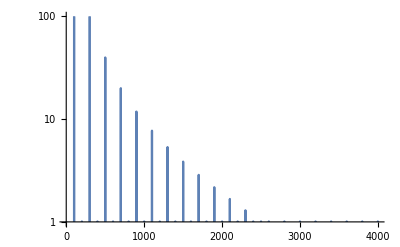

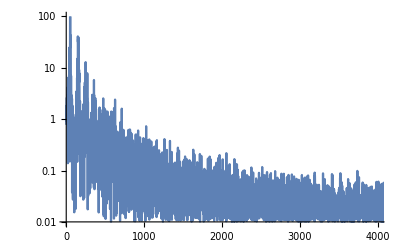

The second clock looks (superficially) very like a normal clock, it’s only if you look closely at the exact zero-crossing times that you see something is a little off; they’re “around” multiples of 100, but are not at exactly such multiples.

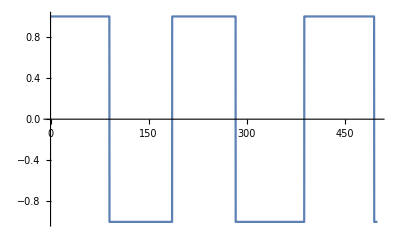

### (2014) managing clock frequency transitions

Consider the following problem. 
A mobile core is constantly changing the frequencies of various IP blocks, and we want this frequency change to be as rapid as possible. The frequency change requires changing the parameters of a PLL circuit, and it is an unfortunate fact of engineering that during the transition of the PLL from its initial frequency to the final stable frequency, the PLL may generate some clock transitions that correspond to a higher frequency than the target. This is bad because if the transistors in the IP block are required to change state faster than their design point, they may be corrupted, so eg a register, or a value being transferred to an ALU, may be corrupted, and after that happens all you can do is restart the entire device. 
It's also a fact of life that if an entire IP block is immediately shifted to a higher frequency, current draw will rise because of inductive effects, and we want to avoid this because there is a limit to how much current a battery can supply. 

The Apple solution, (2014) https://patents.google.com/patent/US9411360B2 Method to manage current during clock frequency changes is simple but elegant. We isolate the PLL from the rest of the IP block via a programmable divider. 
So assume (to use simple numbers) that the IP block is a 2GHz, and we want to switch it to 3GHz (which is its maximum frequency) but during the transition, the PLL may generate some 4GHz overtones. We tell the clock divider to divide the frequency by 4 at the same time that we switch the PLL to 3GHz. Because of the clock divider, the CPU will see a somewhat varying clock, but never faster than 1GHz. We can then change the clock divider to 3, then 2, then finally 1, and ramp the clock increase in a controlled way. In fact Apple suggest having the clock divider capable of a few fractional rates (eg send through 2 of 3 clock pulses) to allow for an even smoother transition, eg from 2 to 3/2 to 4/3 to 1.

A similarly basic but necessary building block has to do with voltage stabilization. 
Under DVFS, when increasing frequency, one first needs to increase the voltage and wait for it to stabilize, then increase the frequency. But when is the voltage stable? one can program a fixed (necessarily worst-case) delay, which slows down the transition. Or one can have a dedicated sensor circuit that informs the PMU when the voltage has reached its target, as described in (2010) https://patents.google.com/patent/US8892922B2 Voltage detection. The system is even sophisticated enough to indicate that the desired voltage has not been reached (presumably because the rest of the SoC is doing so much work, though possibly also the battery has decayed somewhat), in which case the PMU will abort the attempted frequency increase.

#### (2015) maintaining a global timebase

The basic clock is simply a series of ticks, but for many purposes we also want a timebase, ie the ability to ask some agent how many ticks have occurred since some reset event. Rather than query a single agent (which may be many fabric hops away), the system provides for multiple local timebases, along with periodic resynchronizations to ensure that they do not drift too far apart (and that the correction does not result in anomalies like the timebase running backwards) or jumping too much. 
(2015) https://patents.google.com/patent/US20170168520A1 Timebase Synchronization.

### (2013) security to prevent over/under-clocking

Apple doesn’t especially care whether you overclock (or underclock) your device with liquid nitrogen for the purposes of boasting to your friends. But they do care about the fact that one of the techniques used by truly professional, nation-state or organized crime level adversaries, is to over or under clock devices to the point that  they exhibit a logic failure which allows the device to enter a state in which it can be manipulated in ways outside the design spec. 
To prevent this possibility, the chip includes circuits that detect such out of spec timing:
(2013) https://patents.google.com/patent/US9135431B2 Harmonic detector of critical path monitors.

## Debuggability

We’ve seen how, as Apple controls more of the SoC, power management, clock management, bandwidth management and so on have all be centralized. 
I’ve not said much about debuggability in these documents, but obviously a practical concern when designing IP blocks and the entire SoC is ways to look into it for debugging at various levels (along with the somewhat similar performance monitoring). And so like these other fields, a centralized debugging control block was added, communicating with multiple local debugging blocks. 
If this sort of thing interests you, a place to get started is what looks like the master patent: (2012) https://patents.google.com/patent/US8799715B2 System on a chip (SOC) debug controllability. 
There are various somewhat interesting aspects to this, for example if you’re engaged in a somewhat higher level of debugging and can assume that low-level aspects of the SoC are trustworthy, then you can use particular special messages on the Fabric to query the state of different IP blocks, as described in (2012) https://patents.google.com/patent/US20140173342A1 Debug access mechanism for duplicate tag storage. The advantage of this scheme is that you save the area costs of providing a second, dedicated, debug network.

## Secure Enclave

Secure Enclave, like other secure issues, is something I’ve mostly avoided, but if it interests you , you might start with (2012) https://patents.google.com/patent/US20140089617A1 Trust Zone  Support in System on a Chip Having Security Enclave Processor and 
(2012) https://patents.google.com/patent/US20140089712A1 Security Enclave Processor Power Control, from which you can follow out the associated patents and the inventors to find more relevant links. 
Two that may be of particular interest are (2014) https://patents.google.com/patent/US9547778B1 Secure public key acceleration, which describes how the mailbox interface is used to communicate with the Secure Enclave, and
(2015) https://patents.google.com/patent/US9747435B2 Authentication and control of encryption keys, which describes some of the bitfields used in communicating with it.

## Cluster scheduling

### vouchers

We start with an OS concept that is apparently unrelated to thread scheduling or clusters, but which forms the basis of most what we will see next.
(2014) https://patents.google.com/patent/US9665398B2 Method and apparatus for activity based execution scheduling introduces Vouchers, a new OS concept upon which has been based much of the evolution of Darwin since then. 

Vouchers are a general solution to a large number of OS problems which can be categorized, somewhat vaguely, as “connecting one thread/process with another”. A paradigm example of this is process A wanting process B to perform a task for which only process A has permission/authorization/entitlement. 
There are a number of schemes that are supposed to deal with this sort of issue, all different depending on the resource to be controlled (permission, priority, power, ...) and none very general. Vouchers are essentially 
- a non-forgeable collections of key/value pairs 
- that can be sent to another process via IPC
- but only via very particular, controlled, IPC paths, which allow for revocation and reference counting.

The result is that we have a general mechanism to pass “resource access” from one process or thread to another while (and this is important) being able to kill the power granted by that resource access whenever the primary owner wishes. 
This can then be used for a variety of tasks. Controlled security is one (approximately “I give you my access permissions to perform some task, with the ability to revoke within a time period or once I get the results of the task”), but others are things like tying together a group of apparently unrelated tasks into a DAG for purposes of common priority and common scheduling, or even for bringing some degree of control to when the machine wants to cut power and needs to ask various tasks whether they want to veto this or not. And of course this also makes it easier to understand accounting (which process is using memory, energy, network packets, whatever) even when the user app has delegated tasks to various OS demon apps.

Another way to look at this is that a particular thread may need a particular "context" (permissions, priority, dependency on some other thread, accounting, ...) that exists for only a particular task being performed. Vouchers provide a way to enqueue that context, along with the associated task, in a GCD queue, with the context ending once the task is completed. Viewed in this way, most of the OS demons now become almost like callable function; they are provided with a block of work together with a context, and execute almost as though they were embedded in the calling app (with same priority, same privileges, same accounting, etc).

As a different sort of example, suppose the user starts scrolling. A short-lived “activity ID” can be created in response. Via vouchers, this activity ID can be propagated to various threads that may become involved (the UI thread, maybe some OS network threads loading content, maybe some Apple API decompression threads using hardware to convert network packets to images, etc) and this activity ID can be used to group all these threads together for the purposes of scheduling – for as long as they are all using the same activity ID voucher, which expires when the activity is complete. 
Activity IDs can cross process boundaries, and so form a useful way for the OS to understand, moment to moment, which threads are working together, much more so that static IDs like process or thread IDs. 

If this sounds interesting to you, the patent gives great detail...

### OS scheduling

There remains the issue of how the OS decides on “appropriate performance levels”, ie DVFS, which threads to run on E vs P cores, and which threads to run on the multiple cores of a given cluster. 
This (2016) https://patents.google.com/patent/US20170357302A1 Processor unit efficiency control is a basic explainer, 
with (2017) https://patents.google.com/patent/US10884811B2 Scheduler for AMP architecture with closed loop performance controller using static and dynamic thread grouping giving much more detail. (This now very much straddles like line between OS/API functionality, but helped out by a lot of SoC/CPU hardware.)

It's hard to convey just how glorious this second patent is! The ideas are (once you finally understand them) pretty impressive, but the whole thing looks like a briefing from the Pentagon, complete with thousands of acronyms and impossibly complicated diagrams like

-Graphics-

#### the old days

Before even trying to understand this patent, understand the problem to be solved.
OS scheduling has always consisted of trying to balance off various desiderata. 

On traditional (but fairly recent) desktop systems, the goal is to maximize responsivity while keeping throughput reasonable. This tends to be done by heuristics as to what are “user interacting” apps, and giving those priority boosts. There was a time when VM concerns were an essential part of this, and much of the scheduler's prime responsibility was to prevent thrashing (ie running simultaneously more than one app that was using a large amount of DRAM); presumably this is still a background concern but of much less immediate import.

Along a different dimension we have server scheduling. In this case throughput may be considered highest priority, and the most important trick is trying to pack together on different cores applications that each stress a different  part of the overall machine, hence a few high memory bandwidth processes together with a few low memory bandwidth processes, perhaps a high FP/SIMD process on one hyperthread together with an integer-only process on the second hyperthread, and so on.

Both of these versions of the problem are trying to map from a set of runnable processes, with a set of (somewhat known, depending on exactly what the SoC and the programmer provide) characteristics onto a set of cores, to optimize for something like performance. 
As a second tier goal, the OS will futz around with DVFS, but overall without much intelligence beyond a few very basic points like “don't exceed a certain temperature or power draw” or “if all the processes are known [somehow...] to be background, then reduce DVFS”. Those readers who follow Linux will know of the never-ending travails of Linux and Android scheduling in the face of DVFS, a matter that's still not really satisfactory after all these years.

#### the simpler, 2016, solution

Before the truly complex solution, let’s consider the easier 2016 patent which is appropriate to A7..A10 class hardware. Neither clusters nor visible E vs P cores are part of this hardware.
Apple’s goals are to hit performance targets (eg smooth UI) at minimal energy expenditure. The tools available are 
- how many cores to power up
- DVFS of the cores
- less obvious, but also relevant, modifying the frequency of the SoC fabric and the DRAM

The basic flow of control is to have a first stage of scheduling that establishes performance goals. Think abstractly of “achieve state X by time Y” where X is some approximately knowable fraction of the total amount of work we want to achiever by a deadline. 
How do know how fast to run the machine to achieve those goals? This is the role of the CLPC (closed loop performance controller) which essentially means you keep measuring your progress and, if you are going faster than necessary to meet the goal, slow the machine down; otherwise speed it up. 
This, in turn, means that, to a first approximation, we describe performance as a monotonic map from n cores running at maximum frequency down to 1 core running at minimum frequency. Depending on how well we’re meeting the target, we continually move up or down this performance map. 
[Of course there are two extreme cases of “as fast as possible” which is the default for third party code where nothing special is indicated, like, eg Geekbench code; and “as low as energy as possible” which will be the case for almost all cases where the screen is dark and only background code is running. 
However much executing code is media decode, animation, audio, even much network and IO, which fit this deadline model.]

But this first stage only gives performance, without energy concerns. So the output of this stage passes through a second level of control which worries about energy and performance. 
One part of this concern is easy. Things like device skin temperature, temperature at various extreme parts of the SoC, and short-term power draw are tracked and high performance levels which might cause these to be exceeded are dialed back. 
So essentially step A says "I'd like to operate at this performance level" and step B says "given current circumstances that runs too hot/draws too much current;  dial it back to this maximum performance level allowed by thermals, battery, low-battery mode, etc".

Beyond that upper level constraint, the efficiency controller is tracking an “energy per instruction” metric and trying to optimize this while not impairing the performance goals.
An especially interesting part of this is that, although there is an override mechanism (which forces the energy/instruction cost to 0 as long as it is active) most of the time the controller is trying to maximize energy efficiency. This might sound bad, like it will hurt performance, but mainly what it's saying is
- if you're constantly waiting on DRAM, then running the core at high frequency does you no good anyway
- if you're not running very wide (hard to predict branches, or long dependency chains) you can't take advantage of the big core anyway, so why waste power keeping you there rather than on an E-core?

To make all this work well 
- one needs good metrics, and a lot of the patent is about how the energy is measured (over “long” time intervals) and estimated (over “short” time intervals) to inform these decisions
- one also needs a good control framework. Anyone who has ever tried to write control loop software knows that it's very easy to have the system oscillate wildly; or alternatively, if you try to prevent that, to respond to changes so slowly as to be useless. 
So another large part of the patent is about that control framework. 

- not stated, but an obvious and easy extension would be metrics that are somewhat orthogonal to these primary metrics. For example performance might be lower than we wish because either the CPU is too slow or DRAM is too slow. 
This makes our control problem two dimensional, but the basics remain the same – change one or the other of the DVFS knob and the DRAM frequency knob, see how performance and/or energy efficiency changes. This allows us to calculate scaling coefficients (ie derivatives) telling us the response to both of these knobs, and we can use those scaling coefficients to calculate an optimal point (which will of course keep changing as the code keeps changing). 

It’s worth comparing this to just how simple traditional OS scheduling is. 
A traditional OS scheduler may make an approximate (heuristics-based) classification of apps into interactive vs batch, but apart from that scheduling mainly consists of attempting to provide some approximation to “fairness” in terms of fraction of time for each app, and implemented primarily through a decaying priority attached to each app. A primary concern in the past was issues related to paging, ie which apps are paging excessively and handling them in particular ways. 

Apple seems no longer concerned with the paging issue (I don’t know if that’s as true of the competitor OS’s). Perhaps the closest equivalent is a concern with tracking apps that are using excessive amounts of memory and dealing with them in various ways, from sending a notification of excess memory usage to, if appropriate, restarting them. 
Not usually present in other OS’s (but present in Apple’s solution) are
- fine-grained classification of apps into QoS classes
- attempts to schedule together threads (from the same or different apps) that work together, at a very dynamic level (ie the threads that work together can constantly change, as tracked by vouchers)
- scheduling optimized for E vs P cores,  for clusters (as opposed to single cores), and for power (ie taking into account how DVFS should be switched as loads are scheduled on and off the clusters).
- scheduling informed by a lot of telemetry from the cores and clusters (ie the OS has access to information about the extent to which a particular thread is missing a lot to DRAM, or is making heavy use of AMX, or is constantly snooping on cache lines modified by a different thread; and in principle this information can be used to inform scheduling. The extent to which this information is used and how is probably in constant flux, month by month, as the OS writers try and experiment with new things.) 
In principle other OS’s could do the same thing; in practice doing so requires a uniformity across target devices that mostly isn’t present except for Apple. (Maybe IBM could likewise exploit such telemetry?)

#### the 2017, cluster-aware, solution

The above is a good start, but we need something much more sophisticated for the A11 and later. We have the same concern of course, for responsivity and low energy usage, but we now have the complications of 
- there are both P and E cores
- these are grouped into clusters and clusters run at a fixed frequency. So we can, eg, use three cores of a 4-core cluster, but we can't run two of the cores as fast as possible and two as slow as possible

To do this as well as possible Apple introduce a few new concepts. 

• One is the Thread Group, a group of threads that are scheduled together, so in a sense the cluster is given a unit of work rather than each core being given a unit of work. Thread Groups are dynamic. They are constructed at the start of execution from various data (heuristics, indications by the programmer, ...) but threads can constantly move between Thread Groups if this makes sense. 
Various OS technologies, most importantly the already described Vouchers, allow the OS to see when two threads (perhaps from the same process, perhaps from different processes) are working together, and these threads will be united in a Thread Group to schedule together as much as possible.

• Another concept is the Work Interval Object, a way to describe a task (perhaps worked upon by multiple threads) which has a known deadline and a known progress towards that deadline. For tasks which match this model, (think eg of audio playback or UI animation) the task (ie the set of threads) can let the OS know of its performance as it progresses, and the OS can see that the threads either need more performance, or can relax a little, to meet the deadline. 

Neither of these are meant to describe all code under all circumstances. But they do cover a lot of types of code, and they can be used by the OS to perform substantially better scheduling (ie fast enough, while saving a lot of energy).

The basic structure, now, is
- we create thread groups
- every so often we may move threads between thread groups depending on the heuristics described above (eg one thread is in a producer/consumer relationship with another), or on vouchers
- thread groups, based on the various metrics and how well those metrics match our desired performance goals, will result in a control effort, a number between 0 and 1, which is mapped to a cluster (P vs E) and a DVFS level for that cluster
- this (optimal) control effort is looked at by various concerned parties that care about, eg, skin temperature, die temperatures, short term and long term current levels, user-performance settings [low battery mode] etc; and reduce the control level if a particular concern requires that
- the thread groups then sit in a queue (E queue and P queue) and, when they get their chance, are run at the suggested settings.

Note a few consequences of this:
- suppose we have many desired low performance tasks but few to no high performance tasks. Eventually some of the low performance tasks will be far enough behind their desired metrics that the control effort will map them onto P cores. So no special effort needs to be made to wake up P cores when only the E queue is populated.

- what about the reverse situation where there are excess tasks in the P queue? Should they run on the E-core? 
The Apple answer is yes, but... Running them on an E-core is not an immediate win, because there is some overhead involved in switching E-cores on, and in the transfer of state from the P-complex (eg data in the caches) to the E-complex. 
Apple handles this via a special interrupt with an associated timer – the interrupt is set to wait a certain amount of time before waking up an E-thread and having it begin executing the P-thread, and may be canceled if the scheduling problem resolves itself before the interrupt fires.
There is never an effort to move in the reverse direction; E-threads will not move to vacant P-cores until the natural control-effort mechanism drives them to demand P-level performance. 

This scheme is complex, but has obvious advantages. For example it naturally groups together (running at the same time, on the same core complex) threads that may be interacting (producing data for each other, sharing data and so using the same locks), and such threads will have rapid communication through their shared L2.

One thing that is not fully explained is how this scheduling in terms of thread groups maps onto individual threads and cores.
Obviously a few cases are easy.  eg
If a thread group consists of four P-threads and nothing else is running, presumably on an A14 with only 2 P-cores, two threads will execute this scheduling quantum and two the next quantum, both at the same DVFS settings. 

But what about imbalance situations? 
This is not described (the patent cares mainly about the concepts I have already described) but I think the way it works is 
- we try to schedule thread groups together, but
- if a core or two becomes free and there are runnable threads in the queue, they will be scheduled into a core and
- the DVFS setting (ie the control effort) will be at the highest level of all the thread groups that are running on that core.

A way to think of this is 
- it's not that slow code is wasting energy by running at a higher performance level than necessary; 
- rather it's that we are running fast code at its appropriate speed, and if there's some slow code that needs to execute, well, we might well take advantage of the fact that the cluster is awake and the L2 is awake, so get it done even if it's executed faster than really necessary.

So what we get from all this is a collection of threads, tagged by core and frequency, that are placed in E and P- runnable queue. Finally at each scheduling operation we try to pull out from these queues something that matches all the work we have done. 
Once again I remind you: the common case, the one we are optimizing for, is that most cores are idle most of the time, and we're not in fact trying to pack every core as tightly as possible with work! eg if we have four independent light-weight tasks lined up, the preferred scheduling may very well be to run them all sequentially on a slow-E-core, rather than fire up four E-cores, or run that single E-core any faster. 
Obviously there are escape mechanisms whereby the system is tracking if the runnable queues are growing too large, at which point the obvious types of things will kick in,  but the interesting stuff Apple is doing is primarily about keeping the system “feeling” fast while, in fact, most of it runs as slowly as possible, and it ramps up to running more cores faster as effectively as possible. (Effectively meaning:
- know how fast you want to be, and compare that to what you’re achieving. Measure, measure, measure!
- try to keep threads that are working together scheduled together)

Following this particular topic goes into a whole other world of OS technology, scheduling, transferring priority between threads, etc. Far far from our starting point of CPUs, so we'll leave it here.

#### some thoughts on E vs P cores

The E vs P, or big vs little distinction generates a lot of (somewhat silly) argument, because every vendor actually has slightly different primary goals in mind with this distinction; and you will miss the overall design target if you insist on forcing one design into another vendor’s scheme and priorities. 
For example, it seems like Intel’s primary goal for their E vs P cores is less about saving energy than about  increasing the compute per unit area; when you look at an Alder Lake design this way, certain choices make more sense. 
Likewise ARM’s priority seems to be more about area reduction for its little cores than energy reduction per se.

In the case of Apple, a helpful way to to think about the E vs P distinction is that the E cores are “cores for the OS”. These are not hard and fast rules, but, for the most part, the OS tries to run its kernel tasks, its demons and various utility work, and even, I believe, most interrupt handling, on E cores. 
Conversely P cores are for developer code except for obvious cases where that developer code is "utility-like". 

This also explains the 4 vs 2 E core split. 
The low power devices provide 4 E cores primarily so that they can run those cores at low frequency, and so get the OS work done over multiple cores, running at around 1GHz and so at very low energy. 
The higher power devices (Pro, Max, ...) run a single E core at 1 GHz (under conditions where there is really very little OS background work happening, but as soon as there are two or more tasks to schedule on E cores, the 2 E cores are boosted to 2GHz, giving you effectively the same “OS performance”, under most conditions, as the 4 E cores of the lowest end 4+4 M1. You save a little area at the cost of a little more energy; probably the right tradeoff for the larger M1 chips. 

Using special E-cores for the OS is an interesting choice which might not make sense to people who primarily work with server-type designs (where 50% or more of CPU can be spent in the OS), but it makes sense for almost all of Apple's users. 
Even some more aggressive OS use cases, like substantial network usage, fit this model given how much of Darwin's networking is now in user space: https://developer.apple.com/videos/play/wwdc2018/715/
And of course OS work can move onto P cores when that makes sense. 

Another interesting comparison data point is consider something like IBM’s large z/ machines. These might have something like 240 cores, of which user code might see about 190. The rest are reserved for various purposes, but the largest purpose is that they execute various OS/IO/firmware related code. 
So, in a sense, landing up at much the same place as Apple, though the details are very different.

## AMX

There’s a very nice sequence of patents that shows how AMX capabilities have grown.
To put things in context, AMX was publicly revealed as part of the A13 in Sept 2019. 
It’s generally believed that the version of AMX in the A14/M1 is a version 2, and there’s probaby a version 3 in the A15. As we read below, we can see likely transition points for each successive version.
As usual, Dougall did some of the initial exploration, described here:
https://gist.github.com/dougallj/7a75a3be1ec69ca550e7c36dc75e0d6f
What we will see is that the patents generally validate his analyses, sometimes clarifying points. 

There’s a more recent, much more detailed, followup here by Pete Cawley:
https://github.com/corsix/amx
Depending on your tastes, you may prefer to first read my analysis (which shows how the system has evolved over time) or Pete’s analysis (which mostly confirms my patent-based analysis, but gives the state of the art right now, without showing how it evolved). 
Whichever order you choose, I’d suggest you read both. 

Finally https://jott.live/markdown/1.5tflop_m1 gives some diagrams of how the outer product operates, and how you might use it, along with some details of using AMX in practice (and getting best performance).

### (2016) outer product engine

We start with (2016) https://patents.google.com/patent/US20180074824A1 Outer Product Engine which describes the basic idea.
- We have a coprocessor that's associated with a cluster as a whole (so you can think think of it as "attached" to the L2.
- Specific instructions are added by Apple to the ARMv8 instruction set, and begin "execution" in the CPU but transfer control to asynchronous execution on the AMX unit.
- As far as the CPU is concerned, these instructions flow through the load/store pipeline. Some of them are AMX loads or stores, and these are translated by the TLB. 
- The AMX instructions then accumulate in some structure (probably the ROB) until they are none speculative, at which point they are sent to the AMX unit and are complete as far as the CPU is concerned. 
- Meanwhile the AMX unit accepts these instructions in an instruction buffer and executes them.

Before getting to what AMX does, consider some consequences of this. 
- AMX structures are large! (The X and Y vector registers are each 512b(=64B=8 doubles) in size, the Z matrix register is 512B(=8×8 doubles) in size.) Are there alignment restrictions?
Unless one is careful, almost every load/store is going to straddle cache lines. This is probably handled efficiently, but load/stores that straddle pages (and so require two TLB lookups) probably revert to micro-code and could result in a substantial slowdown, even worse than the slowdown we saw for "normal" load/stores that cross page boundaries. 

- there are multiple CPUs in a cluster. How do they share AMX? The answer appears to be that there are four replicated sets of registers, one for each CPU. Instructions come tagged with their CPU (and thus their register set) and can be interleaved as appropriate, should multiple cores land up using the AMX unit. 

- the patents do not go into this, but when I refer to the X, Y, or Z registers, these in fact should be thought of as 8 X, 8 Y, and 8 Z registers. The exact instructions specify which of the 8 is used in each case. 
- the patents suggest a model of X, Y, and Z register and possibly a cache. It's possible that in actual implementation (given how large the registers are, and the 4x replication for each CPU) that the "cache" is something like the primary store for the registers, so each operation execution is pipelines as something like "load the 'register' content from the cache into the register store for each register, then begin the actual execution".

- the patents say nothing about OoO execution one way or another. Dougall's experiments suggest some degree of OoO execution is possible, and of course instructions from different cores should be interleavable without difficulty. 

- operation of AMX is asynchronous with respect to the CPU. The usage model is that the CPU will queue up a sequence of operations (so create the data of interest, then send a sequence of loads to AMX, then a sequence of arithmetic operations, then some stores, at which point the data of interest is in memory and can be accessed by the CPU if required). But how is this synchronized? If I simply fire off operations to AMX and they (eventually...) complete, how do I know they have completed? The answer given in this patent is that there's an AMX barrier instruction, so the model is presumably 
+ fire off the AMX operations
+ do whatever other work you can find
+ when you need to interact with the AMX output, execute the AMX barrier instruction, which will block until the last AMX instruction (from your CPU) indicates it has completed, at which point the data stored in memory will be valid. 
This same barrier is probably used for other messy situations, like context switching. 

- AMX appears to draw its data from the L2. This means loads and stores are a few cycles longer than on the CPU (no big deal) but also the somewhat surprising fact that accessing data in an L1 is slower than accessing data in the L2, since L1 data will first have to be transferred to the L2 (as per coherency). 

- if you've been paying attention, this all suggests that there is an AMX unit associated with the E-cluster as well as the P-cluster, and this is the case. The E AMX unit has less hardware, and so performs its tasks by taking multiple cycles to do what could be done in one cycle of the AMX P-cluster. 

We can summarize all this in the diagram below:

-Graphics-

with the division of responsibilities looking like

-Graphics-

Now, what does the engine actually do?
As of this first patent, it performs an outer product (also known as a Tensor Product), that is, it takes two vectors v_i and w_j and produces the matrix v_i w_j. Two N-length vectors generate an N×N matrix of products, each matrix element the product of one v element and one w element.

-Graphics-

More precisely, treating registers X and Y as vectors, the tensor product X⊗Y is added to matrix register Z.
I will not explain this here, but this is a primitive that can be used to perform matrix multiplication. To simplify things:
- if you only have scalar operations available, matrix multiplication of two N×N matrices takes N^3 operations
- if you have N-length vectors, then it takes N^2 operations where each operation is a dot-product
- if you have N-length vectors and an outer product operation, the multiply takes N outer products. 
The outer product primitive, like a dot product primitive, can, with some careful ordering of the loads, multiply-add’s and stores, be used to multiply matrices that are larger than N .

So the basic primitives to perform a large matrix multiple are:
- clear Z (fill it with zeros)
- load X and Y
- perform a multiply-add (X⊗Y+Z→Z)
- load the next X and Y, perform the next (X⊗Y+Z→Z), and keep doing this
- store Z to memory
- provide a memory barrier for the CPU to synchronize with the AMX unit

Now that we have a basic understanding, let’s consider some further details/complications. 
I have described the design so far in terms of doubles, so that two 8 length vectors together create an 8×8 sized outer product. 
Suppose I want the scheme to also support floats. Then, at the most basic level, this means I now input two 16 length vectors and generate a 16×16 sized outer product. But think about the geometry of this. 
Suppose I have a layout of 16×16 fp32 multipliers generating 16x16 outputs. Without too much difficulty, I can “wire” pairs of these together to act as fp64 multipliers, but that would give me an array of 16×8 fp64 multipliers! Which doesn’t match the 8×8 layout that I want. 
You can imagine various ways to solve this, but the Apple solution is (bear with me, this is the simplified first explanation, not the final truth) that 
- when we treat Z as an fp32 matrix, we treat it as a layout of 16 rows of 16 columns (each 4 bytes in size) so 16 rows each 64B in size
- when we treat Z as an fp64 matrix, we treat it as a layout of 8 rows of {
	+8 columns (each 8 bytes in size)=64B
	+empty row of 64B
	}
so every alternate row of 64B goes unused.

There is an alternative, much more helpful, way to look at/think about this which Apple gives in a later patent.
In this model the baseline AMX compute engine consists of an 8×8 array of PE’s (Processing Elements). Each PE consists of the following items:
- one 64b FP multiply-adder
- two 32b FP multiply-adders
- four 16b FP multiply-adders
- eight units of 64b storage
It’s clear, in this model, how an elementary 64b outer product would take an X register and a Y register, along with a Z-register specifier (one of 8 output rows) and store the result as appropriate. 
If you bear this model in mind, it becomes easier to understand how the 32b and 16b schemes work. Since there are two (but not four) 32b multiply-adders, we can only perform half of a 16×16 FP32 outer product in one cycle, and we need to somewhat careful to specify which of the 8 possible rows of Z storage gets fed the output, along with being careful about whether the even or odd FP32 elements of the Y register are being used for the outer product. The details are obvious and uninteresting, once you get these basic point of 
- 8×8 PE’s
- each PE has 2 FP32 multiply’adds (because it is “fairly simple”) to add some extra wiring and use FP64 MAC HW as a pair of FP32 MAC units
- likewise for 4 FP16 units
- some portion of Z storage is likewise localized to each PE.

Now let's give the full story (well, still not quite yet!)
Suppose we supported 8, 16, 32, and 64bit multiplies. The logic described above tells us that 
- at the "root" level we want an array of 64×64 multipliers to handle the 8bit multiplies. 
- or we pair these together to provide 32×32 16b multiplies, with the results dumped into every second row of the Z matrix. 
- or we pair together the 16b multipliers to give us 16×16 32b multipliers, dumping the results to every fourth row of the Z matrix
- or we pair together the 32b multipliers to give us 8×8 64b multipliers, dumping the results to every eighth row of the Z matrix. 

Dougall has uncovered that there is definitely fp64, fp32, fp16 and int16 multiplier support, all of the form described above. Maybe there is also int8 support, simply because of the offset pattern described above? I'll get to that in time. 
One additional complication is if you are performing fp work you're probably OK with having fp64 generate an fp64 result, and likewise for fp32 and fp16. But if you are working with 16 bit integers, you may want the intermediate values (the result of the multiplication, and the accumulated results in the Z register) to 32b wide so that you don't encounter integer overflow. The system allows for that by having the 32×32 16b multipliers generate a result that's 32b wide, and by using every row of the Z matrix rather than skipping every second row.

Note also that a subtract primitive is provided so in addition to (Z+X⊗Y→Z) we also have (Z-X⊗Y→Z). This can be used to calculate the negative matrix product -A×B rather than +A×B. 
(Possibly, with some careful layout of the real and imaginary parts, this could also be used for the multiplication of complex matrices? I haven’t looked at this and I don’t know if anyone at Apple has either.)

This covers the 2016 patent, and basically covers AMX operations:
0,1,2,3,4,5: load and store X, Y, and registers. 
10,11; 12, 13; 15,16: multiply-add or multiply-subtract X and Y onto Z, either fp64, fp32, or fp16.
17: enable/disable AMX
unknown op code: memory barrier

Now think about this design as we have given it, in terms of an 8×8 array of PE’s, each with local storage. How can you get more value out of this design?
We start with the fact that each of the X and Y registers feed values to each PE. In this most basic version, the X values  read from a register are replicated as they are fed to a column of 8 PE’s; likewise the Y registers are replicated as they are fed across a row of PE’s. We could add logic and wiring to these data dispersal networks to feed different patterns of data from the X and Y registers into the 8×8 array of PE’s. However we are somewhat constrained as to output; we can’t likewise arbitrarily reroute the data generated by the PE’s because each PE stores its results in some part of its 8×64b rows of storage. 
Secondly we can suppress some of the PE’s so that they don’t do anything, and in particular, don’t overwrite their results, which allows us to work with subsets of 8×8 arrays (for doubles, or subsets of 16×16 FP32 arrays, and so on). 
Once we are doing this sort of suppression of writes, we can start to imagine executing more than one instruction at a time, as long as the Z-elements involved are discontiguous! For example we can imagine perform one set of operations that only uses the first two rows of the PE’s, and a second set of operations that uses the lower 4 rows. 
Finally we could imagine adding additional hardware to each PE. For example we could add a 64b ALU to each PE to provide AND/OR/NOT functionality. (Very cheap. Useful? Hmm.)
Over time, we will see that these are the dimensions along which the AMX engine evolves, along with various schemes to reduce energy.

### (2017) matrix engine

#### smaller matrices

Once you have  new toy, of course you immediate start thinking about how it can be extended. 
The outer product engine is great, but it enforces large minimum sizes for the matrices. Even if we’re operating on doubles, the minimum size is 8×8. You can handle smaller matrices (and padding, if your larger matrices are not a perfect multiple of 8×8) by padding X and Y with zeros, but that means so much wasted computation. Can we do better?

That’s what (2017) https://patents.google.com/patent/US10346163B2 Matrix computation engine is about. Essentially instead of providing X and Y as vectors, they are now arrays of 2×2 matrices. This reduces our minimum size by a factor of two, so that we can now optimally handle 4×4 fp64 matrices. 
The basic primitive added is the packing of a 2×2 matrix into an X or Y vector, and the multiplication of an outer product of the resultant arrays of matrices. Again, this is a great primitive for matrix multiplication, again I’m not going to explain further! The diagram shows what you now get. The blocks marked MAC are now 2×2 matrices formed from the product of each X source matrix and each Y source matrix. 
This is a version of rearranging data as it flows from the X and Y registers into the array oF PE elements.

-Graphics-

In addition to allowing smaller matrices, we’re now using twice as many multipliers (each destination element is constructed from two multiplies, not just one) so we could be twice as fast. But perhaps current implementations run the multiply pipeline twice for each element, rather than doubling the number of multipliers, so we get a small boost but not doubling in speed?

#### smaller elements

The other feature this patent adds is the ability to multiply smaller elements. Everything so far has been traditional numerical linear algebra, performed on fp64, fp32, or fp16. But, as you may know, AI both uses a lot of matrix multiply and likes to multiply by “weights” which can be small numbers, or, more precisely, can be one of just a few values. 
Imagine that we gave our engine 8bit integer multipliers. (The previous patent, and the early parts of this patent, are somewhat vague on whether integer multipliers are part of the package.)
This would be a start towards providing a powerful matrix engine for AI, but even a width of 8bit is more than we may really want, specifically in that we want to store our weights in as few bits as possible to limit memory traffic. 
So what Apple also gives us is a lookup-table functionality as in the diagram below:

-Graphics-

We get the same 2×2 structure already described, but only 2 or 4 bits of each byte entry matter. Those 2 or 4 bits are routed through a lookup table (of 4 or 16 entries), what’s looked up is (I would guess) an 8bit value, and we ultimately get an 8b by 8bit integer multiply. 
At this same time, perhaps, it would make sense to add a 16b integer multiply.

If we validate against Dougall, we see that op codes:
6,7: load, store the Z matrix in 2×2 layout (at least I think that’s what’s going on once you understand that this 2×2 layout is a possibility, and want to use it in various ways?)
He also saw something that looks like a lookup table operation, presumably hooking into the functionality I described above. 
What we don’t see is anything suggesting an 8b by 8b multiply. Perhaps that will come, or perhaps AMX is designed to go down no lower than 16b by 16b (meaning the lookup table will be a 16b lookup, and there may be a 256 entry 8-bit version), and if you want 8b by 8b multiply you should be looking at the NPU?

My conclusion, looking at Dougall’s results, is that while this 2×2 packing is very cool (and should be added to the fp operations) it has not been added yet. Rather what it looks like is the 2016 patent described a pure outer product engine for fp, and the 2017 (and subsequent) patents describe adding modifications to that engine to make it an integer AI engine. Many of these modifications (like table lookup, and much of the data re-arrangement stuff we will see) may not be useful for fp use cases, but the 2×2 packing is useful, and could be retrofitted easily with a few additional instructions. Really doing the job right would also add some control bits in the relevant op codes to provide complex multiplication...)

In line with the idea that int16/AI support was added later, the int16 opcodes have the following extra bit twiddles compared to the fp opcodes. The one we’ll discuss now are:
- a bit that does or does not add the Z matrix (so you don't need to clear Z before you start a series of multiply accumulates)
- a bit to indicate (as I already talked about earlier) whether we want to accumulate 16b×16b→16b operations or 16b×16b→32b operations 
- some other control bits that do things like prevent the multiplication (which I assume means we just propagate values from either the X or Y register into Z, which sounds useless, except that it gives you a wide table lookup operation...)

I think the bits 62 and 63 that Dougall describes in a slightly confusing way ultimately translate into the two options
- multiplier output is 32b wide vs 16b wide
- vector inputs are arrays of 2×2 matrices rather than pure vectors

### (2018) strides

Next we get (2018) https://patents.google.com/patent/US10642620B2 Computation engine with strided dot product. 
Now the idea is we have available long vector registers (eg X or Y hold 32 fp16s or int16s). Suppose we treat that long register as holding, say, 8 sub-vectors each of 4 elements, and we want to perform operations involving these sub-vectors, like forming the dot product of the 8 X sub-vectors against some of the Y sub-vectors. 
Again we’ll ignore the details; it’s basically one more way to make use of the fact that we have a huge number of multiplier-adders, and it’s all about exactly which elements  of X get multiplied and added with exactly which elements of Y. The bottom line is that we add one more instruction specifying that what we want is a dot product, and exactly how we walk down the Y vector (that’s the stride part of the patent, it’s the part that’s new, and it’s the part that allows this to work as an interaction of sub-vectors with sub-vectors). 

Another way this could be used (it’s very unclear from the patent exactly what’s provided!) might be to handle the “transposing” of one of the source matrices in a multiply.
Recall that the basic outer product engine takes two vectors, and one can uses this primitive to perform a matrix multiply by stepping successively through the columns of one matrix and the rows of another. That’s fine, but it means that somewhere, outside the AMX engine, we have to either transpose a source matrix or load a column, one element at a time, and store it in some temporary sequential array that we can pass to AMX.
Suppose, however, that we load eight sequential rows of the matrix, then use this strided dot product primitive (striding by eight) to form our outer product. That could (if we have the right set of controls available) be used to provide on-the-fly column-to-row conversion. 
The primitive described by the patent does not seem powerful enough for this, but it seems like something that could be added without too much difficulty, and as you will see, fits into the ongoing generalizations of the design.

I think  this ultimately corresponds to the bit fields in Dougall’s analysis that he calls row/column disable. He’s treating them as bit fields, but I think they are either counters (stride 1, 2, 3, .. through the vectors) or log counters (stride 1, 2, 4, 8 through the vectors). 
This patent also (like subsequent ones)

### (2018) resizing

When we left off the 2017 patent, we had a partial solution to the problem of narrow weights, namely providing vectors with 2 or 4 bits of weight index in each byte, that index to be looked up in a lookup table. And that’s great, but (at least so it seems by the way the patent is described) it gives us 2/4 bit indices, routing to 16 bit integer values, to be multiplied against 16 bit integer values. What if we want a more mixed sort of multiplication, so that X and Y are different precisions?
That’s what (2018) https://patents.google.com/patent/US10970078B2 Computation engine with upsize/interleave and downsize/deinterleave options. I won’t describe the truly horrifying details but the idea is that you have freedom to describe the X, Y, and Z precisions more or less separately, and the X and/or Y vectors will be “modified” (length extended if appropriate, interleaved if appropriate) to generate two compatible sources, these will then be multiplied together using one of our various different outer products, and the result will be “modified” down to whatever is appropriate for the Z layout that we chose. The picture actually makes sense once you understand this goal:

-Graphics-

Apart from all this glorious complexity (actually, to be honest, it’s really cool the way they manage to provide so many new options in terms of mix-and-match precision without exploding the complexity!) one more primitive is added, namely an “Extract” operation, namely a way to store Z into memory at a reduced precision compared to the higher precision used during the accumulate stages of the matrix multiply.

### (2018) source flexibility

What we’ve seen so far is how placing some “restructuring” hardware in the path between the “register file” (or cache?) holding X, Y, and Z, and the actual multipliers gives us a lot of additional flexibility. So far we have seen this used 
- to modify the stride of a vector (so load every second element along a row of Y, not every element)
- to widen/narrow elements to allow mixed precision computation.
(2018) https://patents.google.com/patent/US10754649B2 Computation engine that operates in matrix and vector modes makes a minor addition to these possibilities. 
So far we have imagined the X and Y storage as a set of 8 registers each 64B long. But suppose we simply imagine them as a 64*8B array, and we extract our vector for computation from some random point within this long array. I don’t know the AI uses for this, but one could imagine it being useful for things like convolutions and circular convolutions. The diagram makes it very clear what the new options are:

We also now have the ability to specify a mask, so that some computations can be masked out (computation is not performed, saving power, and Z register is not updated). This is not as generically flexible as say SVE masks (the mask is fixed in the instruction, not dynamically computed) but probably covers most of the target AI needs. 
This can be used both in an “alternating” fashion (like use only the even elements of the X register) or in a “padding” fashion where we ignore the last n elements of X or Y. This is useful for the case of computing with vectors or matrices that are not a multiple of the base X or Y size, so that we don’t waste power computing on the padding elements at the end of the X and Y registers. 

The other thing that’s been made explicit (this was sorta implicit in the earlier strided dot product stuff, but terribly explained) is that we are providing some operations that act vector on vector to generate a vector result, which we will route to a chosen row of the Z register. 
In other words (this is my analysis, not Apple’s!) we’re now growing AMX from a matrix multiply engine to a generic AI multiply engine to now something like an AVX512 engine. 
Not exactly, what we get is much of the computation aspects of AVX512, not the permutation aspects, but still that’s something of the direction. Again with the sort of breath-taking cleverness that imbues so much of the M1 – you get the capabilities of AVX512 for computation, but without the per-core area costs, the register file complications, or the thermal hotspot in the middle of your CPU!

### (2018) further vector functionality(?)

In line with the extension in the direction of AVX512, consider (2018) https://patents.google.com/patent/US20200241876A1 Range Mapping of Input Operands for Transcendental Functions. The problem to be solved, I think, is being able to use AMX for the heavy lifting of https://developer.apple.com/documentation/accelerate/veclib/vforce, the Accelerate library calculating transcendentals (and simpler functions) of arbitrarily long vectors.
Along with our pre-existing primitives the patent adds a table lookup instruction that provides a starting point for the further polynomial expansion of each vector element. 
The very fact that this patent (and idea) exists suggests that AMX is also capable of operations like element-by-element multiplication of X and Y registers, even though we have not been told about this! 

I can find no benchmarks for vForce on an M1, to give one a feeling for whether AMX is being used (as opposed to either NEON or even the GPU). Perhaps this is an aspirational patent, and not all the vector-vector functionality is yet in place?

### (2018) vector extraction

Something that wasn’t obvious until you think about it is that so far we don’t actually have great solutions for moving data between registers. In particular, suppose want to use the Z we have just calculated in a further computation (think, for example, of multiplying three matrices). The only solution is to store the result to memory then re-load it. 
(2018) https://patents.google.com/patent/US20180074824A1 Computation engine with extract instructions to minimize memory access deals with this, adding a new primitive called Extract, but which you can think of as MOV, moving rows between X, Y, and Z as appropriate. 

Once this is available, the patent points out that not only can it be used as I’ve described (eg for multiplying more than two matrices with each other) but you may be able to use unused rows of Z storage as additional register space (for example if you are calculating fp32 matrix multiplications, you only use every fourth Z row, and the other three can be used as convenient, eg loading future data in parallel with the current matrix multiplication).
Another way to view this is as providing even more register space if you care more about vector-vector operations than matrix operations. 

Two more useful features, not present in patents, but discovered by exploring the instruction encodings, are that the M2 allows for some vector operation update two vectors, and the M3 extends this to four vectors.

### conclusion

At this point you can feel somewhat sympathetic to Apple for not releasing the instruction set, and for hiding everything behind a few APIs. There is a lot of messiness to how this has grown, even as one can only be impressed with how functionality has been added. 
One could imagine a future point where the entire AMX instruction set is redesigned to provide a much more streamlined functionality, specifying in a clear, orthogonal way something like 
- X source begins at this offset into the register, is treated as this type, stride’s by this, amount
- same for Y
- result placed at this offset in Z, to be calculated as this type, add, subtract, or ignore what was already in Z, use this mask to determine which elements to calculate.

Of course , as of M4 we now know how this is resolved! M4 exposes essentially the same functionality as the SME subset of ARMv9, with the vector subset of AMX exposed as SSVE. SME/SSVE also provides predicate registers, making it easier to use subsets of a vector or matrix, which in turn makes it easier to write code for arbitrarily shaped vectors or matrices, without having to worry as much about edge effects. 

The M4 does not expose SVE as an extension of NEON. It’s possible that Apple may later provide SVE (the ability to predicate SIMD would help the compiler somewhat). 
Apple might also alternatively implement their Macroscalar idea, that I’ve discussed before, as explicated here: (2012) https://www.cs.cornell.edu/~asampson/blog/macroscalar.html#:~:text=Macroscalar%20design%20is%20a%20technique,VLIW%20architectures%2C%20or%20vector%20machines. What is Macroscalar?
or the somewhat similar idea that is being kicked about for IBM POWER called SimpleV, as described here: https://libre-soc.org/openpower/sv/
In both cases you get the advantage of being able to speed up simple (but many iteration) loops in a way that can be scaled to wider and wider execution, but without much affecting the base ISA, and without requiring recompilation for wider vectors. You have to give up almost all cross-lane functionality (like Permutes) but that’s probably for the best, given how hard those are to implement.

### implementation issues

#### memory ordering

Everything above basically covers what the user sees of what AMX can do for an app. But there are also interesting implementation issues. We know the basic idea is that that instructions are executed on the CPU, AMX instructions are routed to the LSU, and sent from the LSU to the joint AMX unit of a cluster. Within this framework, think about memory ordering...

Specifically consider the following: The CPU aggressively reorders load and store instructions. Now suppose that my code consists of 
- a whole lot of CPU store instructions to some addresses 
- an AMX instruction that loads from those addresses
What will ensure that at the point that the AMX instruction executes, the CPU stores have already pushed their data to L1 (at which point cache coherency will handle the issue)?
Within the CPU this is handled by machinery like the Load Store Queue and the LSDP (Load Store Dependency Predictor) but these mechanisms will not extend outside the CPU.
(There is also the equivalent reverse problem of AMX storing some data, followed by CPU loads that expect to see that newly stored data.)

You can understand the issue a little better if you think of some possible solutions. 
The easiest solution would be to have the compiler insert the appropriate synchronizing instructions before AMX loads (and after AMX stores). These would have to be heavy-weight synchronizing instructions (mere barriers would not work -- think about why, the generation marking mechanism works within a single CPU but AMX does not have access to the generation marks within a cores LSU...). That’s terrible for performance!
Very slightly better, but still not great, would be to have the AMX Store and Load instructions have whatever synchronization is required implemented as part of their execution. That means one less thing to go wrong (no explicit synch instructions) and the synch instructions can perhaps be slightly lower weight doing only the minimum amount of necessary work. 
But these types of solutions do far too much. We only care about the loads and stores that interact between AMX and the CPU, but a synch type solution forces all loads/stores out of the CPU pipeline down to L1. 

Alternatively, what if we try to build on what the CPU does? The CPU has a Load Store Queue (and the LSDP); while those right now are set up for CPU-sized loads and stores, we can maybe extend their argument lengths (ie length of a store, length of a load) to cover AMX. Then, as the AMX loads and stores flow through the LSU (because all AMX instructions flow through the LSU) we can add appropriate entries into the Load Store Queue. 
This is definitely promising and could work, but has the following downsides
- we have to make changes to the entire LSQ to handle these new (much larger) AMX load/store sizes
- the LSQ and LSDP solution is not perfect; it delays loads or stores based either on actual matches seen in the LSQ (when store addresses are available) or predicted matches (depending on the LSDP when the store address is not yet available). If this machinery mispredicts, we catch it at Retire and Flush. 
However AMX instructions, once they leave a CPU and go off to the AMX unit, are essentially now in a separate world; there’s not an easy way for the CPU and AMX each to know when the other is Retiring instructions, and so to test that the various speculations that went into an instruction are valid, vs requiring a Flush.

So the actual solution adopted is neither of the two above; rather we introduce a third mechanism which is, if one had to describe it, like a very simplified, non-speculative version of the LSQ. We 
- introduce a table that describes memory “regions” that will be affected by AMX loads and stores
- we test  loads and stores against the table, and 
- we delay loads and stores that might clash until the table says OK. 

The differences from the standard LSQ are 
- the table does not try to capture the exact addresses required by AMX. Rather it works on a page granularity, simply marking a particular page as being relevant to AMX right now. This is in a sense sub-optimal (and one could imagine changing in future) but Apple’s thinking is that mostly AMX and the CPU will not interact much. The CPU will perform some stores, AMX will load from those stores, but the CPU will not (or at least should not... be careful how you write your code...) be trying to interact with the “AMX page” after it has set up the data for AMX. So we’re willing to accept that, if you write your code to immediately start trying to interact with that same page as AMX, even if it’s to different addresses, your loads/stores will block.
- the patent does not exactly point this out, but other co-processors are probably coming. We already have AMX, and we probably also already have an LZ coprocessor (see the Compressed Memory section way below). The LZ coprocessor acts on page-sized units. So, at least for now, having a single “active co-processor pages” table covers the LZ and AMZ processors. As things advance, and if synchronization between CPU and co-processors becomes a bottleneck, we may see aspects of this design modified. 

Obviously now things are much easier. We have a table to be looked at, along with the LSQ, for possible clashes requiring the load/store to be delayed, by all loads and stores; and we need a feedback path from the AMX (and LZ) units to say when they have completed their load/store and so the entry can be released. The rest is detail, covered in 
(2018) https://patents.google.com/patent/US10776125B2 
Coprocessor memory ordering table.

There is one neat accelerator they have already implemented for this scheme. 
As I described it, 
- each AMX load/store transaction will have an ID tagging it in the MOT (Memory Ordering Table)
- the AMX load/store is executed by AMX, at which point it sends that ID back to the CPU to clear the entry in the MOT, and allowed blocked loads or stores to proceed
But in fact the way it works is
- when AMX sends the load/store to the L2 (remember all AMX loads/stores happen through L2), it also sends the transaction ID
- the L2 holds onto the ID until the last beat of data to be transferred to/from AMX
- at which point the L2 sends the ID on to the CPU.
This saves a few cycles of latency, and is possible because blocking of all load/stores really only cares about the timing as far as the L2 is concerned; it doesn’t care about the timing of data in transit once it leaves L2 because at that point subsequent load/store behavior by the CPU can’t change anything anyway.

#### operation bundling

Once you have the described scheme in place, of course you immediately start to see ways to speed it up. 
Consider the communication of instructions to AMX (or another co-processor). 
In the first version, you probably set things in the easiest way possible, something like: 
AMX instruction go to the LSU; get stored in the STQ; at the point an entry in the STQ becomes non-speculative it’s interpreted as AMX, and a single AMX instruction is sent out over the L2 bus.

That works but it’s sub-optimal. 
- The generic M1 CPU machinery can process two stores (and so, let’s assume, two AMX instructions) per cycle all the way up to the very last stage, so why not just allow handling two AMX instructions in that stage?
- An undecoded AMX instruction is 32b (but most of that is filler). The decoded instruction is probably around 64 bits (8B) if we allow for around 48b of address of loads/stores, and around 16 bits of other, also some bits for a load/store tagID. But most instructions don’t need that overhead. Meanwhile the data bus from L1 to L2 is at least 32B or so. Meaning that we can surely pack three, maybe four instructions in a single data bus transaction. 

Hence we have an obvious small optimization 
- allow up to two AMX instructions to proceed all the way to the Bus Interface Unit in one cycle
- gather sequential AMX instructions in a buffer in this Bus Interface Unit (which may occasionally buffer up instructions over multiple cycles if the L1↔L2 bus is busy as the instructions are coming in from the LSU)
- send packed bundles of three (or four, or even more?) instructions to AMX as a single transaction. 
This obviously nicely saves us a few bus transactions and a little power. 
(2019) https://patents.google.com/patent/US20200218540A1 Coprocessor Operation Bundling.

The parts of the patent that I think are definite are the idea of bundling, and pointing out that, while the first AMX implementation was perhaps one instruction (on the AMX side) per cycle, the second implementation probably attempts two instruction per cycle (the obvious split being a load/store in parallel with an arithmetic every cycle).

Much of the rest seems aspirational, hopes for the future, but not indications of what Apple has actually done so far. These include 
- ways of packing six or even seven instructions into a bundle (identical instruction lengths are not required at this step); 
- ways of using available (but unused) parts of the L1↔L2 bus, like the address bus and the byte enables, to carry additional data; and 
- even fusing two instructions in the LSU to a single AMX instruction; along with
- scaling everything for an AMX engine that can handle three rather than two instructions per cycle. (This could make sense once the instruction set is expanded to many more vector rather than matrix instructions, since we could use different "rows" of the square array of existing multiply-add engines to process the different vectors. An alternative direction would be to add a more explicit separate permute engine for rearranging vectors, as a third parallel path per cycle.
Of course sustained 3-wide execution would require the CPU to handle three AMX instructions a cycle on the LSU side, which may not be too hard – to my eyes the easiest solution is to provide maybe one pipeline that's dedicated load, one that's dedicated store, and now two that are ambidextrous.)

#### ways to reduce work/power

(2019) https://patents.google.com/patent/US20200272597A1 Coprocessors with Bypass Optimization, Variable Grid Architecture, and Fused Vector Operations is a mishmash of ideas for saving power, and so includes some interesting implementation details. 
- This is the patent that makes clear how the compute engine is what looks like an 8×8 grid of Processing Elements (PE’s). A PE looks like essentially a multiply-accumulate engine that’s large enough to handle FP64. That same PE will also handle pairs of FP32, or quads of FP16 and smaller units. 

- Less obvious (but it makes sense) Z storage is not a single large SRAM register; rather each PE has some attached storage that can hold its elements of the full Z output. This means less power spent moving data to a separate Z register. It also means (very nice!) that when you implement the obvious power savings of only activating some PE’s for particular tasks, you automatically also save the power of not even communicating to the Z-register that it must not change those results. This aspect of things is described further in (2019) https://patents.google.com/patent/US10846091B2 Coprocessor with distributed register.

-Graphics-

- Obviously (the business of bypass optimization and variable grid) we can mask out certain elements of the registers being used (eg to use subsets of the full X and Y registers) and the appropriate PE's will not be activated. 
These patents specifically point out that because each operation has a “hazard mask” (essentially a specification of which subset of the 8×8 grid of PE’s will be used (and written to) by a particular instruction, an aggressive scheduler can pack multiple instructions into a single cycle as long as they do not overlap; and can rearrange instructions again as long as there are no overlapping outputs. 

- We get confirmation (hah!) of AVX-512 possibilities. The patent specifically talks of a vector-vector mode, as diagrammed below (compare with the diagram of matrix outer product mode above), and states that if the two vector instructions route their results to different rows, they can indeed be run in the same cycle.

-Graphics-

The guts of the system look like a 2×2 grid of super-PE’s, each quadrant holding 4×4 PE’s, each PE holding a multiplier, adder, and some storage. 
There’s talk of possible additional ops in each PE (eg logical ops, or shifts). The vagueness says to me that these were not yet thought through/implemented at the time of the patent but, like I said, AVX512 here we come...

-Graphics-

The patent points out the flexibility that’s available, even within the currently limited scheme. For example either the multiply, add, or both stages of the PE can be bypassed. This means one can do things like multiply two vectors to store in Z, or add a vector to an existing Z, or manipulate (extract parts of) a vector, as described in earlier sections, to store in Z without multiply/add, along with extracting parts of Z out to X or Y storage. What exists is not yet perfect, and some operations will be clumsy (for example no zero-cycle moves from Z to X or Y storage); but it is already a lot more flexible than you might imagine from the initial outer product patent. 
There are even (for true connoisseurs!) some details of how the implementation is different in the smaller E-cluster, essentially by using a single one of the four super-PE’s (so that 4×4 PE’s are implemented [with some modifications to the Z storage] and repeated passes through the single super-PE.

The next section is speculation, but I want to show an additional option the patent describes:

-Graphics-

Below shows how we collapse the four super-PE’s to a single super-PE for the E-core.

-Graphics-

Given the options they show, my guess is that the original AMX implementation used a super-PE for the E-core that was 4×4, which seems natural for the outer product; but once the idea of also providing substantial, and growing vector functionality was raised, the idea of an 8×2 super-PE makes more sense – definitely for E, maybe even for P? 
The advantage of the 8×2 scheme is that it’s possible (even for an E-core) now to run two vector ops in a full cycle, without even having to loop the instructions over multiple cycles!
Two full AVX512 operations every cycle on the E-core (well, at least the E-cluster). Take that Alder Lake! :-)

In a rather strange misuse of well-established language, it appears that in this block of patents, what Apple calls “instruction fusion” is actually the execution of two simultaneous vector instructions to different rows of Z. I imagine this probably makes sense historically, in that the implementation kinda “fuses” the two vector instructions as one master instruction (in terms of source, destination, masks, etc), if they are compatible, then the rest of the AMX core treats it as a single instruction.

#### QoS

It wouldn’t be an Apple SoC without QoS at some point becoming an issue!
(2020) https://patents.google.com/patent/US11210104B1 Coprocessor context priority doesn’t say much of particular interest, but shows that Apple is aware of the point. 
The patent envisions a future where AMX, far from being specialized as it is today, is aggressively used by multiple CPUs in a cluster. Such an environment becomes like an SMT environment, with multiple queues of ready instructions, and the questions arises as to how to prioritize these. The rest is the usual stuff – each context (think a thread running on a particular core) has a priority, and perhaps a deadline, which are attached to the AMX context; the base priority and the approach of the deadline may raise or lower the instantaneous QoS; and each cycle the multiple instruction queues are serviced in priority order, with the possibility of perhaps two or three instructions executed each cycle, perhaps mixed from different queues.

#### barrier elision

Likewise we would expect to see our old friend barriers/generations at some point replacing heavyweight synchronization, and we get that with 2020 https://patents.google.com/patent/US11249766B1 Coprocessor synchronizing instruction suppression. 
The patent points out
- AMX (at least the current ISA) makes use of, lets’s call them, Start and Stop instructions which are somewhat heavyweight. The expected usage model is that at a Stop all remaining instructions will finish, Stores will complete to memory, and then the contents of the registers can be allowed to do whatever they like when power is dropped. Power will remain dropped until a Start. 
- But once you expect to have a lot of clients using AMX (either from multiple cores, or even successive subroutines from a single core) you start to see how undesirable this is, and the need to disaggregate these instructions. Obviously, for example, while you can drop the power to the registers of one context, you can’t forget the registers of other contexts have have not yet executed Stop. So you start needing things like context bitmasks, and only really losing power when all the bitmasks go to zero. 
- Less obviously, the Stop and Start instructions are semantically like a sync, with an implication that before they complete, all earlier instructions have completed. But this is more than one needs. What one can actually get away with is something much lighter weight
+ mark instructions before these barriers with a different generation number from the instructions after the barriers
+ ensure that no later generation instructions occur until the previous generation instructions have occurred
+ (I think) this only has to be honored within a context, so while CPU 0 maybe have to have its 2nd generation instructions waiting till the last few 1st generation instructions have completed, any execution slots it cannot use can be filled in by instructions from CPUs 1..3
+ additionally a back-to-back pair of Stop then Start instructions within the same context can be treated as mostly a NOP apart from the previous generational barrier stuff. 

It’s hard to be precise about exact details of what can and can’t be elided without knowing the precise semantics of the design, but the overall goal is clear.

### vector-matrix multiplication

An interesting problem to think about in the context of everything we have said is vector matrix multiplication, so calculating M×V. For definiteness, let’s say M is 64×8 and Vis 8 long. 
Nothing about this problem is outer-product-like, so using the AMX engine as an outer-product engine is not helpful. You might, once again, retreat to the safety of familiar dot products and want to compute this as a stream of 64 8-long dot products (with a complaint that AMX doesn’t have a dot-product instruction). But, just like the outer product, think differently. 

Fill the X0 register with the vector V, and fill the Y0..Y7 registers with the top 8 elements of the columns of the M matrix. 
Now perform a pointwise multiplication of X0 with Y0 storing in the top row of Z0. This means in each element of Z0 you have the first product of what will be an eight 8 element dot product. 
Now perform a pointwise multiplication of X0 with Y1, accumulating into the top row of Z0. Now in each element of Z0 you have the sum of the first two product of what will be an eight 8 element dot product.
Keep doing this till you get to the pointwise product of X0 with Y7 accumulating into the top row of Z0. Now you have 8 dot-products in this top row of Z0, corresponding to the first eight elements of what will be the 64 element vector M×V. Extending this to the next 8 elements, then the next 8 is obvious. And we get to use the routing and FMAC hardware of AMX as it should naturally be used. 

But this is not optimal – we have eight rows of AMX hardware that can perform these pointwise multiplications, and we are only using one of them. 
Suppose we fill the Y0..Y3 registers with with the top 8 elements of the first 4 columns of the M matrix, and Y4..Y7 with the next 8 elements of the first 4 columns of the M matrix. 
Now we can do two pointwise multiplications in parallel , one on X0 with Y0, accumulating into the top row of Z0, and one of X0 with Y4, accumulating into the next row down of Z0. 
Now each cycle we get twice as many MACs performed. Of course after four rounds of this we will need to reload the Y registers from the second 4 columns of the M matrix. 
You can extend this further, so that in fact the end game is we start with Y0 has the first 8 elements of the first column of the M matrix, Y1 has the next 8 elements of the of the first column of the M matrix, Y2 has elements 16..23 of the first column of the M matrix, and so on; and in principle we can perform 8 pointwise multiplications and accumulations into all 8 rows of the Z0 matrix. Then we reload all the Y registers from the second column of M, and so on. 

The point here is not the exact details of how the data moves around, that’s easy to work in your head, and then forget. The point is to see where we can add a different type of value to AMX without too much disruption. 
What we would want from the hardware, as we move down this path, is
- the ability to perform multiple pointwise multiply-accumulates writing out to different rows of the Z register
(the hardware for that exists)
- the ability to read multiple Y registers, each being delivered to a different row of the AMX hardware
(this we only have right now for two Y registers, and it will involved some wiring. On the plus side, at least while we stick to accelerating M×V we don’t have to have the same wiring for X, we can be satisfied with just routing the same X register to all the rows)
- in principle we would want the ability to specify 8 instructions to AMX describing what’s done in each row. That leads to problems in generating the instructions fast enough in the CPU [load/store is only 4-wide] and in transporting them fast enough to the AMX unit [the L2 bus is only so wide]. 
Maybe a better solution is to copy what the GPU does, eg for matrix multiplication, and allow the CPU to specify a single instruction (matVecMul Xn, ...) that is not as flexible as vector instructions, but flexible enough (eg perhaps specify a subset of the full 8x8 multiplies, specify whether we are continuing accumulation with a new Xn or not)?
- we also want to be able to perform as many as possible of the loads (and stores of the Z matrix) in parallel with the FMACs. So we want more, and wider, loads and stores and perhaps even strided loads and stores. For example loading 2, 4, even 8 successive X or Y vectors from a long array (as the GPU can do) might be an easy improvement.

You can see that this wish list, and understanding this problem, corresponds to much of how we have seen AMX evolve, and I expect we will see further evolution following some of this road map (while adding other stuff I haven’t though of). 

Elements of the GPU and ANE (for example the provision of “shuffle/rearrange” hardware in the data path between the L2 and the X/Y/Z registers) may be another useful direction. This could maybe give us complex support (for complex double, single, and half precision) while localizing the new functionality to shuffling data around as it moves into or out of the AMX unit. (And would also allow flexibility to support different APIs, some of which expect real and imaginary parts in separate arrays, some of which expect them to be stored side by side). 
Later versions of this hardware could then start doing things like unpacking sparse matrices, as we see to some extent in ANE, or in texture decompression on the GPU.

## GPU

GPUs are another subject I know too little about, but there are also interesting patents in this space. 
(Expanded now to much more detail in Volume 6).

### vGPU

As you know, the essence of a GPU is to provide a large amount of state in the form of many simultaneous threads, each with their own registers, so that whenever a thread has to pause because it is waiting for RAM, an alternative thread can switch in and begin computing. 

This is a good start to providing a lot of throughput, but only a start. There are still at least two problems.
- if most or all of the threads all need data from RAM at once (they’re all referencing the same texture or whatever) then we still can’t find any work to do. The problem is that threads are not independent of each other, it’s common that they all reference the same region of memory at once
- what do we do when two or more apps want to use the GPU at the same time? In the case of the CPU we have independent CPUs, and we can context-switch a CPU to share it between apps. But the context of a GPU is extremely large, so swapping the GPU context is not something one wants to do frequently (and certain not until the next frame has been fully created).

The solution to both these problems is to use the conceptual idea of vCPUs. That is, we allow the GPU to present itself to the OS as two or more GPUs. If only one of the vGPUs is active, things play out as expected; but if a second vGPU is active, then chances are its memory references are completely independent of the first vGPU, and so it can still run even when most threads of the first vGPU are blocked on RAM. 
Likewise the vGPU concept allows multiple apps to share the GPU while not requiring context switching.

Of course the price you pay for this is that your physical register file now has to be shared between two vGPUs. This may be OK if the code on both vGPUs only uses a portion of the register file; otherwise each vGPU will have fewer threads available to it than it would otherwise. But that’s not a tragedy; remember the whole point of this virtualization is to add an additional pool of independent threads to the GPU scheduler; to the extent that any independent thread gets to run while other threads are blocked, throughput is increased. 

Details of all this (including giving different priorities to different vGPUs, and providing independent address spaces to each vGPU) are described in (2011) https://patents.google.com/patent/US9727385B2 Graphical processing unit (GPU) implementing a plurality of virtual GPUs. In terms of functionality, I am told that this sort of “sharing” of the GPU is standard among the primary GPU vendors, but that prioritization seems to be more innovative.

### transient cache lines

Here’s another strange one: (2019) https://patents.google.com/patent/US11023162B2 Cache memory with transient storage for cache lines. 
A normal cache consists of multiple lines each with a tag, some flags, and the 64B (or whatever) of data being stored. Suppose we augment that with some extra storage that’s defined as “transient”. The most important property of this transient data is that when the cache line is replaced, it disappears. So the processor can store temporary data there, but nothing that’s essential. 
This is very strange! The example given is for a GPU use case, but that use case seems so specialized it’s hardly worth the generality of this extra hardware.

### GPU-internal NoC

A GPU consists of multiple cores which may consist of multiple internal pieces (Geometry Units, Shaders, etc). These all have to communicate with each other. I have no idea what the usual models for this are, but (2021) https://patents.google.com/patent/US20220237028A1 Shared Control Bus for Graphics Processors tells us something of where Apple is headed.

A few interesting elements:
 -Graphics-
 At the simplest level the control bus is a ring, and handles control (distribution of work, and signals when the work has been completed, but not data). It’s unclear to me quite how instruction distribution works – I’d imagine you want instructions broadcast to all sub-units and retained in a local cache, but I don’t know if this control bus is the mechanism for that, or if the separate data interface can be used for that purpose when work is setup. 
 
 In slightly more detail we have 
 -Graphics-s
showing that the primary control bus runs as a ring through each core, while secondary control buses run as rings through each sub-element of a GPU core. 
 
The control bus has various elements specialized to the particular task like fairly loose (but not non-existent) ordering rules, some (but not very strong) synchronization properties, some degree of broadcasting, some prioritization, the usual credits for flow control. Basically properties and guarantees that look like a compromise between efficient implementation vs what’s usually required, rather than a set of properties and guarantees that look “elegant” or “complete”.  
However the scheme is designed to be scalable across chips (ie M1 Ultra type products), so perhaps we may expect future GPUs to scale more efficiently?

### the future?

Put all these together and squint, and one can make a very hypothetical story that these are tentative elements of a future throughput processor design. Right now an M1 mostly consists of separate pools of different throughput processors: GPU, NPU, ISP, Media, ... 
This seems sub-optimal. Is it feasible to consolidate these all into a sea of generic throughput processors that can all act as ISP, or Media, or NPU, as the task demands? Consider as an inspiration the way a CPU cluster works today, with four cores, sharing specialized HW that’s mostly idle, like L2 HW, L2 TLB, LZ codec, AMX. Imagine some number of generic nodes (registers, basic compute, load store, L1 caches+MMUs) clustered together and sharing less frequently used specialty HW like texture unit, matrix unit, perhaps media codec bit-processing units, etc. If you have (throwing out numbers wildly) say 8 generic nodes for each of these specialized hardware, but occupying the same area as all the existing throughput engines, then maybe overall it’s a win for every use case? They may be just as many media codec bit-processing units or texture units as before, so media or the texture handling of the GPU don’t increase, but there is much more “generic” throughput compute available. 
In such a design, perhaps there’s even more impetus to be able to virtualize compute and memory so that different throughout tasks don’t tread on each other. 

Given such a design is starting from scratch, and that we always want to save energy, imagine, for example, that a core’s private address space is split in two (eg by the highest address bit), with the rule that anything in the upper address space is ephemeral. Such a design, perhaps along with some line locking primitives, might allow us to perform a lot of computation in cache, without writing out the temporary results. You might think that ephemeral calculations should happen in registers, not in L1; but registers cannot be addressed, which means a huge amount of temporary calculation has to hit L1 and use an address, not because we care about persistence but because we care about addressing (think eg sorting or histograms as trivial examples). 
The patent scheme of a cache with split lines allows one to achieve some of this goal, with the win of not requiring a second tag for the transient storage, but with some loss of flexibility. It’s unclear at this stage where Apple intends to take the idea, but appreciating the difference between addressing and persistence (persistence at the DRAM level), and providing primitives that offer one but not the other, seems like an idea that has the potential for more exploitation. 

This is all, of course, wild speculation, but five years, let alone ten, can be a long time in SoC design. The A5 was ~ten years ago...

## ISP

If the ISP and camera interest you, you may want to look at these patents. They are very long, going into a large amount of generic computational photography

The first is to be targeted at the A4 maybe? I'm not sure what it's about. The focus is, of course, this dual sensor business, but I don't know if that refers to using the front and rear sensors simultaneously, or if there were in fact two rear sensors? It's worth noting that the October 2010  iPhone4 (the A4 model) was the first iPhone with two cameras, but also the first with HDR support, so conceivably there were actually two sensors present?
(2010) https://patents.google.com/patent/US20120044372A1 Dual image sensor image processing system and method.

The next patents, (2012) are much easier to characterize. There are a whole bunch of these, all submitted together; a representative one is https://patents.google.com/patent/US9743057B2 Systems and methods for lens shading correction. 
Historically reviewers seem to have felt that the iPhone4 camera was adequate, whereas the iPhone4S (A5) was greatly improved, and the iPhone5(A6) was similar in quality but a lot faster. This suggests these 2012 patents (covering a whole range of ISP behaviors, from equalizing performance across the whole lens to color correction to denoising, were applied to the A5, then improved in performance (but with less concern for quality improvements) in the A6. 

The basic story seems to be Apple’s first ISP in the A4, concerned with getting the basics right, A5 adds the “next level” basics, A6 works on making the whole thing substantially faster.

#### upgrade from ISP to VPU

By (2016) https://patents.google.com/patent/US20180005344A1 Configurable Convolution Engine, we see something much fancier. Now we have moved on beyond the basics of what’s required by a camera to an ISP that’s starting to look like a Vision Processor (think something like Movidius), so more like a VPU than just an ISP. These include 
- processing the image in ways that are useful for a vision processor (although they may not be what a camera wants to capture) like aggressively smoothing out noise
- detecting important vision features (edges, keypoints)
-  collection of a wide number of different types of statistics, generically known as HoG (Histograms of Gradients) 
- convolving the image in various ways.
The end result of all this is things like image/scene classification, human and face detection, facial expression detection, text detection, and so on. 
Although called a Convolution engine, the HW can perform a few other tasks over a stream of 2D data, like median filter.

Much of this stuff looks like it would also be interesting to an NPU and to generic APIs, and so presumably the vision part of this ISP/VPU can be accessed independently of the more camera-relevant ISP portion? Apple has a Vision API (introduced with the 2017 OS's like iOS 11) which can do things like detect "interesting" objects within an image, meaning it can be fed an image rather than only acting on what the camera sees, and one would hope it can make use of this VPU. The basic diagram looks like, with the magic all happening in the Vision (322) block.

-Graphics-

Right now the Vision block consists primarily of a HoG (Histogram of Gradients) engine and a Convolution engine.

-Graphics-

This gets upgraded in (2017) https://patents.google.com/patent/US20180315155A1 Configrable [sic] convolution engine for interleaved channel data, where the primary modification is the addition of a second convolution engine. 
The 2016 design ran its single convolution engine on a 2D stream where the three channels were interleaved. (The diagrams show the three channels as R, G, and B, with no color subsampling of any sort; I don’t know if that’s accurate.) 
The 2017 design provides two such engines. But this is not as simple as a basic “give each channel its own convolution engine so we can triple the throughput”. Rather, each engine is also given more functionality (for example it can also apply some non-linear transformations to the pixel stream) so that it’s capable of more VPU smarts, and the two engines can each act on the image stream in various ways; for example each performing two different tasks so that two resultant images are created, or routing a single image through each engine successively to perform twice as much processing on each pixel. 
Of particular importance is being able to use the engines to perform Spatial Pooling which (in my very limited understanding) is a way of extracting vision features from an arbitrarily sized image, without having to specially scale the image so that its features match a particular “size template”, and this is a task that can be performed by having each Convolution engine apply a different convolution to the pipeline, then interleaving the results.

## Display Pipe

We saw very earlier display controller shenanigans with Apple (2008 patent) using the DMA controller to rotate video for the original portrait/landscape video support. But that was to feed data to what was likely a third party video controller. As with so much, it’s with the A4 that Apple really starts to be able to differentiate what they are doing.

### initial version (video + UI regions)

In very early 2010 (so perhaps part of the A4) we get  https://patents.google.com/patent/US20110169847A1 User Interface Unit for Fetching Only Active Regions of a Frame, the first master display pipe patent which presents the display controller as essentially being able to draw in data from three regions of memory, corresponding to
- a video rectangle and 
- two graphics rectangles
which can be superimposed in various ways. (eg a video rectangle at the top of the screen, with graphics UI content all around it; or full screen video with a menu bar covering it at the top and some control UI blended into it at the bottom).
This has some companion technical patents handling things like how the CPU communicates with the Display Controller https://patents.google.com/patent/US8749568B2 Parameter FIFO, and what to do if the Display Controller runs out of data https://patents.google.com/patent/US20110169849A1 Buffer Underrun Handling (provide an appropriate pixel instead, eg the previous pixel, or the pixel directly above).

### (2011) higher quality blending

In early 2011, so maybe targeting A5, we get a  slight update, 2011 https://patents.google.com/patent/US20120206474A1 Blend Equation, which has to do with performing all the blending equations in high precision so that normalization can be deferred to the last moment of screen presentation.

-Graphics-

A similar patent is (2011) https://patents.google.com/patent/US8711170B2 Edge alphas for image translation. 
Suppose we are moving an image across the screen. The obvious example that springs to mind might be moving a picture in picture window, but in fact the issue applies to any animation that changes size like, for example, tapping an area that expands out to show a menu. 
Consider the moving window in the context of finite-sized pixels. The naive way of drawing the window will snap the window to integer pixel locations, so that the window/animation will show something of a jerkiness as some frame durations move the window say 2 pixels and other frame durations move it say 3 pixels, somewhat like the jerkiness you see when a movie is carelessly converted from 24fps to 30fps as you frequently see on internet streaming. 
So how can we fix this?
An initial step is to “paint” the movie onto the screen as a texture mapping with the correct (non-integer) locations used, so that each screen pixel drawn is a correct, fractional-location-based average of the source window texture. 
That’s fine, except for the edges... What should we do in that case? What we want is some sort of alpha blending of the upper window/animation with the underlying content, the alpha being the fraction of the underlying pixel covered by the (non-integrally-located) window. 
Of course you could handle this by using the GPU to composite all content, but the display pipe has some limited hardware in it to perform composition and to display one source region on top of an underlying background without the full cost of the GPU, and we’d like to take advantage of that, particularly for cases of constantly changing data like PiP video playback, or playing video in a web page and scrolling that web page. Both of these have the feature that the display pipe is constructing the screen on the fly every frame by pulling background from one memory location and video from another memory location.
So the patent describes providing some alpha registers for the four edges describing a rectangle being overdrawn on the background. Instead of the overdraw purely copying from the source texture to the screen’s image buffer, the four edges also perform their copying as an alpha blend against the background.

But this gets us back to issue of power. Even if we avoid the GPU for blending video against background, do we still have to use the GPU for internal shifting of the image by a fractional pixel? The patent is vague on this issue, but three options present themselves:
- We can simply ignore the issue. It may be that, visually, the most jarring effect is at the sharp border between the video image and the background, and if that appears to move smoothly, at a subpixel level, then everything else looks fine.
- We may reuse the edge-alpha repeatedly. If we 
	+ store a column of video, and
	+ perform the transfer to the screen in the correct order, and
	+ repeatedly blend the stored video column with the next video column using the alpha parameters correctly
then we can fake subpixel motion across the whole window, not just at the edges
- Finally, see how the video pipe has stages that perform horizontal and vertical scaling? If you fiddle with the taps of those filters, then you can essentially not just rescale the video but also shift its “phase”, ie essentially resample from the original video not at integral points but at fractional-pixel locations, so you can achieve the same effect as texture bilinear sampling. 
But it’s unclear which of these options is used!

Overall this edge alpha is a cute idea that displays in full force Apple’s best self, obsessed with fixing small issues that most people and companies would just leave as “good enough, you can hardly see it anyway”. 

Is this display pipe cleverness (along with the fact that it is limited, eg can only handle one video source a time) still relevant to M designs and MacOS? Or do Macs just composite everything through the GPU every frame? Unclear.

### (2011) mirroring to HDMI

With (2011) https://patents.google.com/patent/US20120306926A1 
Inline scaling unit for mirror mode we have a new concern. 
The A4/iPhone4 (retina screen 960x640 pixels) could provide HDMI output, which would require the screen video to be rescaled up, the same would be true of the A5 iPad (768x1024 pixels, 2nd generation iPad). These established the parameters for the scaler in the HDMI output dongle that connected to these phones/iPads.
But the A5X (iPad Air, with retina screen, 1536x2048 pixels) required scaling its video down, rather than up, when sending the video to an HDMI (eg a 1080p) screen. 
The quick and dirty solution was to give the A5X a display controller that could perform enough down-scaling (just in the horizontal direction) to match the requirements of the HDMI dongle, which could then do any further (vertical) scaling internally.

By 2012 (so, I assume, the A6) we’re no longer doing things as hacks, we now have a high performance generic horizontal+vertical scaler built into the display controller https://patents.google.com/patent/US20130223764A1 Parallel scaler processing, and, presumably used for mirror mode, and scaling video and iPhone apps to cover the larger iPad retina screen. The focus of the patent is what we would expect from Apple – solve the problem in a way that uses many transistors, but doesn’t require them to run very fast, so a very low power solution.

### (2012) a [one time?] hack to match small SLC to large screen

Another weird patent (likely a one time?) is (2012) https://patents.google.com/patent/US9035961B2 Display pipe alternate cache hint. I think this patent targets the brief window where the screen of a retina iPad required more display address space than could fit in the SLC. The patent describes having the display controller alternate between reading blocks of data that are to be stored in the SLC and blocks that are not to be stored, with the intent being, I assume, that as much as possible is stored in the SLC (giving the power benefit of loading data from the SLC) with as little as possible forced to remain in DRAM, paying a DRAM energy for each access.

### (2012) second display pipe (eg for mirroring or CarPlay)

Even Display Controllers keep advancing! The next big step is to give iPhone two display pipes, one for the local display, one for a network display. 
At first the obvious use case is exact mirroring. That allows for a minor energy efficiency tweak described in (2012) https://patents.google.com/patent/US20140085320A1 Efficient processing of access requests for a shared resource. The idea is that when the two display pipes are showing the same content (ie mirroring), an aggregator in front of them combines the requests each pipe makes to memory so that only a single request goes out of the bus, and what is returned is split right before the display pipes so that to each pipe it seems like it has the usual connection to DRAM.

The 2012 patent already described is thus an optimization of pre-existing practice (Mirroring), given that we now have two Display Pipelines. A second point in this set of patents is that the timing associated with the Display Pipelines becomes more flexible (they have some ability to buffer data locally). 
But this buffering now also allows for some energy saving via (2012) https://patents.google.com/patent/US20140071140A1 Display pipe request aggregation. Now the front end of the Display Pipes (in addition to merging identical requests) aggregates and buffers a collection of display memory requests, then bursts them onto the NoC as one set of back to back transaction. The idea is that this allows the rest of the device (most obviously DRAM, memory controller and SLC) to sleep for long periods of time, wake up to handle some large number of memory requests back-to-back, then immediately return to sleep.

Alternatively to mirroring, the second pipe might display different content, as in (2013)  https://patents.google.com/patent/US20140253570A1 Network Display Support in an Integrated Circuit. The specific point of the patent is that if you want to transmit the content via network (eg using Airplay for Display Mirroring) the second Display Pipe can run at full speed without having to wait for the pixel clock of the screen and its particular timing requirements. But the more interesting point is the existence of the second pipe, which starts to open up the possibility of a single iPhone displaying two "windows" of content, the most important aspect of which was probably CarPlay.

Note that the patent date is March 2013. Wireless Mirroring (display what's on an iOS screen wirelessly on a TV) was demonstrated in 2011 as part of iOS5, and is not especially demanding in that it does not care about latency (the user does not really interact with the content). 
I expect that was done with a single Display Pipeline, not this new, fancy, hardware; and Mirroring does not require the "display" of two different screens. But CarPlay, introduced in March 2014 (and requiring an iPhone 5, [A6, introduced late 2012] ) does require two distinct displays.

-Graphics-

(This image looks complex, but start at the two Source blocks in the upper right, and follow the dashed arrows.
DP=Display Pipe; 
UI = UI block, V=Video block, B=Blend block, CSC=Color Space Convertor, WB=Writeback;
VE=Video Encoder, MSR=Memory Scaler/Rotator.

The image also provides a nice illustration of the value of all this flowID/QoS material we kept seeing in so many contexts!)

Until Wireless CarPlay (Sept 2015) I'm not sure what other clients/use cases might really have cared about the specific patent case, ie the second display pipe and low latency. Playing games mirrored to a TV? It would be interesting to know the history here; whether CarPlay and Wireless CarPlay were already the targets when the HW was being designed in 2010 or so, or whether this was an opportunistic "build-it and they will come" of adding something (a second, low latency, iOS display) that seemed like an idea that was so obviously useful that might as well just add it and wait for the OS to take advantage in a year or two.

### (2013) aggregate memory requests for better power efficiency/QoS

The 2012 request aggregation becomes more aggressive with (2013) https://patents.google.com/patent/US9117299B2 Inverse request aggregation.
Previously the timing for these requests was apparently something like “fire off twenty”, wait, then fire off another twenty. The new scheme handles the timing based on how empty the buffer gets, firing off the next set of requests once the buffer reaches a low-water mark.

A slight improvement on this comes with (2014) https://patents.google.com/patent/US9472169B2 Coordinate based QoS escalation, the idea being that now as the requests are generated, we compare how much data we have enqueued to how much we need and, as that number drops too low, we increase the priority attached to each request. This is actually done on a per-stream basis, so that, eg, UI0 and UI1 might be doing just fine but Video is lagging, so we boost the priority of the next few Video memory requests. 

You can make a very slight tweak to this, as in (2016) https://patents.google.com/patent/US10055809B2 Systems and methods for time shifting tasks. Even though modern screens no longer need it, the specs defining timing for all standardized screens still including a VBI (ie Vertical Blank Interval), a period of order a ms during which nothing happens between data transfers. 
The patent points out that we can be less demanding (ie less aggressive in using high priority memory requests) when we are at the end of a frame and are pre-loading the data for the next frame, because we have that whole VBI block of time during which our requests can come in from DRAM. 

Another patent on the same day, (2016) https://patents.google.com/patent/US10013046B2  Power management techniques suggests another timing tweak: 
- The Display Pipe now knows how long it will take to wake up the Memory Controller and Fabric, and sends a wakeup signal at the last possible moment to allow them to sleep longer
- The Display Pipe also tracks if the request is likely to hit in the SLC, and if so, it only sends a subset of the wakeup requests to that the Memory Controller proper is not woken up. 
This technique of knowing wakeup latencies and using that fact to allow longer sleep is  generally applicable, and now probably widely used across the SoC. 

The patent also points out two interesting side-issues. 
The first is that modern touch screens perform their sensing during the VBI; apparently the sensing process interferes with the pixel update process. 
A consequence of this is that the touch-sensing rate is tied to the screen-refresh rate. 
What if you want to sense touch more rapidly. What Apple describes (I guess this is a generic solution, not Apple specific) is that you split the screen refresh into two halves separated by a mid-screen blanking interval, and perform touch sensing during that mid-interval. This will give you touch sensing at double the screen refresh rate. 
The relevance to the patent is that you can apply this same tweak to the mid-interval, also allowing Display Pipe memory accesses to be lower priority if they are fired off just prior to or during the mid-interval.

### (2014) 4K support

The next great advance comes with the need to support 4K video. (2014) https://patents.google.com/patent/US9471955B2 Multiple display pipelines driving a divided display.
I believe this patent probably targets the A10X as the first Apple chip that could handle 4K. The problem is that a single Display Pipe can no longer process pixels fast enough to cover 4K at the required rate, so we now provide two Display Pipes which each cover half the screen. 
Splitting the screen horizontally is easier, but adds latency of half a frame period which is unacceptable, so the screen is split vertically, with each pipe handling either the left or right side, which only adds latency of half a line duration, no big deal. 
Each Display Pipe is essentially as we have already seen; the bulk of the patent is about ensuring synchronization between the two pipes.

Once you see the timing constraints for these display pipes, you start to wonder how modern Apple devices handle screen rotation, where loading a line of pixels now involves loading very short byte ranges from very different addresses, not the nice sequential bytes of the unrotated screen image. 

There is a generic kinda solution for this called Morton or Z-order, https://en.wikipedia.org/wiki/Z-order_curve, which is a linearization of 2D pixels (or in fact 3D or higher voxels) such that nearby regions in the linear order are nearby spatially, in both X and Y dimensions. With the right bit-twiddling primitives (which are somewhat a hassle if you have to code them in a higher level language, but are fairly easy to implement in HW) it should be possible to have the GPU and video decoders, and the Display Pipes communicate data in Morton order, making screen rotation much less of an issue, and giving a lot of their internal computation better cache locality. 
I have seen no evidence so far that Apple is using this idea for the display storage, but it is the preferred format for images used by the GPU, so perhaps it’s used at the HW level throughout the system? Details are given here:
https://mesa.pages.freedesktop.org/-/mesa/-/jobs/27093858/artifacts/public/drivers/asahi.html#image-layouts

### (2015) variable refresh rate

Obviously video is different, but most of the time your phone or iPad is displaying a screen that is static. Yet the entire screen contents, as calculated by the Display Pipe every frame, have to be transferred off the SoC to the Display Controller, which will toggle pixels on and off as appropriate. This seems like a waste!

The first part of a solution (this has probably been standard from before the iPhone) is to have a Local Frame Buffer in the Display Controller, plus some trivial amount of signaling from the Display Pipe to the Display Controller that there is no data change. This means that we can avoid paying the energy cost of transferring that static screen from SoC to LCD every frame. 

The next step is to note that LCDs (unlike cathode ray tubes) don’t naturally fade their image very rapidly over time, once the image is set by the configuration of each pixel, it will stay set until it is changed. This allows us to avoid the energy costs of scanning the Local Frame Buffer every 60th of a second (or whatever) and signaling an (unchanged) setting to each LCD pixel.  This is called Variable Rate Refresh and is implemented at the detailed level by holding the Vertical Blanking signal (sent to the LCD panel) high for multiple frame durations. (Recall that during “Vertical Blanking” a display, emulating the characteristics of 1940s NTSC, does not update itself!)
But there is a problem.

Recall the concept of image tearing. Suppose that I have a Frame Buffer (a single block of memory) and I have an agent (the details of CPU, GPU, Display Pipe don’t matter, just something) writing into that Frame Buffer while the LCD is simultaneously reading from that Frame Buffer. If the agent and the LCD do not synchronize their behavior, you can have a situation where the top half of the display shows a previous image, the bottom half shows a new image, with what looks like a tear between the two images: https://en.wikipedia.org/wiki/Screen_tearing

There are many variants on this depending on the level of technology involved from the 80s till now, but the common theme is that the reading entity (the LCD scanning) and the writing entity (ultimately the Display Pipe on an iPhone) need to synchronize so that the writing entity starts writing at a safe time (generally within the Vertical Blanking Interrupt) and writes faster than the LCD reads from the Local Frame Buffer. 

The usual convention (oh, the joy of dumb, obsolete standards) is that this synchronization is conveyed by the Vertical Blanking signal, and specifically by when that goes from zero to high, so that at that transition the Display Pipe will start writing to the Frame Buffer. 
But... suppose we are using VRR (Variable Rate Refresh). Then this transition will happen once after frame n was displayed, then the Vertical Blanking signal will stay high indefinitely, until the Data Pipe indicates there is new data. But the Data Pipe is afraid to write new data because it doesn’t think this is safe; it hasn’t seen the Vertical Blanking signal go high!

This is a very dumb problem, with multiple trivial solutions, and the exact solution of the patent, (2015) https://patents.google.com/patent/US10019968B2 Variable refresh rate display synchronization, is of zero interest. The primary thing that is of interest is simply the fact that  our phones and iPads (and Macs?) get VRR, with yet another small boost in energy savings.

This patent builds on the earlier (2014) https://patents.google.com/patent/US9652816B1 Reduced frame refresh rate (which describes reverting to the standard frame rate when a touch event begins), and (2014) https://patents.google.com/patent/US9495926B2 Variable frame refresh rate (which is very specialized, but interesting! It point out that 
- a screen making use of liquid crystals uses an electric field to orient the liquid crystals (which determines how much light they block
- if this were all, it would mean that the screen would develop a net electric charge over time (the electric field always being pointed, say, in the direction of the screen). And one doesn’t want that because, among other things, it will attract dust. 
- so the field polarity is alternated every frame. This works (as an interesting side note) because liquid crystal orientation is a tensor quantity not a vector quantity [ie it’s a double headed arrow not a single headed arrow.
- but now suppose you have a variable refresh rate. It’s possible to now create a pathological setup where short frames (with the electric field pointed one way) alternate with long frames (and the electric field pointed the other way) for a net charge buildup!
Again a trivial problem, once you realize that it exists, which can be solved in many ways, just so long as you keep track of the net time spent in a particular electric field orientation and make sure to keep that low.

### (2015) frame buffer compression

People use the term framebuffer compression to mean many different things, but the version of interest here wants to reduce the power costs of communicating from the Display Pipe logic to the Display Controller and the actual screen. 
We already discussed, above, the most basic version of this, not sending any data as long as the screen has not changed. Can we also take advantage of the cases where the screen doesn’t change very much? The scheme as described above would require even a small change in screen contents to the Display Controller. 
However it’s not a completely trivial problem because
- you don’t want to introduce any latency
- you don’t want to spend more energy in the compression logic than you save!
- you don’t (at least at this point) control the connection between the Display Pipe and the Display Controller; that connection is standardized.

The solution Apple adopts is a very simple frame-to-frame delta compression. 
(2015) https://patents.google.com/patent/US20170076417A1 Display frame buffer compression.
- As already discussed, both the Display Pipe and the Display Controller store (locally) a copy of the previous frame
- The Display Pipe compares each pixel to the previous pixel. If the two match, a bit for that pixel is set in a local frame bitmap, otherwise the bit is not set
- What is transmitted to the Display Controller is this bitmap, and all pixels that differ, but not the pixels that don’t differ. 

It’s not exactly stated, but I believe this happens on a line by line basis. So the wires from the Display Pipe to the Display Controller are active at the start of each line, carrying the “changed” bitmap and then all the differing pixels; then those wires go quiet for the remainder of the line, not changing their state, and so not using up power. 
The bitmap (again, I assume, on a line by line basis) is transmitted as “fake” pixels at the start of transmission (1 bit per pixel, so divide the line length by 24 [one pixel is 8+8+8 RGB bits] and you will need that many fake pixels) before the (zero, to a full line length) of real pixels start.

The patent does not say what happens if every pixel in a line has changed, so that we have excess pixels that need to be transmitted. Maybe we can fit them into the Horizontal Blanking Interval timing? Or maybe we just crop the edge of the screen so we’re slightly smaller than the display size that we are claiming for the purposes of the connection protocol between Display Pipe and Display Controller.
(An obvious solution, at some point, is to redefine that connection protocol to whatever you want, rather than using the standard. Since Apple is now providing the Display Controller, they can do that as the next step. Note that the patent was abandoned after a few legal steps, so maybe Apple did indeed switch to their own connection protocol and so were less interested in this patent [which is primarily about how to transmit the different-vs-same bitmap]?)

### high quality scaling

#### (2018) initial version

We see references to scaling images in all sorts of places: camera related, video playback related, even resizing the screen for Display Zoom. And one expects that this video scaling is some sort of standard algorithm, bi-cubic or whatever. 
That was probably true for all the earlier iPhones, but (2018) https://patents.google.com/patent/US20200043140A1 Angular detection using sum of absolute difference statistics systems and methods changes that, introducing a really sophisticated scaler.

-Graphics-

As you can see, the scaler now collects a variety of data about subblocks of the frame, and based on the subblocks “intelligently” scales up or down. Among other things this involves 
- detecting edges and significant directions in the block (the goal of the Angle Detection Block) and ensuring that scaling preserves sharp edges and the appropriate image ramps in the significant directions. 
- detecting noise/texture and handling it appropriately. More about this in (2018) https://patents.google.com/patent/US20200043137A1 Statistical noise estimation systems and methods
- detecting certain features to which people are especially sensitive (like faces, skin, sky, and grass) and handling them specially. More about this in (2018) https://patents.google.com/patent/US20200043138A1 Chrominance and luminance enhancing systems and methods.

#### dynamic display based on ambient conditions.

In a way these above patents are all grandchildren of the original iPhone dynamic display patents, which start with the basic idea of making the screen brighter or darker depending on ambient light (2010) https://patents.google.com/patent/US8704859B2 Dynamic display adjustment based on ambient conditions. This is not exactly trivial; rather than jump pump the screen brighter, the idea is to also modify the gamma curve (in particular to move the black point) so that dark areas continue to show some contrast even in the presence of bright ambient light. 

(Below I am playing somewhat fast and loose in attributing particular user features to particular patents. There are surprisingly many of these patents and we don’t want to get distracted by the details; just to see the overall patterns.)

Then we move on to shifting the color temperature of the screen to remove blues from night time reading (ie brand name Night Shift) 
- (2014) https://patents.google.com/patent/US9478157B2 Ambient light adaptive displays 

and to match ambient lighting (brand name True Tone) 
- (2014) https://patents.google.com/patent/US9530362B2 Ambient light adaptive displays with paper-like appearance and
- (2014) https://patents.google.com/patent/US20160125580A1 Mapping image/video content to target display devices with variable brightness levels and/or viewing conditions

A second strand is techniques for improving the quality of a display within the controller, for example (2015) https://patents.google.com/patent/US10134348B2 White point correction which is actually pretty cool, and posits modifying the image, as is passes through the Display Controller, to deal with a variety of possible defects ranging from
- known non-uniformities across the screen (as a result of manufacturing issues)
- edge defects (eg the way the backlight works) 
- temperature effects
- aging.

A third strand is adapting display controllers to handle HDR. An example is (2018) https://patents.google.com/patent/US10672363B2 Color rendering for images in extended dynamic range mode which discusses using the flexibility of an HDR display to make SDR content look better (essentially by shifting and stretching the SDR gamut to match the viewing condition brightness and white balance). 

These all come together in a set of “True Tone 2.0” patents, which all seem to be the original True Tone idea only implemented in a more sophisticated way, and assuming a more sophisticated (eg HDR) screen. So
- (2018) https://patents.google.com/patent/US10957239B2 Gray tracking across dynamically changing display characteristics
- (2018) https://patents.google.com/patent/US11302288B2 Ambient saturation adaptation
- (2019) https://patents.google.com/patent/US20210096023A1 
Ambient Headroom Adaptation

There are interesting and unexpected details in these patents. For example
- greys are sometimes not exactly grey when the white point is changed, partially because of sub-pixel coupling, partially because the (partly opened) LCD apertures of each pixel are small enough that they can generate wavelength dependent effects, and so one wants to model (so as to compensate for these).
- immediate shifting the display from one white point to another can create jarring flashes of color as each pixel changes its value. You’d imagine this could be handled in software, but apparently the chosen solution was to have an animation engine built into the Display Controller hardware, so that the end white point is set (and perhaps a time duration?) and the display autonomously moves from the current point to the final point slowly enough to generate no jarring transitions. 

BTW, all these ideas suggest ways in which the A13 inside an Apple Studio Display can provide value beyond the expected. Even if we assume that the source device provides the quality content scaling, it’s up to the display, when the source device is eg a Mac Mini or a Mac Studio, to detect ambient light conditions and adapt appropriately. In fact one wonders if there’s a patent somewhere for the exact delineation of how the display content processing is split between the Studio Display and the source device; there’s not an obvious answer. 

And why all this concern about such sophisticated models of the interaction of display and ambient? Well, obviously one always wants to keep improving the visual experience. But there is also: (2018) https://patents.google.com/patent/US11024260B2 Adaptive transfer functions. 
“For example, in well-controlled scenarios where the viewer’s adaptation may be fully characterized, e.g., a viewer wearing a head-mounted display (HMD) device,”
so...

As an anecdote. All these small details (exact color correction, compensating for screen defects, etc) may seem obsessive. However I remember for quite a few years after the first iPhone, and iPad, it was really clear to me that, in particular, faces (think of the photos one uses in Contacts) were being displayed differently by my Mac, iPhone, and iPad. The colors (especially, of course, skin tones, to which we are so sensitive) were clearly different on each screen, and the photos were even being scaled slightly differently, so that faces looked slightly more round or oval than they should be. These were not subtle effects that required side-side comparison with a magnifying glass; they were obvious enough that my memory of one image would clash with the same image on a different device.

And then, at some point, I guess probably around the A5 or A6, as Apple gained control of enough of the system to implement full ColorSync and HW image scaling, these issues just disappeared, went from being something I noticed every day to invisible. 
I think people who have high end TVs (at least 4K, HDR) are in a similar position; they might not have thought that they cared about color constancy and gamut until they were exposed to enough of it, at which point they can clearly say how inferior are content or displays that don’t care about these details. 
These concerns about color, ambient light, different screen behaviors, and so on, do make a difference, once you have some experience with them!

#### return to scaling

So we have the idea of making the display controller smart enough to do something like True Tone mapping well.
Then (perhaps stimulated by ideas of adding HDR to devices) we get 
- (2015) https://patents.google.com/patent/US20160307298A1 Debanding image data using bit depth expansion and 
- (2015) https://patents.google.com/patent/US9495731B2 Debanding image data based on spatial activity 
which suggest the Display Controller tracking visual banding artifacts in an image (eg as the result of compression) and replacing the banding with a more gentle interpolation. 
I’m not sure if this is actually used; I could find no evidence for it when I tried to compress images showing banding (ie too aggressive DC/low frequency quantization) on various devices from old iMacs to an iMac Pro to an A12X iPad Pro. 
(Of course anything like this occupies a tricky spot. How do you distinguish the common case, where the bands are undesired, from the less common case where they are used as a deliberate artistic choice? Perhaps the effect is very subtle? Or perhaps it’s used for time-varying content [ie to make over-compressed video look better] but not for still content?)

But you can see the flow, from “smarts for True Tone” to “fix up common video artifacts” to “intelligent upscaling”.

#### (2018) neural network augmented version

This is followed by (2018) https://patents.google.com/patent/US10621697B2 Blended neural network for super-resolution image processing which is the inevitable “do the same visual stuff as before, but add a neural net”. Here’s a discussion of how this can be done, though with such a new field, everyone probably does things slightly differently:
https://beyondminds.ai/blog/an-introduction-to-super-resolution-using-deep-learning/
Apple appear to be doing the simplest scheme described in this article, namely using “traditional” methods to create an initial up-sampled image, then using a trained neural network to detect certain types of differences between the initial and upscaled image (which I think is mostly equivalent to detecting types of textures) and filling in high quality texture where it finds what looks like a low quality texture that’s in its previous experience.

#### (2020) NPU-based scaling hardware as a separate IP block

A recent version is (2020) https://patents.google.com/patent/US20220058773A1 Neural network-based image processing with artifact compensation. Apart from technical details, there seem to be two big structural changes here:
- the earlier patent block diagrams seemed to show this fancy scaler as implicitly part of the Display Pipeline, and apparently containing its own (perhaps very specialized) neural hardware. This newest patent shows a distinct MSR (Memory Scaling and Rotation) block, making use of a distinct Neural Network block.

-Graphics-

The diagram certainly suggests that 
+ we’re now using the primary NPU (which, presumably being much more sophisticated, can do a better job?) 
+ does this mean that Display is continually using the NPU whenever screen scaling is in place (eg video playback, or all the time if you are using Display Zoom)? Does this affect NPU performance if you also want it to do something else (eg language translation)?
- there is a separate MSR block, which again is nice if you want that block to be available to other use cases (eg “digital zoom” while using the camera) but does that again mean the block is shared between possibly the display (all the time) and other occasional clients, like perhaps the camera, or perhaps an API call to rescale an image?

Another way to look at the MSR unit is that it seems to be something like a lightweight generic image processing unit, with specialized hardware to load in variety of different image formats (chunked vs planar, RGB vs various YUV flavors, compressed vs uncompressed), and tricks in place to perform those loads as rapidly as possible. (All written in a style very different from the QoS and request-timing language of the earlier Display Pipe patents.) 
It all suggests a change in emphasis (perhaps in expectation of M1, and multiple large screens of varying sizes) from the previous somewhat specialized and streamlined Display Pipes to a more disaggregated scheme of simpler Display Pipes worrying only about Display hardware issues, and a more generic “Image Processor” capable of targeting multiple clients (and perhaps, who knows, eventually handling a few common tasks like JPEG, PNG, GIF and HEIF decompression in HW and so saving a little more energy?)

The second big structural change is that functional prioritization seems to have reversed.
The initial scheme was that somewhat traditional up-scaling methods produce an image that is improved by the neural hardware. 
The new scheme seems to be that the NPU produces the primary upscaled image, into which the traditional upscaled image is blended to some extent, in areas where the scaler believes the NPU has created artifacts that need to be suppressed.

My analysis above (separate MSR IP block with multiple clients) seems confirmed by the contemporaneous patent (2020) https://patents.google.com/patent/US20220084482A1 Low-latency context switch systems and methods which describes how the MSR block has a (somewhat limited but good enough) context-switching scheme whereby, if while busy performing a lower priority task (API image scaling?) a higher priority task (next display frame?) comes it, the lower priority task can be suspended in dedicated state, to switch to the higher priority task. 
Unfortunately reading this patent complicates things as much as it clarifies!
Yes, context-switching is described, but the example they give (while admitting of other uses cases) is very much display related, suggesting that when the user rotates a phone, the MSR will pause scaling the next frame, will immediately rotate the stored version of the current frame and send that to the display, then revert to the previous scaling task (which will then flow through the rotate block as its next step). It’s unclear to me why this is a use-case important enough to try to solve! Does anyone even notice if the display on their phone remains unrotated for 1/60th of a second longer before switching to a rotated version of the next frame?
Likewise the patent describes one of the blocks in the MSR pipeline as handling all manner of corrections for the precise details of a particular display, for example compensating for slight non-uniformity across the screen or for pixel aging. 

So it’s all rather mysterious! We have a block that seems to be both a very high powered Display Controller, but also the first step towards a generic Image Processor/Decompressor.

#### (2020) de-ringing

High quality scaling seems an on-going problem. Another 2020 patent is https://patents.google.com/patent/US20220067885A1 Scaler de-ringing in image processing circuitry. 
This describes the base scaler as being factored (so horizontal scaling first, then vertical), as being 9 tap (so each new pixel is a linear combination of the nine nearest pixels [in a horizontal or vertical line]) and 32 polyphase (meaning 32 different combinations of weights for the nine input pixels are used, depending on the exact fractional offset of the target pixel).
There are also controls to handle boundaries (for example by replicating points beyond a boundary by as many replicated points, up to 4, as required). 
There is also a concern with making the process at least somewhat linear, by de-gamma-ing before the scaling, then re-gamma-ing. This is not the full conversion to a linear color-space as required for perfection (and as required for more sophisticated image manipulation) but is probably good enough for scaling.

The actual focus of the patent is that while this fancy filter is great, it can produce a slight ringing effect (a halo around objects with sharp edges). To counteract this, a subsequent pass detects high frequencies in portion of the scaled image (evidence of ringing) and, depending on the strength of the ringing, creates a linear interpolation of the high quality scaled image with a “safely” scaled image in the regions that show the ringing. This is the same sort of idea as the NPU work, where we blend  a “safely scaled” image into regions where the algorithm believes the NPU might have made a mistake.

So it looks like we now have at least two paths to HW upscaling available in Apple Silicon (assuming both patents have been implemented, never a certain assumption). Why both? Maybe it's something like the more traditional, filter-based patent is lower energy and used for video, whereas the NPU version is higher performance and slower/uses more energy, so is only used for still images? 
Or maybe the NPU version is still being worked on; it’s there in the silicon and being debugged (and already patented to be safe) but isn’t yet considered really for users, meanwhile the traditional filter is being used for now?

#### does it work?

Ultimately the goal is more or less optimal scaling of a variety of content, from photos and video (showing people, landscapes, animals, ...) to text and user interface elements (where you want to preserve the crisp edges of text or buttons regardless of the scaling factor). 
This seems like Apple's version of a feature offered by the other GPU vendors, like AMD's Virtual Super Resolution, though the other vendors seem to prioritize this feature in the context of games.
As an experiment I blew up a Safari web page with images and text as large as I could across a variety of devices. To my eyes (both looking at the images unaided, then through a magnifying glass)
- the 2012 iMac was clearly old-school scaling, maybe with some basic smarts for text, but just horrible up-scaling 
- the 2017 iMac Pro was clearly doing something far better
- the A12X IPad Pro and A15 iPhone both seemed very good, but no different from each other, and no different from the iMac Pro.
So I think we can conclude that Apple has implemented super resolution scaling, and at about the same quality level as everyone else. 
However an interesting difference occurs under “dynamic” scaling. 
On the iMac Pro when I pinch-to-enlarge a Safari window, the intermediate images while enlarging demonstrate low quality scaling; the high quality image only snaps into place when I let go. On the iPad, the image is high quality even during the intermediate parts of the pinch-to-enlarge. 
You might imagine that’s because the iPad is enlarging the whole screen, not just a window, so it has a slightly more streamlined task, and while there’s probably some truth to that, the same holds if I split the screen in two, or dynamically enlarge a SlideOver window. 
So it seems like, in some way, Apple’s scheme is slightly more flexible (maybe the AMD scheme used on the iMac Pro requires a somewhat expensive one-time setup for each different scaling factor?)

The other people who care about this sort of thing are TV vendors. I tried sending low res content from my A12 Apple TV to my LG 4K TV, either as 4K Dolby Vision (so Apple upscales the image) or as 720p (so LG upscales it). To my eyes it looks like Apple does a lot better in terms of expanding the contrast range of the original lousy source material, but LG did a lot better in terms of the spatial scaling. 
The next frontier in super resolution is not just scaling a single image, but scaling a sequence of images (making use of data learned in one to improve the next) and possibly even temporal super resolution (ie interpolate intermediate frames to create an effectively higher frame rate).
The GPU vendors are already there (for games, of course), and my guess is that the TV vendors are also ahead of Apple along this particular dimension.

### (2020) backlighting

Backlighting seems like a simple issue, but (2020) https://patents.google.com/patent/US20220084474A1 Backlight reconstruction and compensation-based throttling describes a variety of complications. The first complication is that you may want to use local dimming to improve the quality/dynamic range of contrast. The second complication is that each individual backlight may be slight non-uniform in terms of its brightness and its white point. 
The basic idea is simple:
- based on the image you want to construct, figure out the ideal background brightness level. This is not completely trivial because you have to accept that the brightness can only vary at a fairly low spatial rate (you can’t use local dimming to create a single super-bright pixel!); also you have to be careful not to change the background LED brightness too rapidly (especially in a cycling, ie, flashing way) because that’s very noticeable, and the transition from light to dark has to be handled differently from dark to light.
- translate this ideal backlighting pattern into a per-LED brightness (which takes into account the point spread function of each LED, ie the behavior of the diffuser in which it is placed, along with the effects of being at the edge of the image vs in the middle
- run a compensation pass over each pixel that modifies its value slightly (based on the imperfections of the backlight LEDs that will go into illuminating it) to compensate for the overall (scaled) brightness and white-point  deficiencies of those LEDs. 

The patent itself is about how to reduce the power of this operation (run it less frequently, perhaps every two or four frames; presumably in some sense dependent on how rapidly the frame is changing) and when to run it (as much as possible during VBI, so that power draw is more even because it runs first, then per-pixel processing runs as the frame is painted); but that’s less interesting. IMHO, than the sophistication of the operation.

### (2020) bit-reordering

So at this point we’re surely at maximum energy efficiency, right? Ha!
When we left things in 2015 the situation, for screens controlled by Apple (eg watch, iPhone or MacBook Air) was that we had some intelligence and storage in the microcontroller that toggled the pixels on the screen, and we used that to either send frame updates only when needed, not at a fixed 60Hz (or whatever) rate, or to send updates as pixels differing between the current and the previous frame. Where’s there energy left to save?
Consider the transmission of the information (suppose for now a full frame). The obvious way to send this data is per line with interleaved pixels, each pixel as 8 (or 10 or 12) bits. This ordering results in a lot of transitions from low to high and back, and it primarily in these transitions that energy is spent in the transfer process. 
Suppose we reorder bitstream, lets say first by plane (all red of a line, then all green, then all blue) and within a plane we send all the highest bits then all the second highest bits then all the third highest bits, and so on. Mostly pixels match their neighbors, so while the lowest bit or two may be different, we expect most of the higher bits to be identical. (This is even true, though less so, with less similarity, for the compressed case where only changed pixels are transmitted.)
So by rearranging the bit order in this way, we can ensure that ~6/8ths or so of the bit transitions are eliminated and so save ourselves a little extra energy. 

(2020) https://patents.google.com/patent/US11367385B2 Power saving by reordering bit sequence of image data.

### die shot

If you want to see some basic commentary on the Display Pipes and how large they are, 
follow the thread: https://twitter.com/marcan42/status/1549672494210113536
As usual with these Twitter threads, part of the value is seeing confirmation of various points we have described above and how, even though some may seem obvious, they are new to experts more familiar with other tech hardware.

-Graphics-

From the thread, lower down, we get 
https://twitter.com/Locuza_/status/1549727326539288577
(The image below is small and hard to read; I recommend you go to the original)
Again this is all interesting in the context of what we have been discussing, for example look at how AMX has grown in size, though Apple have not mentioned it growing in functionality. This seems to match my patent exploration of an extension towards AVX-512 style functionality.)

-Graphics-

One way to think of the Display Pipes is that there are three quality levels for running an M1 display. 
Best of all is an Apple internal display (eg MacBook or iMac). In this case the Display Controller will save some computation (perform high quality composition and scaling) and some energy, and will slightly tweak the image to the precise properties of the specific (calibrated and tested) display attached to it. 

Second best is a display connected via HDMI or DisplayPort. You still get the composition and scaling and some energy savings from use of the Display Pipe, but you don’t get the calibrated per display optimizations from the Display Pipe. (You will, of course, get whatever calibration/optimization the display vendor gives you which may range from a lot [Apple Pro  Display XDR] to basically nothing [random cheap HDMI TV].)

Third best is we fall back to the way computers used to work throughout the 80s and 90s, along with how something like VNC works: 
- The CPU, GPU (possibly even the Media Engine) work together to create the image in a virtual screen as a block of memory in DRAM, but the Display Pipe is not involved, so compositing and scaling are done by the GPU (at higher energy and probably slightly lower quality). 
- The VNC software reads this DRAM image as rapidly as possible, compresses it, and sends it out over ethernet. It displays on the other end at whatever rate it displays at, which may be 60Hz but may also be more like 5Hz. 

The least desirable way of expanding an M1/M2’s displays, via USB, 
https://www.macrumors.com/2020/11/24/m1-macs-able-to-run-six-external-displays/
uses this CPU/GPU compositing, now with firmware reading the DRAM and dumping the frames onto USB at whatever rate the combined USB traffic is able to achieve. 
It does work, and is fine for many purposes, just like VNC is not as good as having a local screen, but is good enough for many tasks. In principle (once you understand how it works) this could generate video that’s very large (4K+) HDR and at high frame rate; but realistically you are constrained by the bitrate of the USB channel, and whatever specs the USB forum and your USB hardware have decided to implement. Realistically, it seems like 4K@60Hz is feasible without drama if you are willing to accept compressed frames; but expecting HDR is, uh, “optimistic”, for now.

So the issue of “how many screens an M1 can support” is somewhat nuanced, and Apple only wants to count the first two (higher quality, guaranteed frame rate) methods, but the third is an option for specific needs and use cases.

## Interrupts

Interrupts don’t seem very interesting, but there are some fun patents.

#### (2010) power-state aware interrupt distribution

(2010) https://patents.google.com/patent/US9262353B2 Interrupt distribution scheme has the interrupt controller aware of the power state of each CPU, so that when an interrupt arrives the most appropriate CPU is chosen. Appropriate is based, first, on finding a CPU that is awake, if none are available then one that is asleep, and only as a last resort powering up a CPU that is powered down. Of course at the time (2010) there were only two CPU’s to choose from, but the idea is generic and scales up (probably now, I assume, prefering an E-core over a P if that’s appropriate).

#### (2012) precise timestamps for interrupts

(2012) https://patents.google.com/patent/US9201821B2 Interrupt timestamping is similarly slick. It points out that a common interrupt pattern has the interrupt service routine immediately request the current time. This uses a little energy, but more important, the requested time that is is now associated with the interrupt-requesting-event is not correct. Between the generation of an interrupt and the servicing of that interrupt there may be multiple delays, perhaps in powering up or waking a core, or in the cost of switching to the interrupt handler on the core. This matters if the interrupt is somehow related to realtime (eg has to do with audio or audio/video sync). 

The solution is to attach a timestamp to the interrupt at the point where the interrupt enters the Interrupt Controller, safely accurate regardless of subsequent delays in handling the interrupt.

#### (2012) unified interrupts model

We earlier mentioned (2012) https://patents.google.com/patent/US9152588B2 Race-free level-sensitive interrupt delivery using fabric delivered interrupts (conversion of interrupts to Fabric messages) in the context of ordering on the Fabric.
A companion patent is (2012) https://patents.google.com/patent/US20140122759A1 Edge-Triggered Interrupt Conversion, where the same hardware converting disparate interrupt sources into a uniform Fabric message also, if necessary, convert edge-triggered interrupts (with the possibility of multiple back-to-back successive interrupts) into a uniform, essentially level-trigger-like model so that the CPU and interrupt controller see a uniform model regardless of the IP block supplier.

#### (2013) deferred interrupts

A fairly common state of affairs is the following:
- all the CPUs are asleep
- an interrupt occurs
- CPU A handles the interrupt, but a by-product of the interrupt is that a thread is woken up. (This is hardly surprising! Threads go to sleep all the time waiting for something to happen.)

Now, the question is, where do we run the newly awoken thread? 
- option 1 is we we wake up a second CPU to run the thread. This means the thread runs right away, but costs energy.
- option 2 is we run the thread on CPU A. The problem is, we don’t know exactly when CPU A will be in a position to run the thread. We try aggressively to coalesce interrupts, so that when we wake up a CPU it has multiple interrupts to handle, one after the other.

(2013) https://patents.google.com/patent/US9208113B2 Deferred inter-processor interrupts provides some hardware to help with the issue. 
The idea is that CPU A sends a deferred interrupt to CPU B. The deferred interrupt is queued in the Interrupt Controller, with an associated timer. If the timer expires before CPU has finished handling all the interrupts queued up, the interrupt goes to CPU B. But if the queue of interrupts ends before the timer expires the interrupt is routed to CPU A. 
It’s actually a rather nice mechanism when you think about it, placing the decision as to where to send this interrupt at the Interrupt Controller, which is in a position to know as soon as all the coalesced interrupts enqueued to for CPU A have been handled.

#### (2013) reset (eg cold vs warm restart)

Vaguely related to interrupts is Reset. The single most important task of Reset is to clear all state from a CPU so that it reverts to a known-good state. Once that is done, the usual next step is to jump to a hardwired physical address (eg 0x0000) and start executing the code at that point. 
This is simple and reliable, but inflexible. For example, one might want to have a certain set of operations executed on the very first startup (ie at boot time), and a second set when the CPU is starting after power down (eg your phone was in your pocket for the last hour). 

One might imagine fixing this by providing a register built into the CPU that holds the Reset Address, and writing the register to whatever value you want before the CPU is powered down. But that flies in the face of the primary goal of Reset, which is to set the entire CPU to a known good state; you don’t want to have special weirdness in their that’s allowed to sneak past Reset and preserve its state!

Hence we have (2013) https://patents.google.com/patent/US9959120B2 Persistent relocatable reset vector for processor. This adopts the previous idea, but places the Reset Address register outside the CPU, in the always-on Power Manager. The idea then, is that when the CPU starts up it first clears itself and then rather than jumping to a known address, it waits for an address to be placed, by the Power Manager, on its communications bus. Once the CPU has grabbed that address off the bus, it can then jump to the appropriate location (which can now be changed by the OS as appropriate [after device sleep? in low-power mode? in mains vs battery mode? etc...]

#### (2017) reduced latency wake from powered-down sleep

We build on this idea with (2017) https://patents.google.com/patent/US20180307297A1 Architected state retention. The previous scheme still performs a warm reset as 
1. wake-up interrupt
2. pull interrupt vector address off bus
3. jump to  interrupt vector address
4. which will execute some code to pull in the previous instruction state (PC, LR, stack pointer) from memory (maybe L2 if only this core went to sleep, maybe SLC if the cluster went to sleep, maybe even DRAM)
5. which will then “return” to the “sleep code” which, on going to sleep saves all registers, and on-returning restores them (again maybe from L2, maybe SLC, maybe DRAM), then 
6. return to the previously executed code
The last few elements are, unsurprisingly, like a context switch. 

The 2017 patent makes a small step towards reducing this latency by having the previous instruction state of PC, LR, and SP and perhaps some other state stored in spacial memory in the core, so that on warm restart that state can be restored into the core, thus avoiding steps 2, 3 and 4 of the above process. 
The patent makes the interesting claim that a core may toggle between powered-on and powered-down as often as hundreds of times a second!

You might remember the earlier discussed patent (2016) Execution unit power management, which saved power by moving the SIMD registers to separate (slower but low leakage) storage when SIMD was not being used. This seems like a variant of that same idea, and it seems like if you’re going to this trouble, why not provide a full state storage for all the registers, so we can also omit step 5?
I see one name in common between the two patents, so presumably each group knows what the other is doing, and maybe we’ll see this idea in a future design?

#### (2017) IPIs

Consider the problem of one CPU wanting to message another. (For example a CPU may need to receive an indication that another CPU has completed a task, or a sleeping CPU may need to wake up to start executing a newly created thread). 
Traditionally this has been done via the interrupt mechanism, and as we have seen so often, this was a reasonable historical evolution – the interrupt controller already exists, so when the design moves from a single core to two cores, all we need to add is a way to have one CPU send a message to the interrupt controller which then sends a traditional-style interrupt to another CPU. 
But if you step back, doing things this way is sub-optimal (not least because it introduces a noticeable amount of latency, and limits the control to what’s defined by the interrupt specification). So why not rethink the problem?

That’s what (2017) https://patents.google.com/patent/US10496572B1 Intracluster and intercluster interprocessor interrupts including a retract interrupt that causes a previous interrupt to be canceled is about. 
There are two essential parts.
One is that “interrupts”now become “IPIs”, meaning messages between cores, but no longer interrupts as handled by the traditional interrupt mechanism. Some special purposes registers are defined to allow any core to message any other core in a way that routes directly to the core without faking a “traditional interrupt” through the interrupt controller. 
The second is that four different types of IPI messages are now defined.
- We have the traditional type of “interrupt” that is delivered immediately to the target core, no matter what (including waking it up if necessary)
- Deferred IPIs have an associated duration. The IPI can have delivery delayed for up to that duration. This is appropriate for non-urgent IPIs that can wait until the core may be interrupted or woken up for some other reason.
- Non-waking IPIs are extremely low urgency, so they can sit around indefinitely until a sleeping core is woken up for some other reason.
- Retraction IPIs are a way to cancel a deferred or non-waking IPI, to send a message saying “forget it, problem has been solved some other way”.

#### (2017) coalescing interrupts

You may be aware of the general idea of coalescing interrupts, ie blocking multiple back-to-back interrupts so that when the CPU is finally interrupted, with the overhead that entails, it can perform lots of work during that interrupt servicing. 
In the PC context, this is a somewhat fragmented idea, used in an ad hoc fashion by the OS (timer coalescing) and some network cards.
But it’s more of an issue if you’re trying to save power, since you are forced to wake up a sleeping CPU to service an interrupt. That’s a shame if there was no need to wake up the CPU immediately...

As usual, given control of the whole SoC, Apple is able to provide a unified solution, in (2017) https://patents.google.com/patent/US10055369B1 Systems and methods for coalescing interrupts. 
If an interrupt comes in and at least one core is awake, the interrupt is serviced normally. But suppose all cores are asleep?
Each interrupt descriptor in the Interrupt Controller has an associated latency tolerance. When the interrupt arrives at the Controller, a timer starts and any interrupts that arrive within that latency window are coalesced. (As you would expect, if the new interrupt has a smaller tolerance than what’s left in the current latency window, the timer is updated to that smaller tolerance.) Then when the timer reaches zero, a CPU is woken up and all the interrupts delivered.

#### (2020) choice of servicing CPU

Once you have an interrupt controller and multiple CPUs, there is the question of what CPU should service an interrupt. Many possibilities suggest themselves, and seem plausible for different use case: for example you could direct all interrupts to just one CPU, or you could round robin then across CPUs, or you could use intermediate strategies like
- network interrupts are round-robin’ed across CPUs 0 and 1
-  disk interrupts are round-robin’ed across CPUs 2 and 3
- all other interrupts are round-robin’ed across CPUs 4 and 5

As usual, Apple has a somewhat different strategy, which is trying to optimize for a combination of low power and minimum latency. (2020) https://patents.google.com/patent/US20220083484A1 Scalable Interrupts.

There are multiple pieces to the strategy, so let’s take them one at a time. 
(a) As in most current computer designs, multiple interrupt sources ultimately send (via the fabric) uniform interrupt requests to the SoC Interrupt Controller
(b) The SoC Interrupt Controller sends a request to handle the interrupt to a Cluster Interrupt Controller, which will generate a response. In the simplest case (eg all cores are asleep) the Cluster can respond immediately; in the more common case it will route the request on to one or more cores, and from those responses generate a Cluster response.
If the Cluster response in NACK (ie “I can’t handle it”) the Interrupt Service Request is passed on to the next Cluster. 
The patent does not say so, but based on how the rest of the SoC and OS is optimized, I would guess that a E-clusters are asked first, with an attempt to avoid bothering a P cluster unless all E cores are asleep. 

So far, so obvious. The next step is less obvious
(c) A given interrupt translates into not one, but up to three rounds of requests. 
The first round is a “soft” request for the cluster (and then each core within the cluster) to handle the request; if no-one accepts, then we try a “hard” request; if still no luck then we try a “force” request. 

(d) The “soft” requests attempt to save power. So they skip over all powered down cores and only query cores that are active. 
“hard” and “force” requests will power on a core if that’s required because trying things the soft way did not work. 

(e) Again powered on vs off is obvious. Less obvious is the next stage; what determines if a processor returns ACK vs NACK? 
One possibility is that the CPU is already handling an interrupt. Again obvious, conventional, and uninteresting. 
The interesting case boils down to latency. At any given stage, the CPU has a bunch of partially completed instructions distributed throughout various stages, as tracked by the ROB. Some of these have the potential to take a substantial amount of time to complete (for example there may be loads that have just started that access either DRAM or PCIe). The interrupt can’t execute until most of these in-progress instructions have completed. And so the CPU tries to estimate how long till it could service the interrupt, and if that number is too high, returns a NACK. 
The difference between a hard request and a force request is not made too clear, but the idea seems to be that a hard request could fail across all E and P cores if, for example, some of them were already handling interrupts, and all the rest estimated that their latencies would be too long. In that case we switch to a forced request, and the cluster is not allowed to fail a force request, it will just keep testing the cores until one of them accepts the request. (I assume there may be additional steps like, once we start this force process, the cores temporarily stop decoding instructions or something, but that’s not described.)

Presumably the end result of this is that, most of the time, we save power by routing interrupts to an already powered-on core, and the interrupt servicing is low latency. However, just to reduce the latency as much as possible, each core maintains various pointers into the ROB. At any given time, there’s a set of instructions in the ROB that are still in progress. Consider the last instruction that could be problematic (eg something related to IO, or a load that’s in partial execution on its way out to DRAM). The instructions after the last “problematic” instruction aren’t really an issue; if we just flush them and start again we’re OK, just as long as we rewind the register state appropriately (ie use the appropriate entry in the history file). But we have to cleanly wind up anything that modifies IO or memory (and so modifies the state of the machine seen by actors outside this CPU). 
And so, once a CPU has been chosen to service the interrupt, it moves the ROB pointers as I’ve described, so that rather than having to execute every instruction already enqeued in the machine, it can flush away everything after the last “problematic” instruction, and so begin the interrupt a few cycles earlier. 

(f) There’s one final twist to this. What about an M1 Ultra (and successor designs)? 
In that case, one Interrupt controller on one of the SoC chips is chosen as the Primary controller, the others are all Secondary. All interrupts flow to the Primary, so it makes all service requests. It does so by first iterating (in soft mode) over all local Cluster Interrupt Controllers. If those all fail (return NACK) it sends the soft request to the first Secondary Interrupt Controller (ie the Interrupt Controller on the other die of a two-die Ultra) and that Secondary iterates over its Clusters. If those all return NACK then, in principle, we move on to the next Secondary Interrupt Controller (assuming eg a mythical 4-chip M1 Ultramax).
If every Secondary returns failure, then we repeat as a hard request, and then as a forced request. 
(The patent doesn’t say, because its focus is the soft/hard/force three-stage requesting; but presumably the interrupt controller tracks which cluster most recently handled an interrupt, and so once we reach the force stage, forced interrupts are spread somewhat evenly over all the clusters so that we again minimize latency, rather than having one cluster flooded with interrupts?)

The patent also mentions a few times that, in principle, a request could be sent simultaneously to multiple Clusters, or multiple CPUs within a Cluster, or even to multiple Secondary Controllers, which would reduce latency further; however if you do this there is the potential for two or more CPUs both to reply with an ACK to the request; so you need some additional mechanism to force all but one of them to back down in this case. My guess is they have this in mind as a possible option going forward, but haven’t yet worked out the details, and for now want to see how well this current multi-level multi-stage design works in practice, eg in a server environment with a constant stream of network, storage, and CPU to CPU interrupts.

#### misc

A few interesting features that fit better here than anywhere else, and seem to date from around the A7:

(2012) https://patents.google.com/patent/US20130342246A1 Power On Reset Detector. 
The problem is simple: you want iPhone to be switchable to a test mode (or variants, like DFU Firmware Update mode), but, for security reasons, you do not want to be able to switch from normal mode to such specialized modes, or back, without a complete system reset (including power interruption) to clean system state the between the switches.
So how can you detect that a system actually, physically, lost power and is coming out of a “power loss” state?
Apple’s solution is that 
- at power loss, a large (say 20 or 30) number of flip flops are initialized (by “physics”) to  random values. 
- at some later point during the initialization process, these flip flops are set to a specific value which is retained as long as power is present.
Thus, at any sort of “apparent” startup, like if a hacker is attempting to force the device into Test Mode, you first test if the flip flops have the magic correct value, and if they do, you deny the transition; the only way the flip flops can lose their magic value is to have power physically yanked from them.

A different dimension of saving energy appears with (2014) https://patents.google.com/patent/US9959124B1 Secure bypass of low-level configuration in reconfiguration of a computing system. 
We’ve now extended the iPhone to include an Always On Processor (AOP), which does things like track sensors even when the rest of the phone is ostensibly powered down. This is the part of the SoC that handles things like waking up the phone when you say “Hey Siri”, or when you simply pick it up (“Raise to Wake”). 
Now the process of “killing power to the whole phone” becomes a little more delicate; while that’s still (I think) required for full transitions between say normal mode and test mode, the usual transition that matters is between “phone mostly powered down, except for AOP” and “phone powered up”. 
The patent is about two things. 
The first idea is that while the AOP is sampling and filtering sensor data, occasionally it will need to store that data. The obvious way to do this would be to wake up the entire SoC, but a more efficient way to do it is to have the AOP wake up the minimum functionality of the Memory Controller so that it can then send the filtered sensor data to DRAM. That’s not completely trivial because it requires the Memory Controller, before shutting down, to communicate to the AOP the current DRAM configuration.
The next step builds on this insight. If we can wake up and reprogram the Memory Controller based on its stored state, why not do the same with the rest of the SoC? In other words, rather than restoring power to the bulk of the SoC as a full reboot, going through all the reboot steps, why not just restore to each IP block its configuration as of when it lost power? This allows for faster power restoration than the previous pre-AOP alternative (which ran through most of the steps of a cold boot, though there was some saving of state to DRAM, then restoration of that state, so a few steps could be bypassed).
The second idea is that, just like with the earlier 2012 patent, we don’t hackers to be able to somehow modify that saved configuration while the device is in this state of being controlled only by the AOP, so the state is stored in “secure storage” within the AOP. But honestly I’m not sure what the threat model is or how this part of the patent works; the part I find interesting is the existence of the AOP, and how it’s used to transition rapidly between powered up and powered down.

(2013) https://patents.google.com/patent/US20140201578A1 Multi-tier watchdog timer describes a Watchdog Timer. A Watchdog Timer is a circuit that detects that some degree of expected activity is happening on a SoC (or in some part of a SoC) and, if that degree of activity does not occur, forces a Reset. So it’s a last resort to keep the system going even if it looks like it has irredeemably hung. 
Now we would hope that this is not part of the normal user experience! But it’s essential as the hardware and then the firmware are being created. Which gets us to the point of the patent: for these debug purposes, a simple Watchdog Timer is not exactly what you want, because you don’t want just a restart of the system, you want to know what happened. And so you want a multi-tier system. 
Once the Watchdog Timer detects lack of System Heartbeat for a certain period of time, it will perform a “first level” reset, which will (as much as possible) reset various logic to a known state from which is can be controlled and queried, while transferring (as much as possible) all memories to non-volatile storage; and after this is done a “second level” restart will be performed which truly restarts the system.

There are (unsurprisingly) many more test or security-adjacent features, but these are a few I thought were interesting to give a feel for the depth of behind-the-scenes and never even recognized work that goes into these chips.

## Audio

### dedicated audio codec HW

(2008) https://patents.google.com/patent/US8359410B2 Audio data processing in a low power mode which talks about using a dedicated audio DSP and codec to handle either music playback or improve the audio quality of phone calls. This seems a no-brainer, but Apple says that the state of the art at the time is to perform this sort of work on the CPU where, of course, it consumes more energy.

### “Hey Siri”

Siri has been with us for a while, but in the early days was activated by pressing the Home button on the phone. This changed in 2014 with iOS 8 which allowed you to simply say “Hey Siri” to start voice control. But, more specifically, you only got this behavior everywhere for the iPhone 6S and other A9 devices; for older devices you only got it while they were plugged in. 

The difference is presumably (2013) https://patents.google.com/patent/US10079019B2 Always-on audio control for mobile device which describes a separate always-on audio circuit that can capture samples from the mic, test them against a pattern (representing “Hey Siri”) and if it looks like there’s a probable match, the main SoC is woken up. (At which point a better test is made, and if that passes, Siri does what it does.)

The patent doesn’t describe how the audio matching is performed but, in this first version, it was probably fairly primitive technology. I never had an issue with it, but I had friends who in the early days could never “Hey Siri” to trigger in this way. 
A fuller description provided in (2017) https://machinelearning.apple.com/research/hey-siri Hey Siri: An On-device DNN-powered Voice Trigger for Apple’s Personal Assistant explaining how the system makes use of a simple DNN that runs on the Always On Processor. My guess is this 2017 version was a later revision (though the paper describes it as running on HW from the A9 onward) based on experiences with the insufficiency of the initial version.

## Camera

### Toggling between still capture and video capture

Even today people seem to expect photos to be shot in 4:3 aspect ratio, while video is captured in 16:9. This was even more of an issue for older designs where the pixel count for still images was substantially higher than what the system could sustain when capturing video. 
This leads to a question of what the camera should display while you are framing a shot. In a sense you want
- to display “video” while framing, but 
- you want the image that is captured to be at still aspect ratio and quality, and 
- transitioning from video to still mode takes time.

The solution was (2013) https://patents.google.com/patent/US9344626B2 Modeless video and still frame capture using interleaved frames of video and still resolutions. 
The idea is that 
- the sensor runs at full resolution, at its native (4:3) aspect ratio, and at 60fps
- the scaler sitting between the sensor and the rest of the SoC alternately sends a full resolution image, at 30fps, and a stripped down video image (lower resolution, cropped to 16:9) at 30fps, which is a data stream the rest of the SoC can cope with
- depending on the goal at the time, either the video stream is show, or the video stream is captured, or the still image is captured at the point the user taps the photo button. 

I assume these sorts of shenanigans are no longer necessary, but it’s a cute solution!

## Always-on Processor

Oldsters will remember that a feature of the A7 introduction was mention of the M7 Motion Coprocessor which was introduced as a device that would perform sensor fusion and (among other things) count your steps as you walked with your phone. 
It was not clear at the time, but the M7 was, in fact, a distinct non-Apple chip, in fact an NXP (Apple-customized) part based on a Cortex M3. 
The same was true of the M8.

But with the M9 Apple moved this functionality onto the A9 SoC (and, with the A12, abandoned bothering to discuss it as a separate part). 
The A9 version performed not just sensor fusion but also (as mentioned earlier in the Audio section) listened for “Hey Siri”, and over time has accumulated additional functions (like noticing, and lighting up the screen [“Raise to Wake”], when you pick up your phone). 
The root patent for all this is (2014) https://patents.google.com/patent/US20150346001A1 System on a Chip with Always-On Processor. 

Along with the previously mentioned, user-facing, stuff, the patent also describes how the AOP (Always-on Processor) holds state describing the config of the CPU and other IP when this is powered down, which allows these IP blocks to restore functionality faster on power-up. 
Finally something you may not have thought of is that, as part of the sensor fusion functionality, the AOP will collect sensor data which it occasionally needs to store in DRAM. This is done via a specialized power path that wakes up only the memory and the memory controller (apparently via a dedicated communications path, so that not even the NoC has to be powered up). 

Much of this sensor fusion and storage stuff seems irrelevant to iPhone now, but, of course it was the training ground for the Apple Watch, where it remains extremely relevant. 
And even for iPhone, it may be used in unexpected ways, for example the accelerometer can be used to decide when “large location shifts” have occurred, and thus it’s necessary to fire up WiFi, cellular, or GPS, to get a new location fix.

## VM and Compressed Memory

### (2015) freezer file (iOS per-process backing store)

Among the ignorant it is claimed that iOS does not support Virtual Memory or does not support Swapping. The first is clearly nonsense, the second depends on the meaning of terms. 
In the early days iOS would page data or instructions into RAM, along with related VM functionality (so that eg pages that were backed by a file but not recently used might be discarded, then re-paged in later). 
You could also mmap() files, including those larger than physical RAM, and have the correct thing happen, and I believe you could even write to those files (ie dirty pages would be written back to storage).

In other words it would be incorrect to say iOS has no VM or no Swapping, but what is essentially correct is that it has no Backing Store, where  Backing Store is storage space that is able to hold generic pages of VRAM that have been swapped out. The important point here, one that you usually don’t think about, is that Backing Store is associated with DRAM as a whole, not with an individual process. Hold that thought.

With iOS9 in 2015 Apple introduced SlideOver and SplitScreen for the iPad. At this point it appears that the RAM in some pre-existing iPads was not enough to support these as well as Apple wanted. In particular, SlideOver  (not SplitScreen) was available for the 2013 iPad Air with only 1GB of RAM. If you think about it, both SlideOver and SplitScreen present the illusion of two apps being available at once, and even if both apps do not run simultaneously, one expects to be able to constantly and easily switch from one to the other. 
This is a problem if there’s not enough RAM to handle both! The older solution, of killing an app in the background, was good enough when switching between apps was expected to take some time, but the point of both SlideOver and SplitScreen was to make it seem like you were not relaunching the second app.

The solution to this was something Apple calls Freezing, which is somewhat like “full” virtual memory on iOS. The only difference of this from a normal Backing Store is that now each app has its own dedicated Freezer file, which is essentially a Backing Store dedicated to that app. So we can create a UI where as we switch between the two apps of, say, SlideOver or SplitScreen, we can page into and out of their Freezer files, while all the other apps in the background get treated under normal iOS rules (so basically killed when RAM runs out). 

This is covered in (2015) https://patents.google.com/patent/US9720617B2 System and method for compaction of compressed and uncompressed virtual memory.

### (2016) clever tweaks to allow rapid launch particular apps (camera)

(It’s not hardware related, but an interesting OS tweak is described in (2016) https://patents.google.com/patent/US10942844B2 Reserved memory in memory management system. The problem to be solved is Apple wants to be able to launch the Camera app rapidly as people were complaining about how slow it was to launch as of iOS9. A substantial reason the launching is slow is that launching a new app on iOS requires finding enough RAM, which in turn means a whole lot VM work walking page lists, finding free pages, probably shutting down background apps (which them have to spend a few seconds writing out their state) etc.
The easy obvious solution is to lock the camera in RAM, but that has the consequence that you’re making that RAM, already a very limited resource, unavailable most of the time. The solution adopted is, instead, 
- to reserve a region of RAM that is for the use of the Camera app BUT 
- it’s not only for the use of the Camera app, it can also be used to hold non-writable pages of things like shared libraries.
So the idea is that when the Camera app needs to launch, it can immediately start using pages in this reserved region. Because those pages are all non-writable, removing them is no problem, and when they are re-accessed, they can be pulled in again from storage, but that re-accessing will be spread over time so it won’t feel like a single multi-second slow-down the way launching the camera was.

### (2017) LZ-FSE compression HW

#### introduction

Of course, as we all know, Apple has had Compressed Memory as a virtual memory tier between “normal” memory pages and “paged out” pages forever. The first version of this was Window Buffer Compression, which is exactly what it sounds like, added in MacOSX 10.1
http://hints.macworld.com/article.php?story=20011008024501793

In Mavericks (2013) generic page compression was added, using the WKDM algorithm (not great compression, but very fast and easy to perform on a CPU).
https://arstechnica.com/gadgets/2013/10/os-x-10-9/17/#compressed-memory
iOS7 was likewise 2013, and it likewise picked up compressed memory (definitely for 64-bit, apparently according to the internet, also for 32-bit). 

Then in 2015 Apple introduced a new compression algorithm, LZ-FSE, as part of iOS9/OSX 10.10. This is Apple’s recommended compression scheme if you want to use the compressed data within the Apple eco-system, and care about using the least possible energy to perform the compression. It’s an LZ scheme (so based on a constantly updating dictionary) but using ANS (Asymmetric Numeral Systems) for the entropy coding rather than the very old Huffman Coding or the (not quite as old, but still very old) Arithmetic Coding.

The current state of the art is that the public Darwin sources, 
https://github.com/apple/darwin-xnu/blob/main/osfmk/vm/vm_compressor_algorithms.c
say that both WKDM and LZ4 (a fast LZ variant) are used for page compression, and 
(2019) https://github.com/jonnor/acm2019-compress gives some graphs showing how well each works (WKDM works well, LZ4 even better).

#### WKDM engine

But of course if you have a task that’s constantly being performed, you want to move it to hardware. What can we say about this? We know two things:
There appear to be two custom Apple ARM instructions for this purpose as described here, 
https://github.com/AsahiLinux/docs/wiki/HW:Apple-Instructions, 
one takes a page and compresses it; the other decompresses it. 
How do they work? That appears to be described in (2016) https://patents.google.com/patent/US11500638B1 Hardware compression and decompression engine. This describes a WKDM engine, associated with a cluster as in:
-Graphics-
This patent describes using essentially the same sort of instruction transport mechanism as AMX (ie instructions flow down a core’s store pipeline), and devotes a lot of attention to details of how things could go wrong (like trying to read or write to an address in the relevant page before de/compression is finished.

#### LZ engine

A year later we get (2017) https://patents.google.com/patent/US10331558B2 Systems and methods for performing memory compression. 
This describes essentially the same design, but swapping out the WKDM engine for a hardware engine that’s capable of doing (in parallel) a version of the generic LZ part of all the LZ schemes, so maintaining and updating a dictionary, and searching through it to try to match a byte string.

#### FSE instructions

That gives us the first part of a solution, cheap hardware dictionary matching, so most of what you need for LZ4 (or GZIP, which is essentially LZ plus Huffman entropy coding).
The second part you want is something to handle the ANS entropy coding, and we see that in (2019) https://patents.google.com/patent/US20210072994A1 Compression Assist Instructions.

In principle, therefore, it seems like we have all the pieces in place for hardware assisted LZ, for memory pages, and LZ-FSE for API use. To go by the patents, we have a single LZ engine associated with the L2 (like AMX), while the lookups required for the ANS entropy coding are handled in the NEON unit on SIMD registers. It remains unclear if the LZ engine (which may not be optimal in compression compared to a serial software solution) is also used for LZ-FSE API calls.

What's missing in all this is compression for the file system. Obviously Apple had a transparent crypto engine in the IO path to internal flash since the first iPhone, and in principle it would not be hard to add a compression engine to the same path. But "fully" transparent file compression is tough in terms of who is supposed to be responsible for dealing with the mismatch between submitted file chunks and actual space taken up on the disk, who's responsible for tracking free sectors and the amount of "real" free space, etc etc. 

Now APFS has, from the start, had compression built into the file system as an option for each file (unlike JHFS+, where it was added after a few years, with some messy consequences). This functionality is, however, still somewhat orphaned. The Apple OS is pretty much entirely  installed as compressed files, and app developers can choose to install their files as compressed, as can users (with some specialized 3rd party tools like afsctool). But there does not yet seem to be a policy, or even encouragement, that, behind the scenes, pretty much every file the user creates and then modifies, is always stored on disk in compressed form. 
The compression schemes that are known to be supported by APFS include ZLIB, LZ4, LZVN (a simplified version of LZ-FSE) and of course LZ-FSE.

#### OS issues

(2017) https://patents.google.com/patent/US20190079799A1 Systems and methods for scheduling virtual memory compressors gives some insight into the issues raised above. 
Even with the HW codec available, SW codecs remain present in Darwin. This isn’t just inertia. The patent points out that the OS may want to use SW vs HW compression under different circumstances. You could imagine many scenarios (and much of the patent seems aspirational rather than real) but the design today seems to be essentially 

- under normal conditions, the OS prioritizes maximum compression over other aspects. Maximum compression means SW codec, presumably because the SW codec uses a larger dictionary than the LZ HW and/or finds longer string matches than the LZ HW (which has to make some compromises for the sake of parallelism). You can understand this; under normal circumstances the ideal is to have maximally compressed RAM (so that the “effective” RAM space is 10% or whatever larger) and the slightly slower time spent compressing the RAM in the background is no big deal. 
The preference is to compress in SW on E; if that’s not available then use P.

- however if the system begins to engage in substantial amounts of swap (or to be a little more specific, if we start wanting to compress RAM faster than CPU can keep up and so a backlog of uncompressed pages develops) then we will switch to HW. 

- Beyond the above normal pattern, there are alternatives that might kick under unusual circumstances. For example when we are aggressively trying to save power, or when the machine is overheated, HW will be preferred over SW. 

(In all these cases, I think realistically as opposed to patent generalities, the choice is use of SW vs HW for LZ. The FSE part of the operation will always be done in SW, and may toggle between FSE and something simpler like LZ4 as an intermediate (faster, not as good compression) stage between full SW LZ-FSE and HW LZ?)

The patent says that before the decisions described above, the page is first “characterized”, and if it’s, for example, an image then a specialized codec like JPEG will be used. At first this sounded insane to me, but remember that this whole memory compression adventure started with Window Buffer Compression. The OS will know which blocks of memory windows (and controls and suchlike) were created as holding imagery, but which may be invisible, or visible but unreferenced because unchanged; and it might make sense to route those through a HW JPEG engine at very slight lossy compression? This would explain why the JPEG engine remains on the SoC, something people have wondered about, and may even explain why the Display Controller has capabilities to touch up compression artifacts, but apparently only at a very light level. 
Or alternatively maybe those types of memory blocks route through something lossless like PNG, not as good for generic imagery but maybe better for UI imagery (text and large blocks of constant color or simple gradients)?

Regardless of how the codec is actually implemented, (2017) https://patents.google.com/patent/US20170357454A1 Hybrid, adaptive virtual memory compression explains how regions of memory are tagged and characterized, so that the VM system has an idea of an optimal compression scheme to use for that region. 
The patent suggests an astonishing level of sophistication in the VM system, something I’m unaware of in any other OS.

The way the LZ engine has played out seems somewhat sub-optimal, but I think with some minor modifications the situation can be improved. 
On the compression side, what we want when compressing a page (or for that matter many file uses cases) is 
- low energy
- smallest compression
- bandwidth 
but in most use cases we do not care about latency, the compression (of a page or file) just happens as a utility process in the background. 
The LZ engine as it is today is forced to compromise on smallest compression, but wins on energy and bandwidth. The question is, where does it lose on compression? Obviously I can’t be sure, but from what I understand of the patent, three obvious possibilities are 
- the word size used (32b rather than 8b granularity)
- compromises made to allow simultaneous lane operation (and perhaps also interleaved operation)
- maybe the dictionary size
Suppose that we made the LZ engine slightly more flexible so that it could run in various bandwidth degraded modes, for example drop interleaving, then pause when simultaneous load issues force a compression compromise, finally operate each lane at 16b or 8b granularity. If we did all these (and perhaps, if necessary, raised the dictionary size to match the SW version) we could surely match SW compression size, perhaps no faster, but also no slower, and at lower energy and leaving a CPU core free. This seems like a win – we operate the LZ engine at a variable bandwidth (lower bandwidth gives higher compression) with the ability to dial back the compression and boost bandwidth as the situation demands. 

On the other side we have decompression built into the LZ engine, but I suspect it’s used much less than would be ideal.
Unfortunately the best entropy compression (after the dictionary stage of LZ) is ANS, and that’s handled via the custom SIMD instructions on core. This means even when compressing we need to move the data from LZ/L2 down to L2 and a core (OK, certainly not great) but even worse when decompressing we have to move compressed data to L1, run ANS, move the data up to L2 for LZ decompression, then possibly move it back to L1 for use.
If it were possible to move the ANS stage also to the LZ engine (at least ANS decode) it seems like that would make the decode path for a page (or a file) lower latency and lower energy, so an all round win.

Another way to think about VM is considering DRAM as a cache for all of the desired virtual memory of all the desired apps. In particular, consider the analogy with streaming data. We know that it’s important to segregate streaming data to a subset of each cache because (by definition) it will not be reused soon, so it makes no sense to remove possibly useful lines from the cache to hold onto streaming lines that are much less likely to be useful.
Now, is there a paging analogy to this?
In fact there is. A common pattern for Macs (and iPhones and iPads) is that the user is working with one or two foreground apps, then stops using the machine for a few hours, perhaps overnight. During this time a variety of various background tasks may run. If we use strict LRU in page replacement, the net result is that by morning, the foreground apps have been thoroughly paged out, to be replaced by pages for indexing, time machine, cron, photo analysis and so on, most of which are unlikely to be reused till the next night, and all of which are low priority. The solution is to do something like what the caches do: try to identify programs that should be segregated as “stream like” (ie are unlikely to be reused soon), and segregate them to a limited set of pages so that they page against each other without touching the bulk of DRAM. That’s essentially what (2018)  https://patents.google.com/patent/US10977172B2 Memory page reclamation in a user idle mode is about.

## Additional instructions

We know of custom instructions added by Apple for 
- AMX
- LZ-FSE (LZ coprocessor and FSE using the NEON hardware)

- large integer multiplication (Mul53 extension)
This third case is described by https://gist.github.com/TrungNguyen1909/5b323edda9a21550a1621af506e8ce5f
with some Twitter discussion at https://twitter.com/ntrung03/status/1524613893955665920 .
An fp64 execute unit includes a 53b multiplier, which can be used as an integer multiplier. The extension does that, providing two instructions, one of which gives the low 53 bits of the 106bit product, one gives the high bits. 
You could use this as part of a bignum engine but it's notable that Apple (right now anyway) does not have bignums as part of Accelerate. So maybe it's used by Apple crypto?

Three more apparently custom instructions are described in (2021) https://patents.google.com/patent/US20220357947A1 Adler assist instructions, which describes a way to perform (and accelerate) the computation of the Adler-32 checksum using SIMD-like operations. The Adler checksum is a lightweight checksum (less robust, but faster to compute, than CRC32). The example Apple describes suggests a block/packet size of 5552 which doesn’t obviously match and standard storage or network protocol. Presumably this is of interest for some Apple custom network protocol?
(Another possibility is adding some sort of checksum robustness to AFS, but Adler is probably not a good choice for that, too weak and the additional speed relative to CRC32 or something even stronger is not that relevant?)

Another way to look at this, we have seen that Apple place, at the cluster level
- L2 cache
- AMX
- LZ engine (for page compression)
- probably L2 TLB/MMU
What else could be added at the cluster level?
Two items I have already suggested
- instruction decompressor (allowing for compressed instructions saving maybe 30% of instruction footprint in RAM through L2) Doable but maybe not worth the effort.
- instruction classification and marking (eg for better fusion)

Other possible options: 
- crypto or compression have been done by other vendors. But Apple has solutions to this for the most common use cases (crypto to local storage in the SSD controller, crypto and compression for networks via DMA). It’s not clear that what’s left is worth special hardware. 

- a regexp engine; ie an engine that can search through memory rapidly looking for particular regexp patterns. Various people have done this using FPGAs, and IBM has shipped one as an accelerator on a SoC. 
Being more ambitious, Apple could save some energy by providing a map/reduce/filter engine at either the L2, the SLC, or even the DRAM level; basically a very simple processor that runs through a large stream of data and transforms or reduces it in some way. The closer this sits to DRAM (or storage? or the network?) the lower the data movement overhead. The endpoint  of this sort of idea is PiM (Processing in Memory) which is something of an academic darling right now, (2022) https://arxiv.org/pdf/2012.03112.pdf A Modern Primer on Processing in Memory, but so far with few real-world products. 

- IBM z/ also has a “sort” accelerator, but it’s unclear that that’s worth doing in the context of Apple.

## Future (or abandoned) Hardware

Here are some interesting things I saw that haven’t been turned into products we know about (and perhaps may never be).

(2015) https://patents.google.com/patent/US10671762B2 Unified addressable memory
Don’t let the name fool you, this is not GPU/CPU sharing RAM. This is something more like The Machine or AS/400. 
The idea (and let me again remind you the patent date is 7 years ago...) is a device consisting of 
- “slow” non-volatile memory (think flash) for a file system
- “fast” non-volatile memory (optane-like? MRAM?) as bulk RAM
- a DRAM cache

The primary idea is having the fast NVM encrypted using a different key from the file system, a key which is destroyed on reset, so making the fast NVM “effectively” volatile.
The secondary idea is using a second level of translation for addresses passing between the SoC (which uses “normal” virtual addresses) and the fast NVM (which uses “memory” virtual addresses). This allows the use of large pages for the fast NVM (the numbers suggested are 4K for SoC pages, 16K for memory pages).

My best guess is that this was a tentative exploration of perhaps a large memory Mac Pro based on Optane, or perhaps investigating (if Intel brought the price of Optane down fast enough) mainstream macs that shipped with less DRAM but more Optane RAM.

(2016) https://patents.google.com/patent/US10573368B2/ Memory system having combined high density, low bandwidth and low density, high bandwidth memories.
Now we give up the NVM, but assume two types of DRAM. (Perhaps HBM and traditional DRAM?, perhaps eDRAM?) and describe various packaging schemes for these two; for example mounting the “fast” DRAM on top of the SoC (like iPhone PoP packaging), with the “slow” DRAM on the side of the SoC like the current M1 (and the earlier A12X).

(2016) https://patents.google.com/patent/US10714425B2 Flexible system integration to improve thermal properties. This patent suggests three possibilities for future iPhone designs. In order of interestingness they are:
- placing the logic board directly on the (back of!) the screen

- using chiplets. The conventional wisdom has always been that chiplets make no sense for small chips (like an iPhone SoC) because you have to pay more power to move data between chiplets than within a single chip. But the patent claims that by using chiplets you can create some parts of the package in a maximum low leakage (and lower performance) process, others in a maximum performance process, and this overall will save more power than the chiplet costs. (It’s not clear to me why high performance vs low leakage is something that has to be decided at the process level rather than within each IP block.)

- embed the entire SoC within a block of phase change material. This will provide thermal inertia that will allow the SoC to run at maximum speed for substantially longer before having to slow down to avoid overheating. Apart from use cases like playing games at maximum frame rate for longer, the patent suggests this can save overall energy by allowing the SoC to more rapidly calculate whatever it wants to calculate then power down.
(2016) https://patents.google.com/patent/US10714425B2 Flexible system integration to improve thermal properties. 
This ability to sprint for longer may not be very interesting for a phone, but may be interesting for a laptop, where it mimics Intel’s Thermal Velocity Boost feature (though probably sustainable for a lot longer, and with less of a performance drop off after a long time), especially in the Pro and Max laptops.

## Everything else

At this point, reader, I have to leave you (though you will probably want to read volumes 4 and 5!). The M1 SoC still has a huge number of features to explore, but I have other projects I need to work on. 

Below I include a few pointers for areas I have not even attempted to explore. I hope that others will take up this work and build upon what I have done. I give names or patents that can be used as starting points for exploring Apple’s work in each area. (These are not necessarily the primary movers in each area! They are just the names I managed to find as starting points. The trick is to find one name, then follow the bread crumbs – patents that are linked to this one, other inventors on the patent, and so on.)
My experience has been that there’s no single most efficient way to do this. In principle you want to order the patents by filing date, that’s usually the easiest way to see how everything fits together. But usually you have to read a few patents in the middle to start to see what’s important, then use those to explore backwards and forwards to build a timeline, then again start deep-diving into each patent.

## Camera

Frank Doepke

## ISP

If you want to get into the ISP/Image Processing side, you can start with the name Christopher L. Mills.
One master ISP patent is (2012) https://patents.google.com/patent/US9743057B2 Systems and methods for lens shading correction. Again look for a number of companion patents issued on the same day.

Most recently we have (2021) https://patents.google.com/patent/US20220253972A1 Dual-mode image fusion architecture builds on an earlier 2019 fusion patent, and is probably the essential details of what Apple calls the Photonic Engine in the 2022 iPhones.

## VPU

On the vision side we start with 
(2016) https://patents.google.com/patent/US20180005344A1 
Configurable Convolution Engine which appears to upgrade the ISP to a VPU (Vision Processing unit). 
This is updated to (2017) https://patents.google.com/patent/US10176551B2 Configurable convolution engine for interleaved channel data. 
It’s possible that this work was folded into the NPU, or it remains as a VPU as part of the ISP.

## NPU

(Expanded now to much more detail in Volume 7)
Some details here: https://github.com/hollance/neural-engine/blob/master/docs/16-bit.md
Liran Fishel: The master initial NPU patent looks like it is 
(2018) https://patents.google.com/patent/US20190340491A1 
Scalable neural network processing engine with multiple sub-feature patents filed the same day. 

On the AI/Model side: Peter Zatloukal

## GPU

Like the CPU, there are multiple generations of GPU patents. 

An early example is (2011) https://patents.google.com/patent/US9727385B2 Graphical processing unit (GPU) implementing a plurality of virtual GPUs. From the dates and the system design, this looks like it’s from Apple collaborating closely with Imagine, asking them to add particular features to the GPU. 

The closest we get to a master patent is (2013) https://patents.google.com/patent/US20150035841A1 Multi-threaded gpu pipeline. If you follow the three names in that patent: Terence Potter, James Blomgren, Andrew Havlir, you’ll connect to a massive trove of subsequent GPU patents.

## media

There are some interesting early media patents, like (2008) https://patents.google.com/patent/US20090257507A1 System and method for masking visual compression artifacts in decoded video streams (dear to my heart because around 15 years earlier while in the QuickTime group I did the same thing, adding bluenoise to my 8-bit blitter to hide the color dither artifacts better than Floyd-Steinberg or similar error diffusion! Blue noise works better because the high frequency noise is less visually distracting than the low frequency noise created by error diffusion.)

More interesting is (2015) https://patents.google.com/patent/US9779468B2 Method for chaining media processing, which allows for chaining simple commands to play video (“load data from here”, “send it to there”) without requiring the constant intervention of the CPU. 

But when you think media, what you should really be thinking about is how to create an efficient hiqh-quality encoder, and that’s where the most interesting patents are. 
Something like the master patent is (2013) https://patents.google.com/patent/US9215472B2 Parallel hardware and software block processing pipelines.

The name to use now is Jim C. Chou, with (2014) https://patents.google.com/patent/US20160021385A1 Motion estimation in block processing pipelines as good a single starting point as any (though not the first patent, there are quite a few relevant earlier patents). 
(If you follow the later patents of Mr Chou, you will see a lot of material that’s very clearly only relevant to Apple Glasses...)
Something of the newest frontier in this is (2019) https://patents.google.com/patent/US11343465B2 Varying audio visual compression based on AI detection or classification results where we start to use the NPU to modulate the compression. (In the case of the patent we increase the quality of a HomeKit camera when a person is detected in the video stream; in other cases (2018) https://patents.google.com/patent/US10764588B2 Deep quality enhancement of adaptive downscaled coding for image compression we use a neural net to decide which of the [OMG, so many!] possible choices to use in encoding successive blocks of a video stream. [At least I think that’s the idea, as I said I have had to skim these!])

## audio

Audio on Apple Silicon remains something of a mystery. 
An early patent (2008) https://patents.google.com/patent/US8359410B2 Audio data processing in a low power mode, talks about using a dedicated HW codec and audio DSP to process audio rather than (as was apparently common at the time of the first iPhone) using the phone’s CPU for the job. 
How much does that audio DSP do? Apparently it, among other things, performs speaker equalization and protection (run the speakers as loud as possible, but without blowing them) as mentioned in this thread: 
https://twitter.com/marcan42/status/1569294809948626946 with accompanying data here:
https://github.com/AsahiLinux/linux/issues/53

The patent (2018) https://patents.google.com/patent/US20200012518A1 System for scheduling threads for execution, and the two associated names, Richard Witek and Peter Eastty, seem like a good starting point in pursuing this.

## flash

Apple have designed their own flash controller since they bought Anobit.
Here’s a patent  with a good list of names to start exploring that side of things: (2016) https://patents.google.com/patent/US9952779B2 Parallel scheduling of write commands to multiple memory devices.

## vector processing

If none of the above appeal to you, you are strictly a CPU person, check out the set of patents from Jeffry E. Gonion starting with (2004) https://patents.google.com/patent/US7395419B1: Macroscalar processor architecture 
This describes a set of ideas that combine elements of classical vector processors (eliminate loop and addressing overhead while processing long arrays), variable-length SIMD (like SVE), and multi-threaded throughput computers (like GPUs). 
So far Apple has shipped nothing like this, but Mr Gonion worked of this for about ten years, and has contributed various other high-powered stuff to Apple. Presumably this was not just a hobby! So what became of it all? Is it all going to evolve from AMX? Is it all present in SVE? I haven’t looked at the details enough to have any strong opinion – but maybe you want to look through the collection and write a summary for us?

For future reference: https://alastairreid.github.io/papers/sve-ieee-micro-2017.pdf The ARM Scalable Vector Extension (with images of how the instruction encoding blocks are laid out and extensible).
-Graphics-
Looks like AMX is limiting itself to the 0000 hex of first level, and the 0000 hex of second level (ie upper 8 bits of every AMX instruction are 0b0000 0000) 

The ARM instruction set is huge, and gets worse with SVE/2 and SME/2 (cue idiot guffaws about “reduced” instruction set...)
Various introductions include: 
https://developer.arm.com/documentation/102374/0101/Overview and 
https://www.arm.com/architecture/learn-the-architecture/a-profile (much of which looks narrowly technical, but scroll down to the Vector and Matrix Processing section).
Dougall’s full list of the instructions: https://dougallj.github.io/asil/index.html (not yet fully populated, and especially missing SME, but very useful for showing diagrams of behavior for the instructions that are present)

A list of all the instructions (all? also seems to be a work in process, missing a few SME2, but basically all); useful for finding what an instruction means and seeing how it is encoded. https://docsmirror.github.io/A64/2023-06/sveindex.html The encodings become ever more baroque as we try to fit SME/2 levels of functionality into very few bits, but that results in sometimes surprising levels of ingenuity and elegance. 
	The big question on viewing these is when/if ARM will have to copy IBM POWER and accept the existence of some double-word instructions. (Of course you could argue that MOVPRFX is already the first such double-word instruction...) Will they do that in a messy way, or basically declare surrender and eventually switch to an ARM-X encoding, maybe still 32b but rationalized, along with similar rationalization of the load/store model, OS and hypervisor model, etc?

## radios

I’m not even going to try to get involved with the radio patents, but of course there’s a huge space there, from BT to WiFi to Cellular and the huge patent portfolio acquired from Intel.